# A mathematical model for universal semantics (Text mining in Latin)

### Weinan E and Yajun Zhou

## Introduction

Accompanying the topic extraction and word translation sections in [1], this Mathematica Notebook file is optimized for v11.0, and it will also run on v10.3 and v10.4. Earlier versions of Mathematica do not contain certain text analysis functionalities required for this program.

Unless explicitly stated otherwise, all the routines (word clustering, word cloud plotting and question answering) below are specifically designed for the current work [1], instead of being imported elsewhere.

[1] W. E and Y. Zhou, “A mathematical model for universal semantics,” 2020, arXiv:1907.12293v6 [cs.CL].

## Preparations

Text corpora mentioned below need to be stored in the following directory (or anywhere else that you redesignate)

```mathematica
SetDirectory["D:\\Documents"]
```

D:\Documents

This Mathematica Notebook file MUST BE executed AFTER all the cells in English.nb are evaluated.

### Pride and Prejudice

The full text for a Latin translation of Jane Austen’s Pride and Prejudice is commercially available from 
http://www.lulu.com/shop/tom-cotton/superbia-et-odium/ebook/product-22288563.html

After manual cleansing, we save the text as Superbia et odium.txt,  which begins with

CAPITULUM PRIMUM



VERUM EST OMNIUM CONSENSU quo caelebs fortunis maximis ornatus uxore careat. Qualescumque sententiae vel motus talis hominis sunt notae, cum primum in vicinitatem commigraret, habe

and ends with

erunt. Sicut Elizabetha Darceius hos maxime amavit; et uterque fervidissimum sensum gratiae habuerunt ad illos qui, cum in comitatum Derventianum duxissent, facultatem ad eos coniungendos praebuerant.

Making sure that all the cells in English.nb have been evaluated, you are ready to execute all the cells in this file.

## Latin

## Latin stop words

The following list of Latin stop words is found at 
https://wiki.digitalclassicist.org/Stopwords_for_Greek_and_Latin

```mathematica
LatinStopWords0={"ab","ac","ad","adhic","aliqui","aliquis","an","ante","apud","at","atque","aut","autem","cum","cur","de","deinde","dum","ego","enim","ergo","es","est","et","etiam","etsi","ex","fio","haud","hic","iam","idem","igitur","ille","in","infra","inter","interim","ipse","is","ita","magis","modo","mox","nam","ne","nec","necque","neque","nisi","non","nos","o","ob","per","possum","post","pro","quae","quam","quare","qui","quia","quicumque","quidem","quilibet","quis","quisnam","quisquam","quisque","quisquis","quo","quoniam","sed","si","sic","sive","sub","sui","sum","super","suus","tam","tamen","trans","tu","tum","ubi","uel","uero"};
```

The following exceptional Latin words are found in the Schinke Latin stemmer (http://snowball.tartarus.org/otherapps/schinke/intro.html, see also Figure 4 in R. Schinke, M. Greengrass, A. M. Robertson and P. Willett  A stemming algorithm for Latin text databases. Journal of Documentation, 52:172-187, 1996)

```mathematica
LatinStopWords1={"atque","quoque","neque","itaque","absque","apsque","abusque","adaeque","adusque","denique","deque","susque","oblique","peraeque","plenisque","quandoque","quisque","quaeque","cuiusque","cuique","quemque","quamque","quaque","quique","quorumque","quarumque","quibusque","quosque","quasque","quotusquisque","quousque","ubique","undique","usque","uterque","utique","utroque","utribique","torque","coque","concoque","contorque","detorque","decoque","excoque","extorque","obtorque","optorque","retorque","recoque","attorque","incoque","intorque","praetorque"};
```

```mathematica
beLatin=Union[RemoveDiacritics[{"erō","eram","erāmus","erant","erās","erat","erātis","ere","erimus","eris","erit","eritis","erunt","es","esse","essem","essēmus","essent","essēs","esset","essētis","est","estō","este","estis","estōte","fore","forem","forēmus","forent","forēs","foret","forētis","fuī","fuerō","fueram","fuerāmus","fuerant","fuerās","fuerat","fuerātis","fuēre","fuerim","fuerimus","fuerint","fueris","fuerit","fueritis","fuerīmus","fuerīs","fuerītis","fuērunt","fuimus","fuisse","fuissem","fuissēmus","fuissent","fuissēs","fuisset","fuissētis","fuistī","fuistis","fuit","futūrī","futūrō","futūra","futūrā","futūrae","futūram","futūrārum","futūrās","futūre","futūrōrum","futūrīs","futūrōs","futūrum","futūrus","future","sim","sint","sit","sīmus","sīs","sītis","sum","sumus","sunt","suntō"}]];
```

```mathematica
haveLatin=Union[RemoveDiacritics[{"habē","habeō","habeam","habeāminī","habeāmur","habeāmus","habeant","habeantur","habear","habeāre","habeāris","habeās","habeat","habeātis","habeātur","habēbō","habēbam","habēbāminī","habēbāmur","habēbāmus","habēbant","habēbantur","habēbar","habēbāre","habēbāris","habēbās","habēbat","habēbātis","habēbātur","habēbere","habēberis","habēbiminī","habēbimur","habēbimus","habēbis","habēbit","habēbitis","habēbitur","habēbor","habēbunt","habēbuntur","habēminī","habēmur","habēmus","habendī","habendō","habendum","habendus","habēns","habent","habentō","habentor","habentur","habeor","habērī","habēre","habērem","habērēminī","habērēmur","habērēmus","habērent","habērentur","habērer","habērēre","habērēris","habērēs","habēret","habērētis","habērētur","habērier","habēris","habēs","habet","habētō","habēte","habētis","habētor","habētōte","habētur","habitī","habitō","habitū","habita","habitā","habitae","habitam","habitārum","habitās","habite","habitōrum","habitūrus","habitīs","habitōs","habitum","habitus","habuī","habuerō","habueram","habuerāmus","habuerant","habuerās","habuerat","habuerātis","habuēre","habuerim","habuerimus","habuerint","habueris","habuerit","habueritis","habuerīmus","habuerīs","habuerītis","habuērunt","habuimus","habuisse","habuissem","habuissēmus","habuissent","habuissēs","habuisset","habuissētis","habuistī","habuistis","habuit"}∪{"habendī","habendō","habenda","habendā","habendae","habendam","habendārum","habendās","habende","habendōrum","habendīs","habendōs","habendum","habendus","habēns","habentī","habente","habentem","habentēs","habentia","habentibus","habentis","habentium","habentīs","habitī","habitō","habita","habitā","habitae","habitam","habitārum","habitās","habite","habitūrī","habitūrō","habitūra","habitūrā","habitūrae","habitūram","habitūrārum","habitūrās","habitūre","habitūrōrum","habitūrīs","habitūrōs","habitōrum","habitūrum","habitūrus","habitīs","habitōs","habitum","habitus"}]];
```

```mathematica
canLatin=Union[RemoveDiacritics[{"posse","possem","possēmus","possent","possēs","posset","possētis","possim","possint","possit","possīmus","possīs","possītis","possum","possumus","possunt","potēns","potentī","potentī","potente","potentem","potentēs","potentia","potentibus","potentis","potentium","poterō","poteram","poterāmus","poterant","poterās","poterat","poterātis","potere","poterimus","poteris","poterit","poteritis","poterunt","potes","potest","potestis","potuī","potuerō","potueram","potuerāmus","potuerant","potuerās","potuerat","potuerātis","potuēre","potuerim","potuerimus","potuerint","potueris","potuerit","potueritis","potuerīmus","potuerīs","potuerītis","potuērunt","potuimus","potuisse","potuissem","potuissēmus","potuissent","potuissēs","potuisset","potuissētis","potuistī","potuistis","potuit"}∪{"quī","quībō","quībam","quībāmus","quībant","quībās","quībat","quībātis","quībātur","quībimus","quībis","quībit","quībitis","quībitur","quībunt","queō","queam","queāmus","queant","queās","queat","queātis","queātur","queundī","queundō","queundum","queundus","queunt","queuntō","quiī","quiēns","quierō","quieram","quierāmus","quierant","quierās","quierat","quierātis","quiēre","quierim","quierimus","quierint","quieris","quierit","quieritis","quierīmus","quierīs","quierītis","quiērunt","quiimus","quiit","quit","quitū","quitūrus","quitum","quīmus","quīrī","quīre","quīrem","quīrēmus","quīrent","quīrēs","quīret","quīrētis","quīrētur","quīs","quīsse","quīssem","quīssēmus","quīssent","quīssēs","quīsset","quīssētis","quīstī","quīstis","quītō","quīte","quītis","quītōte","quītur","quīvī","quīvistī","quīvit"}∪{"potēns","potentī","potente","potentem","potentēs","potentia","potentibus","potentior","potentiōrī","potentiōra","potentiōre","potentiōrem","potentiōrēs","potentiōribus","potentiōris","potentiōrum","potentis","potentissimī","potentissimō","potentissima","potentissimā","potentissimae","potentissimam","potentissimārum","potentissimās","potentissime","potentissimōrum","potentissimīs","potentissimōs","potentissimum","potentissimus","potentium","potentius","potentīs"}]];
```

```mathematica
becomeLatin=Union[RemoveDiacritics[{"fī","fīō","factī","factō","factū","facta","factā","factae","factam","factārum","factās","facte","factōrum","factīs","factōs","factum","factus","fīam","fīāmus","fīant","fīās","fīat","fīātis","fīēbam","fīēbāmus","fīēbant","fīēbās","fīēbat","fīēbātis","fīēmus","fīent","fīēs","fīet","fīētis","fiendī","fiendō","fiendum","fierī","fierem","fierēmus","fierent","fierēs","fieret","fierētis","fit","fīmus","fīs","fītō","fīte","fītis","fītōte","fīunt","fīuntō"}]];
```

```mathematica
makeLatin=Union[RemoveDiacritics[{"fī","fīō","fac","face","facere","facerem","facerēmus","facerent","facerēs","faceret","facerētis","faciō","faciam","faciāmus","faciant","faciās","faciat","faciātis","faciēbam","faciēbāmus","faciēbant","faciēbās","faciēbat","faciēbātis","faciēmus","faciendī","faciendō","faciendum","faciendus","faciēns","facient","faciēs","faciet","faciētis","facimus","facis","facit","facitō","facite","facitis","facitōte","faciunt","faciuntō","factī","factō","factū","facta","factā","factae","factam","factārum","factās","facte","factōrum","factūrus","factīs","factōs","factum","factus","fīam","fīāmus","fīant","fīās","fīat","fīātis","fīēbam","fīēbāmus","fīēbant","fīēbās","fīēbat","fīēbātis","fēcī","fēcerō","fēceram","fēcerāmus","fēcerant","fēcerās","fēcerat","fēcerātis","fēcēre","fēcerim","fēcerimus","fēcerint","fēceris","fēcerit","fēceritis","fēcerīmus","fēcerīs","fēcerītis","fēcērunt","fēcimus","fēcisse","fēcissem","fēcissēmus","fēcissent","fēcissēs","fēcisset","fēcissētis","fēcistī","fēcistis","fēcit","fīēmus","fīent","fīēs","fīet","fīētis","fierī","fierem","fierēmus","fierent","fierēs","fieret","fierētis","fit","fīmus","forms","fīs","fītō","fīte","fītis","fītōte","fīunt","fīuntō"}]];
```

```mathematica
personalpronounsLatin={"ego","mei","mihi","mi","me","meus","tu","tui","tibi","te","tuus","sui","sibi","se","sese","suus","nos","nostri","nostrum","nobis","nos","noster","vos","vestri","vestrum","vobis","vester","voster"};
```

```mathematica
possessiveLatin=Union[RemoveDiacritics[{"mī","meī","meō","mea","meā","meae","meam","meārum","meās","meōrum","meīs","meōs","meum","meus"}∪{"tuī","tuō","tua","tuā","tuae","tuam","tuārum","tuās","tue","tuōrum","tuīs","tuōs","tuum","tuus"}∪{"suī","suō","sua","suā","suae","suam","suārum","suās","sue","suōrum","suīs","suōs","suum","suus"}∪{"noster","nostrī","nostrō","nostra","nostrā","nostrae","nostram","nostrārum","nostrās","nostrōrum","nostrīs","nostrōs","nostrum"}∪{"vester","vestrī","vestrō","vestra","vestrā","vestrae","vestram","vestrārum","vestrās","vestrōrum","vestrīs","vestrōs","vestrum"}]];
```

```mathematica
doLatin=Union[RemoveDiacritics[{"āctū","ācta","āctūrus","āctum","āctus","agī","agō","agam","agāminī","agāmur","agāmus","agant","agantur","agar","agāre","agāris","agās","agat","agātis","agātur","age","agēbam","agēbāminī","agēbāmur","agēbāmus","agēbant","agēbantur","agēbar","agēbāre","agēbāris","agēbās","agēbat","agēbātis","agēbātur","agēminī","agēmur","agēmus","agendī","agendō","agendum","agendus","agēns","agent","agentur","agere","agēre","agerem","agerēminī","agerēmur","agerēmus","agerent","agerentur","agerer","agerēre","agerēris","agerēs","ageret","agerētis","agerētur","ageris","agēris","agēs","aget","agētis","agētur","agiminī","agimur","agimus","agis","agit","agitō","agite","agitis","agitor","agitōte","agitur","agor","agunt","aguntō","aguntor","aguntur","ēgī","ēgerō","ēgeram","ēgerāmus","ēgerant","ēgerās","ēgerat","ēgerātis","ēgēre","ēgerim","ēgerimus","ēgerint","ēgeris","ēgerit","ēgeritis","ēgerīmus","ēgerīs","ēgerītis","ēgērunt","ēgimus","ēgisse","ēgissem","ēgissēmus","ēgissent","ēgissēs","ēgisset","ēgissētis","ēgistī","ēgistis","ēgit"}]];
```

```mathematica
whatLatin=Union[RemoveDiacritics[{"cui","cuius","cujus","quī","quō","quae","quārum","quās","quem","quibus","quid","quis","quōrum","quōs"}]];
```

```mathematica
whoLatin=Union[RemoveDiacritics[{"cui","cuius","cujus","quī","quō","quā","quae","quam","quārum","quās","quem","quibus","quod","quōrum","quōs"}]];
```

```mathematica
someoneLatin=Union[RemoveDiacritics[{"alicui","alicuius","alicujus","aliquī","aliquō","aliquae","aliquārum","aliquās","aliquem","aliquibus","aliquid","aliquis","aliquōrum","aliquōs"}]];
```

```mathematica
allLatin=Union[RemoveDiacritics[{"omnī","omne","omnem","omnēs","omnia","omnibus","omnis","omnium","omnīs"}∪{"tōtī","tōtō","tōta","tōtā","tōtae","tōtam","tōtārum","tōtās","tōte","tōtōrum","tōtīs","tōtōs","tōtum","tōtīus","tōtus"}]];
```

```mathematica
thisLatin=Union[RemoveDiacritics[{"ea","eae","earum","ei","eis","eius","ejus","eorum","eos","eum","id","iis","eam","eo"}∪{"hī","hāc","hae","haec","hanc","hārum","hās","hōc","hic","hinc","hoc","hōrum","hīs","hōs","huc","huic","huius","hujus","hunc"}]];
```

```mathematica
thatLatin=Union[RemoveDiacritics[{"illī","illō","illa","illā","illae","illam","illārum","illās","ille","illōrum","illīs","illōs","illud","illum","illīus"}∪{"ista","istae","istam","istarum","istas","iste","isti","istis","istius","isto","istorum","istos","istud","istum"}]];
```

```mathematica
nobodyLatin=Union[RemoveDiacritics[{"nēmō","nēminī","nēmine","nēminem","nēminis"}∪{"nūllī","nūllō","nūlla","nūllā","nūllae","nūllam","nūllārum","nūllās","nūlle","nūllōrum","nūllīs","nūllōs","nūllum","nūllīus","nūllus"}]];
```

```mathematica
oneLatin=Union[RemoveDiacritics[{"ūnī","ūnō","ūna","ūnā","ūnae","ūnam","ūnārum","ūnās","ūne","ūnōrum","ūnīs","ūnōs","ūnum","ūnīus","ūnus"}]];
```

```mathematica
selfLatin=Union[RemoveDiacritics[{"ipsī","ipsō","ipsa","ipsā","ipsae","ipsam","ipsārum","ipsās","ipse","ipsōrum","ipsīs","ipsōs","ipsum","ipsīus"}]];
```

```mathematica
manyLatin=Union[RemoveDiacritics[{"multī","multō","multa","multā","multae","multam","multārum","multās","multe","multōrum","multīs","multōs","multum","multus"}∪{"plūra","plūre","plūrēs","plūribus","plūris","plūrium","plūs"}∪{"plūrimī","plūrimō","plūrima","plūrimā","plūrimae","plūrimam","plūrimārum","plūrimās","plūrime","plūrimōrum","plūrimīs","plūrimōs","plūrimum","plūrimus"}]];
```

```mathematica
otherLatin=Union[RemoveDiacritics[{"aliī","aliō","alia","aliā","aliae","aliam","aliārum","aliās","alie","aliōrum","aliīs","aliōs","aliud","alium","alius","alīus"}∪{"alter","alterī","alterō","altera","alterā","alterae","alteram","alterārum","alterās","alterōrum","alterīs","alterōs","alterum","alterīus"}]];
```

```mathematica
bothLatin=Union[RemoveDiacritics[{"uter","utrī","utrō","utra","utrā","utrae","utram","utrārum","utrās","utrōrum","utrīs","utrōs","utrum","utrīus"}]];
```

```mathematica
somuchLatin=Union[RemoveDiacritics[{"tantī","tantō","tanta","tantā","tantae","tantam","tantārum","tantās","tante","tantōrum","tantīs","tantōs","tantum","tantus"}]];
```

```mathematica
howmuchLatin=Union[RemoveDiacritics[{"quantī","quantō","quanta","quantā","quantae","quantam","quantārum","quantās","quante","quantōrum","quantīs","quantōs","quantum","quantus"}]];
```

```mathematica
fewLatin=Union[RemoveDiacritics[{"paucī","paucō","pauca","paucā","paucae","paucam","paucārum","paucās","pauce","paucior","pauciōrī","pauciōra","pauciōre","pauciōrem","pauciōrēs","pauciōribus","pauciōris","pauciōrum","paucissimī","paucissimō","paucissima","paucissimā","paucissimae","paucissimam","paucissimārum","paucissimās","paucissime","paucissimōrum","paucissimīs","paucissimōs","paucissimum","paucissimus","paucius","paucōrum","paucīs","paucōs","paucum","paucus"}]];
```

```mathematica
LatinStopWords00=LatinStopWords0∪LatinStopWords1∪beLatin∪canLatin∪makeLatin∪becomeLatin∪haveLatin∪personalpronounsLatin∪possessiveLatin∪doLatin∪whatLatin∪whoLatin∪someoneLatin∪allLatin∪thisLatin∪thatLatin∪nobodyLatin∪oneLatin∪selfLatin∪manyLatin∪otherLatin∪somuchLatin∪howmuchLatin∪bothLatin∪fewLatin∪{"ut","a","vel","quominus","quin","sicut","nihil","solum","tot","quoad","nonnumquam","numquam","nunquam","semper","quamquam","contra","paene","penitus"}∪{"nemine","neminem","nemini","neminis","nemo","nullius","nihili","nihilum","nihilo"}∪{"nulla","nullae","nullam","nullarum","nullas","nulle","nulli","nullis","nullius","nullo","nullorum","nullos","nullum","nullus"}∪{"caetera","caeterae","caeteram","caeterarum","caeteras","caetere","caeteri","caeteris","caetero","caeterorum","caeteros","caeterum","caeterus","cætera","cæteræ","cæteram","cæterarum","cæteras","cætere","cæteri","cæteris","cætero","cæterorum","cæteros","cæterum","cæterus","cetera","ceteræ","ceterae","ceteram","ceterarum","ceteras","cetere","ceteri","ceteris","cetero","ceterorum","ceteros","ceterum","ceterus"}∪{"aliter","antea","ibi","inde","iterum","jam","nusquam","postea","saepe","simul","statim","umquam","unde","usquam","nunc"}∪{"adversum","adversus","circa","circum","cis","citra","coram","e","erga","extra","intra","juxta","penes","pone","præ","prae","praeter","præter","prope","propter","secundum","sine","subter","supra","tenus","ultra","versum","versus","cum","com","ob","sub","quondam"}∪{"cuidam","cuiusdam","cujusdam","quadam","quaedam","quandam","quarundam","quasdam","quendam","quibusdam","quidam","quiddam","quodam","quorundam","quosdam"}∪{"cuiquam","cuique","cuiusquam","cuiusque","cuiusvis","cuivis","cujusquam","cujusque","cujusvis","quaelibet","quaequam","quaeque","quaevis","quamquam","quanvis","quarumquam","quarumque","quarunvis","quasquam","quasque","quasvis","quavis","quemquam","quemque","quenvis","quibusquam","quibusque","quibusvis","quidlibet","quidquam","quidque","quidvis","quilibet","quiquam","quique","quisquam","quisque","quivis","quodlibet","quoquam","quoque","quorumquam","quorumque","quorunvis","quosquam","quosque","quosvis","quovis"}∪{"cui","cuius","cujus","qua","quae","quam","quarum","quas","quem","qui","quibus","quo","quod","quorum","quos"}∪{"eadem","eaedem","eandem","earundem","easdem","eidem","eisdem","eiusdem","ejusdem","eodem","eorundem","eosdem","eundem","idem","isdem","iuxta","usque"}∪{"num","nonne"}∪{"quomadmodum","quomodo","vix"}∪{"inquam","inque","inquiat","inquiebat","inquiens","inquies","inquiet","inquii","inquimus","inquis","inquisti","inquit","inquitis","inquito","inquiunt"}∪{"abhinc","adhuc","aliquando","dein","ecquando","immo","nondum","omnino","plerumque","quando","rursus","tametsi","unquam","valde"}∪{"aliquot","aliquotiens","denuo","en","etiamsi","nil","olim","prius","quasi","quonam","quorsum","quot","tandem","ubicumque","ubinam","ubiubi"}∪{"nolam","nolebam","nolebamus","nolebant","nolebas","nolebat","nolebatis","nolemus","nolens","nolent","noles","nolet","noletis","noli","nolim","nolimus","nolint","nolis","nolit","nolite","nolitis","nolito","nolitote","nolle","nollem","nollemus","nollent","nolles","nollet","nolletis","nolo","nolueram","nolueramus","noluerant","nolueras","noluerat","nolueratis","noluere","noluerim","noluerimus","noluerint","nolueris","noluerit","nolueritis","noluero","noluerunt","nolui","noluimus","noluisse","noluissem","noluissemus","noluissent","noluisses","noluisset","noluissetis","noluisti","noluistis","noluit","nolumus","nolunt","nolunto","non"}∪{"causa","minime","minus","nimie","nimis","nimium","parum"}∪{"nonnulla","nonnullae","nonnullam","nonnullarum","nonnullas","nonnulle","nonnulli","nonnullis","nonnullius","nonnullo","nonnullorum","nonnullos","nonnullum","nonnullus"}∪{"forsan","forsit","forsitan","fortasse","fortassis","nihila","nihilis","nihilorum"}∪{"nequeam","nequeamus","nequeant","nequeas","nequeat","nequeatis","nequeo","nequeundi","nequeundo","nequeundum","nequeunt","nequeunto","nequi","nequibam","nequibamus","nequibant","nequibas","nequibat","nequibatis","nequibimus","nequibis","nequibit","nequibitis","nequibo","nequibunt","nequiens","nequieram","nequieramus","nequierant","nequieras","nequierat","nequieratis","nequiere","nequierim","nequierimus","nequierint","nequieris","nequierit","nequieritis","nequiero","nequierunt","nequii","nequiimus","nequiit","nequimus","nequire","nequirem","nequiremus","nequirent","nequires","nequiret","nequiretis","nequis","nequisse","nequissem","nequissemus","nequissent","nequisses","nequisset","nequissetis","nequisti","nequistis","nequit","nequite","nequitis","nequito","nequitote","nequitu","nequitum","nequiturus","nequivi","nequivisti","nequivit","queam","queamus","queant","queas","queat","queatis","queatur","queo","queundi","queundo","queundum","queundus","queunt","queunto","qui","quibam","quibamus","quibant","quibas","quibat","quibatis","quibatur","quibimus","quibis","quibit","quibitis","quibitur","quibo","quibunt","quiens","quieram","quieramus","quierant","quieras","quierat","quieratis","quiere","quierim","quierimus","quierint","quieris","quierit","quieritis","quiero","quierunt","quii","quiimus","quiit","quimus","quire","quirem","quiremus","quirent","quires","quiret","quiretis","quiretur","quiri","quis","quisse","quissem","quissemus","quissent","quisses","quisset","quissetis","quisti","quistis","quit","quite","quitis","quito","quitote","quitu","quitum","quitur","quiturus","quivi","quivisti","quivit","sane","aliquantulum"}∪{"item"}∪{"tale","talem","tales","tali","talia","talibus","talis","talium"}∪{"quale","qualem","quales","quali","qualia","qualibus","qualis","qualium"}∪{"saepe","saepius","saepissime","frequenter","frequentius","frequentissime","infrequenter","infrequentius","infrequentissime","saltem","iter","iterum"}∪{"tecum","mecum","nobiscum","secum","quacum","quibuscum","quicum","quocum","vobiscum"};
```

```mathematica
LatinStopWords=LatinStopWords00∪(#<>"que"&/@LatinStopWords00)
```

{a,ab,abhinc,abhincque,abque,absque,absqueque,abusque,abusqueque,ac,acque,acta,actaque,actu,actum,actumque,actuque,acturus,acturusque,actus,actusque,ad,adaeque,adaequeque,adhic,adhicque,adhuc,adhucque,adque,adusque,adusqueque,adversum,adversumque,adversus,adversusque,agam,agamini,agaminique,agamque,agamur,agamurque,agamus,agamusque,agant,agantque,agantur,aganturque,agar,agare,agareque,agaris,agarisque,agarque,agas,agasque,agat,agatis,agatisque,agatque,agatur,agaturque,age,agebam,agebamini,agebaminique,agebamque,agebamur,agebamurque,agebamus,agebamusque,agebant,agebantque,agebantur,agebanturque,agebar,agebare,agebareque,agebaris,agebarisque,agebarque,agebas,agebasque,agebat,agebatis,agebatisque,agebatque,agebatur,agebaturque,agemini,ageminique,agemur,agemurque,agemus,agemusque,agendi,agendique,agendo,agendoque,agendum,agendumque,agendus,agendusque,agens,agensque,agent,agentque,agentur,agenturque,ageque,agere,agerem,ageremini,agereminique,ageremque,ageremur,ageremurque,ageremus,ageremusque,agerent,agerentque,agerentur,agerenturque,agereque,agerer,agerere,agerereque,agereris,agererisque,agererque,ageres,ageresque,ageret,ageretis,ageretisque,ageretque,ageretur,agereturque,ageris,agerisque,ages,agesque,aget,agetis,agetisque,agetque,agetur,ageturque,agi,agimini,agiminique,agimur,agimurque,agimus,agimusque,agique,agis,agisque,agit,agite,agiteque,agitis,agitisque,agito,agitoque,agitor,agitorque,agitote,agitoteque,agitque,agitur,agiturque,ago,agoque,agor,agorque,agunt,agunto,aguntoque,aguntor,aguntorque,aguntque,aguntur,agunturque,alia,aliae,aliaeque,aliam,aliamque,aliaque,aliarum,aliarumque,alias,aliasque,alicui,alicuique,alicuius,alicuiusque,alicujus,alicujusque,alie,alieque,alii,aliique,aliis,aliisque,alio,alioque,aliorum,aliorumque,alios,aliosque,aliquae,aliquaeque,aliquando,aliquandoque,aliquantulum,aliquantulumque,aliquarum,aliquarumque,aliquas,aliquasque,aliquem,aliquemque,aliqui,aliquibus,aliquibusque,aliquid,aliquidque,aliquique,aliquis,aliquisque,aliquo,aliquoque,aliquorum,aliquorumque,aliquos,aliquosque,aliquot,aliquotiens,aliquotiensque,aliquotque,aliter,aliterque,aliud,aliudque,alium,aliumque,alius,aliusque,alter,altera,alterae,alteraeque,alteram,alteramque,alteraque,alterarum,alterarumque,alteras,alterasque,alteri,alterique,alteris,alterisque,alterius,alteriusque,altero,alteroque,alterorum,alterorumque,alteros,alterosque,alterque,alterum,alterumque,an,anque,ante,antea,anteaque,anteque,apsque,apsqueque,apud,apudque,aque,at,atque,atqueque,attorque,attorqueque,aut,autem,autemque,autque,caetera,caeterae,caeteraeque,caeteram,caeteramque,caeteraque,caeterarum,caeterarumque,caeteras,caeterasque,caetere,caetereque,caeteri,caeterique,caeteris,caeterisque,caetero,caeteroque,caeterorum,caeterorumque,caeteros,caeterosque,caeterum,caeterumque,caeterus,caeterusque,cætera,cæteræ,cæteram,cæteramque,cæteraque,cæteræque,cæterarum,cæterarumque,cæteras,cæterasque,cætere,cætereque,cæteri,cæterique,cæteris,cæterisque,cætero,cæteroque,cæterorum,cæterorumque,cæteros,cæterosque,cæterum,cæterumque,cæterus,cæterusque,causa,causaque,cetera,ceteræ,ceterae,ceteraeque,ceteram,ceteramque,ceteraque,ceteræque,ceterarum,ceterarumque,ceteras,ceterasque,cetere,cetereque,ceteri,ceterique,ceteris,ceterisque,cetero,ceteroque,ceterorum,ceterorumque,ceteros,ceterosque,ceterum,ceterumque,ceterus,ceterusque,circa,circaque,circum,circumque,cis,cisque,citra,citraque,com,comque,concoque,concoqueque,contorque,contorqueque,contra,contraque,coque,coqueque,coram,coramque,cui,cuidam,cuidamque,cuiquam,cuiquamque,cuique,cuiqueque,cuius,cuiusdam,cuiusdamque,cuiusquam,cuiusquamque,cuiusque,cuiusqueque,cuiusvis,cuiusvisque,cuivis,cuivisque,cujus,cujusdam,cujusdamque,cujusquam,cujusquamque,cujusque,cujusqueque,cujusvis,cujusvisque,cum,cumque,cur,curque,de,decoque,decoqueque,dein,deinde,deindeque,deinque,denique,deniqueque,denuo,denuoque,deque,dequeque,detorque,detorqueque,dum,dumque,e,ea,eadem,eademque,eae,eaedem,eaedemque,eaeque,eam,eamque,eandem,eandemque,eaque,earum,earumque,earundem,earundemque,easdem,easdemque,ecquando,ecquandoque,egeram,egeramque,egeramus,egeramusque,egerant,egerantque,egeras,egerasque,egerat,egeratis,egeratisque,egeratque,egere,egereque,egerim,egerimque,egerimus,egerimusque,egerint,egerintque,egeris,egerisque,egerit,egeritis,egeritisque,egeritque,egero,egeroque,egerunt,egeruntque,egi,egimus,egimusque,egique,egisse,egissem,egissemque,egissemus,egissemusque,egissent,egissentque,egisseque,egisses,egissesque,egisset,egissetis,egissetisque,egissetque,egisti,egistique,egistis,egistisque,egit,egitque,ego,egoque,ei,eidem,eidemque,eique,eis,eisdem,eisdemque,eisque,eius,eiusdem,eiusdemque,eiusque,ejus,ejusdem,ejusdemque,ejusque,en,enim,enimque,enque,eo,eodem,eodemque,eoque,eorum,eorumque,eorundem,eorundemque,eos,eosdem,eosdemque,eosque,eque,eram,eramque,eramus,eramusque,erant,erantque,eras,erasque,erat,eratis,eratisque,eratque,ere,ereque,erga,ergaque,ergo,ergoque,erimus,erimusque,eris,erisque,erit,eritis,eritisque,eritque,ero,eroque,erunt,eruntque,es,esque,esse,essem,essemque,essemus,essemusque,essent,essentque,esseque,esses,essesque,esset,essetis,essetisque,essetque,est,este,esteque,estis,estisque,esto,estoque,estote,estoteque,estque,et,etiam,etiamque,etiamsi,etiamsique,etque,etsi,etsique,eum,eumque,eundem,eundemque,ex,excoque,excoqueque,exque,extorque,extorqueque,extra,extraque,fac,face,faceque,facere,facerem,faceremque,faceremus,faceremusque,facerent,facerentque,facereque,faceres,faceresque,faceret,faceretis,faceretisque,faceretque,faciam,faciamque,faciamus,faciamusque,faciant,faciantque,facias,faciasque,faciat,faciatis,faciatisque,faciatque,faciebam,faciebamque,faciebamus,faciebamusque,faciebant,faciebantque,faciebas,faciebasque,faciebat,faciebatis,faciebatisque,faciebatque,faciemus,faciemusque,faciendi,faciendique,faciendo,faciendoque,faciendum,faciendumque,faciendus,faciendusque,faciens,faciensque,facient,facientque,facies,faciesque,faciet,facietis,facietisque,facietque,facimus,facimusque,facio,facioque,facis,facisque,facit,facite,faciteque,facitis,facitisque,facito,facitoque,facitote,facitoteque,facitque,faciunt,faciunto,faciuntoque,faciuntque,facque,facta,factae,factaeque,factam,factamque,factaque,factarum,factarumque,factas,factasque,facte,facteque,facti,factique,factis,factisque,facto,factoque,factorum,factorumque,factos,factosque,factu,factum,factumque,factuque,facturus,facturusque,factus,factusque,feceram,feceramque,feceramus,feceramusque,fecerant,fecerantque,feceras,fecerasque,fecerat,feceratis,feceratisque,feceratque,fecere,fecereque,fecerim,fecerimque,fecerimus,fecerimusque,fecerint,fecerintque,feceris,fecerisque,fecerit,feceritis,feceritisque,feceritque,fecero,feceroque,fecerunt,feceruntque,feci,fecimus,fecimusque,fecique,fecisse,fecissem,fecissemque,fecissemus,fecissemusque,fecissent,fecissentque,fecisseque,fecisses,fecissesque,fecisset,fecissetis,fecissetisque,fecissetque,fecisti,fecistique,fecistis,fecistisque,fecit,fecitque,fi,fiam,fiamque,fiamus,fiamusque,fiant,fiantque,fias,fiasque,fiat,fiatis,fiatisque,fiatque,fiebam,fiebamque,fiebamus,fiebamusque,fiebant,fiebantque,fiebas,fiebasque,fiebat,fiebatis,fiebatisque,fiebatque,fiemus,fiemusque,fiendi,fiendique,fiendo,fiendoque,fiendum,fiendumque,fient,fientque,fierem,fieremque,fieremus,fieremusque,fierent,fierentque,fieres,fieresque,fieret,fieretis,fieretisque,fieretque,fieri,fierique,fies,fiesque,fiet,fietis,fietisque,fietque,fimus,fimusque,fio,fioque,fique,fis,fisque,fit,fite,fiteque,fitis,fitisque,fito,fitoque,fitote,fitoteque,fitque,fiunt,fiunto,fiuntoque,fiuntque,fore,forem,foremque,foremus,foremusque,forent,forentque,foreque,fores,foresque,foret,foretis,foretisque,foretque,forms,formsque,forsan,forsanque,forsit,forsitan,forsitanque,forsitque,fortasse,fortasseque,fortassis,fortassisque,frequenter,frequenterque,frequentissime,frequentissimeque,frequentius,frequentiusque,fueram,fueramque,fueramus,fueramusque,fuerant,fuerantque,fueras,fuerasque,fuerat,fueratis,fueratisque,fueratque,fuere,fuereque,fuerim,fuerimque,fuerimus,fuerimusque,fuerint,fuerintque,fueris,fuerisque,fuerit,fueritis,fueritisque,fueritque,fuero,fueroque,fuerunt,fueruntque,fui,fuimus,fuimusque,fuique,fuisse,fuissem,fuissemque,fuissemus,fuissemusque,fuissent,fuissentque,fuisseque,fuisses,fuissesque,fuisset,fuissetis,fuissetisque,fuissetque,fuisti,fuistique,fuistis,fuistisque,fuit,fuitque,futura,futurae,futuraeque,futuram,futuramque,futuraque,futurarum,futurarumque,futuras,futurasque,future,futureque,futuri,futurique,futuris,futurisque,futuro,futuroque,futurorum,futurorumque,futuros,futurosque,futurum,futurumque,futurus,futurusque,habe,habeam,habeamini,habeaminique,habeamque,habeamur,habeamurque,habeamus,habeamusque,habeant,habeantque,habeantur,habeanturque,habear,habeare,habeareque,habearis,habearisque,habearque,habeas,habeasque,habeat,habeatis,habeatisque,habeatque,habeatur,habeaturque,habebam,habebamini,habebaminique,habebamque,habebamur,habebamurque,habebamus,habebamusque,habebant,habebantque,habebantur,habebanturque,habebar,habebare,habebareque,habebaris,habebarisque,habebarque,habebas,habebasque,habebat,habebatis,habebatisque,habebatque,habebatur,habebaturque,habebere,habebereque,habeberis,habeberisque,habebimini,habebiminique,habebimur,habebimurque,habebimus,habebimusque,habebis,habebisque,habebit,habebitis,habebitisque,habebitque,habebitur,habebiturque,habebo,habeboque,habebor,habeborque,habebunt,habebuntque,habebuntur,habebunturque,habemini,habeminique,habemur,habemurque,habemus,habemusque,habenda,habendae,habendaeque,habendam,habendamque,habendaque,habendarum,habendarumque,habendas,habendasque,habende,habendeque,habendi,habendique,habendis,habendisque,habendo,habendoque,habendorum,habendorumque,habendos,habendosque,habendum,habendumque,habendus,habendusque,habens,habensque,habent,habente,habentem,habentemque,habenteque,habentes,habentesque,habenti,habentia,habentiaque,habentibus,habentibusque,habentique,habentis,habentisque,habentium,habentiumque,habento,habentoque,habentor,habentorque,habentque,habentur,habenturque,habeo,habeoque,habeor,habeorque,habeque,habere,haberem,haberemini,habereminique,haberemque,haberemur,haberemurque,haberemus,haberemusque,haberent,haberentque,haberentur,haberenturque,habereque,haberer,haberere,haberereque,habereris,habererisque,habererque,haberes,haberesque,haberet,haberetis,haberetisque,haberetque,haberetur,habereturque,haberi,haberier,haberierque,haberique,haberis,haberisque,habes,habesque,habet,habete,habeteque,habetis,habetisque,habeto,habetoque,habetor,habetorque,habetote,habetoteque,habetque,habetur,habeturque,habita,habitae,habitaeque,habitam,habitamque,habitaque,habitarum,habitarumque,habitas,habitasque,habite,habiteque,habiti,habitique,habitis,habitisque,habito,habitoque,habitorum,habitorumque,habitos,habitosque,habitu,habitum,habitumque,habituque,habitura,habiturae,habituraeque,habituram,habituramque,habituraque,habiturarum,habiturarumque,habituras,habiturasque,habiture,habitureque,habituri,habiturique,habituris,habiturisque,habituro,habituroque,habiturorum,habiturorumque,habituros,habiturosque,habiturum,habiturumque,habiturus,habiturusque,habitus,habitusque,habueram,habueramque,habueramus,habueramusque,habuerant,habuerantque,habueras,habuerasque,habuerat,habueratis,habueratisque,habueratque,habuere,habuereque,habuerim,habuerimque,habuerimus,habuerimusque,habuerint,habuerintque,habueris,habuerisque,habuerit,habueritis,habueritisque,habueritque,habuero,habueroque,habuerunt,habueruntque,habui,habuimus,habuimusque,habuique,habuisse,habuissem,habuissemque,habuissemus,habuissemusque,habuissent,habuissentque,habuisseque,habuisses,habuissesque,habuisset,habuissetis,habuissetisque,habuissetque,habuisti,habuistique,habuistis,habuistisque,habuit,habuitque,hac,hacque,hae,haec,haecque,haeque,hanc,hancque,harum,harumque,has,hasque,haud,haudque,hi,hic,hicque,hinc,hincque,hique,his,hisque,hoc,hocque,horum,horumque,hos,hosque,huc,hucque,huic,huicque,huius,huiusque,hujus,hujusque,hunc,huncque,iam,iamque,ibi,ibique,id,idem,idemque,idque,igitur,igiturque,iis,iisque,illa,illae,illaeque,illam,illamque,illaque,illarum,illarumque,illas,illasque,ille,illeque,illi,illique,illis,illisque,illius,illiusque,illo,illoque,illorum,illorumque,illos,illosque,illud,illudque,illum,illumque,immo,immoque,in,incoque,incoqueque,inde,indeque,infra,infraque,infrequenter,infrequenterque,infrequentissime,infrequentissimeque,infrequentius,infrequentiusque,inquam,inquamque,inque,inqueque,inquiat,inquiatque,inquiebat,inquiebatque,inquiens,inquiensque,inquies,inquiesque,inquiet,inquietque,inquii,inquiique,inquimus,inquimusque,inquis,inquisque,inquisti,inquistique,inquit,inquitis,inquitisque,inquito,inquitoque,inquitque,inquiunt,inquiuntque,inter,interim,interimque,interque,intorque,intorqueque,intra,intraque,ipsa,ipsae,ipsaeque,ipsam,ipsamque,ipsaque,ipsarum,ipsarumque,ipsas,ipsasque,ipse,ipseque,ipsi,ipsique,ipsis,ipsisque,ipsius,ipsiusque,ipso,ipsoque,ipsorum,ipsorumque,ipsos,ipsosque,ipsum,ipsumque,is,isdem,isdemque,isque,ista,istae,istaeque,istam,istamque,istaque,istarum,istarumque,istas,istasque,iste,isteque,isti,istique,istis,istisque,istius,istiusque,isto,istoque,istorum,istorumque,istos,istosque,istud,istudque,istum,istumque,ita,itaque,itaqueque,item,itemque,iter,iterque,iterum,iterumque,iuxta,iuxtaque,jam,jamque,juxta,juxtaque,magis,magisque,me,mea,meae,meaeque,meam,meamque,meaque,mearum,mearumque,meas,measque,mecum,mecumque,mei,meique,meis,meisque,meo,meoque,meorum,meorumque,meos,meosque,meque,meum,meumque,meus,meusque,mi,mihi,mihique,minime,minimeque,minus,minusque,mique,modo,modoque,mox,moxque,multa,multae,multaeque,multam,multamque,multaque,multarum,multarumque,multas,multasque,multe,multeque,multi,multique,multis,multisque,multo,multoque,multorum,multorumque,multos,multosque,multum,multumque,multus,multusque,nam,namque,ne,nec,necque,necqueque,nemine,neminem,neminemque,nemineque,nemini,neminique,neminis,neminisque,nemo,nemoque,neque,nequeam,nequeamque,nequeamus,nequeamusque,nequeant,nequeantque,nequeas,nequeasque,nequeat,nequeatis,nequeatisque,nequeatque,nequeo,nequeoque,nequeque,nequeundi,nequeundique,nequeundo,nequeundoque,nequeundum,nequeundumque,nequeunt,nequeunto,nequeuntoque,nequeuntque,nequi,nequibam,nequibamque,nequibamus,nequibamusque,nequibant,nequibantque,nequibas,nequibasque,nequibat,nequibatis,nequibatisque,nequibatque,nequibimus,nequibimusque,nequibis,nequibisque,nequibit,nequibitis,nequibitisque,nequibitque,nequibo,nequiboque,nequibunt,nequibuntque,nequiens,nequiensque,nequieram,nequieramque,nequieramus,nequieramusque,nequierant,nequierantque,nequieras,nequierasque,nequierat,nequieratis,nequieratisque,nequieratque,nequiere,nequiereque,nequierim,nequierimque,nequierimus,nequierimusque,nequierint,nequierintque,nequieris,nequierisque,nequierit,nequieritis,nequieritisque,nequieritque,nequiero,nequieroque,nequierunt,nequieruntque,nequii,nequiimus,nequiimusque,nequiique,nequiit,nequiitque,nequimus,nequimusque,nequique,nequire,nequirem,nequiremque,nequiremus,nequiremusque,nequirent,nequirentque,nequireque,nequires,nequiresque,nequiret,nequiretis,nequiretisque,nequiretque,nequis,nequisque,nequisse,nequissem,nequissemque,nequissemus,nequissemusque,nequissent,nequissentque,nequisseque,nequisses,nequissesque,nequisset,nequissetis,nequissetisque,nequissetque,nequisti,nequistique,nequistis,nequistisque,nequit,nequite,nequiteque,nequitis,nequitisque,nequito,nequitoque,nequitote,nequitoteque,nequitque,nequitu,nequitum,nequitumque,nequituque,nequiturus,nequiturusque,nequivi,nequivique,nequivisti,nequivistique,nequivit,nequivitque,nihil,nihila,nihilaque,nihili,nihilique,nihilis,nihilisque,nihilo,nihiloque,nihilorum,nihilorumque,nihilque,nihilum,nihilumque,nil,nilque,nimie,nimieque,nimis,nimisque,nimium,nimiumque,nisi,nisique,nobis,nobiscum,nobiscumque,nobisque,nolam,nolamque,nolebam,nolebamque,nolebamus,nolebamusque,nolebant,nolebantque,nolebas,nolebasque,nolebat,nolebatis,nolebatisque,nolebatque,nolemus,nolemusque,nolens,nolensque,nolent,nolentque,noles,nolesque,nolet,noletis,noletisque,noletque,noli,nolim,nolimque,nolimus,nolimusque,nolint,nolintque,nolique,nolis,nolisque,nolit,nolite,noliteque,nolitis,nolitisque,nolito,nolitoque,nolitote,nolitoteque,nolitque,nolle,nollem,nollemque,nollemus,nollemusque,nollent,nollentque,nolleque,nolles,nollesque,nollet,nolletis,nolletisque,nolletque,nolo,noloque,nolueram,nolueramque,nolueramus,nolueramusque,noluerant,noluerantque,nolueras,noluerasque,noluerat,nolueratis,nolueratisque,nolueratque,noluere,noluereque,noluerim,noluerimque,noluerimus,noluerimusque,noluerint,noluerintque,nolueris,noluerisque,noluerit,nolueritis,nolueritisque,nolueritque,noluero,nolueroque,noluerunt,nolueruntque,nolui,noluimus,noluimusque,noluique,noluisse,noluissem,noluissemque,noluissemus,noluissemusque,noluissent,noluissentque,noluisseque,noluisses,noluissesque,noluisset,noluissetis,noluissetisque,noluissetque,noluisti,noluistique,noluistis,noluistisque,noluit,noluitque,nolumus,nolumusque,nolunt,nolunto,noluntoque,noluntque,non,nondum,nondumque,nonne,nonneque,nonnulla,nonnullae,nonnullaeque,nonnullam,nonnullamque,nonnullaque,nonnullarum,nonnullarumque,nonnullas,nonnullasque,nonnulle,nonnulleque,nonnulli,nonnullique,nonnullis,nonnullisque,nonnullius,nonnulliusque,nonnullo,nonnulloque,nonnullorum,nonnullorumque,nonnullos,nonnullosque,nonnullum,nonnullumque,nonnullus,nonnullusque,nonnumquam,nonnumquamque,nonque,nos,nosque,noster,nosterque,nostra,nostrae,nostraeque,nostram,nostramque,nostraque,nostrarum,nostrarumque,nostras,nostrasque,nostri,nostrique,nostris,nostrisque,nostro,nostroque,nostrorum,nostrorumque,nostros,nostrosque,nostrum,nostrumque,nulla,nullae,nullaeque,nullam,nullamque,nullaque,nullarum,nullarumque,nullas,nullasque,nulle,nulleque,nulli,nullique,nullis,nullisque,nullius,nulliusque,nullo,nulloque,nullorum,nullorumque,nullos,nullosque,nullum,nullumque,nullus,nullusque,num,numquam,numquamque,numque,nunc,nuncque,nunquam,nunquamque,nusquam,nusquamque,o,ob,oblique,obliqueque,obque,obtorque,obtorqueque,olim,olimque,omne,omnem,omnemque,omneque,omnes,omnesque,omni,omnia,omniaque,omnibus,omnibusque,omnino,omninoque,omnique,omnis,omnisque,omnium,omniumque,optorque,optorqueque,oque,paene,paeneque,parum,parumque,pauca,paucae,paucaeque,paucam,paucamque,paucaque,paucarum,paucarumque,paucas,paucasque,pauce,pauceque,pauci,paucior,pauciora,paucioraque,pauciore,pauciorem,paucioremque,paucioreque,pauciores,paucioresque,pauciori,paucioribus,paucioribusque,pauciorique,paucioris,pauciorisque,pauciorque,pauciorum,pauciorumque,paucique,paucis,paucisque,paucissima,paucissimae,paucissimaeque,paucissimam,paucissimamque,paucissimaque,paucissimarum,paucissimarumque,paucissimas,paucissimasque,paucissime,paucissimeque,paucissimi,paucissimique,paucissimis,paucissimisque,paucissimo,paucissimoque,paucissimorum,paucissimorumque,paucissimos,paucissimosque,paucissimum,paucissimumque,paucissimus,paucissimusque,paucius,pauciusque,pauco,paucoque,paucorum,paucorumque,paucos,paucosque,paucum,paucumque,paucus,paucusque,penes,penesque,penitus,penitusque,per,peraeque,peraequeque,perque,plenisque,plenisqueque,plerumque,plerumqueque,plura,pluraque,plure,plureque,plures,pluresque,pluribus,pluribusque,plurima,plurimae,plurimaeque,plurimam,plurimamque,plurimaque,plurimarum,plurimarumque,plurimas,plurimasque,plurime,plurimeque,plurimi,plurimique,plurimis,plurimisque,plurimo,plurimoque,plurimorum,plurimorumque,plurimos,plurimosque,plurimum,plurimumque,plurimus,plurimusque,pluris,plurisque,plurium,pluriumque,plus,plusque,pone,poneque,posse,possem,possemque,possemus,possemusque,possent,possentque,posseque,posses,possesque,posset,possetis,possetisque,possetque,possim,possimque,possimus,possimusque,possint,possintque,possis,possisque,possit,possitis,possitisque,possitque,possum,possumque,possumus,possumusque,possunt,possuntque,post,postea,posteaque,postque,potens,potensque,potente,potentem,potentemque,potenteque,potentes,potentesque,potenti,potentia,potentiaque,potentibus,potentibusque,potentior,potentiora,potentioraque,potentiore,potentiorem,potentioremque,potentioreque,potentiores,potentioresque,potentiori,potentioribus,potentioribusque,potentiorique,potentioris,potentiorisque,potentiorque,potentiorum,potentiorumque,potentique,potentis,potentisque,potentissima,potentissimae,potentissimaeque,potentissimam,potentissimamque,potentissimaque,potentissimarum,potentissimarumque,potentissimas,potentissimasque,potentissime,potentissimeque,potentissimi,potentissimique,potentissimis,potentissimisque,potentissimo,potentissimoque,potentissimorum,potentissimorumque,potentissimos,potentissimosque,potentissimum,potentissimumque,potentissimus,potentissimusque,potentium,potentiumque,potentius,potentiusque,poteram,poteramque,poteramus,poteramusque,poterant,poterantque,poteras,poterasque,poterat,poteratis,poteratisque,poteratque,potere,potereque,poterimus,poterimusque,poteris,poterisque,poterit,poteritis,poteritisque,poteritque,potero,poteroque,poterunt,poteruntque,potes,potesque,potest,potestis,potestisque,potestque,potueram,potueramque,potueramus,potueramusque,potuerant,potuerantque,potueras,potuerasque,potuerat,potueratis,potueratisque,potueratque,potuere,potuereque,potuerim,potuerimque,potuerimus,potuerimusque,potuerint,potuerintque,potueris,potuerisque,potuerit,potueritis,potueritisque,potueritque,potuero,potueroque,potuerunt,potueruntque,potui,potuimus,potuimusque,potuique,potuisse,potuissem,potuissemque,potuissemus,potuissemusque,potuissent,potuissentque,potuisseque,potuisses,potuissesque,potuisset,potuissetis,potuissetisque,potuissetque,potuisti,potuistique,potuistis,potuistisque,potuit,potuitque,præ,prae,praeque,praeter,praeterque,praetorque,praetorqueque,præque,præter,præterque,prius,priusque,pro,prope,propeque,propter,propterque,proque,qua,quacum,quacumque,quadam,quadamque,quae,quaedam,quaedamque,quaelibet,quaelibetque,quaequam,quaequamque,quaeque,quaequeque,quaevis,quaevisque,quale,qualem,qualemque,qualeque,quales,qualesque,quali,qualia,qualiaque,qualibus,qualibusque,qualique,qualis,qualisque,qualium,qualiumque,quam,quamquam,quamquamque,quamque,quamqueque,quandam,quandamque,quando,quandoque,quandoqueque,quanta,quantae,quantaeque,quantam,quantamque,quantaque,quantarum,quantarumque,quantas,quantasque,quante,quanteque,quanti,quantique,quantis,quantisque,quanto,quantoque,quantorum,quantorumque,quantos,quantosque,quantum,quantumque,quantus,quantusque,quanvis,quanvisque,quaque,quaqueque,quare,quareque,quarum,quarumquam,quarumquamque,quarumque,quarumqueque,quarundam,quarundamque,quarunvis,quarunvisque,quas,quasdam,quasdamque,quasi,quasique,quasquam,quasquamque,quasque,quasqueque,quasvis,quasvisque,quavis,quavisque,queam,queamque,queamus,queamusque,queant,queantque,queas,queasque,queat,queatis,queatisque,queatque,queatur,queaturque,quem,quemquam,quemquamque,quemque,quemqueque,quendam,quendamque,quenvis,quenvisque,queo,queoque,queundi,queundique,queundo,queundoque,queundum,queundumque,queundus,queundusque,queunt,queunto,queuntoque,queuntque,qui,quia,quiaque,quibam,quibamque,quibamus,quibamusque,quibant,quibantque,quibas,quibasque,quibat,quibatis,quibatisque,quibatque,quibatur,quibaturque,quibimus,quibimusque,quibis,quibisque,quibit,quibitis,quibitisque,quibitque,quibitur,quibiturque,quibo,quiboque,quibunt,quibuntque,quibus,quibuscum,quibuscumque,quibusdam,quibusdamque,quibusquam,quibusquamque,quibusque,quibusqueque,quibusvis,quibusvisque,quicum,quicumque,quicumqueque,quid,quidam,quidamque,quiddam,quiddamque,quidem,quidemque,quidlibet,quidlibetque,quidquam,quidquamque,quidque,quidqueque,quidvis,quidvisque,quiens,quiensque,quieram,quieramque,quieramus,quieramusque,quierant,quierantque,quieras,quierasque,quierat,quieratis,quieratisque,quieratque,quiere,quiereque,quierim,quierimque,quierimus,quierimusque,quierint,quierintque,quieris,quierisque,quierit,quieritis,quieritisque,quieritque,quiero,quieroque,quierunt,quieruntque,quii,quiimus,quiimusque,quiique,quiit,quiitque,quilibet,quilibetque,quimus,quimusque,quin,quinque,quiquam,quiquamque,quique,quiqueque,quire,quirem,quiremque,quiremus,quiremusque,quirent,quirentque,quireque,quires,quiresque,quiret,quiretis,quiretisque,quiretque,quiretur,quireturque,quiri,quirique,quis,quisnam,quisnamque,quisquam,quisquamque,quisque,quisqueque,quisquis,quisquisque,quisse,quissem,quissemque,quissemus,quissemusque,quissent,quissentque,quisseque,quisses,quissesque,quisset,quissetis,quissetisque,quissetque,quisti,quistique,quistis,quistisque,quit,quite,quiteque,quitis,quitisque,quito,quitoque,quitote,quitoteque,quitque,quitu,quitum,quitumque,quituque,quitur,quiturque,quiturus,quiturusque,quivi,quivique,quivis,quivisque,quivisti,quivistique,quivit,quivitque,quo,quoad,quoadque,quocum,quocumque,quod,quodam,quodamque,quodlibet,quodlibetque,quodque,quomadmodum,quomadmodumque,quominus,quominusque,quomodo,quomodoque,quonam,quonamque,quondam,quondamque,quoniam,quoniamque,quoquam,quoquamque,quoque,quoqueque,quorsum,quorsumque,quorum,quorumquam,quorumquamque,quorumque,quorumqueque,quorundam,quorundamque,quorunvis,quorunvisque,quos,quosdam,quosdamque,quosquam,quosquamque,quosque,quosqueque,quosvis,quosvisque,quot,quotque,quotusquisque,quotusquisqueque,quousque,quousqueque,quovis,quovisque,recoque,recoqueque,retorque,retorqueque,rursus,rursusque,saepe,saepeque,saepissime,saepissimeque,saepius,saepiusque,saltem,saltemque,sane,saneque,se,secum,secumque,secundum,secundumque,sed,sedque,semper,semperque,seque,sese,seseque,si,sibi,sibique,sic,sicque,sicut,sicutque,sim,simque,simul,simulque,simus,simusque,sine,sineque,sint,sintque,sique,sis,sisque,sit,sitis,sitisque,sitque,sive,siveque,solum,solumque,statim,statimque,sua,suae,suaeque,suam,suamque,suaque,suarum,suarumque,suas,suasque,sub,subque,subter,subterque,sue,sueque,sui,suique,suis,suisque,sum,sumque,sumus,sumusque,sunt,sunto,suntoque,suntque,suo,suoque,suorum,suorumque,suos,suosque,super,superque,supra,supraque,susque,susqueque,suum,suumque,suus,suusque,tale,talem,talemque,taleque,tales,talesque,tali,talia,taliaque,talibus,talibusque,talique,talis,talisque,talium,taliumque,tam,tamen,tamenque,tametsi,tametsique,tamque,tandem,tandemque,tanta,tantae,tantaeque,tantam,tantamque,tantaque,tantarum,tantarumque,tantas,tantasque,tante,tanteque,tanti,tantique,tantis,tantisque,tanto,tantoque,tantorum,tantorumque,tantos,tantosque,tantum,tantumque,tantus,tantusque,te,tecum,tecumque,tenus,tenusque,teque,tibi,tibique,torque,torqueque,tot,tota,totae,totaeque,totam,totamque,totaque,totarum,totarumque,totas,totasque,tote,toteque,toti,totique,totis,totisque,totius,totiusque,toto,totoque,totorum,totorumque,totos,totosque,totque,totum,totumque,totus,totusque,trans,transque,tu,tua,tuae,tuaeque,tuam,tuamque,tuaque,tuarum,tuarumque,tuas,tuasque,tue,tueque,tui,tuique,tuis,tuisque,tum,tumque,tuo,tuoque,tuorum,tuorumque,tuos,tuosque,tuque,tuum,tuumque,tuus,tuusque,ubi,ubicumque,ubicumqueque,ubinam,ubinamque,ubique,ubiqueque,ubiubi,ubiubique,uel,uelque,uero,ueroque,ultra,ultraque,umquam,umquamque,una,unae,unaeque,unam,unamque,unaque,unarum,unarumque,unas,unasque,unde,undeque,undique,undiqueque,une,uneque,uni,unique,unis,unisque,unius,uniusque,uno,unoque,unorum,unorumque,unos,unosque,unquam,unquamque,unum,unumque,unus,unusque,usquam,usquamque,usque,usqueque,ut,uter,uterque,uterqueque,utique,utiqueque,utque,utra,utrae,utraeque,utram,utramque,utraque,utrarum,utrarumque,utras,utrasque,utri,utribique,utribiqueque,utrique,utris,utrisque,utrius,utriusque,utro,utroque,utroqueque,utrorum,utrorumque,utros,utrosque,utrum,utrumque,valde,valdeque,vel,velque,versum,versumque,versus,versusque,vester,vesterque,vestra,vestrae,vestraeque,vestram,vestramque,vestraque,vestrarum,vestrarumque,vestras,vestrasque,vestri,vestrique,vestris,vestrisque,vestro,vestroque,vestrorum,vestrorumque,vestros,vestrosque,vestrum,vestrumque,vix,vixque,vobis,vobiscum,vobiscumque,vobisque,vos,vosque,voster,vosterque}

## Latin sample words

There are five declensions in Latin. The first three declensions cover both nouns and adjectives, while the last two are reserved for nouns only. Our sample nouns and adjectives are extracted from the following Wiktionary pages.

https://en.wiktionary.org/wiki/Appendix:Latin_first_declension
https://en.wiktionary.org/wiki/Appendix:Latin_second_declension
https://en.wiktionary.org/wiki/Appendix:Latin_third_declension
https://en.wiktionary.org/wiki/Appendix:Latin_fourth_declension
https://en.wiktionary.org/wiki/Appendix:Latin_fifth_declension
https://en.wikipedia.org/wiki/Latin_declension#Adjectives

Our list of sample adjectives sometimes also include comparative and superlative forms, which may or may not share the same declension pattern with the original adjectives in positive forms.

```mathematica
starLatin={"stēlla","stēllā","stēllae","stēllam","stēllārum","stēllās","stēllīs"};
```

```mathematica
roseLatin={"rosa","rosā","rosae","rosam","rosārum","rosās","rosīs"};
```

```mathematica
sailorLatin={"nauta","nautā","nautae","nautam","nautārum","nautās","nautīs"};
```

```mathematica
RomeLatin={"Rōma","Rōmā","Rōmae","Rōmam"};
```

```mathematica
brideLatin={"nymphae","nymphārum","nymphās","nymphē","nymphēn","nymphēs","nymphīs"};
```

```mathematica
cometLatin={"comētae","comētārum","comētās","comētē","comētem","comētēn","comētēs","comētīs"};
```

```mathematica
rulerLatin={"dynastae","dynastārum","dynastās","dynastē","dynastēn","dynastēs","dynastīs"};
```

```mathematica
swordfishLatin={"xiphiā","xiphiae","xiphiān","xiphiārum","xiphiās","xiphiīs"};
```

```mathematica
Latin1stDeclNouns=starLatin∪roseLatin∪sailorLatin∪RomeLatin∪brideLatin∪cometLatin∪rulerLatin∪swordfishLatin;
```

```mathematica
wallLatin={"mūrī","mūrō","mūre","mūrōrum","mūrīs","mūrōs","mūrum","mūrus"};
```

```mathematica
sonLatin={"fīlī","fīliī","fīliō","fīliōrum","fīliīs","fīliōs","fīlium","fīlius"};
```

```mathematica
fieldLatin={"ager","agrī","agrō","agrōrum","agrīs","agrōs","agrum"};
```

```mathematica
teacherLatin={"magister","magistrī","magistrō","magistrōrum","magistrīs","magistrōs","magistrum"};
```

```mathematica
childLatin={"puer","puerī","puerō","puerōrum","puerīs","puerōs","puerum"};
```

```mathematica
warLatin={"bellī","bellō","bella","bellōrum","bellīs","bellum"};
```

```mathematica
templeLatin={"templī","templō","templa","templōrum","templīs","templum"};
```

```mathematica
atomLatin={"atomī","atomō","atome","atomōrum","atomīs","atomōs","atomum","atomus"};
```

```mathematica
vineLatin={"ampelī","ampelō","ampele","ampelon","ampelos","ampelōrum","ampelīs","ampelōs","ampelum"};
```

```mathematica
mythLatin={"mȳthī","mȳthō","mȳthe","mȳthon","mȳthos","mȳthōrum","mȳthīs","mȳthōs","mȳthum"};
```

```mathematica
phenomenonLatin={"phaenomenī","phaenomenō","phaenomena","phaenomenon","phaenomenōrum","phaenomenīs"};
```

```mathematica
Latin2ndDeclNouns=wallLatin∪sonLatin∪fieldLatin∪teacherLatin∪childLatin∪warLatin∪templeLatin∪atomLatin∪vineLatin∪mythLatin∪phenomenonLatin;
```

```mathematica
tallLatin={"altī","altō","alta","altā","altae","altam","altārum","altās","alte","altōrum","altīs","altōs","altum","altus"}∪{"altior","altiōrī","altiōra","altiōre","altiōrem","altiōrēs","altiōribus","altiōris","altiōrum","altius"}∪{"altissimī","altissimō","altissima","altissimā","altissimae","altissimam","altissimārum","altissimās","altissime","altissimōrum","altissimīs","altissimōs","altissimum","altissimus"};
```

```mathematica
poorLatin={"miser","miserī","miserō","misera","miserā","miserae","miseram","miserārum","miserās","miserōrum","miserīs","miserōs","miserum"}∪{"miserior","miseriōrī","miseriōra","miseriōre","miseriōrem","miseriōrēs","miseriōribus","miseriōris","miseriōrum","miserius"}∪{"miserrimī","miserrimō","miserrima","miserrimā","miserrimae","miserrimam","miserrimārum","miserrimās","miserrime","miserrimōrum","miserrimīs","miserrimōs","miserrimum","miserrimus"};
```

```mathematica
sacredLatin={"sacer","sacrī","sacrō","sacra","sacrā","sacrae","sacram","sacrārum","sacrās","sacrōrum","sacrīs","sacrōs","sacrum"};
```

```mathematica
anyLatin={"ūllī","ūllō","ūlla","ūllā","ūllae","ūllam","ūllārum","ūllās","ūlle","ūllōrum","ūllīs","ūllōs","ūllum","ūllīus","ūllus"};
```

```mathematica
indivisibleLatin={"atomī","atomō","atoma","atomā","atomae","atomam","atomārum","atomās","atome","atomōrum","atomīs","atomōs","atomum","atomus"};
```

```mathematica
Latin1st2ndDeclAdjectives=tallLatin∪poorLatin∪sacredLatin∪anyLatin∪indivisibleLatin;
```

```mathematica
humanLatin={"homō","hominī","homine","hominem","hominēs","hominibus","hominis","hominum"};
```

```mathematica
nameLatin={"nōmen","nōminī","nōmina","nōmine","nōminibus","nōminis","nōminum"};
```

```mathematica
towerLatin={"turrī","turre","turrem","turrēs","turribus","turrim","turris","turrium","turrīs"};
```

```mathematica
animalLatin={"animal","animālī","animālia","animālibus","animālis","animālium"};
```

```mathematica
nightLatin={"noctī","nocte","noctem","noctēs","noctibus","noctis","noctium","nox"};
```

```mathematica
airLatin={"āēr","āerī","āera","āere","āerem","āerēs","āeribus","āeris","āeros","āerum"};
```

```mathematica
tigerLatin={"tigrī","tigre","tigrem","tigrēs","tigribus","tigrim","tigris","tigrium","tigrīs"}∪{"tīgris","tigridī","tigride","tigridem","tigridēs","tigridibus","tigridis","tigridum"};
```

```mathematica
sectLatin={"haeresī","haerese","haeresem","haeresēs","haeresibus","haeresim","haeresis","haeresium","haeresīs"};
```

```mathematica
pedestalLatin={"basī","base","basem","basēs","basibus","basim","basis","basium","basīs"};
```

```mathematica
Latin3rdDeclNouns=humanLatin∪nameLatin∪towerLatin∪animalLatin∪nightLatin∪airLatin∪tigerLatin∪sectLatin∪pedestalLatin;
```

```mathematica
oldLatin={"veterī","vetera","vetere","veterem","veterēs","veteribus","veteris","veterum","vetus"}∪{"vetustior","vetustiōrī","vetustiōra","vetustiōre","vetustiōrem","vetustiōrēs","vetustiōribus","vetustiōris","vetustiōrum","vetustius"}∪{"vetustissimī","vetustissimō","vetustissima","vetustissimā","vetustissimae","vetustissimam","vetustissimārum","vetustissimās","vetustissime","vetustissimōrum","vetustissimīs","vetustissimōs","vetustissimum","vetustissimus"}∪{"veterrimī","veterrimō","veterrima","veterrimā","veterrimae","veterrimam","veterrimārum","veterrimās","veterrime","veterrimōrum","veterrimīs","veterrimōs","veterrimum","veterrimus"};
```

```mathematica
fierceLatin={"atrōcī","atrōcem","atrōcēs","atrōcia","atrōcibus","atrōcis","atrōcium","atrōx"}∪{"atrōcior","atrōciōrī","atrōciōra","atrōciōre","atrōciōrem","atrōciōrēs","atrōciōribus","atrōciōris","atrōciōrum","atrōcius"}∪{"atrōcissimī","atrōcissimō","atrōcissima","atrōcissimā","atrōcissimae","atrōcissimam","atrōcissimārum","atrōcissimās","atrōcissime","atrōcissimōrum","atrōcissimīs","atrōcissimōs","atrōcissimum","atrōcissimus"};
```

```mathematica
betterLatin={"melior","meliōrī","meliōra","meliōre","meliōrem","meliōrēs","meliōribus","meliōris","meliōrum","melius"};
```

```mathematica
unhappyLatin={"trīstī","trīste","trīstem","trīstēs","trīstia","trīstibus","trīstis","trīstium"}∪{"trīstior","trīstiōrī","trīstiōra","trīstiōre","trīstiōrem","trīstiōrēs","trīstiōribus","trīstiōris","trīstiōrum","trīstius"}∪{"trīstissimī","trīstissimō","trīstissima","trīstissimā","trīstissimae","trīstissimam","trīstissimārum","trīstissimās","trīstissime","trīstissimōrum","trīstissimīs","trīstissimōs","trīstissimum","trīstissimus"};
```

```mathematica
agileLatin={"agilī","agile","agilem","agilēs","agilia","agilibus","agilis","agilium"};
```

```mathematica
fastLatin={"celer","celerī","celere","celerem","celerēs","celeria","celeribus","celeris","celerium"}∪{"celerior","celeriōrī","celeriōra","celeriōre","celeriōrem","celeriōrēs","celeriōribus","celeriōris","celeriōrum","celerius"}∪{"celerrimī","celerrimō","celerrima","celerrimā","celerrimae","celerrimam","celerrimārum","celerrimās","celerrime","celerrimōrum","celerrimīs","celerrimōs","celerrimum","celerrimus"};
```

```mathematica
livelyLatin={"alacer","alacrī","alacre","alacrem","alacrēs","alacria","alacribus","alacris","alacrium"};
```

```mathematica
Latin3rdDeclAdjectives=oldLatin∪fierceLatin∪betterLatin∪unhappyLatin∪agileLatin∪fastLatin∪livelyLatin;
```

```mathematica
handLatin={"manū","manibus","manūs","manuī","manum","manus","manuum"};
```

```mathematica
hornLatin={"cornū","cornibus","cornūs","cornua","cornuum"};
```

```mathematica
echoLatin={"ēchū","ēchibus","ēcho","ēchūs","ēchuī","ēchum","ēchuum"};
```

```mathematica
DidoLatin={"Dīdō","Dīdōnī","Dīdōne","Dīdōnem","Dīdōnēs","Dīdōnibus","Dīdōnis","Dīdōnum"};
```

```mathematica
Latin4thDeclNouns=handLatin∪hornLatin∪echoLatin∪DidoLatin;
```

```mathematica
dayLatin={"diē","diēī","diēbus","diem","diērum","diēs"};
```

```mathematica
viewLatin={"speciē","speciēī","speciēbus","speciem","speciērum","speciēs"};
```

```mathematica
thingLatin={"rē","reī","rēbus","rem","rērum","rēs"};
```

```mathematica
faithLatin={"fidē","fideī","fidēbus","fidem","fidērum","fidēs"};
```

```mathematica
Latin5thDeclNouns=dayLatin∪viewLatin∪thingLatin∪faithLatin;
```

```mathematica
LatinSampleNounsAdjectives=Latin1st2ndDeclAdjectives∪Latin3rdDeclAdjectives∪Latin1stDeclNouns∪Latin2ndDeclNouns∪Latin3rdDeclNouns∪Latin4thDeclNouns∪Latin5thDeclNouns;
```

Latin verbs have four conjugations. Each conjugation is exemplified by one model verb extracted from the following Wiktionary pages.

https://en.wiktionary.org/wiki/Appendix:Latin_first_conjugation
https://en.wiktionary.org/wiki/Appendix:Latin_second_conjugation
https://en.wiktionary.org/wiki/Appendix:Latin_third_conjugation
https://en.wiktionary.org/wiki/Appendix:Latin_fourth_conjugation

```mathematica
conveyLatin={"portō","portā","portābō","portābam","portābāminī","portābāmur","portābāmus","portābant","portābantur","portābar","portābāre","portābāris","portābās","portābat","portābātis","portābātur","portābere","portāberis","portābiminī","portābimur","portābimus","portābis","portābit","portābitis","portābitur","portābor","portābunt","portābuntur","portāminī","portāmur","portāmus","portandī","portandō","portandum","portandus","portāns","portant","portantō","portantor","portantur","portārī","portāre","portārem","portārēminī","portārēmur","portārēmus","portārent","portārentur","portārer","portārēre","portārēris","portārēs","portāret","portārētis","portārētur","portāris","portās","portat","portātī","portātō","portātū","portāta","portātā","portātae","portātam","portātārum","portātās","portāte","portātis","portātor","portātōrum","portātūrus","portātīs","portātōs","portātōte","portātum","portātur","portātus","portāvī","portāverō","portāveram","portāverāmus","portāverant","portāverās","portāverat","portāverātis","portāvēre","portāverim","portāverimus","portāverint","portāveris","portāverit","portāveritis","portāverīmus","portāverīs","portāverītis","portāvērunt","portāvimus","portāvisse","portāvissem","portāvissēmus","portāvissent","portāvissēs","portāvisset","portāvissētis","portāvistī","portāvistis","portāvit","portem","portēminī","portēmur","portēmus","portent","portentur","porter","portēre","portēris","portēs","portet","portētis","portētur","portor"};
```

```mathematica
loveLatin={"amō","amā","amābō","amābam","amābāminī","amābāmur","amābāmus","amābant","amābantur","amābar","amābāre","amābāris","amābās","amābat","amābātis","amābātur","amābere","amāberis","amābiminī","amābimur","amābimus","amābis","amābit","amābitis","amābitur","amābor","amābunt","amābuntur","amāminī","amāmur","amāmus","amandī","amandō","amandum","amandus","amāns","amant","amantō","amantor","amantur","amārī","amāre","amārem","amārēminī","amārēmur","amārēmus","amārent","amārentur","amārer","amārēre","amārēris","amārēs","amāret","amārētis","amārētur","amāris","amās","amat","amātī","amātō","amātū","amāta","amātā","amātae","amātam","amātārum","amātās","amāte","amātis","amātor","amātōrum","amātūrus","amātīs","amātōs","amātōte","amātum","amātur","amātus","amāvī","amāverō","amāveram","amāverāmus","amāverant","amāverās","amāverat","amāverātis","amāvēre","amāverim","amāverimus","amāverint","amāveris","amāverit","amāveritis","amāverīmus","amāverīs","amāverītis","amāvērunt","amāvimus","amāvisse","amāvissem","amāvissēmus","amāvissent","amāvissēs","amāvisset","amāvissētis","amāvistī","amāvistis","amāvit","amem","amēminī","amēmur","amēmus","ament","amentur","amer","amēre","amēris","amēs","amet","amētis","amētur","amor"};
```

```mathematica
cutLatin={"secō","secā","secābō","secābam","secābāminī","secābāmur","secābāmus","secābant","secābantur","secābar","secābāre","secābāris","secābās","secābat","secābātis","secābātur","secābere","secāberis","secābiminī","secābimur","secābimus","secābis","secābit","secābitis","secābitur","secābor","secābunt","secābuntur","secāminī","secāmur","secāmus","secandī","secandō","secandum","secandus","secāns","secant","secantō","secantor","secantur","secārī","secāre","secārem","secārēminī","secārēmur","secārēmus","secārent","secārentur","secārer","secārēre","secārēris","secārēs","secāret","secārētis","secārētur","secāris","secās","secat","secātō","secāte","secātis","secātor","secātōte","secātur","secem","secēminī","secēmur","secēmus","secent","secentur","secer","secēre","secēris","secēs","secet","secētis","secētur","secor","sectī","sectō","sectū","secta","sectā","sectae","sectam","sectārum","sectās","secte","sectōrum","sectūrus","sectīs","sectōs","sectum","sectus","secuī","secuerō","secueram","secuerāmus","secuerant","secuerās","secuerat","secuerātis","secuēre","secuerim","secuerimus","secuerint","secueris","secuerit","secueritis","secuerīmus","secuerīs","secuerītis","secuērunt","secuimus","secuisse","secuissem","secuissēmus","secuissent","secuissēs","secuisset","secuissētis","secuistī","secuistis","secuit"};
```

```mathematica
rubLatin={"fricō","fricā","fricābō","fricābam","fricābāminī","fricābāmur","fricābāmus","fricābant","fricābantur","fricābar","fricābāre","fricābāris","fricābās","fricābat","fricābātis","fricābātur","fricābere","fricāberis","fricābiminī","fricābimur","fricābimus","fricābis","fricābit","fricābitis","fricābitur","fricābor","fricābunt","fricābuntur","fricāminī","fricāmur","fricāmus","fricandī","fricandō","fricandum","fricandus","fricāns","fricant","fricantō","fricantor","fricantur","fricārī","fricāre","fricārem","fricārēminī","fricārēmur","fricārēmus","fricārent","fricārentur","fricārer","fricārēre","fricārēris","fricārēs","fricāret","fricārētis","fricārētur","fricāris","fricās","fricat","fricātō","fricātū","fricāte","fricātibus","fricātis","fricātor","fricātūrus","fricātūs","fricātōte","fricātuī","fricātum","fricātur","fricātus","fricātuum","fricem","fricēminī","fricēmur","fricēmus","fricent","fricentur","fricer","fricēre","fricēris","fricēs","fricet","fricētis","fricētur","fricor","fricuī","fricuerō","fricueram","fricuerāmus","fricuerant","fricuerās","fricuerat","fricuerātis","fricuēre","fricuerim","fricuerimus","fricuerint","fricueris","fricuerit","fricueritis","fricuerīmus","fricuerīs","fricuerītis","fricuērunt","fricuimus","fricuisse","fricuissem","fricuissēmus","fricuissent","fricuissēs","fricuisset","fricuissētis","fricuistī","fricuistis","fricuit"};
```

```mathematica
forbidLatin={"vetō","vetā","vetābō","vetābam","vetābāminī","vetābāmur","vetābāmus","vetābant","vetābantur","vetābar","vetābāre","vetābāris","vetābās","vetābat","vetābātis","vetābātur","vetābere","vetāberis","vetābiminī","vetābimur","vetābimus","vetābis","vetābit","vetābitis","vetābitur","vetābor","vetābunt","vetābuntur","vetāminī","vetāmur","vetāmus","vetandī","vetandō","vetandum","vetandus","vetāns","vetant","vetantō","vetantor","vetantur","vetārī","vetāre","vetārem","vetārēminī","vetārēmur","vetārēmus","vetārent","vetārentur","vetārer","vetārēre","vetārēris","vetārēs","vetāret","vetārētis","vetārētur","vetāris","vetās","vetat","vetātō","vetāte","vetātis","vetātor","vetātōte","vetātur","vetem","vetēminī","vetēmur","vetēmus","vetent","vetentur","veter","vetēre","vetēris","vetēs","vetet","vetētis","vetētur","vetitī","vetitō","vetitū","vetita","vetitā","vetitae","vetitam","vetitārum","vetitās","vetite","vetitōrum","vetitūrus","vetitīs","vetitōs","vetitum","vetitus","vetor","vetuī","vetuerō","vetueram","vetuerāmus","vetuerant","vetuerās","vetuerat","vetuerātis","vetuēre","vetuerim","vetuerimus","vetuerint","vetueris","vetuerit","vetueritis","vetuerīmus","vetuerīs","vetuerītis","vetuērunt","vetuimus","vetuisse","vetuissem","vetuissēmus","vetuissent","vetuissēs","vetuisset","vetuissētis","vetuistī","vetuistis","vetuit"};
```

```mathematica
washLatin={"lavō","lavā","lavābō","lavābam","lavābāminī","lavābāmur","lavābāmus","lavābant","lavābantur","lavābar","lavābāre","lavābāris","lavābās","lavābat","lavābātis","lavābātur","lavābere","lavāberis","lavābiminī","lavābimur","lavābimus","lavābis","lavābit","lavābitis","lavābitur","lavābor","lavābunt","lavābuntur","lavāminī","lavāmur","lavāmus","lavandī","lavandō","lavandum","lavandus","lavāns","lavant","lavantō","lavantor","lavantur","lavārī","lavāre","lavārem","lavārēminī","lavārēmur","lavārēmus","lavārent","lavārentur","lavārer","lavārēre","lavārēris","lavārēs","lavāret","lavārētis","lavārētur","lavāris","lavās","lavat","lavātī","lavātō","lavātū","lavāta","lavātā","lavātae","lavātam","lavātārum","lavātās","lavāte","lavātis","lavātor","lavātōrum","lavātūrus","lavātīs","lavātōs","lavātōte","lavātum","lavātur","lavātus","lavem","lavēminī","lavēmur","lavēmus","lavent","laventur","laver","lavēre","lavēris","lavēs","lavet","lavētis","lavētur","lavor"};
```

```mathematica
helpLatin={"iūtī","iūtō","iūtū","iūta","iūtā","iūtae","iūtam","iūtārum","iūtās","iūte","iūtōrum","iūtūrus","iūtīs","iūtōs","iūtum","iūtus","iuvō","iuvā","iuvābō","iuvābam","iuvābāminī","iuvābāmur","iuvābāmus","iuvābant","iuvābantur","iuvābar","iuvābāre","iuvābāris","iuvābās","iuvābat","iuvābātis","iuvābātur","iuvābere","iuvāberis","iuvābiminī","iuvābimur","iuvābimus","iuvābis","iuvābit","iuvābitis","iuvābitur","iuvābor","iuvābunt","iuvābuntur","iuvāminī","iuvāmur","iuvāmus","iuvandī","iuvandō","iuvandum","iuvandus","iuvāns","iuvant","iuvantō","iuvantor","iuvantur","iuvārī","iuvāre","iuvārem","iuvārēminī","iuvārēmur","iuvārēmus","iuvārent","iuvārentur","iuvārer","iuvārēre","iuvārēris","iuvārēs","iuvāret","iuvārētis","iuvārētur","iuvāris","iuvās","iuvat","iuvātō","iuvāte","iuvātis","iuvātor","iuvātōte","iuvātur","iuvem","iuvēminī","iuvēmur","iuvēmus","iuvent","iuventur","iuver","iuvēre","iuvēris","iuvēs","iuvet","iuvētis","iuvētur","iuvor","iūvī","iūverō","iūveram","iūverāmus","iūverant","iūverās","iūverat","iūverātis","iūvēre","iūverim","iūverimus","iūverint","iūveris","iūverit","iūveritis","iūverīmus","iūverīs","iūverītis","iūvērunt","iūvimus","iūvisse","iūvissem","iūvissēmus","iūvissent","iūvissēs","iūvisset","iūvissētis","iūvistī","iūvistis","iūvit"};
```

```mathematica
standLatin={"stō","stā","stābō","stābam","stābāmus","stābant","stābās","stābat","stābātis","stābātur","stābimus","stābis","stābit","stābitis","stābitur","stābunt","stāmus","standī","standō","standum","standus","stāns","stant","stantō","stārī","stāre","stārem","stārēmus","stārent","stārēs","stāret","stārētis","stārētur","stās","stat","statī","statō","statū","stātō","stata","statā","statae","statam","statārum","statās","state","stāte","stātis","statōrum","statūrus","statīs","statōs","stātōte","statum","stātur","status","stem","stēmus","stent","stēs","stet","stetī","steterō","steteram","steterāmus","steterant","steterās","steterat","steterātis","stetēre","steterim","steterimus","steterint","steteris","steterit","steteritis","steterīmus","steterīs","steterītis","stetērunt","stetimus","stētis","stetisse","stetissem","stetissēmus","stetissent","stetissēs","stetisset","stetissētis","stetistī","stetistis","stetit","stētur"};
```

```mathematica
giveLatin={"dō","dā","dabō","dabam","dabāminī","dabāmur","dabāmus","dabant","dabantur","dabar","dabāre","dabāris","dabās","dabat","dabātis","dabātur","dabere","daberis","dabiminī","dabimur","dabimus","dabis","dabit","dabitis","dabitur","dabor","dabunt","dabuntur","daminī","damur","damus","dandī","dandō","dandum","dandus","dāns","dant","dantō","dantor","dantur","darī","dare","darem","darēminī","darēmur","darēmus","darent","darentur","darer","darēre","darēris","darēs","daret","darētis","darētur","daris","dās","dat","datī","datō","datū","data","datā","datae","datam","datārum","datās","date","datis","dator","datōrum","datūrus","datīs","datōs","datōte","datum","datur","datus","dedī","dederō","dederam","dederāmus","dederant","dederās","dederat","dederātis","dedēre","dederim","dederimus","dederint","dederis","dederit","dederitis","dederīmus","dederīs","dederītis","dedērunt","dedimus","dedisse","dedissem","dedissēmus","dedissent","dedissēs","dedisset","dedissētis","dedistī","dedistis","dedit","dem","dēminī","dēmur","dēmus","dent","dentur","der","dēre","dēris","dēs","det","dētis","dētur","dor"};
```

```mathematica
admireLatin={"mīrābāminī","mīrābāmur","mīrābantur","mīrābar","mīrābāre","mīrābāris","mīrābātur","mīrābere","mīrāberis","mīrābiminī","mīrābimur","mīrābitur","mīrābor","mīrābuntur","mīrāminī","mīrāmur","mīrandī","mīrandō","mīrandum","mīrandus","mīrāns","mīrantor","mīrantur","mīrārī","mīrāre","mīrārēminī","mīrārēmur","mīrārentur","mīrārer","mīrārēre","mīrārēris","mīrārētur","mīrāris","mīrātī","mīrātō","mīrātū","mīrāta","mīrātā","mīrātae","mīrātam","mīrātārum","mīrātās","mīrāte","mīrātor","mīrātōrum","mīrātūrus","mīrātīs","mīrātōs","mīrātum","mīrātur","mīrātus","mīrēminī","mīrēmur","mīrentur","mīrer","mīrēre","mīrēris","mīrētur","mīror"};
```

```mathematica
LatinVerb1stConj=conveyLatin∪loveLatin∪cutLatin∪rubLatin∪forbidLatin∪washLatin∪helpLatin∪standLatin∪giveLatin∪admireLatin;
```

```mathematica
warnLatin={"monē","moneō","moneam","moneāminī","moneāmur","moneāmus","moneant","moneantur","monear","moneāre","moneāris","moneās","moneat","moneātis","moneātur","monēbō","monēbam","monēbāminī","monēbāmur","monēbāmus","monēbant","monēbantur","monēbar","monēbāre","monēbāris","monēbās","monēbat","monēbātis","monēbātur","monēbere","monēberis","monēbiminī","monēbimur","monēbimus","monēbis","monēbit","monēbitis","monēbitur","monēbor","monēbunt","monēbuntur","monēminī","monēmur","monēmus","monendī","monendō","monendum","monendus","monēns","monent","monentō","monentor","monentur","moneor","monērī","monēre","monērem","monērēminī","monērēmur","monērēmus","monērent","monērentur","monērer","monērēre","monērēris","monērēs","monēret","monērētis","monērētur","monēris","monēs","monet","monētō","monēte","monētis","monētor","monētōte","monētur","monitū","monitūrus","monitum","monitus","monuī","monuerō","monueram","monuerāmus","monuerant","monuerās","monuerat","monuerātis","monuēre","monuerim","monuerimus","monuerint","monueris","monuerit","monueritis","monuerīmus","monuerīs","monuerītis","monuērunt","monuimus","monuisse","monuissem","monuissēmus","monuissent","monuissēs","monuisset","monuissētis","monuistī","monuistis","monuit"};
```

```mathematica
frightenLatin={"terrē","terreō","terream","terreāminī","terreāmur","terreāmus","terreant","terreantur","terrear","terreāre","terreāris","terreās","terreat","terreātis","terreātur","terrēbō","terrēbam","terrēbāminī","terrēbāmur","terrēbāmus","terrēbant","terrēbantur","terrēbar","terrēbāre","terrēbāris","terrēbās","terrēbat","terrēbātis","terrēbātur","terrēbere","terrēberis","terrēbiminī","terrēbimur","terrēbimus","terrēbis","terrēbit","terrēbitis","terrēbitur","terrēbor","terrēbunt","terrēbuntur","terrēminī","terrēmur","terrēmus","terrendī","terrendō","terrendum","terrendus","terrēns","terrent","terrentō","terrentor","terrentur","terreor","terrērī","terrēre","terrērem","terrērēminī","terrērēmur","terrērēmus","terrērent","terrērentur","terrērer","terrērēre","terrērēris","terrērēs","terrēret","terrērētis","terrērētur","terrēris","terrēs","terret","terrētō","terrēte","terrētis","terrētor","terrētōte","terrētur","territī","territō","territū","territa","territā","territae","territam","territārum","territās","territe","territōrum","territūrus","territīs","territōs","territum","territus","terruī","terruerō","terrueram","terruerāmus","terruerant","terruerās","terruerat","terruerātis","terruēre","terruerim","terruerimus","terruerint","terrueris","terruerit","terrueritis","terruerīmus","terruerīs","terruerītis","terruērunt","terruimus","terruisse","terruissem","terruissēmus","terruissent","terruissēs","terruisset","terruissētis","terruistī","terruistis","terruit"};
```

```mathematica
teachLatin={"docē","doceō","doceam","doceāminī","doceāmur","doceāmus","doceant","doceantur","docear","doceāre","doceāris","doceās","doceat","doceātis","doceātur","docēbō","docēbam","docēbāminī","docēbāmur","docēbāmus","docēbant","docēbantur","docēbar","docēbāre","docēbāris","docēbās","docēbat","docēbātis","docēbātur","docēbere","docēberis","docēbiminī","docēbimur","docēbimus","docēbis","docēbit","docēbitis","docēbitur","docēbor","docēbunt","docēbuntur","docēminī","docēmur","docēmus","docendī","docendō","docendum","docendus","docēns","docent","docentō","docentor","docentur","doceor","docērī","docēre","docērem","docērēminī","docērēmur","docērēmus","docērent","docērentur","docērer","docērēre","docērēris","docērēs","docēret","docērētis","docērētur","docēris","docēs","docet","docētō","docēte","docētis","docētor","docētōte","docētur","doctī","doctō","doctū","docta","doctā","doctae","doctam","doctārum","doctās","docte","doctōrum","doctūrus","doctīs","doctōs","doctum","doctus","docuī","docuerō","docueram","docuerāmus","docuerant","docuerās","docuerat","docuerātis","docuēre","docuerim","docuerimus","docuerint","docueris","docuerit","docueritis","docuerīmus","docuerīs","docuerītis","docuērunt","docuimus","docuisse","docuissem","docuissēmus","docuissent","docuissēs","docuisset","docuissētis","docuistī","docuistis","docuit"};
```

```mathematica
holdLatin={"tenē","teneam","teneāminī","teneāmur","teneāmus","teneant","teneantur","tenear","teneāre","teneāris","teneās","teneat","teneātis","teneātur","tenēbō","tenēbam","tenēbāminī","tenēbāmur","tenēbāmus","tenēbant","tenēbantur","tenēbar","tenēbāre","tenēbāris","tenēbās","tenēbat","tenēbātis","tenēbātur","tenēbere","tenēberis","tenēbiminī","tenēbimur","tenēbimus","tenēbis","tenēbit","tenēbitis","tenēbitur","tenēbor","tenēbunt","tenēbuntur","tenēminī","tenēmur","tenēmus","tenendī","tenendō","tenendum","tenendus","tenēns","tenent","tenentō","tenentor","tenentur","teneō","teneor","tenērī","tenēre","tenērem","tenērēminī","tenērēmur","tenērēmus","tenērent","tenērentur","tenērer","tenērēre","tenērēris","tenērēs","tenēret","tenērētis","tenērētur","tenēris","tenēs","tenet","tenētō","tenēte","tenētis","tenētor","tenētōte","tenētur","tenuī","tenuerō","tenueram","tenuerāmus","tenuerant","tenuerās","tenuerat","tenuerātis","tenuēre","tenuerim","tenuerimus","tenuerint","tenueris","tenuerit","tenueritis","tenuerīmus","tenuerīs","tenuerītis","tenuērunt","tenuimus","tenuisse","tenuissem","tenuissēmus","tenuissent","tenuissēs","tenuisset","tenuissētis","tenuistī","tenuistis","tenuit"};
```

```mathematica
destroyLatin={"dēlē","dēleō","dēleam","dēleāminī","dēleāmur","dēleāmus","dēleant","dēleantur","dēlear","dēleāre","dēleāris","dēleās","dēleat","dēleātis","dēleātur","dēlēbō","dēlēbam","dēlēbāminī","dēlēbāmur","dēlēbāmus","dēlēbant","dēlēbantur","dēlēbar","dēlēbāre","dēlēbāris","dēlēbās","dēlēbat","dēlēbātis","dēlēbātur","dēlēbere","dēlēberis","dēlēbiminī","dēlēbimur","dēlēbimus","dēlēbis","dēlēbit","dēlēbitis","dēlēbitur","dēlēbor","dēlēbunt","dēlēbuntur","dēlēminī","dēlēmur","dēlēmus","dēlendī","dēlendō","dēlendum","dēlendus","dēlēns","dēlent","dēlentō","dēlentor","dēlentur","dēleor","dēlērī","dēlēre","dēlērem","dēlērēminī","dēlērēmur","dēlērēmus","dēlērent","dēlērentur","dēlērer","dēlērēre","dēlērēris","dēlērēs","dēlēret","dēlērētis","dēlērētur","dēlēris","dēlēs","dēlet","dēlētī","dēlētō","dēlētū","dēlēta","dēlētā","dēlētae","dēlētam","dēlētārum","dēlētās","dēlēte","dēlētis","dēlētor","dēlētōrum","dēlētūrus","dēlētīs","dēlētōs","dēlētōte","dēlētum","dēlētur","dēlētus","dēlēvī","dēlēverō","dēlēveram","dēlēverāmus","dēlēverant","dēlēverās","dēlēverat","dēlēverātis","dēlēvēre","dēlēverim","dēlēverimus","dēlēverint","dēlēveris","dēlēverit","dēlēveritis","dēlēverīmus","dēlēverīs","dēlēverītis","dēlēvērunt","dēlēvimus","dēlēvisse","dēlēvissem","dēlēvissēmus","dēlēvissent","dēlēvissēs","dēlēvisset","dēlēvissētis","dēlēvistī","dēlēvistis","dēlēvit"};
```

```mathematica
arouseLatin={"ciē","cieō","cieam","cieāminī","cieāmur","cieāmus","cieant","cieantur","ciear","cieāre","cieāris","cieās","cieat","cieātis","cieātur","ciēbō","ciēbam","ciēbāminī","ciēbāmur","ciēbāmus","ciēbant","ciēbantur","ciēbar","ciēbāre","ciēbāris","ciēbās","ciēbat","ciēbātis","ciēbātur","ciēbere","ciēberis","ciēbiminī","ciēbimur","ciēbimus","ciēbis","ciēbit","ciēbitis","ciēbitur","ciēbor","ciēbunt","ciēbuntur","ciēminī","ciēmur","ciēmus","ciendī","ciendō","ciendum","ciendus","ciēns","cient","cientō","cientor","cientur","cieor","ciērī","ciēre","ciērem","ciērēminī","ciērēmur","ciērēmus","ciērent","ciērentur","ciērer","ciērēre","ciērēris","ciērēs","ciēret","ciērētis","ciērētur","ciēris","ciēs","ciet","ciētō","ciēte","ciētis","ciētor","ciētōte","ciētur","citī","citō","citū","cita","citā","citae","citam","citārum","citās","cite","citōrum","citūrus","citīs","citōs","citum","citus","cīvī","cīverō","cīveram","cīverāmus","cīverant","cīverās","cīverat","cīverātis","cīvēre","cīverim","cīverimus","cīverint","cīveris","cīverit","cīveritis","cīverīmus","cīverīs","cīverītis","cīvērunt","cīvimus","cīvisse","cīvissem","cīvissēmus","cīvissent","cīvissēs","cīvisset","cīvissētis","cīvistī","cīvistis","cīvit"};
```

```mathematica
increaseLatin={"auctī","auctō","auctū","aucta","auctā","auctae","auctam","auctārum","auctās","aucte","auctōrum","auctūrus","auctīs","auctōs","auctum","auctus","augē","augeō","augeam","augeāminī","augeāmur","augeāmus","augeant","augeantur","augear","augeāre","augeāris","augeās","augeat","augeātis","augeātur","augēbō","augēbam","augēbāminī","augēbāmur","augēbāmus","augēbant","augēbantur","augēbar","augēbāre","augēbāris","augēbās","augēbat","augēbātis","augēbātur","augēbere","augēberis","augēbiminī","augēbimur","augēbimus","augēbis","augēbit","augēbitis","augēbitur","augēbor","augēbunt","augēbuntur","augēminī","augēmur","augēmus","augendī","augendō","augendum","augendus","augēns","augent","augentō","augentor","augentur","augeor","augērī","augēre","augērem","augērēminī","augērēmur","augērēmus","augērent","augērentur","augērer","augērēre","augērēris","augērēs","augēret","augērētis","augērētur","augēris","augēs","auget","augētō","augēte","augētis","augētor","augētōte","augētur","auxī","auxerō","auxeram","auxerāmus","auxerant","auxerās","auxerat","auxerātis","auxēre","auxerim","auxerimus","auxerint","auxeris","auxerit","auxeritis","auxerīmus","auxerīs","auxerītis","auxērunt","auximus","auxisse","auxissem","auxissēmus","auxissent","auxissēs","auxisset","auxissētis","auxistī","auxistis","auxit"};
```

```mathematica
orderLatin={"iubē","iubeō","iubeam","iubeāminī","iubeāmur","iubeāmus","iubeant","iubeantur","iubear","iubeāre","iubeāris","iubeās","iubeat","iubeātis","iubeātur","iubēbō","iubēbam","iubēbāminī","iubēbāmur","iubēbāmus","iubēbant","iubēbantur","iubēbar","iubēbāre","iubēbāris","iubēbās","iubēbat","iubēbātis","iubēbātur","iubēbere","iubēberis","iubēbiminī","iubēbimur","iubēbimus","iubēbis","iubēbit","iubēbitis","iubēbitur","iubēbor","iubēbunt","iubēbuntur","iubēminī","iubēmur","iubēmus","iubendī","iubendō","iubendum","iubendus","iubēns","iubent","iubentō","iubentor","iubentur","iubeor","iubērī","iubēre","iubērem","iubērēminī","iubērēmur","iubērēmus","iubērent","iubērentur","iubērer","iubērēre","iubērēris","iubērēs","iubēret","iubērētis","iubērētur","iubēris","iubēs","iubet","iubētō","iubēte","iubētis","iubētor","iubētōte","iubētur","iussī","iussō","iussū","iussa","iussā","iussae","iussam","iussārum","iussās","iusse","iusserō","iusseram","iusserāmus","iusserant","iusserās","iusserat","iusserātis","iussēre","iusserim","iusserimus","iusserint","iusseris","iusserit","iusseritis","iusserīmus","iusserīs","iusserītis","iussērunt","iussimus","iussisse","iussissem","iussissēmus","iussissent","iussissēs","iussisset","iussissētis","iussistī","iussistis","iussit","iussōrum","iussūrus","iussīs","iussōs","iussum","iussus"};
```

```mathematica
biteLatin={"momordī","momorderō","momorderam","momorderāmus","momorderant","momorderās","momorderat","momorderātis","momordēre","momorderim","momorderimus","momorderint","momorderis","momorderit","momorderitis","momorderīmus","momorderīs","momorderītis","momordērunt","momordimus","momordisse","momordissem","momordissēmus","momordissent","momordissēs","momordisset","momordissētis","momordistī","momordistis","momordit","mordē","mordeō","mordeam","mordeāminī","mordeāmur","mordeāmus","mordeant","mordeantur","mordear","mordeāre","mordeāris","mordeās","mordeat","mordeātis","mordeātur","mordēbō","mordēbam","mordēbāminī","mordēbāmur","mordēbāmus","mordēbant","mordēbantur","mordēbar","mordēbāre","mordēbāris","mordēbās","mordēbat","mordēbātis","mordēbātur","mordēbere","mordēberis","mordēbiminī","mordēbimur","mordēbimus","mordēbis","mordēbit","mordēbitis","mordēbitur","mordēbor","mordēbunt","mordēbuntur","mordēminī","mordēmur","mordēmus","mordendī","mordendō","mordendum","mordendus","mordēns","mordent","mordentō","mordentor","mordentur","mordeor","mordērī","mordēre","mordērem","mordērēminī","mordērēmur","mordērēmus","mordērent","mordērentur","mordērer","mordērēre","mordērēris","mordērēs","mordēret","mordērētis","mordērētur","mordēris","mordēs","mordet","mordētō","mordēte","mordētis","mordētor","mordētōte","mordētur","morsī","morsō","morsū","morsa","morsā","morsae","morsam","morsārum","morsās","morse","morsōrum","morsūrus","morsīs","morsōs","morsum","morsus"};
```

```mathematica
vowLatin={"spōnsī","spōnsō","spōnsū","spōnse","spōnsōrum","spōnsūrus","spōnsīs","spōnsōs","spōnsum","spōnsus","spondē","spondeō","spondeam","spondeāminī","spondeāmur","spondeāmus","spondeant","spondeantur","spondear","spondeāre","spondeāris","spondeās","spondeat","spondeātis","spondeātur","spondēbō","spondēbam","spondēbāminī","spondēbāmur","spondēbāmus","spondēbant","spondēbantur","spondēbar","spondēbāre","spondēbāris","spondēbās","spondēbat","spondēbātis","spondēbātur","spondēbere","spondēberis","spondēbiminī","spondēbimur","spondēbimus","spondēbis","spondēbit","spondēbitis","spondēbitur","spondēbor","spondēbunt","spondēbuntur","spondēminī","spondēmur","spondēmus","spondendī","spondendō","spondendum","spondendus","spondēns","spondent","spondentō","spondentor","spondentur","spondeor","spondērī","spondēre","spondērem","spondērēminī","spondērēmur","spondērēmus","spondērent","spondērentur","spondērer","spondērēre","spondērēris","spondērēs","spondēret","spondērētis","spondērētur","spondēris","spondēs","spondet","spondētō","spondēte","spondētis","spondētor","spondētōte","spondētur","spopondī","spoponderō","spoponderam","spoponderāmus","spoponderant","spoponderās","spoponderat","spoponderātis","spopondēre","spoponderim","spoponderimus","spoponderint","spoponderis","spoponderit","spoponderitis","spoponderīmus","spoponderīs","spoponderītis","spopondērunt","spopondimus","spopondisse","spopondissem","spopondissēmus","spopondissent","spopondissēs","spopondisset","spopondissētis","spopondistī","spopondistis","spopondit"};
```

```mathematica
seeLatin={"vīdī","vīderō","vīderam","vīderāmus","vīderant","vīderās","vīderat","vīderātis","vīdēre","vīderim","vīderimus","vīderint","vīderis","vīderit","vīderitis","vīderīmus","vīderīs","vīderītis","vīdērunt","vīdimus","vīdisse","vīdissem","vīdissēmus","vīdissent","vīdissēs","vīdisset","vīdissētis","vīdistī","vīdistis","vīdit","vidē","videō","videam","videāminī","videāmur","videāmus","videant","videantur","videar","videāre","videāris","videās","videat","videātis","videātur","vidēbō","vidēbam","vidēbāminī","vidēbāmur","vidēbāmus","vidēbant","vidēbantur","vidēbar","vidēbāre","vidēbāris","vidēbās","vidēbat","vidēbātis","vidēbātur","vidēbere","vidēberis","vidēbiminī","vidēbimur","vidēbimus","vidēbis","vidēbit","vidēbitis","vidēbitur","vidēbor","vidēbunt","vidēbuntur","vidēminī","vidēmur","vidēmus","videndī","videndō","videndum","videndus","vidēns","vident","videntō","videntor","videntur","videor","vidērī","vidēre","vidērem","vidērēminī","vidērēmur","vidērēmus","vidērent","vidērentur","vidērer","vidērēre","vidērēris","vidērēs","vidēret","vidērētis","vidērētur","vidēris","vidēs","videt","vidētō","vidēte","vidētis","vidētor","vidētōte","vidētur","vīsī","vīsō","vīsū","vīsa","vīsā","vīsae","vīsam","vīsārum","vīsās","vīse","vīsōrum","vīsūrus","vīsīs","vīsōs","vīsum","vīsus"};
```

```mathematica
caressLatin={"fovē","foveō","foveam","foveāminī","foveāmur","foveāmus","foveant","foveantur","fovear","foveāre","foveāris","foveās","foveat","foveātis","foveātur","fovēbō","fovēbam","fovēbāminī","fovēbāmur","fovēbāmus","fovēbant","fovēbantur","fovēbar","fovēbāre","fovēbāris","fovēbās","fovēbat","fovēbātis","fovēbātur","fovēbere","fovēberis","fovēbiminī","fovēbimur","fovēbimus","fovēbis","fovēbit","fovēbitis","fovēbitur","fovēbor","fovēbunt","fovēbuntur","fovēminī","fovēmur","fovēmus","fovendī","fovendō","fovendum","fovendus","fovēns","fovent","foventō","foventor","foventur","foveor","fovērī","fovēre","fovērem","fovērēminī","fovērēmur","fovērēmus","fovērent","fovērentur","fovērer","fovērēre","fovērēris","fovērēs","fovēret","fovērētis","fovērētur","fovēris","fovēs","fovet","fovētō","fovēte","fovētis","fovētor","fovētōte","fovētur","fōtī","fōtō","fōtū","fōta","fōtā","fōtae","fōtam","fōtārum","fōtās","fōte","fōtōrum","fōtūrus","fōtīs","fōtōs","fōtum","fōtus","fōvī","fōverō","fōveram","fōverāmus","fōverant","fōverās","fōverat","fōverātis","fōvēre","fōverim","fōverimus","fōverint","fōveris","fōverit","fōveritis","fōverīmus","fōverīs","fōverītis","fōvērunt","fōvimus","fōvisse","fōvissem","fōvissēmus","fōvissent","fōvissēs","fōvisset","fōvissētis","fōvistī","fōvistis","fōvit"};
```

```mathematica
hissLatin={"stridū","stridē","strideō","strideam","strideāminī","strideāmur","strideāmus","strideant","strideantur","stridear","strideāre","strideāris","strideās","strideat","strideātis","strideātur","stridēbō","stridēbam","stridēbāminī","stridēbāmur","stridēbāmus","stridēbant","stridēbantur","stridēbar","stridēbāre","stridēbāris","stridēbās","stridēbat","stridēbātis","stridēbātur","stridēbere","stridēberis","stridēbiminī","stridēbimur","stridēbimus","stridēbis","stridēbit","stridēbitis","stridēbitur","stridēbor","stridēbunt","stridēbuntur","stridēminī","stridēmur","stridēmus","stridendī","stridendō","stridendum","stridendus","stridēns","strident","stridentō","stridentor","stridentur","strideor","stridērī","stridēre","stridērem","stridērēminī","stridērēmur","stridērēmus","stridērent","stridērentur","stridērer","stridērēre","stridērēris","stridērēs","stridēret","stridērētis","stridērētur","stridēris","stridēs","stridet","stridētō","stridēte","stridētis","stridētor","stridētōte","stridētur","stridūrus","stridum"};
```

```mathematica
boilLatin={"ferbuī","ferbuerō","ferbueram","ferbuerāmus","ferbuerant","ferbuerās","ferbuerat","ferbuerātis","ferbuēre","ferbuerim","ferbuerimus","ferbuerint","ferbueris","ferbuerit","ferbueritis","ferbuerīmus","ferbuerīs","ferbuerītis","ferbuērunt","ferbuimus","ferbuisse","ferbuissem","ferbuissēmus","ferbuissent","ferbuissēs","ferbuisset","ferbuissētis","ferbuistī","ferbuistis","ferbuit","fervē","ferveō","ferveam","ferveāmus","ferveant","ferveās","ferveat","ferveātis","fervēbō","fervēbam","fervēbāmus","fervēbant","fervēbās","fervēbat","fervēbātis","fervēbimus","fervēbis","fervēbit","fervēbitis","fervēbunt","fervēmus","fervendī","fervendō","fervendum","fervēns","fervent","ferventō","fervēre","fervērem","fervērēmus","fervērent","fervērēs","fervēret","fervērētis","fervēs","fervet","fervētō","fervēte","fervētis","fervētōte","fervitū","fervitūrus","fervitum"};
```

```mathematica
promiseLatin={"polliceāminī","polliceāmur","polliceantur","pollicear","polliceāre","polliceāris","polliceātur","pollicēbāminī","pollicēbāmur","pollicēbantur","pollicēbar","pollicēbāre","pollicēbāris","pollicēbātur","pollicēbere","pollicēberis","pollicēbiminī","pollicēbimur","pollicēbitur","pollicēbor","pollicēbuntur","pollicēminī","pollicēmur","pollicendī","pollicendō","pollicendum","pollicendus","pollicēns","pollicentor","pollicentur","polliceor","pollicērī","pollicēre","pollicērēminī","pollicērēmur","pollicērentur","pollicērer","pollicērēre","pollicērēris","pollicērētur","pollicēris","pollicētor","pollicētur","pollicitī","pollicitō","pollicitū","pollicita","pollicitā","pollicitae","pollicitam","pollicitārum","pollicitās","pollicite","pollicitōrum","pollicitūrus","pollicitīs","pollicitōs","pollicitum","pollicitus"};
```

```mathematica
LatinVerb2ndConj=warnLatin∪frightenLatin∪teachLatin∪holdLatin∪destroyLatin∪arouseLatin∪increaseLatin∪orderLatin∪biteLatin∪vowLatin∪seeLatin∪caressLatin∪hissLatin∪boilLatin∪promiseLatin;
```

```mathematica
readLatin={"lēctī","lēctō","lēctū","lēcta","lēctā","lēctae","lēctam","lēctārum","lēctās","lēcte","lēctōrum","lēctūrus","lēctīs","lēctōs","lēctum","lēctus","legī","legō","lēgī","legam","legāminī","legāmur","legāmus","legant","legantur","legar","legāre","legāris","legās","legat","legātis","legātur","lege","legēbam","legēbāminī","legēbāmur","legēbāmus","legēbant","legēbantur","legēbar","legēbāre","legēbāris","legēbās","legēbat","legēbātis","legēbātur","legēminī","legēmur","legēmus","legendī","legendō","legendum","legendus","legēns","legent","legentur","lēgerō","lēgeram","lēgerāmus","lēgerant","lēgerās","lēgerat","lēgerātis","legere","legēre","lēgēre","legerem","legerēminī","legerēmur","legerēmus","legerent","legerentur","legerer","legerēre","legerēris","legerēs","legeret","legerētis","legerētur","lēgerim","lēgerimus","lēgerint","legeris","legēris","lēgeris","lēgerit","lēgeritis","lēgerīmus","lēgerīs","lēgerītis","lēgērunt","legēs","leget","legētis","legētur","legiminī","legimur","legimus","lēgimus","legis","lēgisse","lēgissem","lēgissēmus","lēgissent","lēgissēs","lēgisset","lēgissētis","lēgistī","lēgistis","legit","lēgit","legitō","legite","legitis","legitor","legitōte","legitur","legor","legunt","leguntō","leguntor","leguntur"};
```

```mathematica
pluckLatin={"carpī","carpō","carpam","carpāminī","carpāmur","carpāmus","carpant","carpantur","carpar","carpāre","carpāris","carpās","carpat","carpātis","carpātur","carpe","carpēbam","carpēbāminī","carpēbāmur","carpēbāmus","carpēbant","carpēbantur","carpēbar","carpēbāre","carpēbāris","carpēbās","carpēbat","carpēbātis","carpēbātur","carpēminī","carpēmur","carpēmus","carpendī","carpendō","carpendum","carpendus","carpēns","carpent","carpentur","carpere","carpēre","carperem","carperēminī","carperēmur","carperēmus","carperent","carperentur","carperer","carperēre","carperēris","carperēs","carperet","carperētis","carperētur","carperis","carpēris","carpēs","carpet","carpētis","carpētur","carpiminī","carpimur","carpimus","carpis","carpit","carpitō","carpite","carpitis","carpitor","carpitōte","carpitur","carpor","carpsī","carpserō","carpseram","carpserāmus","carpserant","carpserās","carpserat","carpserātis","carpsēre","carpserim","carpserimus","carpserint","carpseris","carpserit","carpseritis","carpserīmus","carpserīs","carpserītis","carpsērunt","carpsimus","carpsisse","carpsissem","carpsissēmus","carpsissent","carpsissēs","carpsisset","carpsissētis","carpsistī","carpsistis","carpsit","carptī","carptō","carptū","carpta","carptā","carptae","carptam","carptārum","carptās","carpte","carptōrum","carptūrus","carptīs","carptōs","carptum","carptus","carpunt","carpuntō","carpuntor","carpuntur"};
```

```mathematica
dragLatin={"tractī","tractō","tractū","tracta","tractā","tractae","tractam","tractārum","tractās","tracte","tractōrum","tractūrus","tractīs","tractōs","tractum","tractus","trahī","trahō","traham","trahāminī","trahāmur","trahāmus","trahant","trahantur","trahar","trahāre","trahāris","trahās","trahat","trahātis","trahātur","trahe","trahēbam","trahēbāminī","trahēbāmur","trahēbāmus","trahēbant","trahēbantur","trahēbar","trahēbāre","trahēbāris","trahēbās","trahēbat","trahēbātis","trahēbātur","trahēminī","trahēmur","trahēmus","trahendī","trahendō","trahendum","trahendus","trahēns","trahent","trahentur","trahere","trahēre","traherem","traherēminī","traherēmur","traherēmus","traherent","traherentur","traherer","traherēre","traherēris","traherēs","traheret","traherētis","traherētur","traheris","trahēris","trahēs","trahet","trahētis","trahētur","trahiminī","trahimur","trahimus","trahis","trahit","trahitō","trahite","trahitis","trahitor","trahitōte","trahitur","trahor","trahunt","trahuntō","trahuntor","trahuntur"};
```

```mathematica
wearLatin={"gerī","gerō","geram","gerāminī","gerāmur","gerāmus","gerant","gerantur","gerar","gerāre","gerāris","gerās","gerat","gerātis","gerātur","gere","gerēbam","gerēbāminī","gerēbāmur","gerēbāmus","gerēbant","gerēbantur","gerēbar","gerēbāre","gerēbāris","gerēbās","gerēbat","gerēbātis","gerēbātur","gerēminī","gerēmur","gerēmus","gerendī","gerendō","gerendum","gerendus","gerēns","gerent","gerentur","gerere","gerēre","gererem","gererēminī","gererēmur","gererēmus","gererent","gererentur","gererer","gererēre","gererēris","gererēs","gereret","gererētis","gererētur","gereris","gerēris","gerēs","geret","gerētis","gerētur","geriminī","gerimur","gerimus","geris","gerit","geritō","gerite","geritis","geritor","geritōte","geritur","geror","gerunt","geruntō","geruntor","geruntur","gessī","gesserō","gesseram","gesserāmus","gesserant","gesserās","gesserat","gesserātis","gessēre","gesserim","gesserimus","gesserint","gesseris","gesserit","gesseritis","gesserīmus","gesserīs","gesserītis","gessērunt","gessimus","gessisse","gessissem","gessissēmus","gessissent","gessissēs","gessisset","gessissētis","gessistī","gessistis","gessit","gestī","gestō","gestū","gesta","gestā","gestae","gestam","gestārum","gestās","geste","gestōrum","gestūrus","gestīs","gestōs","gestum","gestus"};
```

```mathematica
bendLatin={"flectī","flectō","flectam","flectāminī","flectāmur","flectāmus","flectant","flectantur","flectar","flectāre","flectāris","flectās","flectat","flectātis","flectātur","flecte","flectēbam","flectēbāminī","flectēbāmur","flectēbāmus","flectēbant","flectēbantur","flectēbar","flectēbāre","flectēbāris","flectēbās","flectēbat","flectēbātis","flectēbātur","flectēminī","flectēmur","flectēmus","flectendī","flectendō","flectendum","flectendus","flectēns","flectent","flectentur","flectere","flectēre","flecterem","flecterēminī","flecterēmur","flecterēmus","flecterent","flecterentur","flecterer","flecterēre","flecterēris","flecterēs","flecteret","flecterētis","flecterētur","flecteris","flectēris","flectēs","flectet","flectētis","flectētur","flectiminī","flectimur","flectimus","flectis","flectit","flectitō","flectite","flectitis","flectitor","flectitōte","flectitur","flector","flectunt","flectuntō","flectuntor","flectuntur","flexī","flexō","flexū","flexa","flexā","flexae","flexam","flexārum","flexās","flexe","flexerō","flexeram","flexerāmus","flexerant","flexerās","flexerat","flexerātis","flexēre","flexerim","flexerimus","flexerint","flexeris","flexerit","flexeritis","flexerīmus","flexerīs","flexerītis","flexērunt","fleximus","flexisse","flexissem","flexissēmus","flexissent","flexissēs","flexisset","flexissētis","flexistī","flexistis","flexit","flexōrum","flexūrus","flexīs","flexōs","flexum","flexus"};
```

```mathematica
runLatin={"cucurrī","cucurrerō","cucurreram","cucurrerāmus","cucurrerant","cucurrerās","cucurrerat","cucurrerātis","cucurrēre","cucurrerim","cucurrerimus","cucurrerint","cucurreris","cucurrerit","cucurreritis","cucurrerīmus","cucurrerīs","cucurrerītis","cucurrērunt","cucurrimus","cucurrisse","cucurrissem","cucurrissēmus","cucurrissent","cucurrissēs","cucurrisset","cucurrissētis","cucurristī","cucurristis","cucurrit","currī","currō","curram","currāminī","currāmur","currāmus","currant","currantur","currar","currāre","currāris","currās","currat","currātis","currātur","curre","currēbam","currēbāminī","currēbāmur","currēbāmus","currēbant","currēbantur","currēbar","currēbāre","currēbāris","currēbās","currēbat","currēbātis","currēbātur","currēminī","currēmur","currēmus","currendī","currendō","currendum","currendus","currēns","current","currentur","currere","currēre","currerem","currerēminī","currerēmur","currerēmus","currerent","currerentur","currerer","currerēre","currerēris","currerēs","curreret","currerētis","currerētur","curreris","currēris","currēs","curret","currētis","currētur","curriminī","currimur","currimus","curris","currit","curritō","currite","curritis","curritor","curritōte","curritur","curror","currunt","curruntō","curruntor","curruntur","cursī","cursō","cursū","cursa","cursā","cursae","cursam","cursārum","cursās","curse","cursōrum","cursūrus","cursīs","cursōs","cursum","cursus"};
```

```mathematica
killLatin={"caedī","caedō","caedam","caedāminī","caedāmur","caedāmus","caedant","caedantur","caedar","caedāre","caedāris","caedās","caedat","caedātis","caedātur","caede","caedēbam","caedēbāminī","caedēbāmur","caedēbāmus","caedēbant","caedēbantur","caedēbar","caedēbāre","caedēbāris","caedēbās","caedēbat","caedēbātis","caedēbātur","caedēminī","caedēmur","caedēmus","caedendī","caedendō","caedendum","caedendus","caedēns","caedent","caedentur","caedere","caedēre","caederem","caederēminī","caederēmur","caederēmus","caederent","caederentur","caederer","caederēre","caederēris","caederēs","caederet","caederētis","caederētur","caederis","caedēris","caedēs","caedet","caedētis","caedētur","caediminī","caedimur","caedimus","caedis","caedit","caeditō","caedite","caeditis","caeditor","caeditōte","caeditur","caedor","caedunt","caeduntō","caeduntor","caeduntur","caesī","caesō","caesū","caesa","caesā","caesae","caesam","caesārum","caesās","caese","caesōrum","caesūrus","caesīs","caesōs","caesum","caesus","cecīdī","cecīderō","cecīderam","cecīderāmus","cecīderant","cecīderās","cecīderat","cecīderātis","cecīdēre","cecīderim","cecīderimus","cecīderint","cecīderis","cecīderit","cecīderitis","cecīderīmus","cecīderīs","cecīderītis","cecīdērunt","cecīdimus","cecīdisse","cecīdissem","cecīdissēmus","cecīdissent","cecīdissēs","cecīdisset","cecīdissētis","cecīdistī","cecīdistis","cecīdit"};
```

```mathematica
touchLatin={"tāctī","tāctō","tāctū","tācta","tāctā","tāctae","tāctam","tāctārum","tāctās","tācte","tāctōrum","tāctūrus","tāctīs","tāctōs","tāctum","tāctus","tangī","tangō","tangam","tangāminī","tangāmur","tangāmus","tangant","tangantur","tangar","tangāre","tangāris","tangās","tangat","tangātis","tangātur","tange","tangēbam","tangēbāminī","tangēbāmur","tangēbāmus","tangēbant","tangēbantur","tangēbar","tangēbāre","tangēbāris","tangēbās","tangēbat","tangēbātis","tangēbātur","tangēminī","tangēmur","tangēmus","tangendī","tangendō","tangendum","tangendus","tangēns","tangent","tangentur","tangere","tangēre","tangerem","tangerēminī","tangerēmur","tangerēmus","tangerent","tangerentur","tangerer","tangerēre","tangerēris","tangerēs","tangeret","tangerētis","tangerētur","tangeris","tangēris","tangēs","tanget","tangētis","tangētur","tangiminī","tangimur","tangimus","tangis","tangit","tangitō","tangite","tangitis","tangitor","tangitōte","tangitur","tangor","tangunt","tanguntō","tanguntor","tanguntur"};
```

```mathematica
beatLatin={"pellī","pellō","pellam","pellāminī","pellāmur","pellāmus","pellant","pellantur","pellar","pellāre","pellāris","pellās","pellat","pellātis","pellātur","pelle","pellēbam","pellēbāminī","pellēbāmur","pellēbāmus","pellēbant","pellēbantur","pellēbar","pellēbāre","pellēbāris","pellēbās","pellēbat","pellēbātis","pellēbātur","pellēminī","pellēmur","pellēmus","pellendī","pellendō","pellendum","pellendus","pellēns","pellent","pellentur","pellere","pellēre","pellerem","pellerēminī","pellerēmur","pellerēmus","pellerent","pellerentur","pellerer","pellerēre","pellerēris","pellerēs","pelleret","pellerētis","pellerētur","pelleris","pellēris","pellēs","pellet","pellētis","pellētur","pelliminī","pellimur","pellimus","pellis","pellit","pellitō","pellite","pellitis","pellitor","pellitōte","pellitur","pellor","pellunt","pelluntō","pelluntor","pelluntur","pepulī","pepulerō","pepuleram","pepulerāmus","pepulerant","pepulerās","pepulerat","pepulerātis","pepulēre","pepulerim","pepulerimus","pepulerint","pepuleris","pepulerit","pepuleritis","pepulerīmus","pepulerīs","pepulerītis","pepulērunt","pepulimus","pepulisse","pepulissem","pepulissēmus","pepulissent","pepulissēs","pepulisset","pepulissētis","pepulistī","pepulistis","pepulit","pulsī","pulsō","pulsū","pulsa","pulsā","pulsae","pulsam","pulsārum","pulsās","pulse","pulsōrum","pulsūrus","pulsīs","pulsōs","pulsum","pulsus"};
```

```mathematica
seekLatin={"petī","petō","petam","petāminī","petāmur","petāmus","petant","petantur","petar","petāre","petāris","petās","petat","petātis","petātur","pete","petēbam","petēbāminī","petēbāmur","petēbāmus","petēbant","petēbantur","petēbar","petēbāre","petēbāris","petēbās","petēbat","petēbātis","petēbātur","petēminī","petēmur","petēmus","petendī","petendō","petendum","petendus","petēns","petent","petentur","petere","petēre","peterem","peterēminī","peterēmur","peterēmus","peterent","peterentur","peterer","peterēre","peterēris","peterēs","peteret","peterētis","peterētur","peteris","petēris","petēs","petet","petētis","petētur","petiminī","petimur","petimus","petis","petit","petitō","petite","petitis","petitor","petitōte","petitur","petor","petītī","petītō","petītū","petīta","petītā","petītae","petītam","petītārum","petītās","petīte","petītōrum","petītūrus","petītīs","petītōs","petītum","petītus","petunt","petuntō","petuntor","petuntur","petīvī","petīverō","petīveram","petīverāmus","petīverant","petīverās","petīverat","petīverātis","petīvēre","petīverim","petīverimus","petīverint","petīveris","petīverit","petīveritis","petīverīmus","petīverīs","petīverītis","petīvērunt","petīvimus","petīvisse","petīvissem","petīvissēmus","petīvissent","petīvissēs","petīvisset","petīvissētis","petīvistī","petīvistis","petīvit"};
```

```mathematica
smearLatin={"lēvī","lēverō","lēveram","lēverāmus","lēverant","lēverās","lēverat","lēverātis","lēvēre","lēverim","lēverimus","lēverint","lēveris","lēverit","lēveritis","lēverīmus","lēverīs","lēverītis","lēvērunt","lēvimus","lēvisse","lēvissem","lēvissēmus","lēvissent","lēvissēs","lēvisset","lēvissētis","lēvistī","lēvistis","lēvit","linī","linō","linam","lināminī","lināmur","lināmus","linant","linantur","linar","lināre","lināris","linās","linat","linātis","linātur","line","linēbam","linēbāminī","linēbāmur","linēbāmus","linēbant","linēbantur","linēbar","linēbāre","linēbāris","linēbās","linēbat","linēbātis","linēbātur","linēminī","linēmur","linēmus","linendī","linendō","linendum","linendus","linēns","linent","linentur","linere","linēre","linerem","linerēminī","linerēmur","linerēmus","linerent","linerentur","linerer","linerēre","linerēris","linerēs","lineret","linerētis","linerētur","lineris","linēris","linēs","linet","linētis","linētur","liniminī","linimur","linimus","linis","linit","linitō","linite","linitis","linitor","linitōte","linitur","linor","linunt","linuntō","linuntor","linuntur","litū","litūrus","litum","litus"};
```

```mathematica
sowLatin={"satī","satō","satū","sata","satā","satae","satam","satārum","satās","sate","satōrum","satūrus","satīs","satōs","satum","satus","serī","serō","seram","serāminī","serāmur","serāmus","serant","serantur","serar","serāre","serāris","serās","serat","serātis","serātur","sere","serēbam","serēbāminī","serēbāmur","serēbāmus","serēbant","serēbantur","serēbar","serēbāre","serēbāris","serēbās","serēbat","serēbātis","serēbātur","serēminī","serēmur","serēmus","serendī","serendō","serendum","serendus","serēns","serent","serentur","serere","serēre","sererem","sererēminī","sererēmur","sererēmus","sererent","sererentur","sererer","sererēre","sererēris","sererēs","sereret","sererētis","sererētur","sereris","serēris","serēs","seret","serētis","serētur","seriminī","serimur","serimus","seris","serit","seritō","serite","seritis","seritor","seritōte","seritur","seror","serunt","seruntō","seruntor","seruntur","sēvī","sēverō","sēveram","sēverāmus","sēverant","sēverās","sēverat","sēverātis","sēvēre","sēverim","sēverimus","sēverint","sēveris","sēverit","sēveritis","sēverīmus","sēverīs","sēverītis","sēvērunt","sēvimus","sēvisse","sēvissem","sēvissēmus","sēvissent","sēvissēs","sēvisset","sēvissētis","sēvistī","sēvistis","sēvit"};
```

```mathematica
triturateLatin={"terī","terō","teram","terāminī","terāmur","terāmus","terant","terantur","terar","terāre","terāris","terās","terat","terātis","terātur","tere","terēbam","terēbāminī","terēbāmur","terēbāmus","terēbant","terēbantur","terēbar","terēbāre","terēbāris","terēbās","terēbat","terēbātis","terēbātur","terēminī","terēmur","terēmus","terendī","terendō","terendum","terendus","terēns","terent","terentur","terere","terēre","tererem","tererēminī","tererēmur","tererēmus","tererent","tererentur","tererer","tererēre","tererēris","tererēs","tereret","tererētis","tererētur","tereris","terēris","terēs","teret","terētis","terētur","teriminī","terimur","terimus","teris","terit","teritō","terite","teritis","teritor","teritōte","teritur","teror","terunt","teruntō","teruntor","teruntur","trītī","trītō","trītū","trīta","trītā","trītae","trītam","trītārum","trītās","trīte","trītōrum","trītūrus","trītīs","trītōs","trītum","trītus","trīvī","trīverō","trīveram","trīverāmus","trīverant","trīverās","trīverat","trīverātis","trīvēre","trīverim","trīverimus","trīverint","trīveris","trīverit","trīveritis","trīverīmus","trīverīs","trīverītis","trīvērunt","trīvimus","trīvisse","trīvissem","trīvissēmus","trīvissent","trīvissēs","trīvisset","trīvissētis","trīvistī","trīvistis","trīvit"};
```

```mathematica
spreadLatin={"sternī","sternō","sternam","sternāminī","sternāmur","sternāmus","sternant","sternantur","sternar","sternāre","sternāris","sternās","sternat","sternātis","sternātur","sterne","sternēbam","sternēbāminī","sternēbāmur","sternēbāmus","sternēbant","sternēbantur","sternēbar","sternēbāre","sternēbāris","sternēbās","sternēbat","sternēbātis","sternēbātur","sternēminī","sternēmur","sternēmus","sternendī","sternendō","sternendum","sternendus","sternēns","sternent","sternentur","sternere","sternēre","sternerem","sternerēminī","sternerēmur","sternerēmus","sternerent","sternerentur","sternerer","sternerēre","sternerēris","sternerēs","sterneret","sternerētis","sternerētur","sterneris","sternēris","sternēs","sternet","sternētis","sternētur","sterniminī","sternimur","sternimus","sternis","sternit","sternitō","sternite","sternitis","sternitor","sternitōte","sternitur","sternor","sternunt","sternuntō","sternuntor","sternuntur","strātī","strātō","strātū","strāta","strātā","strātae","strātam","strātārum","strātās","strāte","strātōrum","strātūrus","strātīs","strātōs","strātum","strātus","strāvī","strāverō","strāveram","strāverāmus","strāverant","strāverās","strāverat","strāverātis","strāvēre","strāverim","strāverimus","strāverint","strāveris","strāverit","strāveritis","strāverīmus","strāverīs","strāverītis","strāvērunt","strāvimus","strāvisse","strāvissem","strāvissēmus","strāvissent","strāvissēs","strāvisset","strāvissētis","strāvistī","strāvistis","strāvit"};
```

```mathematica
driveLatin={"āctī","āctō","āctū","ācta","āctā","āctae","āctam","āctārum","āctās","ācte","āctōrum","āctūrus","āctīs","āctōs","āctum","āctus","agī","agō","agam","agāminī","agāmur","agāmus","agant","agantur","agar","agāre","agāris","agās","agat","agātis","agātur","age","agēbam","agēbāminī","agēbāmur","agēbāmus","agēbant","agēbantur","agēbar","agēbāre","agēbāris","agēbās","agēbat","agēbātis","agēbātur","agēminī","agēmur","agēmus","agendī","agendō","agendum","agendus","agēns","agent","agentur","agere","agēre","agerem","agerēminī","agerēmur","agerēmus","agerent","agerentur","agerer","agerēre","agerēris","agerēs","ageret","agerētis","agerētur","ageris","agēris","agēs","aget","agētis","agētur","agiminī","agimur","agimus","agis","agit","agitō","agite","agitis","agitor","agitōte","agitur","agor","agunt","aguntō","aguntor","aguntur","ēgī","ēgerō","ēgeram","ēgerāmus","ēgerant","ēgerās","ēgerat","ēgerātis","ēgēre","ēgerim","ēgerimus","ēgerint","ēgeris","ēgerit","ēgeritis","ēgerīmus","ēgerīs","ēgerītis","ēgērunt","ēgimus","ēgisse","ēgissem","ēgissēmus","ēgissent","ēgissēs","ēgisset","ēgissētis","ēgistī","ēgistis","ēgit"};
```

```mathematica
buyLatin={"emī","emō","ēmī","emam","emāminī","emāmur","emāmus","emant","emantur","emar","emāre","emāris","emās","emat","emātis","emātur","eme","emēbam","emēbāminī","emēbāmur","emēbāmus","emēbant","emēbantur","emēbar","emēbāre","emēbāris","emēbās","emēbat","emēbātis","emēbātur","emēminī","emēmur","emēmus","emendī","emendō","emendum","emendus","emēns","ement","ementur","ēmerō","ēmeram","ēmerāmus","ēmerant","ēmerās","ēmerat","ēmerātis","emere","emēre","ēmēre","emerem","emerēminī","emerēmur","emerēmus","emerent","emerentur","emerer","emerēre","emerēris","emerēs","emeret","emerētis","emerētur","ēmerim","ēmerimus","ēmerint","emeris","emēris","ēmeris","ēmerit","ēmeritis","ēmerīmus","ēmerīs","ēmerītis","ēmērunt","emēs","emet","emētis","emētur","emiminī","emimur","emimus","ēmimus","emis","ēmisse","ēmissem","ēmissēmus","ēmissent","ēmissēs","ēmisset","ēmissētis","ēmistī","ēmistis","emit","ēmit","emitō","emite","emitis","emitor","emitōte","emitur","emor","emptī","emptō","ēmptū","empta","emptā","emptae","emptam","emptārum","emptās","empte","emptōrum","ēmptūrus","emptīs","emptōs","emptum","ēmptum","emptus","ēmptus","emunt","emuntō","emuntor","emuntur"};
```

```mathematica
conquerLatin={"vīcī","vīcerō","vīceram","vīcerāmus","vīcerant","vīcerās","vīcerat","vīcerātis","vīcēre","vīcerim","vīcerimus","vīcerint","vīceris","vīcerit","vīceritis","vīcerīmus","vīcerīs","vīcerītis","vīcērunt","vīcimus","vīcisse","vīcissem","vīcissēmus","vīcissent","vīcissēs","vīcisset","vīcissētis","vīcistī","vīcistis","vīcit","vīctī","vīctō","vīcta","vīctā","vīctae","vīctam","vīctārum","vīctās","vīcte","vīctōrum","vīctīs","vīctōs","vīctum","vīctus","victū","victūrus","victum","victus","vincī","vincō","vincam","vincāminī","vincāmur","vincāmus","vincant","vincantur","vincar","vincāre","vincāris","vincās","vincat","vincātis","vincātur","vince","vincēbam","vincēbāminī","vincēbāmur","vincēbāmus","vincēbant","vincēbantur","vincēbar","vincēbāre","vincēbāris","vincēbās","vincēbat","vincēbātis","vincēbātur","vincēminī","vincēmur","vincēmus","vincendī","vincendō","vincendum","vincendus","vincēns","vincent","vincentur","vincere","vincēre","vincerem","vincerēminī","vincerēmur","vincerēmus","vincerent","vincerentur","vincerer","vincerēre","vincerēris","vincerēs","vinceret","vincerētis","vincerētur","vinceris","vincēris","vincēs","vincet","vincētis","vincētur","vinciminī","vincimur","vincimus","vincis","vincit","vincitō","vincite","vincitis","vincitor","vincitōte","vincitur","vincor","vincunt","vincuntō","vincuntor","vincuntur"};
```

```mathematica
pourLatin={"fūdī","fūderō","fūderam","fūderāmus","fūderant","fūderās","fūderat","fūderātis","fūdēre","fūderim","fūderimus","fūderint","fūderis","fūderit","fūderitis","fūderīmus","fūderīs","fūderītis","fūdērunt","fūdimus","fūdisse","fūdissem","fūdissēmus","fūdissent","fūdissēs","fūdisset","fūdissētis","fūdistī","fūdistis","fūdit","fūsī","fūsō","fūsū","fūsa","fūsā","fūsae","fūsam","fūsārum","fūsās","fūse","fūsōrum","fūsūrus","fūsīs","fūsōs","fūsum","fūsus","fundī","fundō","fundam","fundāmus","fundant","fundantur","fundās","fundat","fundātis","fundātur","funde","fundēbam","fundēbāmus","fundēbant","fundēbantur","fundēbās","fundēbat","fundēbātis","fundēbātur","fundēmus","fundendī","fundendō","fundendum","fundendus","fundēns","fundent","fundentur","fundere","funderem","funderēmus","funderent","funderentur","funderēs","funderet","funderētis","funderētur","fundēs","fundet","fundētis","fundētur","fundimus","fundis","fundit","funditō","fundite","funditis","funditōte","funditur","fundunt","funduntō","funduntur"};
```

```mathematica
strikeLatin={"īcī","īcō","īcam","īcāminī","īcāmur","īcāmus","īcant","īcantur","īcar","īcāre","īcāris","īcās","īcat","īcātis","īcātur","īce","īcēbam","īcēbāminī","īcēbāmur","īcēbāmus","īcēbant","īcēbantur","īcēbar","īcēbāre","īcēbāris","īcēbās","īcēbat","īcēbātis","īcēbātur","īcēminī","īcēmur","īcēmus","īcendī","īcendō","īcendum","īcendus","īcēns","īcent","īcentur","īcerō","īceram","īcerāmus","īcerant","īcerās","īcerat","īcerātis","īcere","īcēre","īcerem","īcerēminī","īcerēmur","īcerēmus","īcerent","īcerentur","īcerer","īcerēre","īcerēris","īcerēs","īceret","īcerētis","īcerētur","īcerim","īcerimus","īcerint","īceris","īcēris","īcerit","īceritis","īcerīmus","īcerīs","īcerītis","īcērunt","īcēs","īcet","īcētis","īcētur","īciminī","īcimur","īcimus","īcis","īcisse","īcissem","īcissēmus","īcissent","īcissēs","īcisset","īcissētis","īcistī","īcistis","īcit","īcitō","īcite","īcitis","īcitor","īcitōte","īcitur","īcor","īctī","īctō","īctū","īcta","īctā","īctae","īctam","īctārum","īctās","īcte","īctōrum","īctūrus","īctīs","īctōs","īctum","īctus","īcunt","īcuntō","īcuntor","īcuntur"};
```

```mathematica
turnLatin={"versī","versō","versū","versa","versā","versae","versam","versārum","versās","verse","versōrum","versūrus","versīs","versōs","versum","versus","vertī","vertō","vertam","vertāminī","vertāmur","vertāmus","vertant","vertantur","vertar","vertāre","vertāris","vertās","vertat","vertātis","vertātur","verte","vertēbam","vertēbāminī","vertēbāmur","vertēbāmus","vertēbant","vertēbantur","vertēbar","vertēbāre","vertēbāris","vertēbās","vertēbat","vertēbātis","vertēbātur","vertēminī","vertēmur","vertēmus","vertendī","vertendō","vertendum","vertendus","vertēns","vertent","vertentur","verterō","verteram","verterāmus","verterant","verterās","verterat","verterātis","vertere","vertēre","verterem","verterēminī","verterēmur","verterēmus","verterent","verterentur","verterer","verterēre","verterēris","verterēs","verteret","verterētis","verterētur","verterim","verterimus","verterint","verteris","vertēris","verterit","verteritis","verterīmus","verterīs","verterītis","vertērunt","vertēs","vertet","vertētis","vertētur","vertiminī","vertimur","vertimus","vertis","vertisse","vertissem","vertissēmus","vertissent","vertissēs","vertisset","vertissētis","vertistī","vertistis","vertit","vertitō","vertite","vertitis","vertitor","vertitōte","vertitur","vertor","vertunt","vertuntō","vertuntor","vertuntur"};
```

```mathematica
visitLatin={"vīsī","vīsō","vīsū","vīsa","vīsā","vīsae","vīsam","vīsāminī","vīsāmur","vīsāmus","vīsant","vīsantur","vīsar","vīsāre","vīsāris","vīsārum","vīsās","vīsat","vīsātis","vīsātur","vīse","vīsēbam","vīsēbāminī","vīsēbāmur","vīsēbāmus","vīsēbant","vīsēbantur","vīsēbar","vīsēbāre","vīsēbāris","vīsēbās","vīsēbat","vīsēbātis","vīsēbātur","vīsēminī","vīsēmur","vīsēmus","vīsendī","vīsendō","vīsendum","vīsendus","vīsēns","vīsent","vīsentur","vīserō","vīseram","vīserāmus","vīserant","vīserās","vīserat","vīserātis","vīsere","vīsēre","vīserem","vīserēminī","vīserēmur","vīserēmus","vīserent","vīserentur","vīserer","vīserēre","vīserēris","vīserēs","vīseret","vīserētis","vīserētur","vīserim","vīserimus","vīserint","vīseris","vīsēris","vīserit","vīseritis","vīserīmus","vīserīs","vīserītis","vīsērunt","vīsēs","vīset","vīsētis","vīsētur","vīsiminī","vīsimur","vīsimus","vīsis","vīsisse","vīsissem","vīsissēmus","vīsissent","vīsissēs","vīsisset","vīsissētis","vīsistī","vīsistis","vīsit","vīsitō","vīsite","vīsitis","vīsitor","vīsitōte","vīsitur","vīsor","vīsōrum","vīsūrus","vīsīs","vīsōs","vīsum","vīsunt","vīsuntō","vīsuntor","vīsuntur","vīsus"};
```

```mathematica
reapLatin={"messī","messō","messū","messa","messā","messae","messam","messārum","messās","messe","messōrum","messūrus","messīs","messōs","messuī","messuerō","messueram","messuerāmus","messuerant","messuerās","messuerat","messuerātis","messuēre","messuerim","messuerimus","messuerint","messueris","messuerit","messueritis","messuerīmus","messuerīs","messuerītis","messuērunt","messuimus","messuisse","messuissem","messuissēmus","messuissent","messuissēs","messuisset","messuissētis","messuistī","messuistis","messuit","messum","messus","metī","metō","metam","metāminī","metāmur","metāmus","metant","metantur","metar","metāre","metāris","metās","metat","metātis","metātur","mete","metēbam","metēbāminī","metēbāmur","metēbāmus","metēbant","metēbantur","metēbar","metēbāre","metēbāris","metēbās","metēbat","metēbātis","metēbātur","metēminī","metēmur","metēmus","metendī","metendō","metendum","metendus","metēns","metent","metentur","metere","metēre","meterem","meterēminī","meterēmur","meterēmus","meterent","meterentur","meterer","meterēre","meterēris","meterēs","meteret","meterētis","meterētur","meteris","metēris","metēs","metet","metētis","metētur","metiminī","metimur","metimus","metis","metit","metitō","metite","metitis","metitor","metitōte","metitur","metor","metunt","metuntō","metuntor","metuntur"};
```

```mathematica
vomitLatin={"vomī","vomō","vomam","vomāminī","vomāmur","vomāmus","vomant","vomantur","vomar","vomāre","vomāris","vomās","vomat","vomātis","vomātur","vome","vomēbam","vomēbāminī","vomēbāmur","vomēbāmus","vomēbant","vomēbantur","vomēbar","vomēbāre","vomēbāris","vomēbās","vomēbat","vomēbātis","vomēbātur","vomēminī","vomēmur","vomēmus","vomendī","vomendō","vomendum","vomendus","vomēns","voment","vomentur","vomere","vomēre","vomerem","vomerēminī","vomerēmur","vomerēmus","vomerent","vomerentur","vomerer","vomerēre","vomerēris","vomerēs","vomeret","vomerētis","vomerētur","vomeris","vomēris","vomēs","vomet","vomētis","vomētur","vomiminī","vomimur","vomimus","vomis","vomit","vomitī","vomitō","vomitū","vomita","vomitā","vomitae","vomitam","vomitārum","vomitās","vomite","vomitis","vomitor","vomitōrum","vomitūrus","vomitīs","vomitōs","vomitōte","vomitum","vomitur","vomitus","vomor","vomuī","vomuerō","vomueram","vomuerāmus","vomuerant","vomuerās","vomuerat","vomuerātis","vomuēre","vomuerim","vomuerimus","vomuerint","vomueris","vomuerit","vomueritis","vomuerīmus","vomuerīs","vomuerītis","vomuērunt","vomuimus","vomuisse","vomuissem","vomuissēmus","vomuissent","vomuissēs","vomuisset","vomuissētis","vomuistī","vomuistis","vomuit","vomunt","vomuntō","vomuntor","vomuntur"};
```

```mathematica
cultivateLatin={"colī","colō","colam","colāminī","colāmur","colāmus","colant","colantur","colar","colāre","colāris","colās","colat","colātis","colātur","cole","colēbam","colēbāminī","colēbāmur","colēbāmus","colēbant","colēbantur","colēbar","colēbāre","colēbāris","colēbās","colēbat","colēbātis","colēbātur","colēminī","colēmur","colēmus","colendī","colendō","colendum","colendus","colēns","colent","colentur","colere","colēre","colerem","colerēminī","colerēmur","colerēmus","colerent","colerentur","colerer","colerēre","colerēris","colerēs","coleret","colerētis","colerētur","coleris","colēris","colēs","colet","colētis","colētur","coliminī","colimur","colimus","colis","colit","colitō","colite","colitis","colitor","colitōte","colitur","color","coluī","coluerō","colueram","coluerāmus","coluerant","coluerās","coluerat","coluerātis","coluēre","coluerim","coluerimus","coluerint","colueris","coluerit","colueritis","coluerīmus","coluerīs","coluerītis","coluērunt","coluimus","coluisse","coluissem","coluissēmus","coluissent","coluissēs","coluisset","coluissētis","coluistī","coluistis","coluit","colunt","coluntō","coluntor","coluntur","cultī","cultō","cultū","culta","cultā","cultae","cultam","cultārum","cultās","culte","cultōrum","cultūrus","cultīs","cultōs","cultum","cultus"};
```

```mathematica
weaveLatin={"texī","texō","texam","texāminī","texāmur","texāmus","texant","texantur","texar","texāre","texāris","texās","texat","texātis","texātur","texe","texēbam","texēbāminī","texēbāmur","texēbāmus","texēbant","texēbantur","texēbar","texēbāre","texēbāris","texēbās","texēbat","texēbātis","texēbātur","texēminī","texēmur","texēmus","texendī","texendō","texendum","texendus","texēns","texent","texentur","texere","texēre","texerem","texerēminī","texerēmur","texerēmus","texerent","texerentur","texerer","texerēre","texerēris","texerēs","texeret","texerētis","texerētur","texeris","texēris","texēs","texet","texētis","texētur","teximinī","teximur","teximus","texis","texit","texitō","texite","texitis","texitor","texitōte","texitur","texor","textī","textō","textū","texta","textā","textae","textam","textārum","textās","texte","textōrum","textūrus","textīs","textōs","textum","textus","texuī","texuerō","texueram","texuerāmus","texuerant","texuerās","texuerat","texuerātis","texuēre","texuerim","texuerimus","texuerint","texueris","texuerit","texueritis","texuerīmus","texuerīs","texuerītis","texuērunt","texuimus","texuisse","texuissem","texuissēmus","texuissent","texuissēs","texuisset","texuissētis","texuistī","texuistis","texuit","texunt","texuntō","texuntor","texuntur"};
```

```mathematica
begetLatin={"genitī","genitō","genitū","genita","genitā","genitae","genitam","genitārum","genitās","genite","genitōrum","genitūrus","genitīs","genitōs","genitum","genitus","genuī","genuerō","genueram","genuerāmus","genuerant","genuerās","genuerat","genuerātis","genuēre","genuerim","genuerimus","genuerint","genueris","genuerit","genueritis","genuerīmus","genuerīs","genuerītis","genuērunt","genuimus","genuisse","genuissem","genuissēmus","genuissent","genuissēs","genuisset","genuissētis","genuistī","genuistis","genuit","gignī","gignō","gignam","gignāminī","gignāmur","gignāmus","gignant","gignantur","gignar","gignāre","gignāris","gignās","gignat","gignātis","gignātur","gigne","gignēbam","gignēbāminī","gignēbāmur","gignēbāmus","gignēbant","gignēbantur","gignēbar","gignēbāre","gignēbāris","gignēbās","gignēbat","gignēbātis","gignēbātur","gignēminī","gignēmur","gignēmus","gignendī","gignendō","gignendum","gignendus","gignēns","gignent","gignentur","gignere","gignēre","gignerem","gignerēminī","gignerēmur","gignerēmus","gignerent","gignerentur","gignerer","gignerēre","gignerēris","gignerēs","gigneret","gignerētis","gignerētur","gigneris","gignēris","gignēs","gignet","gignētis","gignētur","gigniminī","gignimur","gignimus","gignis","gignit","gignitō","gignite","gignitis","gignitor","gignitōte","gignitur","gignor","gignunt","gignuntō","gignuntor","gignuntur"};
```

```mathematica
knowLatin={"nōscī","nōscō","nōscam","nōscāminī","nōscāmur","nōscāmus","nōscant","nōscantur","nōscar","nōscāre","nōscāris","nōscās","nōscat","nōscātis","nōscātur","nōsce","nōscēbam","nōscēbāminī","nōscēbāmur","nōscēbāmus","nōscēbant","nōscēbantur","nōscēbar","nōscēbāre","nōscēbāris","nōscēbās","nōscēbat","nōscēbātis","nōscēbātur","nōscēminī","nōscēmur","nōscēmus","nōscendī","nōscendō","nōscendum","nōscendus","nōscēns","nōscent","nōscentur","nōscere","nōscēre","nōscerem","nōscerēminī","nōscerēmur","nōscerēmus","nōscerent","nōscerentur","nōscerer","nōscerēre","nōscerēris","nōscerēs","nōsceret","nōscerētis","nōscerētur","nōsceris","nōscēris","nōscēs","nōscet","nōscētis","nōscētur","nōsciminī","nōscimur","nōscimus","nōscis","nōscit","nōscitō","nōscite","nōscitis","nōscitor","nōscitōte","nōscitur","nōscor","nōscunt","nōscuntō","nōscuntor","nōscuntur","nōtī","nōtō","nōtū","nōta","nōtā","nōtae","nōtam","nōtārum","nōtās","nōte","nōtōrum","nōtūrus","nōtīs","nōtōs","nōtum","nōtus","nōvī","nōverō","nōveram","nōverāmus","nōverant","nōverās","nōverat","nōverātis","nōvēre","nōverim","nōverimus","nōverint","nōveris","nōverit","nōveritis","nōverīmus","nōverīs","nōverītis","nōvērunt","nōvimus","nōvisse","nōvissem","nōvissēmus","nōvissent","nōvissēs","nōvisset","nōvissētis","nōvistī","nōvistis","nōvit"};
```

```mathematica
matureLatin={"adolēscī","adolēscō","adolēscam","adolēscāminī","adolēscāmur","adolēscāmus","adolēscant","adolēscantur","adolēscar","adolēscāre","adolēscāris","adolēscās","adolēscat","adolēscātis","adolēscātur","adolēsce","adolēscēbam","adolēscēbāminī","adolēscēbāmur","adolēscēbāmus","adolēscēbant","adolēscēbantur","adolēscēbar","adolēscēbāre","adolēscēbāris","adolēscēbās","adolēscēbat","adolēscēbātis","adolēscēbātur","adolēscēminī","adolēscēmur","adolēscēmus","adolēscendī","adolēscendō","adolēscendum","adolēscendus","adolēscēns","adolēscent","adolēscentur","adolēscere","adolēscēre","adolēscerem","adolēscerēminī","adolēscerēmur","adolēscerēmus","adolēscerent","adolēscerentur","adolēscerer","adolēscerēre","adolēscerēris","adolēscerēs","adolēsceret","adolēscerētis","adolēscerētur","adolēsceris","adolēscēris","adolēscēs","adolēscet","adolēscētis","adolēscētur","adolēsciminī","adolēscimur","adolēscimus","adolēscis","adolēscit","adolēscitō","adolēscite","adolēscitis","adolēscitor","adolēscitōte","adolēscitur","adolēscor","adolēscunt","adolēscuntō","adolēscuntor","adolēscuntur","adolēvī","adolēverō","adolēveram","adolēverāmus","adolēverant","adolēverās","adolēverat","adolēverātis","adolēvēre","adolēverim","adolēverimus","adolēverint","adolēveris","adolēverit","adolēveritis","adolēverīmus","adolēverīs","adolēverītis","adolēvērunt","adolēvimus","adolēvisse","adolēvissem","adolēvissēmus","adolēvissent","adolēvissēs","adolēvisset","adolēvissētis","adolēvistī","adolēvistis","adolēvit","adultī","adultō","adultū","adulta","adultā","adultae","adultam","adultārum","adultās","adulte","adultōrum","adultūrus","adultīs","adultōs","adultum","adultus"};
```

```mathematica
blossomLatin={"flōrēscī","flōrēscō","flōrēscam","flōrēscāminī","flōrēscāmur","flōrēscāmus","flōrēscant","flōrēscantur","flōrēscar","flōrēscāre","flōrēscāris","flōrēscās","flōrēscat","flōrēscātis","flōrēscātur","flōrēsce","flōrēscēbam","flōrēscēbāminī","flōrēscēbāmur","flōrēscēbāmus","flōrēscēbant","flōrēscēbantur","flōrēscēbar","flōrēscēbāre","flōrēscēbāris","flōrēscēbās","flōrēscēbat","flōrēscēbātis","flōrēscēbātur","flōrēscēminī","flōrēscēmur","flōrēscēmus","flōrēscendī","flōrēscendō","flōrēscendum","flōrēscendus","flōrēscēns","flōrēscent","flōrēscentur","flōrēscere","flōrēscēre","flōrēscerem","flōrēscerēminī","flōrēscerēmur","flōrēscerēmus","flōrēscerent","flōrēscerentur","flōrēscerer","flōrēscerēre","flōrēscerēris","flōrēscerēs","flōrēsceret","flōrēscerētis","flōrēscerētur","flōrēsceris","flōrēscēris","flōrēscēs","flōrēscet","flōrēscētis","flōrēscētur","flōrēsciminī","flōrēscimur","flōrēscimus","flōrēscis","flōrēscit","flōrēscitō","flōrēscite","flōrēscitis","flōrēscitor","flōrēscitōte","flōrēscitur","flōrēscor","flōrēscunt","flōrēscuntō","flōrēscuntor","flōrēscuntur"};
```

```mathematica
adhereLatin={"adhaerēscī","adhaerēscō","adhaerēscam","adhaerēscāminī","adhaerēscāmur","adhaerēscāmus","adhaerēscant","adhaerēscantur","adhaerēscar","adhaerēscāre","adhaerēscāris","adhaerēscās","adhaerēscat","adhaerēscātis","adhaerēscātur","adhaerēsce","adhaerēscēbam","adhaerēscēbāminī","adhaerēscēbāmur","adhaerēscēbāmus","adhaerēscēbant","adhaerēscēbantur","adhaerēscēbar","adhaerēscēbāre","adhaerēscēbāris","adhaerēscēbās","adhaerēscēbat","adhaerēscēbātis","adhaerēscēbātur","adhaerēscēminī","adhaerēscēmur","adhaerēscēmus","adhaerēscendī","adhaerēscendō","adhaerēscendum","adhaerēscendus","adhaerēscēns","adhaerēscent","adhaerēscentur","adhaerēscere","adhaerēscēre","adhaerēscerem","adhaerēscerēminī","adhaerēscerēmur","adhaerēscerēmus","adhaerēscerent","adhaerēscerentur","adhaerēscerer","adhaerēscerēre","adhaerēscerēris","adhaerēscerēs","adhaerēsceret","adhaerēscerētis","adhaerēscerētur","adhaerēsceris","adhaerēscēris","adhaerēscēs","adhaerēscet","adhaerēscētis","adhaerēscētur","adhaerēsciminī","adhaerēscimur","adhaerēscimus","adhaerēscis","adhaerēscit","adhaerēscitō","adhaerēscite","adhaerēscitis","adhaerēscitor","adhaerēscitōte","adhaerēscitur","adhaerēscor","adhaerēscunt","adhaerēscuntō","adhaerēscuntor","adhaerēscuntur"};
```

```mathematica
feedLatin={"pāscī","pāscō","pāscam","pāscāminī","pāscāmur","pāscāmus","pāscant","pāscantur","pāscar","pāscāre","pāscāris","pāscās","pāscat","pāscātis","pāscātur","pāsce","pāscēbam","pāscēbāminī","pāscēbāmur","pāscēbāmus","pāscēbant","pāscēbantur","pāscēbar","pāscēbāre","pāscēbāris","pāscēbās","pāscēbat","pāscēbātis","pāscēbātur","pāscēminī","pāscēmur","pāscēmus","pāscendī","pāscendō","pāscendum","pāscendus","pāscēns","pāscent","pāscentur","pāscere","pāscēre","pāscerem","pāscerēminī","pāscerēmur","pāscerēmus","pāscerent","pāscerentur","pāscerer","pāscerēre","pāscerēris","pāscerēs","pāsceret","pāscerētis","pāscerētur","pāsceris","pāscēris","pāscēs","pāscet","pāscētis","pāscētur","pāsciminī","pāscimur","pāscimus","pāscis","pāscit","pāscitō","pāscite","pāscitis","pāscitor","pāscitōte","pāscitur","pāscor","pāscunt","pāscuntō","pāscuntor","pāscuntur","pastī","pastō","pastū","pasta","pastā","pastae","pastam","pastārum","pastās","paste","pastōrum","pastūrus","pastīs","pastōs","pastum","pastus","pāvī","pāverō","pāveram","pāverāmus","pāverant","pāverās","pāverat","pāverātis","pāvēre","pāverim","pāverimus","pāverint","pāveris","pāverit","pāveritis","pāverīmus","pāverīs","pāverītis","pāvērunt","pāvimus","pāvisse","pāvissem","pāvissēmus","pāvissent","pāvissēs","pāvisset","pāvissētis","pāvistī","pāvistis","pāvit"};
```

```mathematica
speakLatin={"locūtī","locūtō","locūtū","locūta","locūtā","locūtae","locūtam","locūtārum","locūtās","locūte","locūtōrum","locūtūrus","locūtīs","locūtōs","locūtum","locūtus","loquī","loquāminī","loquāmur","loquantur","loquar","loquāre","loquāris","loquātur","loquēbāminī","loquēbāmur","loquēbantur","loquēbar","loquēbāre","loquēbāris","loquēbātur","loquēminī","loquēmur","loquendī","loquendō","loquendum","loquendus","loquēns","loquentur","loquere","loquēre","loquerēminī","loquerēmur","loquerentur","loquerer","loquerēre","loquerēris","loquerētur","loqueris","loquēris","loquētur","loquiminī","loquimur","loquitor","loquitur","loquor","loquuntor","loquuntur"};
```

```mathematica
sendLatin={"missī","missō","missū","missa","missā","missae","missam","missārum","missās","misse","missōrum","missūrus","missīs","missōs","missum","missus","mittī","mittō","mittam","mittāminī","mittāmur","mittāmus","mittant","mittantur","mittar","mittāre","mittāris","mittās","mittat","mittātis","mittātur","mitte","mittēbam","mittēbāminī","mittēbāmur","mittēbāmus","mittēbant","mittēbantur","mittēbar","mittēbāre","mittēbāris","mittēbās","mittēbat","mittēbātis","mittēbātur","mittēminī","mittēmur","mittēmus","mittendī","mittendō","mittendum","mittendus","mittēns","mittent","mittentur","mittere","mittēre","mitterem","mitterēminī","mitterēmur","mitterēmus","mitterent","mitterentur","mitterer","mitterēre","mitterēris","mitterēs","mitteret","mitterētis","mitterētur","mitteris","mittēris","mittēs","mittet","mittētis","mittētur","mittiminī","mittimur","mittimus","mittis","mittit","mittitō","mittite","mittitis","mittitor","mittitōte","mittitur","mittor","mittunt","mittuntō","mittuntor","mittuntur","mīsī","mīserō","mīseram","mīserāmus","mīserant","mīserās","mīserat","mīserātis","mīsēre","mīserim","mīserimus","mīserint","mīseris","mīserit","mīseritis","mīserīmus","mīserīs","mīserītis","mīsērunt","mīsimus","mīsisse","mīsissem","mīsissēmus","mīsissent","mīsissēs","mīsisset","mīsissētis","mīsistī","mīsistis","mīsit"};
```

```mathematica
LatinVerb3rdConj=readLatin∪pluckLatin∪dragLatin∪wearLatin∪bendLatin∪runLatin∪killLatin∪touchLatin∪beatLatin∪seekLatin∪smearLatin∪sowLatin∪triturateLatin∪spreadLatin∪driveLatin∪buyLatin∪conquerLatin∪pourLatin∪strikeLatin∪turnLatin∪visitLatin∪reapLatin∪vomitLatin∪cultivateLatin∪weaveLatin∪begetLatin∪knowLatin∪matureLatin∪blossomLatin∪adhereLatin∪feedLatin∪speakLatin∪sendLatin;
```

```mathematica
hearLatin={"audī","audiō","audiam","audiāminī","audiāmur","audiāmus","audiant","audiantur","audiar","audiāre","audiāris","audiās","audiat","audiātis","audiātur","audiēbam","audiēbāminī","audiēbāmur","audiēbāmus","audiēbant","audiēbantur","audiēbar","audiēbāre","audiēbāris","audiēbās","audiēbat","audiēbātis","audiēbātur","audiēminī","audiēmur","audiēmus","audiendī","audiendō","audiendum","audiendus","audiēns","audient","audientur","audiēre","audiēris","audiēs","audiet","audiētis","audiētur","audior","audit","audiunt","audiuntō","audiuntor","audiuntur","audīminī","audīmur","audīmus","audīrī","audīre","audīrem","audīrēminī","audīrēmur","audīrēmus","audīrent","audīrentur","audīrer","audīrēre","audīrēris","audīrēs","audīret","audīrētis","audīrētur","audīris","audīs","audītī","audītō","audītū","audīta","audītā","audītae","audītam","audītārum","audītās","audīte","audītis","audītor","audītōrum","audītūrus","audītīs","audītōs","audītōte","audītum","audītur","audītus","audīvī","audīverō","audīveram","audīverāmus","audīverant","audīverās","audīverat","audīverātis","audīvēre","audīverim","audīverimus","audīverint","audīveris","audīverit","audīveritis","audīverīmus","audīverīs","audīverītis","audīvērunt","audīvimus","audīvisse","audīvissem","audīvissēmus","audīvissent","audīvissēs","audīvisset","audīvissētis","audīvistī","audīvistis","audīvit"};
```

```mathematica
fortifyLatin={"mūnī","mūniō","mūniam","mūniāminī","mūniāmur","mūniāmus","mūniant","mūniantur","mūniar","mūniāre","mūniāris","mūniās","mūniat","mūniātis","mūniātur","mūniēbam","mūniēbāminī","mūniēbāmur","mūniēbāmus","mūniēbant","mūniēbantur","mūniēbar","mūniēbāre","mūniēbāris","mūniēbās","mūniēbat","mūniēbātis","mūniēbātur","mūniēminī","mūniēmur","mūniēmus","mūniendī","mūniendō","mūniendum","mūniendus","mūniēns","mūnient","mūnientur","mūniēre","mūniēris","mūniēs","mūniet","mūniētis","mūniētur","mūnior","mūnit","mūnitī","mūnitō","mūnita","mūnitā","mūnitae","mūnitam","mūnitārum","mūnitās","mūnite","mūnitōrum","mūnitīs","mūnitōs","mūnitum","mūnitus","mūniunt","mūniuntō","mūniuntor","mūniuntur","mūnīminī","mūnīmur","mūnīmus","mūnīrī","mūnīre","mūnīrem","mūnīrēminī","mūnīrēmur","mūnīrēmus","mūnīrent","mūnīrentur","mūnīrer","mūnīrēre","mūnīrēris","mūnīrēs","mūnīret","mūnīrētis","mūnīrētur","mūnīris","mūnīs","mūnītō","mūnītū","mūnīte","mūnītis","mūnītor","mūnītūrus","mūnītōte","mūnītum","mūnītur","mūnītus","mūnīvī","mūnīverō","mūnīveram","mūnīverāmus","mūnīverant","mūnīverās","mūnīverat","mūnīverātis","mūnīvēre","mūnīverim","mūnīverimus","mūnīverint","mūnīveris","mūnīverit","mūnīveritis","mūnīverīmus","mūnīverīs","mūnīverītis","mūnīvērunt","mūnīvimus","mūnīvisse","mūnīvissem","mūnīvissēmus","mūnīvissent","mūnīvissēs","mūnīvisset","mūnīvissētis","mūnīvistī","mūnīvistis","mūnīvit"};
```

```mathematica
openLatin={"aperī","aperiō","aperiam","aperiāminī","aperiāmur","aperiāmus","aperiant","aperiantur","aperiar","aperiāre","aperiāris","aperiās","aperiat","aperiātis","aperiātur","aperiēbam","aperiēbāminī","aperiēbāmur","aperiēbāmus","aperiēbant","aperiēbantur","aperiēbar","aperiēbāre","aperiēbāris","aperiēbās","aperiēbat","aperiēbātis","aperiēbātur","aperiēminī","aperiēmur","aperiēmus","aperiendī","aperiendō","aperiendum","aperiendus","aperiēns","aperient","aperientur","aperiēre","aperiēris","aperiēs","aperiet","aperiētis","aperiētur","aperior","aperit","aperiunt","aperiuntō","aperiuntor","aperiuntur","aperīminī","aperīmur","aperīmus","aperīrī","aperīre","aperīrem","aperīrēminī","aperīrēmur","aperīrēmus","aperīrent","aperīrentur","aperīrer","aperīrēre","aperīrēris","aperīrēs","aperīret","aperīrētis","aperīrētur","aperīris","aperīs","aperītō","apertī","apertō","apertū","aperta","apertā","apertae","apertam","apertārum","apertās","aperīte","aperte","aperītis","aperītor","apertōrum","apertūrus","apertīs","apertōs","aperītōte","apertum","aperītur","apertus","aperuī","aperuerō","aperueram","aperuerāmus","aperuerant","aperuerās","aperuerat","aperuerātis","aperuēre","aperuerim","aperuerimus","aperuerint","aperueris","aperuerit","aperueritis","aperuerīmus","aperuerīs","aperuerītis","aperuērunt","aperuimus","aperuisse","aperuissem","aperuissēmus","aperuissent","aperuissēs","aperuisset","aperuissētis","aperuistī","aperuistis","aperuit"};
```

```mathematica
surroundLatin={"saepī","saepiō","saepiam","saepiāminī","saepiāmur","saepiāmus","saepiant","saepiantur","saepiar","saepiāre","saepiāris","saepiās","saepiat","saepiātis","saepiātur","saepiēbam","saepiēbāminī","saepiēbāmur","saepiēbāmus","saepiēbant","saepiēbantur","saepiēbar","saepiēbāre","saepiēbāris","saepiēbās","saepiēbat","saepiēbātis","saepiēbātur","saepiēminī","saepiēmur","saepiēmus","saepiendī","saepiendō","saepiendum","saepiendus","saepiēns","saepient","saepientur","saepiēre","saepiēris","saepiēs","saepiet","saepiētis","saepiētur","saepior","saepit","saepiunt","saepiuntō","saepiuntor","saepiuntur","saepīminī","saepīmur","saepīmus","saepīrī","saepīre","saepīrem","saepīrēminī","saepīrēmur","saepīrēmus","saepīrent","saepīrentur","saepīrer","saepīrēre","saepīrēris","saepīrēs","saepīret","saepīrētis","saepīrētur","saepīris","saepīs","saepsī","saepserō","saepseram","saepserāmus","saepserant","saepserās","saepserat","saepserātis","saepsēre","saepserim","saepserimus","saepserint","saepseris","saepserit","saepseritis","saepserīmus","saepserīs","saepserītis","saepsērunt","saepsimus","saepsisse","saepsissem","saepsissēmus","saepsissent","saepsissēs","saepsisset","saepsissētis","saepsistī","saepsistis","saepsit","saepītō","saeptī","saeptō","saeptū","saepta","saeptā","saeptae","saeptam","saeptārum","saeptās","saepīte","saepte","saepītis","saepītor","saeptōrum","saeptūrus","saeptīs","saeptōs","saepītōte","saeptum","saepītur","saeptus"};
```

```mathematica
confirmLatin={"sancī","sanciō","sanciam","sanciāminī","sanciāmur","sanciāmus","sanciant","sanciantur","sanciar","sanciāre","sanciāris","sanciās","sanciat","sanciātis","sanciātur","sanciēbam","sanciēbāminī","sanciēbāmur","sanciēbāmus","sanciēbant","sanciēbantur","sanciēbar","sanciēbāre","sanciēbāris","sanciēbās","sanciēbat","sanciēbātis","sanciēbātur","sanciēminī","sanciēmur","sanciēmus","sanciendī","sanciendō","sanciendum","sanciendus","sanciēns","sancient","sancientur","sanciēre","sanciēris","sanciēs","sanciet","sanciētis","sanciētur","sancior","sancit","sanciunt","sanciuntō","sanciuntor","sanciuntur","sancīminī","sancīmur","sancīmus","sancīrī","sancīre","sancīrem","sancīrēminī","sancīrēmur","sancīrēmus","sancīrent","sancīrentur","sancīrer","sancīrēre","sancīrēris","sancīrēs","sancīret","sancīrētis","sancīrētur","sancīris","sancīs","sancītō","sānctī","sānctō","sānctū","sāncta","sānctā","sānctae","sānctam","sānctārum","sānctās","sancīte","sāncte","sancītis","sancītor","sānctōrum","sānctūrus","sānctīs","sānctōs","sancītōte","sānctum","sancītur","sānctus","sānxī","sānxerō","sānxeram","sānxerāmus","sānxerant","sānxerās","sānxerat","sānxerātis","sānxēre","sānxerim","sānxerimus","sānxerint","sānxeris","sānxerit","sānxeritis","sānxerīmus","sānxerīs","sānxerītis","sānxērunt","sānximus","sānxisse","sānxissem","sānxissēmus","sānxissent","sānxissēs","sānxisset","sānxissētis","sānxistī","sānxistis","sānxit"};
```

```mathematica
feelLatin={"sēnsī","sēnsō","sēnsū","sēnsa","sēnsā","sēnsae","sēnsam","sēnsārum","sēnsās","sēnse","sēnserō","sēnseram","sēnserāmus","sēnserant","sēnserās","sēnserat","sēnserātis","sēnsēre","sēnserim","sēnserimus","sēnserint","sēnseris","sēnserit","sēnseritis","sēnserīmus","sēnserīs","sēnserītis","sēnsērunt","sēnsimus","sēnsisse","sēnsissem","sēnsissēmus","sēnsissent","sēnsissēs","sēnsisset","sēnsissētis","sēnsistī","sēnsistis","sēnsit","sēnsōrum","sēnsūrus","sēnsīs","sēnsōs","sēnsum","sēnsus","sentī","sentiō","sentiam","sentiāminī","sentiāmur","sentiāmus","sentiant","sentiantur","sentiar","sentiāre","sentiāris","sentiās","sentiat","sentiātis","sentiātur","sentiēbam","sentiēbāminī","sentiēbāmur","sentiēbāmus","sentiēbant","sentiēbantur","sentiēbar","sentiēbāre","sentiēbāris","sentiēbās","sentiēbat","sentiēbātis","sentiēbātur","sentiēminī","sentiēmur","sentiēmus","sentiendī","sentiendō","sentiendum","sentiendus","sentiēns","sentient","sentientur","sentiēre","sentiēris","sentiēs","sentiet","sentiētis","sentiētur","sentior","sentit","sentiunt","sentiuntō","sentiuntor","sentiuntur","sentīminī","sentīmur","sentīmus","sentīrī","sentīre","sentīrem","sentīrēminī","sentīrēmur","sentīrēmus","sentīrent","sentīrentur","sentīrer","sentīrēre","sentīrēris","sentīrēs","sentīret","sentīrētis","sentīrētur","sentīris","sentīs","sentītō","sentīte","sentītis","sentītor","sentītōte","sentītur"};
```

```mathematica
comeLatin={"venī","vēnī","vēnerō","vēneram","vēnerāmus","vēnerant","vēnerās","vēnerat","vēnerātis","vēnēre","vēnerim","vēnerimus","vēnerint","vēneris","vēnerit","vēneritis","vēnerīmus","vēnerīs","vēnerītis","vēnērunt","veniō","veniam","veniāmus","veniant","veniās","veniat","veniātis","veniātur","veniēbam","veniēbāmus","veniēbant","veniēbās","veniēbat","veniēbātis","veniēbātur","veniēmus","veniendī","veniendō","veniendum","veniendus","veniēns","venient","veniēs","veniet","veniētis","veniētur","vēnimus","vēnisse","vēnissem","vēnissēmus","vēnissent","vēnissēs","vēnisset","vēnissētis","vēnistī","vēnistis","venit","vēnit","veniunt","veniuntō","venīmus","venīrī","venīre","venīrem","venīrēmus","venīrent","venīrēs","venīret","venīrētis","venīrētur","venīs","venītō","ventī","ventō","ventū","venta","ventā","ventae","ventam","ventārum","ventās","venīte","vente","venītis","ventōrum","ventūrus","ventīs","ventōs","venītōte","ventum","venītur","ventus"};
```

```mathematica
riseLatin={"oriāminī","oriāmur","oriantur","oriar","oriāre","oriāris","oriātur","oriēbāminī","oriēbāmur","oriēbantur","oriēbar","oriēbāre","oriēbāris","oriēbātur","oriēminī","oriēmur","oriendī","oriendō","oriendum","oriendus","oriēns","orientur","oriēre","oriēris","oriētur","orior","oritūrus","oriuntor","oriuntur","orīminī","orīmur","orīrī","orīre","orīrēminī","orīrēmur","orīrentur","orīrer","orīrēre","orīrēris","orīrētur","orīris","ortī","ortō","ortū","orta","ortā","ortae","ortam","ortārum","ortās","orte","orītor","ortōrum","ortīs","ortōs","ortum","orītur","ortus"};
```

```mathematica
LatinVerb4thConj=hearLatin∪fortifyLatin∪openLatin∪surroundLatin∪confirmLatin∪feelLatin∪comeLatin∪riseLatin;
```

```mathematica
goLatin=Union[RemoveDiacritics[{"ī","ībō","ībam","ībāmus","ībant","ībās","ībat","ībātis","ībātur","ībimus","ībis","ībit","ībitis","ībitur","ībunt","eō","eam","eāmus","eant","eās","eat","eātis","eātur","eundī","eundō","eundum","eundus","eunt","euntō","iī","iēns","ierō","ieram","ierāmus","ierant","ierās","ierat","ierātis","iēre","ierim","ierimus","ierint","ieris","ierit","ieritis","ierīmus","ierīs","ierītis","iērunt","iimus","iit","it","itū","itūrus","itum","itus","īmus","īrī","īre","īrem","īrēmus","īrent","īrēs","īret","īrētis","īrētur","īs","īsse","īssem","īssēmus","īssent","īssēs","īsset","īssētis","īstī","īstis","ītō","īte","ītis","ītōte","ītur","īvī","īvistī","īvit"}]];
```

```mathematica
wantLatin={"velim","velint","velit","velle","vellem","vellēmus","vellent","vellēs","vellet","vellētis","velīmus","velīs","velītis","volō","volam","volēbam","volēbāmus","volēbant","volēbās","volēbat","volēbātis","volēmus","volēns","volent","volēs","volet","volētis","volt","voltis","voluī","voluerō","volueram","voluerāmus","voluerant","voluerās","voluerat","voluerātis","voluēre","voluerim","voluerimus","voluerint","volueris","voluerit","volueritis","voluerīmus","voluerīs","voluerītis","voluērunt","voluimus","voluisse","voluissem","voluissēmus","voluissent","voluissēs","voluisset","voluissētis","voluistī","voluistis","voluit","volumus","volunt","vīs","vult","vultis"};
```

```mathematica
refuseLatin={"nōlī","nōlō","nōlam","nōlēbam","nōlēbāmus","nōlēbant","nōlēbās","nōlēbat","nōlēbātis","nōlēmus","nōlēns","nōlent","nōlēs","nōlet","nōlētis","nōlim","nōlint","nōlit","nōlitō","nōlitōte","nōlle","nōllem","nōllēmus","nōllent","nōllēs","nōllet","nōllētis","nōlīmus","nōlīs","nōlīte","nōlītis","nōluī","nōluerō","nōlueram","nōluerāmus","nōluerant","nōluerās","nōluerat","nōluerātis","nōluēre","nōluerim","nōluerimus","nōluerint","nōlueris","nōluerit","nōlueritis","nōluerīmus","nōluerīs","nōluerītis","nōluērunt","nōluimus","nōluisse","nōluissem","nōluissēmus","nōluissent","nōluissēs","nōluisset","nōluissētis","nōluistī","nōluistis","nōluit","nōlumus","nōlunt","nōluntō"};
```

```mathematica
preferLatin={"mālō","mālam","mālēbam","mālēbāmus","mālēbant","mālēbās","mālēbat","mālēbātis","mālēmus","mālent","mālēs","mālet","mālētis","mālim","mālint","mālit","mālle","māllem","māllēmus","māllent","māllēs","māllet","māllētis","mālīmus","mālīs","mālītis","māluī","māluerō","mālueram","māluerāmus","māluerant","māluerās","māluerat","māluerātis","māluēre","māluerim","māluerimus","māluerint","mālueris","māluerit","mālueritis","māluerīmus","māluerīs","māluerītis","māluērunt","māluimus","māluisse","māluissem","māluissēmus","māluissent","māluissēs","māluisset","māluissētis","māluistī","māluistis","māluit","mālumus","mālunt","māvīs","māvult","māvultis"};
```

```mathematica
carryLatin={"fer","ferō","feram","ferāminī","ferāmur","ferāmus","ferant","ferantur","ferar","ferāre","ferāris","ferās","ferat","ferātis","ferātur","ferēbam","ferēbāminī","ferēbāmur","ferēbāmus","ferēbant","ferēbantur","ferēbar","ferēbāre","ferēbāris","ferēbās","ferēbat","ferēbātis","ferēbātur","ferēminī","ferēmur","ferēmus","ferendī","ferendō","ferendum","ferendus","ferēns","ferent","ferentur","ferēre","ferēris","ferēs","feret","ferētis","ferētur","feriminī","ferimur","ferimus","feror","ferrī","ferre","ferrem","ferrēminī","ferrēmur","ferrēmus","ferrent","ferrentur","ferrer","ferrēre","ferrēris","ferrēs","ferret","ferrētis","ferrētur","ferris","fers","fert","fertō","ferte","fertis","fertor","fertōte","fertur","ferunt","feruntō","feruntor","feruntur","lātī","lātō","lātū","lāta","lātā","lātae","lātam","lātārum","lātās","lāte","lātōrum","lātūrus","lātīs","lātōs","lātum","lātus","tulī","tulerō","tuleram","tulerāmus","tulerant","tulerās","tulerat","tulerātis","tulēre","tulerim","tulerimus","tulerint","tuleris","tulerit","tuleritis","tulerīmus","tulerīs","tulerītis","tulērunt","tulimus","tulisse","tulissem","tulissēmus","tulissent","tulissēs","tulisset","tulissētis","tulistī","tulistis","tulit"};
```

```mathematica
eatLatin={"edī","edō","ēdī","edam","edāminī","edāmur","edāmus","edant","edantur","edar","edāre","edāris","edās","edat","edātis","edātur","ede","edēbam","edēbāminī","edēbāmur","edēbāmus","edēbant","edēbantur","edēbar","edēbāre","edēbāris","edēbās","edēbat","edēbātis","edēbātur","edēminī","edēmur","edēmus","edendī","edendō","edendum","edendus","edēns","edent","edentur","ēderō","ēderam","ēderāmus","ēderant","ēderās","ēderat","ēderātis","edere","edēre","ēdēre","ederem","ederēminī","ederēmur","ederēmus","ederent","ederentur","ederer","ederēre","ederēris","ederēs","ederet","ederētis","ederētur","ēderim","ēderimus","ēderint","ederis","edēris","ēderis","ēderit","ēderitis","ēderīmus","ēderīs","ēderītis","ēdērunt","edēs","edet","edētis","edētur","edim","ediminī","edimur","edimus","ēdimus","edint","edis","ēdisse","ēdissem","ēdissēmus","ēdissent","ēdissēs","ēdisset","ēdissētis","ēdistī","ēdistis","edit","ēdit","editō","edite","editis","editor","editōte","editur","edīmus","edor","edīs","edītis","edunt","eduntō","eduntor","eduntur","ēs","ēsī","ēsō","ēsū","ēsa","ēsā","ēsae","ēsam","ēsārum","ēsās","ēse","ēsōrum","ēsūrus","ēsīs","ēsōs","esse","ēsse","ēssem","ēssēmus","ēssent","ēssēs","ēsset","ēssētis","ēst","ēstō","ēste","ēstis","ēstōte","ēstur","ēsum","ēsus"};
```

```mathematica
captureLatin={"capī","cape","capere","caperem","caperēminī","caperēmur","caperēmus","caperent","caperentur","caperer","caperēre","caperēris","caperēs","caperet","caperētis","caperētur","caperis","capiō","capiam","capiāminī","capiāmur","capiāmus","capiant","capiantur","capiar","capiāre","capiāris","capiās","capiat","capiātis","capiātur","capiēbam","capiēbāminī","capiēbāmur","capiēbāmus","capiēbant","capiēbantur","capiēbar","capiēbāre","capiēbāris","capiēbās","capiēbat","capiēbātis","capiēbātur","capiēminī","capiēmur","capiēmus","capiendī","capiendō","capiendum","capiendus","capiēns","capient","capientur","capiēre","capiēris","capiēs","capiet","capiētis","capiētur","capiminī","capimur","capimus","capior","capis","capit","capitō","capite","capitis","capitor","capitōte","capitur","capiunt","capiuntō","capiuntor","capiuntur","captī","captō","captū","capta","captā","captae","captam","captārum","captās","capte","captōrum","captūrus","captīs","captōs","captum","captus","cēpī","cēperō","cēperam","cēperāmus","cēperant","cēperās","cēperat","cēperātis","cēpēre","cēperim","cēperimus","cēperint","cēperis","cēperit","cēperitis","cēperīmus","cēperīs","cēperītis","cēpērunt","cēpimus","cēpisse","cēpissem","cēpissēmus","cēpissent","cēpissēs","cēpisset","cēpissētis","cēpistī","cēpistis","cēpit"};
```

```mathematica
desireLatin={"cupī","cupe","cupere","cuperem","cuperēminī","cuperēmur","cuperēmus","cuperent","cuperentur","cuperer","cuperēre","cuperēris","cuperēs","cuperet","cuperētis","cuperētur","cuperis","cupiō","cupiam","cupiāminī","cupiāmur","cupiāmus","cupiant","cupiantur","cupiar","cupiāre","cupiāris","cupiās","cupiat","cupiātis","cupiātur","cupiēbam","cupiēbāminī","cupiēbāmur","cupiēbāmus","cupiēbant","cupiēbantur","cupiēbar","cupiēbāre","cupiēbāris","cupiēbās","cupiēbat","cupiēbātis","cupiēbātur","cupiēminī","cupiēmur","cupiēmus","cupiendī","cupiendō","cupiendum","cupiendus","cupiēns","cupient","cupientur","cupiēre","cupiēris","cupiēs","cupiet","cupiētis","cupiētur","cupiminī","cupimur","cupimus","cupior","cupis","cupit","cupitō","cupite","cupitis","cupitor","cupitōte","cupitur","cupiunt","cupiuntō","cupiuntor","cupiuntur","cupītī","cupītō","cupītū","cupīta","cupītā","cupītae","cupītam","cupītārum","cupītās","cupīte","cupītōrum","cupītūrus","cupītīs","cupītōs","cupītum","cupītus","cupīvī","cupīverō","cupīveram","cupīverāmus","cupīverant","cupīverās","cupīverat","cupīverātis","cupīvēre","cupīverim","cupīverimus","cupīverint","cupīveris","cupīverit","cupīveritis","cupīverīmus","cupīverīs","cupīverītis","cupīvērunt","cupīvimus","cupīvisse","cupīvissem","cupīvissēmus","cupīvissent","cupīvissēs","cupīvisset","cupīvissētis","cupīvistī","cupīvistis","cupīvit"};
```

```mathematica
dieLatin={"morī","morere","morerēminī","morerēmur","morerentur","morerer","morerēre","morerēris","morerētur","moreris","moriāminī","moriāmur","moriantur","moriar","moriāre","moriāris","moriātur","moriēbāminī","moriēbāmur","moriēbantur","moriēbar","moriēbāre","moriēbāris","moriēbātur","moriēminī","moriēmur","moriendī","moriendō","moriendum","moriendus","moriēns","morientur","moriēre","moriēris","moriētur","moriminī","morimur","morior","moritor","moritūrus","moritur","moriuntor","moriuntur","mortuī","mortuō","mortuū","mortua","mortuā","mortuae","mortuam","mortuārum","mortuās","mortue","mortuōrum","mortuīs","mortuōs","mortuum","mortuus"};
```

```mathematica
sufferLatin={"passī","passō","passū","passa","passā","passae","passam","passārum","passās","passe","passōrum","passūrus","passīs","passōs","passum","passus","patī","patere","paterēminī","paterēmur","paterentur","paterer","paterēre","paterēris","paterētur","pateris","patiāminī","patiāmur","patiantur","patiar","patiāre","patiāris","patiātur","patiēbāminī","patiēbāmur","patiēbantur","patiēbar","patiēbāre","patiēbāris","patiēbātur","patiēminī","patiēmur","patiendī","patiendō","patiendum","patiendus","patiēns","patientur","patiēre","patiēris","patiētur","patiminī","patimur","patior","patitor","patitur","patiuntor","patiuntur"};
```

```mathematica
snatchLatin={"rapī","rape","rapere","raperem","raperēminī","raperēmur","raperēmus","raperent","raperentur","raperer","raperēre","raperēris","raperēs","raperet","raperētis","raperētur","raperis","rapiō","rapiam","rapiāminī","rapiāmur","rapiāmus","rapiant","rapiantur","rapiar","rapiāre","rapiāris","rapiās","rapiat","rapiātis","rapiātur","rapiēbam","rapiēbāminī","rapiēbāmur","rapiēbāmus","rapiēbant","rapiēbantur","rapiēbar","rapiēbāre","rapiēbāris","rapiēbās","rapiēbat","rapiēbātis","rapiēbātur","rapiēminī","rapiēmur","rapiēmus","rapiendī","rapiendō","rapiendum","rapiendus","rapiēns","rapient","rapientur","rapiēre","rapiēris","rapiēs","rapiet","rapiētis","rapiētur","rapiminī","rapimur","rapimus","rapior","rapis","rapit","rapitō","rapite","rapitis","rapitor","rapitōte","rapitur","rapiunt","rapiuntō","rapiuntor","rapiuntur","raptī","raptō","raptū","rapta","raptā","raptae","raptam","raptārum","raptās","rapte","raptōrum","raptūrus","raptīs","raptōs","raptum","raptus","rapuī","rapuerō","rapueram","rapuerāmus","rapuerant","rapuerās","rapuerat","rapuerātis","rapuēre","rapuerim","rapuerimus","rapuerint","rapueris","rapuerit","rapueritis","rapuerīmus","rapuerīs","rapuerītis","rapuērunt","rapuimus","rapuisse","rapuissem","rapuissēmus","rapuissent","rapuissēs","rapuisset","rapuissētis","rapuistī","rapuistis","rapuit"};
```

```mathematica
LatinVerbIrreg=goLatin∪wantLatin∪refuseLatin∪preferLatin∪carryLatin∪eatLatin∪captureLatin∪desireLatin∪dieLatin∪sufferLatin∪snatchLatin;
```

## Approximate clustering of Latin words

The clustering routine is described below.

### Effective spelling and essential root

```mathematica
goLatin=Union[RemoveDiacritics[{"ī","ībō","ībam","ībāmus","ībant","ībās","ībat","ībātis","ībātur","ībimus","ībis","ībit","ībitis","ībitur","ībunt","eō","eam","eāmus","eant","eās","eat","eātis","eātur","eundī","eundō","eundum","eundus","eunt","euntō","iī","iēns","ierō","ieram","ierāmus","ierant","ierās","ierat","ierātis","iēre","ierim","ierimus","ierint","ieris","ierit","ieritis","ierīmus","ierīs","ierītis","iērunt","iimus","iit","it","itū","itūrus","itum","itus","īmus","īrī","īre","īrem","īrēmus","īrent","īrēs","īret","īrētis","īrētur","īs","īsse","īssem","īssēmus","īssent","īssēs","īsset","īssētis","īstī","īstis","ītō","īte","ītis","ītōte","ītur","īvī","īvistī","īvit"}]];
```

```mathematica
goodLatin=Union[RemoveDiacritics[{"bonus","bona","bonum","bonī","bonae","bona","bonī","bonae","bonī","bonōrum","bonārum","bonōrum","bonō","bonō","bonīs","bonum","bonam","bonum","bonōs","bonās","bona","bonō","bonā","bonō","bonīs","bone","bona","bonum","bonī","bonae","bona"}]];
```

```mathematica
betterLatin=Union[RemoveDiacritics[{"melior","melius","meliōrēs","meliōra","meliōris","meliōrum","meliōrī","meliōribus","meliōrem","melius","meliōrēs","meliōra","meliōre","meliōribus","melior","melius","meliōrēs","meliōra"}]];
```

```mathematica
bestLatin=Union[RemoveDiacritics[{"optimī","optimō","optima","optimā","optimae","optimam","optimārum","optimās","optime","optimōrum","optimīs","optimōs","optimum","optimus","optumī","optumō","optuma","optumā","optumae","optumam","optumārum","optumās","optume","optumōrum","optumīs","optumōs","optumum","optumus"}]];
```

```mathematica
godLatin={"dee","dei","deis","deo","deorum","deos","deum","deus","di","dii","diis","dis"};
```

```mathematica
LatinEffVowels="a"|"e"|"i"|"o"|"u"|"y";
```

```mathematica
LatinProtectedRange[word_]:=Last[Last[Join[{{0,0}},StringPosition[word,WordBoundary~~(""|"amb"|"ab"|"ad"|"i"|"circum"|"com"|"coμ"|"con"|"corr"|"def"|"del"|"det"|"jnter"|"ob"|"of"|"per"|"prae"|"pre"|"pro"|"re"|"tran"|"su")~~Except[LatinEffVowels]...~~LatinEffVowels..~~Except[LatinEffVowels]...]]]]
```

```mathematica
LatinEffSpell[w_]:=StringReplace[(tag=StringReplace[StringReplace[StringReplace[StringReplace[StringReplace[StringReplace[StringReplace[StringReplace[ToLowerCase[w],{"ā":>"a","ē":>"e","ī":>"i","ō":>"o","ū":>"u","ȳ":>"y","æ":>"ae","œ":>"oe"}],{WordBoundary~~"pater":>"patre",WordBoundary~~"carolin":>"κaρoliν","pass":>"pand",WordBoundary~~"separ":>"σeπaρ",WordBoundary~~"impr":>"mpρ","vac":>"βϵac",WordBoundary~~"emi"~~"s"|"ss"|"t"|"tt":>"ϵμiσ"}],{WordBoundary~~"san":>"σaν","m"|"p"~~"atruel"~~___:>"κuσν","con"|""~~"sobrin"~~___:>"κuσν",""|"cu"~~"cur"~~(c:("r"|"s")):>"κur"<>c,WordBoundary~~"pig":>"πiγ",WordBoundary~~"pag":>"paγ",WordBoundary~~"pact":>"pang",WordBoundary~~"tem":>"τme",WordBoundary~~"er"~~"ig"|"ect"|"ex":>"ϵρeξt",WordBoundary~~"rheda":>"ωoγνa",WordBoundary~~"scri"~~"b"|"ps"|"pt":>"ωρiτr",WordBoundary~~"materi":>"ματρi",WordBoundary~~"camer":>"ρuμ",WordBoundary~~"ingenu":>"inγeνu",WordBoundary~~"color":>"ϕaρβr",WordBoundary~~"lisul":>"λiζζ",WordBoundary~~"opin":>"ωpin",WordBoundary~~"salut":>"σαλut",WordBoundary~~"sapien":>"ωiσn",WordBoundary~~"aestim":>"αστiμ",WordBoundary~~"asp":>"αspa",WordBoundary~~"amiciss"~~___:>"amica",WordBoundary~~"amic"~~"i"|"u"~~""|"s"|"m"~~WordBoundary:>"amica",WordBoundary~~"horta":>"ηoρta",WordBoundary~~"vene"~~"r"~~""|"e"~~WordBoundary:>"veνatur",WordBoundary~~"vene"~~"t"|"m":>"veνat",WordBoundary~~"ven"~~"a"|"o":>"veνa",WordBoundary~~"senior":>"σγνoρ",WordBoundary~~"sign":>"siγn",WordBoundary~~"dign":>"δiγn",WordBoundary~~"salt"~~___:>"δaνσ",WordBoundary~~"memin":>"μνin",WordBoundary~~"divid":>"diviδ",WordBoundary~~"divin":>"divν",WordBoundary~~"die"~~WordBoundary:>"diebus",WordBoundary~~"honest":>"ηoneσt",WordBoundary~~"hr":>"μιστer",WordBoundary~~"mra":>"μρσa",WordBoundary~~"car"~~"us"|"um"|"e"~~WordBoundary:>"δϵaρi",WordBoundary~~"car"~~"a"|"o"|"i":>"δϵaρi",WordBoundary~~"lucas":>"λuξσ",WordBoundary~~"matron":>"λaδη",WordBoundary~~"nupt":>"νuπt",WordBoundary~~"delect":>"δλiγτ",WordBoundary~~"matur":>"μτuρ",WordBoundary~~"matut":>"mατiν",WordBoundary~~"met":>"ϕeαρ",WordBoundary~~godLatin~~WordBoundary:>"γoδ",WordBoundary~~"fem"~~"in"|"ell":>"ϕeμλn",WordBoundary~~"laet":>"χaππt",WordBoundary~~"marit":>"μaρτ","locut":>"lλoquor","loq":>"lλoq",WordBoundary~~"pet":>"πeτ",WordBoundary~~"collin":>"κoλλiν",WordBoundary~~"amit"|"materter"~~(v:LatinEffVowels):>"αuντ"<>v,WordBoundary~~"ami"~~"tt"|"s"~~""|"s":>"αμiσ",WordBoundary~~"here"~~"d"|"s":>"ηeiρ",WordBoundary~~"vidu":>"ωiδo",WordBoundary~~"haer":>"ηaer",WordBoundary~~"soror":>"σoρoρ",WordBoundary~~"van":>"βaν",WordBoundary~~"heri"~~WordBoundary:>"ηeστ",WordBoundary~~"hestern":>"ηeστ"}],{"δϵaρil":>"κarλ",WordBoundary~~"patru"~~Except["m"]~~___:>"avunculus",WordBoundary~~"amic"~~"ia"|"ie"|"im"|"ir"|"ite"|"ito"|"u"|"t":>"aμβicu",WordBoundary~~"hort":>"γaρδt","sci"~~"sc"|"t"|"v"|"un"|"o"|"am"|"ar"|"m"|"en"|"eb"|"em"|"es"|"re"|"et"|"ri"~~___:>"sci","scis"~~WordBoundary:>"sci",WordBoundary~~"filia":>"filiαa",WordBoundary~~"via":>"viαa",WordBoundary~~"d"~~"ee"|"ei"|"eis"|"eo"|"eorum"|"eos"|"eum"|"eus"|"ia"|"iae"|"iam"|"iarum"|"ias"|"ie"|"ii"|"iis"|"io"|"iorum"|"ios"|"is"|"ium"|"ius"~~WordBoundary:>"divus",WordBoundary~~"dea":>"deαu",WordBoundary~~"latrin":>"lav",WordBoundary~~"diurn":>"di",WordBoundary~~"ira"~~"t"|"sc":>"ir",WordBoundary~~"mens"~~(v:LatinEffVowels):>"menσ"<>v,WordBoundary~~"mens"~~WordBoundary:>"mentis",WordBoundary~~"vi"~~""|"m"~~WordBoundary:>"viribus",WordBoundary~~"mos"~~WordBoundary:>"moris",WordBoundary~~"ops"~~WordBoundary:>"opum",WordBoundary~~"nix"~~WordBoundary:>"nivis",WordBoundary~~"truculent"~~___:>"trucum",WordBoundary~~"trux"~~WordBoundary:>"trucum",WordBoundary~~"lux"~~WordBoundary:>"lucum",WordBoundary~~"oneros"~~___:>"oneris","terter":>"terτeρ",WordBoundary~~"memor":>"μem",WordBoundary~~"domina":>"domiναa",WordBoundary~~("domin"~~Except["a"]):>"doμiνo",WordBoundary~~"bib":>"biβ",WordBoundary~~"reg":>"ρeg",WordBoundary~~"matrimon":>"μatrimon",WordBoundary~~"patrimon":>"πatrimon",WordBoundary~~"cor"~~WordBoundary:>"cordis","concors":>"concord","complement":>"compler",WordBoundary~~"tutel":>"tutar",WordBoundary~~"pin"~~"g"|"x":>"pict",WordBoundary~~"creat":>"crear",WordBoundary~~"us"~~"i"|"u":>"uto",WordBoundary~~"expos":>"expon",WordBoundary~~"ab"~~"tul"|"lat":>"aufer",WordBoundary~~"ob"~~"tul"|"lat":>"offer",WordBoundary~~"di"~~"stul"|"lat":>"differ",WordBoundary~~"e"~~"xtul"|"lat":>"effer",WordBoundary~~"a"~~"dfer"|"ttul"|"llat":>"affer",WordBoundary~~"su"~~"stul"|"blat":>"suffer",WordBoundary~~"co"~~"ntul"|"llat":>"confer",(c:LetterCharacter)~~"tri"~~"c"|"x":>c<>"tor",WordBoundary~~goodLatin|betterLatin|bestLatin~~WordBoundary:>"λgoodλ",WordBoundary~~"re"~~WordBoundary:>"rebus",WordBoundary~~(p:""|"ab"|"ad"|"amb"|"circum"|"co"|"de"|"in"|"inter"|"ob"|"prod"|"red"|"suss"|"trans")~~goLatin~~WordBoundary:>p<>"λgoλ","que"~~WordBoundary:>"'que","str":>"starr","xt":>"x"}],{WordBoundary~~"a"~~(d:("cc"|"dd"|"ff"|"gg"|"rr"|"ss"|"tt")):>"α"<>d,"x":>"č"}],{"emen"~~("d"~~___)|"s"~~WordBoundary:>"em",WordBoundary~~"pater"~~WordBoundary:>"pαater",WordBoundary~~"patr":>"pαatr",WordBoundary~~"cantor":>"canere",WordBoundary~~"dele":>"ddele",(c:(LetterCharacter~~Except["a"|"e"|"i"|"o"|"u"|"y"|"r"]))~~"r":>c<>"erque",(c:Except["m",LetterCharacter])~~"om":>c<>"oμ","os"~~(c:LetterCharacter):>"oσ"<>c,"puls":>"pell","ult":>"ol","ster"~~WordBoundary:>"starr",WordBoundary~~"vis"~~WordBoundary:>"vol",WordBoundary~~"ire"~~"m"|"mus"|"s"~~WordBoundary:>"eo",(c:"a"|"e"|"i"|"o"|"u"|"r"|"y")~~"p"~~"s"|"t":>c<>"p","mpt":>"m",WordBoundary~~"tang":>"tact","trah":>"tract","tarrid":>"tarriz",WordBoundary~~"tr"~~(v:Except["a",LetterCharacter]):>"ter"<>v}],{"rs"~~WordBoundary:>"rt",(c:Except["a"|"e"|"i"|"o"|"r"|"t"|"u"])~~"er"~~WordBoundary:>c<>"erquei",WordBoundary~~"inter":>"jnter","super":>"suzp"}],{"'":>""}];hL=LatinProtectedRange[tag];head=StringReplace[StringTake[tag,hL],{"act":>"ag","uv":>"ut","ov":>"ot","iv":>"it","ub":>"uss","erb":>"erv",WordBoundary~~"eg":>"ag"}];tail=StringReplace[StringDrop[tag,hL],"que"~~WordBoundary:>"'que"];headprep=StringReplace[head,(p:(Except[LatinEffVowels]~~LatinEffVowels~~Except[LatinEffVowels]))~~WordBoundary:>If[StringTake[p,{1}]==StringTake[p,{3}],StringTake[p,2],p]];If[headprep≠head,head=headprep;tail=StringReplace[tail,WordBoundary~~LatinEffVowels:>""]];head<>StringReplace[StringReplace[StringReplace[tail,{"men"~~""|"t":>"","cul"|"mon"|"lent":>"",(c:Except["c"|"t"])~~"ul":>c,"errim"|"issim":>""}],{"m"|"s"|("nt"~~""|LatinEffVowels~~""|"r")|("r"~~LatinEffVowels)|"ni"~~WordBoundary:>""}],{(c:LetterCharacter)~~"mi"|"mu"|"mur"|"ntur"|"sti"|"ri"~~WordBoundary:>c,(c:Except["r",LetterCharacter])~~"t"~~WordBoundary:>c}]),{"diebu"|"diem"|"dieru"|"dies":>"dieque",WordBoundary~~"rebus"|"rem"|"rerum"|"res"~~WordBoundary:>"reque","ct":>"č","ign":>"en","'":>"",WordBoundary~~"proσ":>"pros",v:LatinEffVowels~~"men"~~""|"t":>v}]
```

```mathematica
LatinEssRootPreBlot[word_]:=(tag=word;hL=LatinProtectedRange[tag];StringReplace[StringReplace[StringReplace[StringTake[tag,hL],{(c1:Except[LatinEffVowels])~~"ae"|"a"~~(c2:Except[LatinEffVowels])~~WordBoundary:>c1<>"e"<>c2}]<>StringReplace[StringReplace[StringReplace[StringDrop[tag,hL],{"que"~~WordBoundary:>""}],{"b"|"v"|"t"|"nd"|"id"~~LatinEffVowels~~""|"m"|"n"|"r"|"s"..|"t":>""}],{("a"|"e"|"i"|"o"|"u"|"r"|"ss"|"in")..~~WordBoundary:>""}],{WordBoundary~~(h:""|"a"|"circum"|"con"|"di"|"eč"|"in"|"jnter"|"ob"|"per"|"prae"|"re"|"suzp")~~"sta"|"stans"|"stant"|"steb"|"stae"|"stend"|"stens"|"ste"|"stem"|"stent"|"ster"|"stes"|"stess"|"stest"|"stet"|"sto"~~WordBoundary:>h<>"stand",WordBoundary~~(h:""|"ab"|"ad"|"con"|"in"|"per"|"prae"|"pro"|"red"|"suss")~~"da"|"dand"|"dans"|"dant"|"deb"|"dend"|"dens"|"de"|"dem"|"dent"|"der"|"derq"|"des"|"dess"|"dest"|"det"|"detis"|"detur"|"do"|"dor"~~WordBoundary:>h<>"datt",WordBoundary~~(h:""|"ad"|"circum"|"com"|"de"|"di"|"e"|"im"|("jnter"~~""|"queo")|"o"|"per"|"prae"|"pro"|"re"|"suss"|"suzp"|"trans")~~"mis"~~""|"s"~~WordBoundary:>h<>"mitt",WordBoundary~~"cie"|"cieam"|"cieant"|"ciear"|"cieas"|"cieat"|"cieb"|"ciem"|"ciend"|"ciens"|"cient"|"cieo"|"cieor"|"cier"|"cies"|"ciet"|"cit"~~WordBoundary:>"cit","κurs"|"κurren"|"κurr"~~WordBoundary:>"κur","ges"~~"s"|"t"~~WordBoundary:>"ger","pel"~~WordBoundary:>"pell","lev"|"lit"~~WordBoundary:>"lin","starr"~~""|"d"~~WordBoundary:>"stern","se"~~"t"|"v"~~WordBoundary:>"ser","vinc"~~""|"en"~~WordBoundary:>"vic","fund"~~""|"en"~~WordBoundary:>"fus","vers"~~WordBoundary:>"vert","mess"~~WordBoundary:>"met",WordBoundary~~"i"~~"c"|"č"~~LatinEffVowels~~Except[LatinEffVowels]...~~WordBoundary:>"ic","noσc"~~""|"en"~~WordBoundary:>"not",("pa"~~"st")|"pev"~~WordBoundary:>"pasc","aperien"~~WordBoundary:>"ap",WordBoundary~~"sens":>"sent","vent"~~WordBoundary:>"ven","ort"|"orien"~~WordBoundary:>"or",WordBoundary~~"v"~~"el"|"ell"|"olt"~~WordBoundary:>"vol",WordBoundary~~"noll"~~WordBoundary:>"nol",WordBoundary~~"mall"|"mel"|"mev"~~WordBoundary:>"mevol",WordBoundary~~(p:""|"ad"|"af"|"au"|"circum"|"con"|"de"|"dif"|"in"|("jnter"~~""|"queo")|"of"|"prae"|"pro"|"re"|"suf"|"trans")~~"ferq"|"fert"|"ferr"~~WordBoundary:>p<>"fer",WordBoundary~~(p:""|"ab"|"abs"|"al"|"at"|"circum"|"co"|"de"|"dis"|"in"|("jnter"~~""|"queo")|"ob"|"prae"|"pro"|"re"|"suss"|"trans")~~"let"|"tul"~~WordBoundary:>StringReplace[p,{"l"|"t"|"č"~~WordBoundary:>"f","abs"|"ab"~~WordBoundary:>"au","dis":>"dif","ob"~~WordBoundary:>"of","suss":>"suf"}]<>"fer",WordBoundary~~"es"~~""|"s"|"t"~~WordBoundary:>"ed",WordBoundary~~(p:""|"coμ"|"prae"|"pro")~~"pass"~~WordBoundary:>p<>"pet","portan"~~WordBoundary:>"por"}],{WordBoundary~~(p:""|"ab"|"ad"|"amb"|"circum"|"co"|"de"|"in"|("jnter"~~""|"queo")|"ob"|"prod"|"red"|"suss"|"trans")~~("eam"|"eant"|"eas"|"eat"|"eo"|"eund"|"eunt"|"i"|"ib"|"ibant"|"ibem"|"ibes"|"ibet"|"ibim"|"ibis"|"ibit"|"ibo"|"ibunt"|"iens"|"ieq"|"ier"|"ii"|"iim"|"iit"|"im"|"imus"|"ir"|"ire"|"irent"|"ireq"|"iret"|"iri"|"is"|"iss"|"isse"|"issem"|"issent"|"isser"|"ist"|"isti"|"istis"|"it"|"ite"|"iti"|"itis"|"itist"|"ito"|"itu"|"itum"|"itur"|"itus")~~WordBoundary:>p<>"eo",WordBoundary~~(p:"ab"|"ad"|"de"|"in"|"jnter"|"ob"|"prae"|"pro"|"suss"|"suzp")~~("er"|"es"|"ess"|"est"|"for"|"fuer"|"fui"|"fuim"|"fuiss"|"fuist"|"fuit"|"fut"|"si"|"sim"|"sint"|"sit"|"sum"|"sumus"|"sunt"|"sunto")~~WordBoundary:>p<>"sum"}])
```

### Sorting and clustering

```mathematica
ExtractLatinRootSuffixNW[a_,b_]:=(NW=SequenceAlignment[a,b];NW0=NW;SuffixNW=Last[NW];If[!MatchQ[SuffixNW,_List],SuffixNW={"",""},NW=Drop[NW0,-1]];rootNW=StringJoin[Riffle[Cases[NW0,_String],"#"]];NW=If[prep0=Cases[NW,_List];prep0≠{},First[prep0],{""}];)
```

```mathematica
ExtractLatinRootSuffixSW[a_,b_]:=(SW=SequenceAlignment[a,b,Method->"Local"];SW0=SW;SuffixSW=Last[SW];If[!MatchQ[SuffixSW,_List],SuffixSW={"",""},SW=Drop[SW0,-1]];rootSW=StringJoin[Riffle[Cases[SW0,_String],"#"]];SW=If[prep0=Cases[SW,_List];prep0≠{},First[prep0],{""}];)
```

```mathematica
SimpleHeredityTestLatin[a_,b_]:=StringContainsQ[ToLowerCase[a],LatinEffVowels]&&(aL=StringLength[a];bL=StringLength[b];(StringReplace[a,LatinEffVowels...~~""|"que"|"erquei"|"st"|"s"~~WordBoundary:>""]==StringReplace[b,LatinEffVowels...~~""|"que"|"erquei"|"st"|"s"~~WordBoundary:>""])||(b==a<>"t")||((bL>aL≥bL/2)&&((a==StringTake[b,aL])&&MatchQ[StringTake[b,{aL+1}],LatinEffVowels])))
```

```mathematica
AdmissibleLatinSuffixMismatch[root_,Suffix_,Alternation_]:=And@@{(((StringMatchQ[Suffix_⟦1⟧,""|("a"|"e"|"i"|"o"|"u")..~~""|"n"]&&StringMatchQ[Suffix_⟦2⟧,""|("a"|"e"|"i"|"o"|"u")..~~""|"n"])))||MatchQ[Suffix,{"č","g"}|{"c","q"}|{"d","s"}|{"den","s"}|{"c","č"}]||(MatchQ[Suffix,{"d","t"}]&&(LastLetter[root]=="r"))||(MatchQ[Suffix_⟦1⟧,"č"]&&StringMatchQ[Suffix_⟦2⟧,"c"~~LatinEffVowels~~___]),((Alternation=={""})&&StringContainsQ[ToLowerCase[root],LatinEffVowels])}
```

```mathematica
LatinHeredityTest[a_,b_]:=SimpleHeredityTestLatin[a,b]||(ExtractLatinRootSuffixNW[a,b];((StringLength[rootNW]+Min[StringLength/@NW]+Min[StringLength/@SuffixNW]≥Max[aL,bL]/2)&&(AdmissibleLatinSuffixMismatch[rootNW,SuffixNW,NW])))||(ExtractLatinRootSuffixSW[a,b];((StringLength[rootSW]+Min[StringLength/@SW]+Min[StringLength/@SuffixSW]≥Max[aL,bL]/2)&&(AdmissibleLatinSuffixMismatch[rootSW,SuffixSW,SW])))
```

```mathematica
ApproxClusterLatinFreqList[wfl_]:=(TaggedList=Split[SortBy[{#,LatinEffSpell[#_⟦1⟧]}&/@wfl,Last&],LatinHeredityTest[#1_⟦2⟧,#2_⟦2⟧]&];Transpose[Flatten[#_⟦1⟧&/@#,1]]&/@Split[SortBy[{#_⟦1⟧&/@#,#_⟦1,2⟧,LatinEssRootPreBlot[#_⟦1,2⟧],}&/@TaggedList,{#_⟦3⟧,#_⟦2⟧}&],(LatinHeredityTest[#1_⟦3⟧,#2_⟦3⟧]||LatinHeredityTest[#1_⟦2⟧,#2_⟦2⟧])&])
```

```mathematica
AbsoluteTiming[ClearSystemCache[]; ApproxClusterLatinFreqList[{#,2}&/@Latin1stDeclNouns]]
```

{0.102921,{{{xiphiās,xiphiīs,xiphiā,xiphiae,xiphiān,xiphiārum},{2,2,2,2,2,2}},{{comētās,comētē,comētem,comētēn,comētēs,comētīs,comētae,comētārum},{2,2,2,2,2,2,2,2}},{{dynastīs,dynastās,dynastē,dynastēn,dynastēs,dynastae,dynastārum},{2,2,2,2,2,2,2}},{{nautās,nautīs,nauta,nautā,nautae,nautam,nautārum},{2,2,2,2,2,2,2}},{{nymphās,nymphē,nymphēn,nymphēs,nymphīs,nymphae,nymphārum},{2,2,2,2,2,2,2}},{{Rōma,Rōmā,Rōmae,Rōmam},{2,2,2,2}},{{rosās,rosīs,rosa,rosā,rosae,rosam,rosārum},{2,2,2,2,2,2,2}},{{stēllās,stēllīs,stēlla,stēllā,stēllae,stēllam,stēllārum},{2,2,2,2,2,2,2}}}}

```mathematica
AbsoluteTiming[ClearSystemCache[]; ApproxClusterLatinFreqList[{#,2}&/@Latin2ndDeclNouns]]
```

{0.100858,{{{ager,agrī,agrō,agrīs,agrōs,agrum,agrōrum},{2,2,2,2,2,2,2}},{{ampelīs,ampelōs,ampelum,ampelī,ampelō,ampele,ampelon,ampelos,ampelōrum},{2,2,2,2,2,2,2,2,2}},{{atomī,atomō,atome,atomīs,atomōs,atomum,atomus,atomōrum},{2,2,2,2,2,2,2,2}},{{bellīs,bellum,bellī,bellō,bella,bellōrum},{2,2,2,2,2,2}},{{fīlī,fīliī,fīliō,fīliīs,fīliōs,fīlium,fīlius,fīliōrum},{2,2,2,2,2,2,2,2}},{{magistrīs,magistrī,magistrō,magister,magistrōs,magistrum,magistrōrum},{2,2,2,2,2,2,2}},{{mūrī,mūrō,mūre,mūrīs,mūrōs,mūrum,mūrus,mūrōrum},{2,2,2,2,2,2,2,2}},{{mȳthīs,mȳthōs,mȳthum,mȳthī,mȳthō,mȳthe,mȳthon,mȳthos,mȳthōrum},{2,2,2,2,2,2,2,2,2}},{{phaenomenī,phaenomenīs,phaenomenō,phaenomena,phaenomenon,phaenomenōrum},{2,2,2,2,2,2}},{{puer,puerī,puerō,puerīs,puerōs,puerum,puerōrum},{2,2,2,2,2,2,2}},{{templīs,templum,templī,templō,templa,templōrum},{2,2,2,2,2,2}}}}

```mathematica
AbsoluteTiming[ClearSystemCache[]; ApproxClusterLatinFreqList[{#,2}&/@Latin1st2ndDeclAdjectives]]
```

{0.114086,{{{altās,alte,altissimās,altissime,altārum,altissimārum,altīs,altōs,altum,altus,altissimīs,altissimōs,altissimum,altissimus,altius,altī,altō,alta,altā,altae,altam,altissimī,altissimō,altissima,altissimā,altissimae,altissimam,altiōris,altiōrī,altiōra,altiōre,altior,altiōrem,altiōrēs,altiōribus,altiōrum,altissimōrum,altōrum},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{atomās,atome,atomārum,atomīs,atomōs,atomum,atomus,atomī,atomō,atoma,atomā,atomae,atomam,atomōrum},{2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{miser,miserī,miserō,misera,miserā,miserrimās,miserrime,miserrimārum,miserīs,miserās,miserae,miseram,miserārum,miseriōris,miseriōrī,miseriōra,miseriōre,miserior,miseriōrem,miseriōrēs,miseriōribus,miseriōrum,miserius,miserōs,miserum,miserōrum,miserrimīs,miserrimōs,miserrimum,miserrimus,miserrimī,miserrimō,miserrima,miserrimā,miserrimae,miserrimam,miserrimōrum},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{sacrās,sacrārum,sacrīs,sacrōs,sacrum,sacer,sacrī,sacrō,sacra,sacrā,sacrae,sacram,sacrōrum},{2,2,2,2,2,2,2,2,2,2,2,2,2}},{{ūllās,ūlle,ūllārum,ūllīs,ūllōs,ūllum,ūllīus,ūllus,ūllī,ūllō,ūlla,ūllā,ūllae,ūllam,ūllōrum},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}}}}

```mathematica
AbsoluteTiming[ClearSystemCache[]; ApproxClusterLatinFreqList[{#,2}&/@Latin3rdDeclNouns]]
```

{0.0976484,{{{āēr,āerī,āera,āere,āerem,āerēs,āeris,āeros,āerum,āeribus},{2,2,2,2,2,2,2,2,2,2}},{{animal,animālī,animālia,animālis,animālium,animālibus},{2,2,2,2,2,2}},{{basī,base,basem,basēs,basim,basis,basium,basīs,basibus},{2,2,2,2,2,2,2,2,2}},{{homine,hominem,hominēs,hominis,hominum,hominibus,homō,hominī},{2,2,2,2,2,2,2,2}},{{noctis,noctium,nox,noctī,nocte,noctem,noctēs,noctibus},{2,2,2,2,2,2,2,2}},{{nōmina,nōmine,nōminis,nōminum,nōminibus,nōmen,nōminī},{2,2,2,2,2,2,2}},{{tigrim,tigris,tigrium,tigrīs,tīgris,tigrī,tigre,tigrem,tigrēs,tigribus,tigridis,tigridum,tigridī,tigride,tigridem,tigridēs,tigridibus},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{turrī,turre,turrem,turrēs,turrim,turris,turrium,turrīs,turribus},{2,2,2,2,2,2,2,2,2}},{{haeresī,haerese,haeresem,haeresēs,haeresim,haeresis,haeresium,haeresīs,haeresibus},{2,2,2,2,2,2,2,2,2}}}}

```mathematica
AbsoluteTiming[ClearSystemCache[]; ApproxClusterLatinFreqList[{#,2}&/@Latin3rdDeclAdjectives]]
```

{0.140182,{{{agilis,agilium,agilī,agile,agilem,agilēs,agilia,agilibus},{2,2,2,2,2,2,2,2}},{{alacris,alacrium,alacer,alacrī,alacre,alacrem,alacrēs,alacria,alacribus},{2,2,2,2,2,2,2,2,2}},{{atrōcissimās,atrōcissime,atrōcissimārum,atrōcī,atrōcem,atrōcēs,atrōcia,atrōcissimīs,atrōcissimōs,atrōcissimum,atrōcissimus,atrōcium,atrōcius,atrōcis,atrōcissimī,atrōcissimō,atrōcissima,atrōcissimā,atrōcissimae,atrōcissimam,atrōcibus,atrōciōris,atrōciōrī,atrōciōra,atrōciōre,atrōcior,atrōciōrem,atrōciōrēs,atrōciōribus,atrōciōrum,atrōcissimōrum,atrōx},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{celerrimās,celerrime,celerrimārum,celeris,celerem,celerēs,celeria,celeribus,celeriōris,celeriōrī,celeriōra,celeriōre,celerior,celeriōrem,celeriōrēs,celeriōribus,celeriōrum,celerium,celerius,celerrimīs,celerrimōs,celerrimum,celerrimus,celerrimī,celerrimō,celerrima,celerrimā,celerrimae,celerrimam,celerrimōrum,celer,celerī,celere},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{trīstī,trīstissimīs,trīstis,trīstissimī,trīstissimās,trīstissime,trīstissimārum,trīste,trīstem,trīstēs,trīstia,trīstibus,trīstiōris,trīstiōrī,trīstiōra,trīstiōre,trīstior,trīstiōrem,trīstiōrēs,trīstiōribus,trīstiōrum,trīstissimō,trīstissima,trīstissimā,trīstissimae,trīstissimam,trīstissimōs,trīstissimum,trīstissimus,trīstium,trīstius,trīstissimōrum},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{veterrimās,veterrime,veterrimārum,veterī,vetera,vetere,veteris,veterrimī,veterrimō,veterrima,veterrimā,veterrimae,veterrimam,veterem,veterēs,veteribus,veterum,veterrimīs,veterrimōs,veterrimum,veterrimus,veterrimōrum,vetus,vetustissimī,vetustissimīs,vetustissimās,vetustissime,vetustissimārum,vetustiōris,vetustiōrī,vetustiōra,vetustiōre,vetustior,vetustiōrem,vetustiōrēs,vetustiōribus,vetustiōrum,vetustissimōs,vetustissimum,vetustissimus,vetustius,vetustissimō,vetustissima,vetustissimā,vetustissimae,vetustissimam,vetustissimōrum},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{melior,meliōrī,meliōra,meliōre,meliōrem,meliōrēs,meliōribus,meliōris,meliōrum,melius},{2,2,2,2,2,2,2,2,2,2}}}}

```mathematica
AbsoluteTiming[ClearSystemCache[]; ApproxClusterLatinFreqList[{#,2}&/@Latin4thDeclNouns]]
```

{0.0818577,{{{cornibus,cornū,cornūs,cornua,cornuum},{2,2,2,2,2}},{{Dīdō,Dīdōnī,Dīdōne,Dīdōnem,Dīdōnēs,Dīdōnis,Dīdōnum,Dīdōnibus},{2,2,2,2,2,2,2,2}},{{ēchibus,ēcho,ēchūs,ēchuī,ēchum,ēchuum,ēchū},{2,2,2,2,2,2,2}},{{manibus,manū,manūs,manuī,manum,manus,manuum},{2,2,2,2,2,2,2}}}}

```mathematica
AbsoluteTiming[ClearSystemCache[]; ApproxClusterLatinFreqList[{#,2}&/@Latin5thDeclNouns]]
```

{0.0885274,{{{diē,diēī,diēbus,diem,diērum,diēs},{2,2,2,2,2,2}},{{fidem,fidēs,fidē,fideī,fidēbus,fidērum},{2,2,2,2,2,2}},{{rē,reī,rēbus,rem,rērum,rēs},{2,2,2,2,2,2}},{{speciem,speciēs,speciē,speciēī,speciēbus,speciērum},{2,2,2,2,2,2}}}}

```mathematica
AbsoluteTiming[ClearSystemCache[]; ApproxClusterLatinFreqList[{#,2}&/@LatinSampleNounsAdjectives]]
```

{0.363611,{{{āēr,āerī,āera,āere,āerem,āerēs,āeris,āeros,āerum,āeribus},{2,2,2,2,2,2,2,2,2,2}},{{ager,agrī,agrō,agrīs,agrōs,agrum,agrōrum},{2,2,2,2,2,2,2}},{{agilis,agilium,agilī,agile,agilem,agilēs,agilia,agilibus},{2,2,2,2,2,2,2,2}},{{alacris,alacrium,alacer,alacrī,alacre,alacrem,alacrēs,alacria,alacribus},{2,2,2,2,2,2,2,2,2}},{{altās,alte,altissimās,altissime,altārum,altissimārum,altīs,altōs,altum,altus,altissimīs,altissimōs,altissimum,altissimus,altius,altī,altō,alta,altā,altae,altam,altissimī,altissimō,altissima,altissimā,altissimae,altissimam,altiōris,altiōrī,altiōra,altiōre,altior,altiōrem,altiōrēs,altiōribus,altiōrum,altissimōrum,altōrum},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{ampelīs,ampelōs,ampelum,ampelī,ampelō,ampele,ampelon,ampelos,ampelōrum},{2,2,2,2,2,2,2,2,2}},{{animal,animālī,animālia,animālis,animālium,animālibus},{2,2,2,2,2,2}},{{atrōcissimās,atrōcissime,atrōcissimārum,atrōcī,atrōcem,atrōcēs,atrōcia,atrōcissimīs,atrōcissimōs,atrōcissimum,atrōcissimus,atrōcium,atrōcius,atrōcis,atrōcissimī,atrōcissimō,atrōcissima,atrōcissimā,atrōcissimae,atrōcissimam,atrōcibus,atrōciōris,atrōciōrī,atrōciōra,atrōciōre,atrōcior,atrōciōrem,atrōciōrēs,atrōciōribus,atrōciōrum,atrōcissimōrum,atrōx},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{atomās,atome,atomārum,atomīs,atomōs,atomum,atomus,atomī,atomō,atoma,atomā,atomae,atomam,atomōrum},{2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{bellīs,bellum,bellī,bellō,bella,bellōrum},{2,2,2,2,2,2}},{{basī,base,basem,basēs,basim,basis,basium,basīs,basibus},{2,2,2,2,2,2,2,2,2}},{{celerrimās,celerrime,celerrimārum,celeris,celerem,celerēs,celeria,celeribus,celeriōris,celeriōrī,celeriōra,celeriōre,celerior,celeriōrem,celeriōrēs,celeriōribus,celeriōrum,celerium,celerius,celerrimīs,celerrimōs,celerrimum,celerrimus,celerrimī,celerrimō,celerrima,celerrimā,celerrimae,celerrimam,celerrimōrum,celer,celerī,celere},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{xiphiās,xiphiīs,xiphiā,xiphiae,xiphiān,xiphiārum},{2,2,2,2,2,2}},{{cornibus,cornū,cornūs,cornua,cornuum},{2,2,2,2,2}},{{comētās,comētē,comētem,comētēn,comētēs,comētīs,comētae,comētārum},{2,2,2,2,2,2,2,2}},{{Dīdō,Dīdōnī,diē,diēī,diēbus,diem,diērum,diēs},{2,2,2,2,2,2,2,2}},{{Dīdōne,Dīdōnem,Dīdōnēs,Dīdōnis,Dīdōnum,Dīdōnibus},{2,2,2,2,2,2}},{{dynastīs,dynastās,dynastē,dynastēn,dynastēs,dynastae,dynastārum},{2,2,2,2,2,2,2}},{{ēchibus,ēcho,ēchūs,ēchuī,ēchum,ēchuum,ēchū},{2,2,2,2,2,2,2}},{{fidem,fidēs,fidē,fideī,fidēbus,fidērum},{2,2,2,2,2,2}},{{fīlī,fīliī,fīliō,fīliīs,fīliōs,fīlium,fīlius,fīliōrum},{2,2,2,2,2,2,2,2}},{{homine,hominem,hominēs,hominis,hominum,hominibus,homō,hominī},{2,2,2,2,2,2,2,2}},{{magistrīs,magistrī,magistrō,magister,magistrōs,magistrum,magistrōrum},{2,2,2,2,2,2,2}},{{manibus,manū,manūs,manuī,manum,manus,manuum},{2,2,2,2,2,2,2}},{{miser,miserī,miserō,misera,miserā,miserrimās,miserrime,miserrimārum,miserīs,miserās,miserae,miseram,miserārum,miseriōris,miseriōrī,miseriōra,miseriōre,miserior,miseriōrem,miseriōrēs,miseriōribus,miseriōrum,miserius,miserōs,miserum,miserōrum,miserrimīs,miserrimōs,miserrimum,miserrimus,miserrimī,miserrimō,miserrima,miserrimā,miserrimae,miserrimam,miserrimōrum},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{mūrī,mūrō,mūre,mūrīs,mūrōs,mūrum,mūrus,mūrōrum},{2,2,2,2,2,2,2,2}},{{mȳthīs,mȳthōs,mȳthum,mȳthī,mȳthō,mȳthe,mȳthon,mȳthos,mȳthōrum},{2,2,2,2,2,2,2,2,2}},{{nautās,nautīs,nauta,nautā,nautae,nautam,nautārum},{2,2,2,2,2,2,2}},{{noctis,noctium,nox,noctī,nocte,noctem,noctēs,noctibus},{2,2,2,2,2,2,2,2}},{{nōmina,nōmine,nōminis,nōminum,nōminibus,nōmen,nōminī},{2,2,2,2,2,2,2}},{{nymphās,nymphē,nymphēn,nymphēs,nymphīs,nymphae,nymphārum},{2,2,2,2,2,2,2}},{{phaenomenī,phaenomenīs,phaenomenō,phaenomena,phaenomenon,phaenomenōrum},{2,2,2,2,2,2}},{{puer,puerī,puerō,puerīs,puerōs,puerum,puerōrum},{2,2,2,2,2,2,2}},{{rē,reī,rēbus,rem,rērum,rēs},{2,2,2,2,2,2}},{{Rōma,Rōmā,Rōmae,Rōmam},{2,2,2,2}},{{rosās,rosīs,rosa,rosā,rosae,rosam,rosārum},{2,2,2,2,2,2,2}},{{sacrās,sacrārum,sacrīs,sacrōs,sacrum,sacer,sacrī,sacrō,sacra,sacrā,sacrae,sacram,sacrōrum},{2,2,2,2,2,2,2,2,2,2,2,2,2}},{{speciem,speciēs,speciē,speciēī,speciēbus,speciērum},{2,2,2,2,2,2}},{{stēllās,stēllīs,stēlla,stēllā,stēllae,stēllam,stēllārum},{2,2,2,2,2,2,2}},{{trīstī,trīstissimīs,trīstis,trīstissimī,trīstissimās,trīstissime,trīstissimārum,trīste,trīstem,trīstēs,trīstia,trīstibus,trīstiōris,trīstiōrī,trīstiōra,trīstiōre,trīstior,trīstiōrem,trīstiōrēs,trīstiōribus,trīstiōrum,trīstissimō,trīstissima,trīstissimā,trīstissimae,trīstissimam,trīstissimōs,trīstissimum,trīstissimus,trīstium,trīstius,trīstissimōrum},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{tigrim,tigris,tigrium,tigrīs,tīgris,tigrī,tigre,tigrem,tigrēs,tigribus,tigridis,tigridum,tigridī,tigride,tigridem,tigridēs,tigridibus},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{turrī,turre,turrem,turrēs,turrim,turris,turrium,turrīs,turribus},{2,2,2,2,2,2,2,2,2}},{{ūllās,ūlle,ūllārum,ūllīs,ūllōs,ūllum,ūllīus,ūllus,ūllī,ūllō,ūlla,ūllā,ūllae,ūllam,ūllōrum},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{veterrimās,veterrime,veterrimārum,veterī,vetera,vetere,veteris,veterrimī,veterrimō,veterrima,veterrimā,veterrimae,veterrimam,veterem,veterēs,veteribus,veterum,veterrimīs,veterrimōs,veterrimum,veterrimus,veterrimōrum,vetus,vetustissimī,vetustissimīs,vetustissimās,vetustissime,vetustissimārum,vetustiōris,vetustiōrī,vetustiōra,vetustiōre,vetustior,vetustiōrem,vetustiōrēs,vetustiōribus,vetustiōrum,vetustissimōs,vetustissimum,vetustissimus,vetustius,vetustissimō,vetustissima,vetustissimā,vetustissimae,vetustissimam,vetustissimōrum},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{haeresī,haerese,haeresem,haeresēs,haeresim,haeresis,haeresium,haeresīs,haeresibus},{2,2,2,2,2,2,2,2,2}},{{melior,meliōrī,meliōra,meliōre,meliōrem,meliōrēs,meliōribus,meliōris,meliōrum,melius},{2,2,2,2,2,2,2,2,2,2}},{{templīs,templum,templī,templō,templa,templōrum},{2,2,2,2,2,2}}}}

```mathematica
AbsoluteTiming[ClearSystemCache[]; ApproxClusterLatinFreqList[{#,2}&/@LatinVerb1stConj]]
```

{0.483727,{{{amāminī,amāmur,amāmus,amāris,amās,amat,amābāre,amābāris,amābās,amābat,amābar,amābātis,amābātur,amābere,amāberis,amābiminī,amābimur,amābimus,amābis,amābit,amābitis,amābitur,amābō,amābam,amābāminī,amābāmur,amābāmus,amābant,amābantur,amābor,amābunt,amābuntur,amandī,amandō,amandum,amandus,amārēre,amārēris,amārēs,amāret,amārem,amārēminī,amārēmur,amārēmus,amārent,amārentur,amārer,amārētis,amārētur,amātās,amāte,amātis,amātārum,amātīs,amātōs,amātī,amātō,amātū,amāta,amātā,amātae,amātam,amātor,amātōrum,amātōte,amātum,amātus,amātur,amātūrus,amāverīs,amāvēre,amāverim,amāverint,amāveris,amāveram,amāverāmus,amāverant,amāverās,amāverat,amāverātis,amāverimus,amāverit,amāverīmus,amāveritis,amāverītis,amāvērunt,amāvimus,amāvī,amāverō,amāvistī,amāvistis,amāvit,amāvisse,amāvissem,amāvissēmus,amāvissent,amāvissēs,amāvisset,amāvissētis,amem,amēminī,amēmur,amēmus,ament,amentur,amer,amēre,amēris,amēs,amet,amētis,amētur,amō,amā,amor,amāns,amant,amantō,amantor,amantur,amārī,amāre},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{dabāre,dabāris,dabās,dabat,dabar,dabātis,dabātur,dabere,daberis,dabiminī,dabimur,dabimus,dabis,dabit,dabitis,dabitur,dabō,dabam,dabāminī,dabāmur,dabāmus,dabant,dabantur,dabor,dabunt,dabuntur,daminī,damus,damur,dandī,dandō,dandum,dandus,dāns,dant,dantō,dantor,dantur,darēre,darēris,darēs,daret,darer,darētis,darētur,daris,darī,dare,darem,darēminī,darēmur,darēmus,darent,darentur,dās,dat,datī,datō,datū,data,datā,datae,datam,datās,date,datis,datārum,datīs,datōs,dator,datōrum,datōte,datum,datus,datur,datūrus,dedēre,dedī,dederō,dem,dēminī,dedimus,dēmus,dēmur,dent,dentur,dederam,dederāmus,dederant,dederās,dederat,dederātis,dēre,dēris,dederīmus,dederīs,dederim,dederimus,dederint,dederis,dederit,dederitis,dederītis,der,dedērunt,dēs,dedisse,dedissem,dedissēmus,dedissent,dedissēs,dedisset,dedissētis,dedistī,dedistis,dedit,det,dētis,dētur,dō,dā,dor},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{fricāminī,fricāmur,fricāmus,fricāris,fricās,fricat,fricābāre,fricābāris,fricābās,fricābat,fricābar,fricābātis,fricābātur,fricābere,fricāberis,fricābiminī,fricābimur,fricābimus,fricābis,fricābit,fricābitis,fricābitur,fricābō,fricābam,fricābāminī,fricābāmur,fricābāmus,fricābant,fricābantur,fricābor,fricābunt,fricābuntur,fricandī,fricandō,fricandum,fricandus,fricārēre,fricārēris,fricārēs,fricāret,fricārem,fricārēminī,fricārēmur,fricārēmus,fricārent,fricārentur,fricārer,fricārētis,fricārētur,fricātis,fricātibus,fricātō,fricātū,fricāte,fricātor,fricātōte,fricātūs,fricātus,fricātuum,fricātuī,fricātum,fricātur,fricātūrus,fricem,fricēminī,fricēmur,fricēmus,fricent,fricentur,fricer,fricēre,fricēris,fricēs,fricet,fricētis,fricētur,fricō,fricā,fricor,fricuerīs,fricuēre,fricuerim,fricuerint,fricueris,fricueram,fricuerāmus,fricuerant,fricuerās,fricuerat,fricuerātis,fricuerimus,fricuerit,fricuerīmus,fricueritis,fricuerītis,fricuērunt,fricuimus,fricuī,fricuerō,fricuistī,fricuistis,fricuit,fricuisse,fricuissem,fricuissēmus,fricuissent,fricuissēs,fricuisset,fricuissētis,fricāns,fricant,fricantō,fricantor,fricantur,fricārī,fricāre},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{iūtās,iūte,iuvāminī,iuvāmur,iuvāmus,iuvāris,iuvās,iuvat,iuvābāre,iuvābāris,iuvābās,iuvābat,iuvābar,iuvābātis,iuvābātur,iuvābere,iuvāberis,iuvābiminī,iuvābimur,iuvābimus,iuvābis,iuvābit,iuvābitis,iuvābitur,iuvābō,iuvābam,iuvābāminī,iuvābāmur,iuvābāmus,iuvābant,iuvābantur,iuvābor,iuvābunt,iuvābuntur,iuvandī,iuvandō,iuvandum,iuvandus,iuvārēre,iuvārēris,iuvārēs,iuvāret,iuvārem,iuvārēminī,iuvārēmur,iuvārēmus,iuvārent,iuvārentur,iuvārer,iuvārētis,iuvārētur,iūtārum,iuvātō,iuvāte,iuvātis,iuvātor,iuvātōte,iuvātur,iūverīs,iūvēre,iūverim,iūverint,iūveris,iuvem,iuvēminī,iuvēmur,iuvēmus,iuvent,iuventur,iuver,iuvēre,iuvēris,iuvēs,iuvet,iūveram,iūverāmus,iūverant,iūverās,iūverat,iūverātis,iūverimus,iūverit,iūverīmus,iūveritis,iūverītis,iūvērunt,iuvētis,iuvētur,iūvimus,iūvī,iūverō,iūvistī,iūvistis,iūvit,iūtīs,iūtōs,iūtum,iūtus,iuvō,iuvā,iūtī,iūtō,iūtū,iūta,iūtā,iūtae,iūtam,iūvisse,iūvissem,iūvissēmus,iūvissent,iūvissēs,iūvisset,iūvissētis,iuvor,iūtōrum,iūtūrus,iuvāns,iuvant,iuvantō,iuvantor,iuvantur,iuvārī,iuvāre},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{lavāns,lavant,lavantō,lavantor,lavantur,lavārī,lavāre,lavāminī,lavāmur,lavāmus,lavāris,lavās,lavat,lavābāre,lavābāris,lavābās,lavābat,lavābar,lavābātis,lavābātur,lavābere,lavāberis,lavābiminī,lavābimur,lavābimus,lavābis,lavābit,lavābitis,lavābitur,lavābō,lavābam,lavābāminī,lavābāmur,lavābāmus,lavābant,lavābantur,lavābor,lavābunt,lavābuntur,lavandī,lavandō,lavandum,lavandus,lavārēre,lavārēris,lavārēs,lavāret,lavārem,lavārēminī,lavārēmur,lavārēmus,lavārent,lavārentur,lavārer,lavārētis,lavārētur,lavātās,lavāte,lavātis,lavātārum,lavātīs,lavātōs,lavātī,lavātō,lavātū,lavāta,lavātā,lavātae,lavātam,lavātor,lavātōrum,lavātōte,lavātum,lavātus,lavātur,lavātūrus,lavem,lavēminī,lavēmur,lavēmus,lavent,laventur,laver,lavēre,lavēris,lavēs,lavet,lavētis,lavētur,lavō,lavā,lavor},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{mīrāris,mīrāminī,mīrāmur,mīrābāre,mīrābāris,mīrābāminī,mīrābāmur,mīrābantur,mīrābar,mīrābātur,mīrābere,mīrāberis,mīrābiminī,mīrābimur,mīrābitur,mīrābor,mīrābuntur,mīrandī,mīrandō,mīrandum,mīrandus,mīrārēre,mīrārēris,mīrārēminī,mīrārēmur,mīrārentur,mīrārer,mīrārētur,mīrātās,mīrāte,mīrātārum,mīrātīs,mīrātōs,mīrātum,mīrātī,mīrātō,mīrātū,mīrāta,mīrātā,mīrātae,mīrātam,mīrātor,mīrātōrum,mīrātus,mīrātur,mīrātūrus,mīrēre,mīrēris,mīrēminī,mīrēmur,mīrentur,mīrer,mīrētur,mīror,mīrāns,mīrantor,mīrantur,mīrārī,mīrāre},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{portāminī,portāmur,portāmus,portāris,portās,portat,portābāre,portābāris,portābās,portābat,portābar,portābātis,portābātur,portābere,portāberis,portābiminī,portābimur,portābimus,portābis,portābit,portābitis,portābitur,portābō,portābam,portābāminī,portābāmur,portābāmus,portābant,portābantur,portābor,portābunt,portābuntur,portāns,portant,portantō,portantor,portantur,portārī,portāre,portandī,portandō,portandum,portandus,portārēre,portārēris,portārēs,portāret,portārem,portārēminī,portārēmur,portārēmus,portārent,portārentur,portārer,portārētis,portārētur,portātās,portāte,portātis,portātārum,portātīs,portātōs,portātī,portātō,portātū,portāta,portātā,portātae,portātam,portātor,portātōrum,portātōte,portātum,portātus,portātur,portātūrus,portāverīs,portāvēre,portāverim,portāverint,portāveris,portāveram,portāverāmus,portāverant,portāverās,portāverat,portāverātis,portāverimus,portāverit,portāverīmus,portāveritis,portāverītis,portāvērunt,portāvimus,portāvī,portāverō,portāvistī,portāvistis,portāvit,portāvisse,portāvissem,portāvissēmus,portāvissent,portāvissēs,portāvisset,portāvissētis,portēre,portēris,portēs,portet,portem,portēminī,portēmur,portēmus,portent,portentur,porter,portētis,portētur,portō,portā,portor},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{secāminī,secāmur,secāmus,secāris,secās,secat,secābāre,secābāris,secābās,secābat,secābar,secābātis,secābātur,secābere,secāberis,secābiminī,secābimur,secābimus,secābis,secābit,secābitis,secābitur,secābō,secābam,secābāminī,secābāmur,secābāmus,secābant,secābantur,secābor,secābunt,secābuntur,secandī,secandō,secandum,secandus,secārēre,secārēris,secārēs,secāret,secārem,secārēminī,secārēmur,secārēmus,secārent,secārentur,secārer,secārētis,secārētur,secātō,secāte,secātis,secātor,secātōte,secātur,secem,secēminī,secēmur,secēmus,secent,secentur,secer,secēre,secēris,secēs,secet,secētis,secētur,secō,secā,secor,secuerīs,secuēre,secuerim,secuerint,secueris,secueram,secuerāmus,secuerant,secuerās,secuerat,secuerātis,secuerimus,secuerit,secuerīmus,secueritis,secuerītis,secuērunt,secuimus,secuī,secuerō,secuistī,secuistis,secuit,secuisse,secuissem,secuissēmus,secuissent,secuissēs,secuisset,secuissētis,sectās,secte,sectārum,sectīs,sectōs,sectum,sectus,sectī,sectō,sectū,secta,sectā,sectae,sectam,sectōrum,sectūrus,secāns,secant,secantō,secantor,secantur,secārī,secāre},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{statum,status,statīs,statōs,statās,state,stāte,stātis,stābātis,stābātur,stābimus,stābis,stābit,stābitis,stābitur,stābō,stābam,stābāmus,stābant,stābās,stābat,stābunt,stāmus,standī,standō,standum,standus,stāns,stant,stantō,stātur,stārētis,stārētur,stārī,stāre,stārem,stārēmus,stārent,stārēs,stāret,statārum,statōrum,statūrus,stās,stat,statī,statō,statū,stātō,stata,statā,statae,statam,stātōte,stetēre,stētis,stem,stēmus,stetimus,stent,stētur,steteram,steterāmus,steterant,steterās,steterat,steterātis,steterīmus,steterīs,steterim,steterimus,steterint,steteris,steterit,steteritis,steterītis,stetērunt,stēs,stet,stetī,steterō,stetisse,stetissem,stetissēmus,stetissent,stetissēs,stetisset,stetissētis,stetistī,stetistis,stetit,stō,stā},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{vetāminī,vetāmur,vetāmus,vetāris,vetās,vetat,vetābāre,vetābāris,vetābās,vetābat,vetābar,vetābātis,vetābātur,vetābere,vetāberis,vetābiminī,vetābimur,vetābimus,vetābis,vetābit,vetābitis,vetābitur,vetābō,vetābam,vetābāminī,vetābāmur,vetābāmus,vetābant,vetābantur,vetābor,vetābunt,vetābuntur,vetandī,vetandō,vetandum,vetandus,vetārēre,vetārēris,vetārēs,vetāret,vetārem,vetārēminī,vetārēmur,vetārēmus,vetārent,vetārentur,vetārer,vetārētis,vetārētur,vetātō,vetāte,vetātis,vetātor,vetātōte,vetātur,vetēre,vetēris,vetēs,vetet,vetem,vetēminī,vetēmur,vetēmus,vetent,vetentur,veter,vetētis,vetētur,vetitās,vetite,vetitārum,vetitīs,vetitōs,vetitum,vetitus,vetitī,vetitō,vetitū,vetita,vetitā,vetitae,vetitam,vetitōrum,vetitūrus,vetō,vetā,vetor,vetuerīs,vetuēre,vetuerim,vetuerint,vetueris,vetueram,vetuerāmus,vetuerant,vetuerās,vetuerat,vetuerātis,vetuerimus,vetuerit,vetuerīmus,vetueritis,vetuerītis,vetuērunt,vetuimus,vetuī,vetuerō,vetuistī,vetuistis,vetuit,vetuisse,vetuissem,vetuissēmus,vetuissent,vetuissēs,vetuisset,vetuissētis,vetāns,vetant,vetantō,vetantor,vetantur,vetārī,vetāre},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}}}}

```mathematica
AbsoluteTiming[ClearSystemCache[]; ApproxClusterLatinFreqList[{#,2}&/@LatinVerb2ndConj]]
```

{0.685976,{{{auctās,aucte,auctārum,auxerīs,auxēre,auxerim,auxerint,auxeris,auxeram,auxerāmus,auxerant,auxerās,auxerat,auxerātis,auxerimus,auxerit,auxerīmus,auxeritis,auxerītis,auxērunt,auximus,auxī,auxerō,auxistī,auxistis,auxit,auctīs,auctōs,auctum,auctus,auctī,auctō,auctū,aucta,auctā,auctae,auctam,auxisse,auxissem,auxissēmus,auxissent,auxissēs,auxisset,auxissētis,auctōrum,auctūrus,augērī,augēre,augēminī,augēmur,augēmus,augēris,augēs,auget,augē,augeō,augeam,augeāminī,augeāmur,augeāmus,augeant,augeantur,augeāre,augeāris,augeās,augeat,augear,augeātis,augeātur,augēbāre,augēbāris,augēbās,augēbat,augēbar,augēbātis,augēbātur,augēbere,augēberis,augēbiminī,augēbimur,augēbimus,augēbis,augēbit,augēbitis,augēbitur,augēbō,augēbam,augēbāminī,augēbāmur,augēbāmus,augēbant,augēbantur,augēbor,augēbunt,augēbuntur,augendī,augendō,augendum,augendus,augērēre,augērēris,augērēs,augēret,augērem,augērēminī,augērēmur,augērēmus,augērent,augērentur,augērer,augērētis,augērētur,augētō,augēte,augētis,augētor,augētōte,augētur,augēns,augent,augentō,augentor,augentur,augeor},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{ciē,cieō,cieam,cieāminī,cieāmus,cieāmur,cieant,cieantur,ciear,cieāre,cieāris,cieās,cieat,cieātis,cieātur,ciēbāre,ciēbāris,ciēbās,ciēbat,ciēbar,ciēbātis,ciēbātur,ciēbere,ciēberis,ciēbiminī,ciēbimur,ciēbimus,ciēbis,ciēbit,ciēbitis,ciēbitur,ciēbō,ciēbam,ciēbāminī,ciēbāmur,ciēbāmus,ciēbant,ciēbantur,ciēbor,ciēbunt,ciēbuntur,ciēminī,ciēmus,ciēmur,ciendī,ciendō,ciendum,ciendus,ciēns,cient,cientō,cientor,cientur,cieor,ciērēre,ciērēris,ciērēs,ciēret,ciērer,ciērētis,ciērētur,ciēris,ciērī,ciēre,ciērem,ciērēminī,ciērēmur,ciērēmus,ciērent,ciērentur,ciēs,ciet,ciētō,ciēte,ciētis,ciētor,ciētōte,ciētur,citās,cite,citārum,cīverīs,cīvēre,cīverim,cīverint,cīveris,cīveram,cīverāmus,cīverant,cīverās,cīverat,cīverātis,cīverimus,cīverit,cīverīmus,cīveritis,cīverītis,cīvērunt,cīvimus,cīvistī,cīvistis,cīvit,citīs,citōs,citum,citus,cīvī,cīverō,citī,citō,citū,cita,citā,citae,citam,cīvisse,cīvissem,cīvissēmus,cīvissent,cīvissēs,cīvisset,cīvissētis,citōrum,citūrus},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{dēlērī,dēlēre,dēlēminī,dēlēmur,dēlēmus,dēlēris,dēlēs,dēlet,dēlē,dēleō,dēleam,dēleāminī,dēleāmur,dēleāmus,dēleant,dēleantur,dēleāre,dēleāris,dēleās,dēleat,dēlear,dēleātis,dēleātur,dēlēbāre,dēlēbāris,dēlēbās,dēlēbat,dēlēbar,dēlēbātis,dēlēbātur,dēlēbere,dēlēberis,dēlēbiminī,dēlēbimur,dēlēbimus,dēlēbis,dēlēbit,dēlēbitis,dēlēbitur,dēlēbō,dēlēbam,dēlēbāminī,dēlēbāmur,dēlēbāmus,dēlēbant,dēlēbantur,dēlēbor,dēlēbunt,dēlēbuntur,dēlendī,dēlendō,dēlendum,dēlendus,dēlērēre,dēlērēris,dēlērēs,dēlēret,dēlērem,dēlērēminī,dēlērēmur,dēlērēmus,dēlērent,dēlērentur,dēlērer,dēlērētis,dēlērētur,dēlētās,dēlēte,dēlētis,dēlētārum,dēlētīs,dēlētōs,dēlētī,dēlētō,dēlētū,dēlēta,dēlētā,dēlētae,dēlētam,dēlētor,dēlētōrum,dēlētōte,dēlētum,dēlētus,dēlētur,dēlētūrus,dēlēverīs,dēlēvēre,dēlēverim,dēlēverint,dēlēveris,dēlēveram,dēlēverāmus,dēlēverant,dēlēverās,dēlēverat,dēlēverātis,dēlēverimus,dēlēverit,dēlēverīmus,dēlēveritis,dēlēverītis,dēlēvērunt,dēlēvimus,dēlēvī,dēlēverō,dēlēvistī,dēlēvistis,dēlēvit,dēlēvisse,dēlēvissem,dēlēvissēmus,dēlēvissent,dēlēvissēs,dēlēvisset,dēlēvissētis,dēlēns,dēlent,dēlentō,dēlentor,dēlentur,dēleor},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{docērī,docēre,docēminī,docēmur,docēmus,docēris,docēs,docet,docē,doceō,doceam,doceāminī,doceāmur,doceāmus,doceant,doceantur,doceāre,doceāris,doceās,doceat,docear,doceātis,doceātur,docēbāre,docēbāris,docēbās,docēbat,docēbar,docēbātis,docēbātur,docēbere,docēberis,docēbiminī,docēbimur,docēbimus,docēbis,docēbit,docēbitis,docēbitur,docēbō,docēbam,docēbāminī,docēbāmur,docēbāmus,docēbant,docēbantur,docēbor,docēbunt,docēbuntur,docendī,docendō,docendum,docendus,docērēre,docērēris,docērēs,docēret,docērem,docērēminī,docērēmur,docērēmus,docērent,docērentur,docērer,docērētis,docērētur,docētō,docēte,docētis,docētor,docētōte,docētur,docuerīs,docuēre,docuerim,docuerint,docueris,docueram,docuerāmus,docuerant,docuerās,docuerat,docuerātis,docuerimus,docuerit,docuerīmus,docueritis,docuerītis,docuērunt,docuimus,docuī,docuerō,docuistī,docuistis,docuit,docuisse,docuissem,docuissēmus,docuissent,docuissēs,docuisset,docuissētis,doctās,docte,doctārum,doctīs,doctōs,doctum,doctus,doctī,doctō,doctū,docta,doctā,doctae,doctam,doctōrum,doctūrus,docēns,docent,docentō,docentor,docentur,doceor},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{fervēmus,fervēs,fervet,ferveātis,fervēbātis,fervēbimus,fervēbis,fervēbit,fervēbitis,fervēbō,fervēbam,fervēbāmus,fervēbant,fervēbās,fervēbat,fervēbunt,fervendī,fervendō,fervendum,fervērem,fervērēmus,fervērent,fervērēs,fervēret,fervērētis,fervētō,fervēte,fervētis,fervētōte,fervitū,fervitum,fervitūrus,ferbuerīs,ferbuēre,ferbuerim,ferbuerint,ferbueris,ferbueram,ferbuerāmus,ferbuerant,ferbuerās,ferbuerat,ferbuerātis,ferbuerimus,ferbuerit,ferbuerīmus,ferbueritis,ferbuerītis,ferbuērunt,ferbuimus,ferbuī,ferbuerō,ferbuistī,ferbuistis,ferbuit,fervē,ferveō,ferveam,ferveāmus,ferveant,ferveās,ferveat,ferbuisse,ferbuissem,ferbuissēmus,ferbuissent,ferbuissēs,ferbuisset,ferbuissētis,fervēns,fervent,ferventō,fervēre},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{fōtās,fōte,fōtārum,fōverīs,fovērī,fovēre,fōvēre,fōverim,fōverint,fōveris,fovēminī,fovēmur,fovēmus,fovēris,fovēs,fovet,fovē,foveō,foveam,foveāminī,foveāmur,foveāmus,foveant,foveantur,foveāre,foveāris,foveās,foveat,fovear,foveātis,foveātur,fovēbāre,fovēbāris,fovēbās,fovēbat,fovēbar,fovēbātis,fovēbātur,fovēbere,fovēberis,fovēbiminī,fovēbimur,fovēbimus,fovēbis,fovēbit,fovēbitis,fovēbitur,fovēbō,fovēbam,fovēbāminī,fovēbāmur,fovēbāmus,fovēbant,fovēbantur,fovēbor,fovēbunt,fovēbuntur,fovendī,fovendō,fovendum,fovendus,fōveram,fōverāmus,fōverant,fōverās,fōverat,fōverātis,fovērēre,fovērēris,fovērēs,fovēret,fovērem,fovērēminī,fovērēmur,fovērēmus,fovērent,fovērentur,fovērer,fovērētis,fovērētur,fōverimus,fōverit,fōverīmus,fōveritis,fōverītis,fōvērunt,fovētō,fovēte,fovētis,fovētor,fovētōte,fovētur,fōvimus,fōvistī,fōvistis,fōvit,fōtīs,fōtōs,fōtum,fōtus,fōvī,fōverō,fōtī,fōtō,fōtū,fōta,fōtā,fōtae,fōtam,fōvisse,fōvissem,fōvissēmus,fōvissent,fōvissēs,fōvisset,fōvissētis,fōtōrum,fōtūrus,fovēns,fovent,foventō,foventor,foventur,foveor},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{iussās,iusse,iusserō,iussārum,iusserīs,iubērī,iubēre,iussēre,iusserim,iusserint,iusseris,iubēminī,iubēmur,iubēmus,iubēris,iubēs,iubet,iubē,iubeō,iubeam,iubeāminī,iubeāmur,iubeāmus,iubeant,iubeantur,iubeāre,iubeāris,iubeās,iubeat,iubear,iubeātis,iubeātur,iubēbāre,iubēbāris,iubēbās,iubēbat,iubēbar,iubēbātis,iubēbātur,iubēbere,iubēberis,iubēbiminī,iubēbimur,iubēbimus,iubēbis,iubēbit,iubēbitis,iubēbitur,iubēbō,iubēbam,iubēbāminī,iubēbāmur,iubēbāmus,iubēbant,iubēbantur,iubēbor,iubēbunt,iubēbuntur,iubendī,iubendō,iubendum,iubendus,iusseram,iusserāmus,iusserant,iusserās,iusserat,iusserātis,iubērēre,iubērēris,iubērēs,iubēret,iubērem,iubērēminī,iubērēmur,iubērēmus,iubērent,iubērentur,iubērer,iubērētis,iubērētur,iusserimus,iusserit,iusserīmus,iusseritis,iusserītis,iussērunt,iubētō,iubēte,iubētis,iubētor,iubētōte,iubētur,iussimus,iussistī,iussistis,iussit,iussīs,iussōs,iussum,iussus,iussī,iussō,iussū,iussa,iussā,iussae,iussam,iussisse,iussissem,iussissēmus,iussissent,iussissēs,iussisset,iussissētis,iussōrum,iussūrus,iubēns,iubent,iubentō,iubentor,iubentur,iubeor},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{monērī,monēre,monēminī,monēmur,monēmus,monēris,monēs,monet,monē,moneō,moneam,moneāminī,moneāmur,moneāmus,moneant,moneantur,moneāre,moneāris,moneās,moneat,monear,moneātis,moneātur,monēbāre,monēbāris,monēbās,monēbat,monēbar,monēbātis,monēbātur,monēbere,monēberis,monēbiminī,monēbimur,monēbimus,monēbis,monēbit,monēbitis,monēbitur,monēbō,monēbam,monēbāminī,monēbāmur,monēbāmus,monēbant,monēbantur,monēbor,monēbunt,monēbuntur,monendī,monendō,monendum,monendus,monērēre,monērēris,monērēs,monēret,monērem,monērēminī,monērēmur,monērēmus,monērent,monērentur,monērer,monērētis,monērētur,monētō,monēte,monētis,monētor,monētōte,monētur,monitū,monitum,monitus,monitūrus,monuerīs,monuēre,monuerim,monuerint,monueris,monueram,monuerāmus,monuerant,monuerās,monuerat,monuerātis,monuerimus,monuerit,monuerīmus,monueritis,monuerītis,monuērunt,monuimus,monuī,monuerō,monuistī,monuistis,monuit,monuisse,monuissem,monuissēmus,monuissent,monuissēs,monuisset,monuissētis,monēns,monent,monentō,monentor,monentur,moneor},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{momorderīs,momordēre,momorderim,momorderint,momorderis,mordērī,mordēre,mordēminī,mordēmur,mordēmus,mordēris,mordēs,mordet,mordē,mordeō,mordeam,mordeāminī,mordeāmur,mordeāmus,mordeant,mordeantur,mordeāre,mordeāris,mordeās,mordeat,mordear,mordeātis,mordeātur,mordēbāre,mordēbāris,mordēbās,mordēbat,mordēbar,mordēbātis,mordēbātur,mordēbere,mordēberis,mordēbiminī,mordēbimur,mordēbimus,mordēbis,mordēbit,mordēbitis,mordēbitur,mordēbō,mordēbam,mordēbāminī,mordēbāmur,mordēbāmus,mordēbant,mordēbantur,mordēbor,mordēbunt,mordēbuntur,mordendī,mordendō,mordendum,mordendus,momorderam,momorderāmus,momorderant,momorderās,momorderat,momorderātis,mordērēre,mordērēris,mordērēs,mordēret,mordērem,mordērēminī,mordērēmur,mordērēmus,mordērent,mordērentur,mordērer,mordērētis,mordērētur,momorderimus,momorderit,momorderīmus,momorderitis,momorderītis,momordērunt,mordētō,mordēte,mordētis,mordētor,mordētōte,mordētur,momordimus,momordī,momorderō,momordistī,momordistis,momordit,momordisse,momordissem,momordissēmus,momordissent,momordissēs,momordisset,momordissētis,mordēns,mordent,mordentō,mordentor,mordentur,mordeor,morsās,morse,morsārum,morsīs,morsōs,morsum,morsus,morsī,morsō,morsū,morsa,morsā,morsae,morsam,morsōrum,morsūrus},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{pollicēris,pollicēminī,pollicēmur,pollicērī,pollicēre,polliceāre,polliceāris,polliceāminī,polliceāmur,polliceantur,pollicear,polliceātur,pollicēbāre,pollicēbāris,pollicēbāminī,pollicēbāmur,pollicēbantur,pollicēbar,pollicēbātur,pollicēbere,pollicēberis,pollicēbiminī,pollicēbimur,pollicēbitur,pollicēbor,pollicēbuntur,pollicendī,pollicendō,pollicendum,pollicendus,pollicērēre,pollicērēris,pollicērēminī,pollicērēmur,pollicērentur,pollicērer,pollicērētur,pollicētor,pollicētur,pollicitās,pollicite,pollicitārum,pollicitīs,pollicitōs,pollicitum,pollicitus,pollicitī,pollicitō,pollicitū,pollicita,pollicitā,pollicitae,pollicitam,pollicitōrum,pollicitūrus,pollicēns,pollicentor,pollicentur,polliceor},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{spoponderīs,spondērī,spondēre,spopondēre,spoponderim,spoponderint,spoponderis,spondēminī,spondēmur,spondēmus,spondēris,spondēs,spondet,spondē,spondeō,spondeam,spondeāminī,spondeāmur,spondeāmus,spondeant,spondeantur,spondeāre,spondeāris,spondeās,spondeat,spondear,spondeātis,spondeātur,spondēbāre,spondēbāris,spondēbās,spondēbat,spondēbar,spondēbātis,spondēbātur,spondēbere,spondēberis,spondēbiminī,spondēbimur,spondēbimus,spondēbis,spondēbit,spondēbitis,spondēbitur,spondēbō,spondēbam,spondēbāminī,spondēbāmur,spondēbāmus,spondēbant,spondēbantur,spondēbor,spondēbunt,spondēbuntur,spondendī,spondendō,spondendum,spondendus,spoponderam,spoponderāmus,spoponderant,spoponderās,spoponderat,spoponderātis,spondērēre,spondērēris,spondērēs,spondēret,spondērem,spondērēminī,spondērēmur,spondērēmus,spondērent,spondērentur,spondērer,spondērētis,spondērētur,spoponderimus,spoponderit,spoponderīmus,spoponderitis,spoponderītis,spopondērunt,spondētō,spondēte,spondētis,spondētor,spondētōte,spondētur,spopondimus,spopondī,spoponderō,spopondistī,spopondistis,spopondit,spopondisse,spopondissem,spopondissēmus,spopondissent,spopondissēs,spopondisset,spopondissētis,spondēns,spondent,spondentō,spondentor,spondentur,spondeor,spōnsī,spōnsō,spōnsū,spōnse,spōnsīs,spōnsōs,spōnsum,spōnsus,spōnsōrum,spōnsūrus},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{stridērī,stridēre,stridēminī,stridēmur,stridēmus,stridēris,stridēs,stridet,strideāre,strideāris,strideās,strideat,stridear,strideātis,strideātur,stridēbāre,stridēbāris,stridēbās,stridēbat,stridēbar,stridēbātis,stridēbātur,stridēbere,stridēberis,stridēbiminī,stridēbimur,stridēbimus,stridēbis,stridēbit,stridēbitis,stridēbitur,stridēbō,stridēbam,stridēbāminī,stridēbāmur,stridēbāmus,stridēbant,stridēbantur,stridēbor,stridēbunt,stridēbuntur,stridendī,stridendō,stridendum,stridendus,stridērēre,stridērēris,stridērēs,stridēret,stridērem,stridērēminī,stridērēmur,stridērēmus,stridērent,stridērentur,stridērer,stridērētis,stridērētur,stridētō,stridēte,stridētis,stridētor,stridētōte,stridētur,stridum,stridū,stridē,strideō,strideam,strideāminī,strideāmur,strideāmus,strideant,strideantur,stridūrus,stridēns,strident,stridentō,stridentor,stridentur,strideor},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{tenērī,tenēre,tenēminī,tenēmur,tenēmus,tenēris,tenēs,tenet,tenē,teneō,teneam,teneāminī,teneāmur,teneāmus,teneant,teneantur,teneāre,teneāris,teneās,teneat,tenear,teneātis,teneātur,tenēbāre,tenēbāris,tenēbās,tenēbat,tenēbar,tenēbātis,tenēbātur,tenēbere,tenēberis,tenēbiminī,tenēbimur,tenēbimus,tenēbis,tenēbit,tenēbitis,tenēbitur,tenēbō,tenēbam,tenēbāminī,tenēbāmur,tenēbāmus,tenēbant,tenēbantur,tenēbor,tenēbunt,tenēbuntur,tenendī,tenendō,tenendum,tenendus,tenērēre,tenērēris,tenērēs,tenēret,tenērem,tenērēminī,tenērēmur,tenērēmus,tenērent,tenērentur,tenērer,tenērētis,tenērētur,tenētō,tenēte,tenētis,tenētor,tenētōte,tenētur,tenuerīs,tenuēre,tenuerim,tenuerint,tenueris,tenueram,tenuerāmus,tenuerant,tenuerās,tenuerat,tenuerātis,tenuerimus,tenuerit,tenuerīmus,tenueritis,tenuerītis,tenuērunt,tenuimus,tenuī,tenuerō,tenuistī,tenuistis,tenuit,tenuisse,tenuissem,tenuissēmus,tenuissent,tenuissēs,tenuisset,tenuissētis,tenēns,tenent,tenentō,tenentor,tenentur,teneor},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{terrērī,terrēre,terrēminī,terrēmur,terrēmus,terrēris,terrēs,terret,terrē,terreō,terream,terreāminī,terreāmur,terreāmus,terreant,terreantur,terreāre,terreāris,terreās,terreat,terrear,terreātis,terreātur,terrēbāre,terrēbāris,terrēbās,terrēbat,terrēbar,terrēbātis,terrēbātur,terrēbere,terrēberis,terrēbiminī,terrēbimur,terrēbimus,terrēbis,terrēbit,terrēbitis,terrēbitur,terrēbō,terrēbam,terrēbāminī,terrēbāmur,terrēbāmus,terrēbant,terrēbantur,terrēbor,terrēbunt,terrēbuntur,terrendī,terrendō,terrendum,terrendus,terrērēre,terrērēris,terrērēs,terrēret,terrērem,terrērēminī,terrērēmur,terrērēmus,terrērent,terrērentur,terrērer,terrērētis,terrērētur,terrētō,terrēte,terrētis,terrētor,terrētōte,terrētur,territās,territe,territārum,territīs,territōs,territum,territus,territī,territō,territū,territa,territā,territae,territam,territōrum,territūrus,terruerīs,terruēre,terruerim,terruerint,terrueris,terrueram,terruerāmus,terruerant,terruerās,terruerat,terruerātis,terruerimus,terruerit,terruerīmus,terrueritis,terruerītis,terruērunt,terruimus,terruī,terruerō,terruistī,terruistis,terruit,terruisse,terruissem,terruissēmus,terruissent,terruissēs,terruisset,terruissētis,terrēns,terrent,terrentō,terrentor,terrentur,terreor},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{vīderīs,vīdēre,vīderim,vīderint,vīderis,vidērī,vidēre,vidēminī,vidēmur,vidēmus,vidēris,vidēs,videt,videāre,videāris,videās,videat,videar,videātis,videātur,vidēbāre,vidēbāris,vidēbās,vidēbat,vidēbar,vidēbātis,vidēbātur,vidēbere,vidēberis,vidēbiminī,vidēbimur,vidēbimus,vidēbis,vidēbit,vidēbitis,vidēbitur,vidēbō,vidēbam,vidēbāminī,vidēbāmur,vidēbāmus,vidēbant,vidēbantur,vidēbor,vidēbunt,vidēbuntur,videndī,videndō,videndum,videndus,vīderam,vīderāmus,vīderant,vīderās,vīderat,vīderātis,vidērēre,vidērēris,vidērēs,vidēret,vidērem,vidērēminī,vidērēmur,vidērēmus,vidērent,vidērentur,vidērer,vidērētis,vidērētur,vīderimus,vīderit,vīderīmus,vīderitis,vīderītis,vīdērunt,vidētō,vidēte,vidētis,vidētor,vidētōte,vidētur,vīdimus,vīdī,vīderō,vīdistī,vīdistis,vīdit,vidē,videō,videam,videāminī,videāmur,videāmus,videant,videantur,vīdisse,vīdissem,vīdissēmus,vīdissent,vīdissēs,vīdisset,vīdissētis,vidēns,vident,videntō,videntor,videntur,videor,vīsās,vīse,vīsārum,vīsīs,vīsōs,vīsum,vīsus,vīsī,vīsō,vīsū,vīsa,vīsā,vīsae,vīsam,vīsōrum,vīsūrus},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}}}}

```mathematica
AbsoluteTiming[ClearSystemCache[]; ApproxClusterLatinFreqList[{#,2}&/@LatinVerb3rdConj]]
```

{1.47476,{{{adhaerēscāre,adhaerēscāris,adhaerēscās,adhaerēscat,adhaerēscar,adhaerēscātis,adhaerēscātur,adhaerēsce,adhaerēscēminī,adhaerēscēmur,adhaerēscēmus,adhaerēsceris,adhaerēscēris,adhaerēscēs,adhaerēscet,adhaerēscēbāre,adhaerēscēbāris,adhaerēscēbās,adhaerēscēbat,adhaerēscēbam,adhaerēscēbāminī,adhaerēscēbāmur,adhaerēscēbāmus,adhaerēscēbant,adhaerēscēbantur,adhaerēscēbar,adhaerēscēbātis,adhaerēscēbātur,adhaerēscendī,adhaerēscendō,adhaerēscendum,adhaerēscendus,adhaerēscerēre,adhaerēscerēris,adhaerēscerēs,adhaerēsceret,adhaerēscerem,adhaerēscerēminī,adhaerēscerēmur,adhaerēscerēmus,adhaerēscerent,adhaerēscerentur,adhaerēscerer,adhaerēscerētis,adhaerēscerētur,adhaerēscētis,adhaerēscētur,adhaerēscī,adhaerēscō,adhaerēscam,adhaerēscāminī,adhaerēscāmur,adhaerēscāmus,adhaerēscant,adhaerēscantur,adhaerēsciminī,adhaerēscimur,adhaerēscimus,adhaerēscis,adhaerēscit,adhaerēscitō,adhaerēscite,adhaerēscitis,adhaerēscitor,adhaerēscitōte,adhaerēscitur,adhaerēscor,adhaerēscunt,adhaerēscuntō,adhaerēscuntor,adhaerēscuntur,adhaerēscēns,adhaerēscent,adhaerēscentur,adhaerēscere,adhaerēscēre},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{adultās,adulte,adultārum,adolēverīs,adolēvēre,adolēverim,adolēverint,adolēveris,adolēveram,adolēverāmus,adolēverant,adolēverās,adolēverat,adolēverātis,adolēverimus,adolēverit,adolēverīmus,adolēveritis,adolēverītis,adolēvērunt,adolēvimus,adolēvī,adolēverō,adolēvistī,adolēvistis,adolēvit,adolēvisse,adolēvissem,adolēvissēmus,adolēvissent,adolēvissēs,adolēvisset,adolēvissētis,adultīs,adultōs,adultum,adultus,adultī,adultō,adultū,adulta,adultā,adultae,adultam,adultōrum,adultūrus,adolēscāre,adolēscāris,adolēscās,adolēscat,adolēscar,adolēscātis,adolēscātur,adolēsce,adolēscēminī,adolēscēmur,adolēscēmus,adolēsceris,adolēscēris,adolēscēs,adolēscet,adolēscēbāre,adolēscēbāris,adolēscēbās,adolēscēbat,adolēscēbam,adolēscēbāminī,adolēscēbāmur,adolēscēbāmus,adolēscēbant,adolēscēbantur,adolēscēbar,adolēscēbātis,adolēscēbātur,adolēscendī,adolēscendō,adolēscendum,adolēscendus,adolēscerēre,adolēscerēris,adolēscerēs,adolēsceret,adolēscerem,adolēscerēminī,adolēscerēmur,adolēscerēmus,adolēscerent,adolēscerentur,adolēscerer,adolēscerētis,adolēscerētur,adolēscētis,adolēscētur,adolēscī,adolēscō,adolēscam,adolēscāminī,adolēscāmur,adolēscāmus,adolēscant,adolēscantur,adolēsciminī,adolēscimur,adolēscimus,adolēscis,adolēscit,adolēscitō,adolēscite,adolēscitis,adolēscitor,adolēscitōte,adolēscitur,adolēscor,adolēscunt,adolēscuntō,adolēscuntor,adolēscuntur,adolēscēns,adolēscent,adolēscentur,adolēscere,adolēscēre},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{āctās,ācte,agāre,agāris,agās,agat,agar,āctārum,agātis,agātur,age,ēgerīs,ēgēre,ēgerim,ēgerint,ēgeris,agēminī,agēmur,agēmus,ageris,agēris,agēs,aget,agēbāre,agēbāris,agēbās,agēbat,agēbam,agēbāminī,agēbāmur,agēbāmus,agēbant,agēbantur,agēbar,agēbātis,agēbātur,agendī,agendō,agendum,agendus,ēgeram,ēgerāmus,ēgerant,ēgerās,ēgerat,ēgerātis,agerēre,agerēris,agerēs,ageret,agerem,agerēminī,agerēmur,agerēmus,agerent,agerentur,agerer,agerētis,agerētur,ēgerimus,ēgerit,ēgerīmus,ēgeritis,ēgerītis,ēgērunt,agētis,agētur,ēgimus,ēgī,ēgerō,ēgistī,ēgistis,ēgit,āctīs,āctōs,āctum,āctus,agiminī,agimur,agimus,agis,agit,āctī,āctō,āctū,ācta,āctā,āctae,āctam,agī,agō,agam,agāminī,agāmur,agāmus,agant,agantur,ēgisse,ēgissem,ēgissēmus,ēgissent,ēgissēs,ēgisset,ēgissētis,agitō,agite,agitis,agitor,agitōte,agitur,agor,āctōrum,agunt,aguntō,aguntor,aguntur,āctūrus,agēns,agent,agentur,agere,agēre},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{carptās,carpte,carpāre,carpāris,carpās,carpat,carpar,carptārum,carpātis,carpātur,carpe,carpserīs,carpsēre,carpserim,carpserint,carpseris,carpēminī,carpēmur,carpēmus,carperis,carpēris,carpēs,carpet,carpēbāre,carpēbāris,carpēbās,carpēbat,carpēbam,carpēbāminī,carpēbāmur,carpēbāmus,carpēbant,carpēbantur,carpēbar,carpēbātis,carpēbātur,carpendī,carpendō,carpendum,carpendus,carpseram,carpserāmus,carpserant,carpserās,carpserat,carpserātis,carperēre,carperēris,carperēs,carperet,carperem,carperēminī,carperēmur,carperēmus,carperent,carperentur,carperer,carperētis,carperētur,carpserimus,carpserit,carpserīmus,carpseritis,carpserītis,carpsērunt,carpētis,carpētur,carpsimus,carpsī,carpserō,carpiminī,carpimur,carpimus,carpis,carpit,carpī,carpō,carpam,carpāminī,carpāmur,carpāmus,carpant,carpantur,carptīs,carptōs,carptum,carptus,carpunt,carpuntō,carpuntor,carpuntur,carpsistī,carpsistis,carpsit,carptī,carptō,carptū,carpta,carptā,carptae,carptam,carpsisse,carpsissem,carpsissēmus,carpsissent,carpsissēs,carpsisset,carpsissētis,carpitō,carpite,carpitis,carpitor,carpitōte,carpitur,carpor,carptōrum,carptūrus,carpēns,carpent,carpentur,carpere,carpēre},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{caedāre,caedāris,caedās,caedat,caedar,caedātis,caedātur,caede,caedēminī,caedēmur,caedēmus,caederis,caedēris,caedēs,caedet,caedēbāre,caedēbāris,caedēbās,caedēbat,caedēbam,caedēbāminī,caedēbāmur,caedēbāmus,caedēbant,caedēbantur,caedēbar,caedēbātis,caedēbātur,caedendī,caedendō,caedendum,caedendus,caederēre,caederēris,caederēs,caederet,caederem,caederēminī,caederēmur,caederēmus,caederent,caederentur,caederer,caederētis,caederētur,caedētis,caedētur,caediminī,caedimur,caedimus,caedis,caedit,caedī,caedō,caedam,caedāminī,caedāmur,caedāmus,caedant,caedantur,caeditō,caedite,caeditis,caeditor,caeditōte,caeditur,caedor,caedunt,caeduntō,caeduntor,caeduntur,cecīderīs,cecīdēre,cecīderim,cecīderint,cecīderis,cecīderam,cecīderāmus,cecīderant,cecīderās,cecīderat,cecīderātis,cecīderimus,cecīderit,cecīderīmus,cecīderitis,cecīderītis,cecīdērunt,cecīdimus,cecīdī,cecīderō,cecīdistī,cecīdistis,cecīdit,cecīdisse,cecīdissem,cecīdissēmus,cecīdissent,cecīdissēs,cecīdisset,cecīdissētis,caedēns,caedent,caedentur,caedere,caedēre,caesās,caese,caesārum,caesīs,caesōs,caesum,caesus,caesī,caesō,caesū,caesa,caesā,caesae,caesam,caesōrum,caesūrus},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{cultās,culte,colāre,colāris,colās,colat,colar,cultārum,colātis,colātur,cole,colēminī,colēmur,colēmus,coleris,colēris,colēs,colet,colēbāre,colēbāris,colēbās,colēbat,colēbam,colēbāminī,colēbāmur,colēbāmus,colēbant,colēbantur,colēbar,colēbātis,colēbātur,colendī,colendō,colendum,colendus,colerēre,colerēris,colerēs,coleret,colerem,colerēminī,colerēmur,colerēmus,colerent,colerentur,colerer,colerētis,colerētur,colētis,colētur,cultīs,cultōs,cultum,cultus,coliminī,colimur,colimus,colis,colit,cultī,cultō,cultū,culta,cultā,cultae,cultam,colī,colō,colam,colāminī,colāmur,colāmus,colant,colantur,colitō,colite,colitis,colitor,colitōte,colitur,cultōrum,coluerīs,coluēre,coluerim,coluerint,colueris,colueram,coluerāmus,coluerant,coluerās,coluerat,coluerātis,coluerimus,coluerit,coluerīmus,colueritis,coluerītis,coluērunt,coluimus,coluī,coluerō,coluistī,coluistis,coluit,colunt,coluntō,coluntor,coluntur,coluisse,coluissem,coluissēmus,coluissent,coluissēs,coluisset,coluissētis,cultūrus,colēns,colent,colentur,colere,colēre},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{emptās,empte,emāre,emāris,emās,emat,emar,emptārum,emātis,emātur,eme,ēmerim,ēmerīs,emēs,emet,emere,emēre,ēmēre,ēmerint,emeris,emēris,ēmeris,emēminī,emēmur,emēmus,emendī,emendō,emendum,emendus,emēns,ement,ementur,ēmerō,emēbāre,emēbāris,emēbās,emēbat,emēbam,emēbāminī,emēbāmur,emēbāmus,emēbant,emēbantur,emēbar,emēbātis,emēbātur,ēmeram,ēmerāmus,ēmerant,ēmerās,ēmerat,ēmerātis,emerēre,emerēris,emerēs,emeret,emerem,emerēminī,emerēmur,emerēmus,emerent,emerentur,emerer,emerētis,emerētur,ēmerimus,ēmerit,ēmerīmus,ēmeritis,ēmerītis,ēmērunt,emētis,emētur,emiminī,emimur,emimus,ēmimus,emptī,emptō,ēmptū,empta,emptā,emptae,emptam,emī,emō,ēmī,emam,emāminī,emāmur,emāmus,emant,emantur,emptīs,emptōs,emptum,ēmptum,emptus,ēmptus,emunt,emuntō,emuntor,emuntur,emor,emptōrum,ēmptūrus},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{flexās,flexe,flexerō,flectāre,flectāris,flectās,flectat,flectar,flexārum,flectātis,flectātur,flecte,flexerīs,flexēre,flexerim,flexerint,flexeris,flectēminī,flectēmur,flectēmus,flecteris,flectēris,flectēs,flectet,flectēbāre,flectēbāris,flectēbās,flectēbat,flectēbam,flectēbāminī,flectēbāmur,flectēbāmus,flectēbant,flectēbantur,flectēbar,flectēbātis,flectēbātur,flectendī,flectendō,flectendum,flectendus,flexeram,flexerāmus,flexerant,flexerās,flexerat,flexerātis,flecterēre,flecterēris,flecterēs,flecteret,flecterem,flecterēminī,flecterēmur,flecterēmus,flecterent,flecterentur,flecterer,flecterētis,flecterētur,flexerimus,flexerit,flexerīmus,flexeritis,flexerītis,flexērunt,flectētis,flectētur,fleximus,flexistī,flexistis,flexit,flexīs,flexōs,flexum,flexus,flectiminī,flectimur,flectimus,flectis,flectit,flectī,flectō,flectam,flectāminī,flectāmur,flectāmus,flectant,flectantur,flexisse,flexissem,flexissēmus,flexissent,flexissēs,flexisset,flexissētis,flectitō,flectite,flectitis,flectitor,flectitōte,flectitur,flector,flexōrum,flectunt,flectuntō,flectuntor,flectuntur,flexī,flexō,flexū,flexa,flexā,flexae,flexam,flexūrus,flectēns,flectent,flectentur,flectere,flectēre},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{flōrēscāre,flōrēscāris,flōrēscās,flōrēscat,flōrēscar,flōrēscātis,flōrēscātur,flōrēsce,flōrēscēminī,flōrēscēmur,flōrēscēmus,flōrēsceris,flōrēscēris,flōrēscēs,flōrēscet,flōrēscēbāre,flōrēscēbāris,flōrēscēbās,flōrēscēbat,flōrēscēbam,flōrēscēbāminī,flōrēscēbāmur,flōrēscēbāmus,flōrēscēbant,flōrēscēbantur,flōrēscēbar,flōrēscēbātis,flōrēscēbātur,flōrēscendī,flōrēscendō,flōrēscendum,flōrēscendus,flōrēscerēre,flōrēscerēris,flōrēscerēs,flōrēsceret,flōrēscerem,flōrēscerēminī,flōrēscerēmur,flōrēscerēmus,flōrēscerent,flōrēscerentur,flōrēscerer,flōrēscerētis,flōrēscerētur,flōrēscētis,flōrēscētur,flōrēscī,flōrēscō,flōrēscam,flōrēscāminī,flōrēscāmur,flōrēscāmus,flōrēscant,flōrēscantur,flōrēsciminī,flōrēscimur,flōrēscimus,flōrēscis,flōrēscit,flōrēscitō,flōrēscite,flōrēscitis,flōrēscitor,flōrēscitōte,flōrēscitur,flōrēscor,flōrēscunt,flōrēscuntō,flōrēscuntor,flōrēscuntur,flōrēscēns,flōrēscent,flōrēscentur,flōrēscere,flōrēscēre},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{fūderīs,fūdēre,fūderim,fūderint,fūderis,fūderam,fūderāmus,fūderant,fūderās,fūderat,fūderātis,fūderimus,fūderit,fūderīmus,fūderitis,fūderītis,fūdērunt,fūdimus,fūdī,fūderō,fūdistī,fūdistis,fūdit,fūdisse,fūdissem,fūdissēmus,fūdissent,fūdissēs,fūdisset,fūdissētis,fundātis,fundātur,funde,fundēmus,fundēs,fundet,fundēbam,fundēbāmus,fundēbant,fundēbantur,fundēbās,fundēbat,fundēbātis,fundēbātur,fundēns,fundent,fundentur,fundere,fundendī,fundendō,fundendum,fundendus,funderem,funderēmus,funderent,funderentur,funderēs,funderet,funderētis,funderētur,fundētis,fundētur,fundimus,fundis,fundit,fundī,fundō,fundam,fundāmus,fundant,fundantur,fundās,fundat,funditō,fundite,funditis,funditōte,funditur,fundunt,funduntō,funduntur,fūsās,fūse,fūsārum,fūsīs,fūsōs,fūsum,fūsus,fūsī,fūsō,fūsū,fūsa,fūsā,fūsae,fūsam,fūsōrum,fūsūrus},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{gignāre,gignāris,gignās,gignat,gignar,gignātis,gignātur,gigne,gignēminī,gignēmur,gignēmus,gigneris,gignēris,gignēs,gignet,gignēbāre,gignēbāris,gignēbās,gignēbat,gignēbam,gignēbāminī,gignēbāmur,gignēbāmus,gignēbant,gignēbantur,gignēbar,gignēbātis,gignēbātur,gignendī,gignendō,gignendum,gignendus,gignerēre,gignerēris,gignerēs,gigneret,gignerem,gignerēminī,gignerēmur,gignerēmus,gignerent,gignerentur,gignerer,gignerētis,gignerētur,gignētis,gignētur,gigniminī,gignimur,gignimus,gignis,gignit,gignī,gignō,gignam,gignāminī,gignāmur,gignāmus,gignant,gignantur,genitās,genite,genitārum,genitīs,genitōs,genitum,genitus,genitī,genitō,genitū,genita,genitā,genitae,genitam,gignitō,gignite,gignitis,gignitor,genitōrum,gignitōte,gignitur,genitūrus,gignor,gignunt,gignuntō,gignuntor,gignuntur,genuerīs,genuēre,genuerim,genuerint,genueris,genueram,genuerāmus,genuerant,genuerās,genuerat,genuerātis,genuerimus,genuerit,genuerīmus,genueritis,genuerītis,genuērunt,genuimus,genuī,genuerō,genuistī,genuistis,genuit,genuisse,genuissem,genuissēmus,genuissent,genuissēs,genuisset,genuissētis,gignēns,gignent,gignentur,gignere,gignēre},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{gerāre,gerāris,gerās,gerat,gerar,gerātis,gerātur,gere,gerēminī,gerēmur,gerēmus,gereris,gerēris,gerēs,geret,gerēbāre,gerēbāris,gerēbās,gerēbat,gerēbam,gerēbāminī,gerēbāmur,gerēbāmus,gerēbant,gerēbantur,gerēbar,gerēbātis,gerēbātur,gerendī,gerendō,gerendum,gerendus,gererēre,gererēris,gererēs,gereret,gererem,gererēminī,gererēmur,gererēmus,gererent,gererentur,gererer,gererētis,gererētur,gerētis,gerētur,geriminī,gerimur,gerimus,geris,gerit,gerī,gerō,geram,gerāminī,gerāmur,gerāmus,gerant,gerantur,geritō,gerite,geritis,geritor,geritōte,geritur,geror,gerunt,geruntō,geruntor,geruntur,gesserīs,gessēre,gesserim,gesserint,gesseris,gesseram,gesserāmus,gesserant,gesserās,gesserat,gesserātis,gesserimus,gesserit,gesserīmus,gesseritis,gesserītis,gessērunt,gessimus,gessī,gesserō,gessistī,gessistis,gessit,gessisse,gessissem,gessissēmus,gessissent,gessissēs,gessisset,gessissētis,gestās,geste,gestārum,gestīs,gestōs,gestum,gestus,gestī,gestō,gestū,gesta,gestā,gestae,gestam,gestōrum,gestūrus,gerēns,gerent,gerentur,gerere,gerēre},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{īcam,īcāminī,īctam,īcāmus,īcāmur,īcant,īcantur,īcar,īcāre,īcāris,īctārum,īcās,īctās,īcte,īcat,īcātis,īcātur,īce,īcēbāre,īcēbāris,īcēbās,īcēbat,īcēbam,īcēbāminī,īcēbāmur,īcēbāmus,īcēbant,īcēbantur,īcēbar,īcēbātis,īcēbātur,īcēminī,īcēmus,īcēmur,īcendī,īcendō,īcendum,īcendus,īcēns,īcent,īcentur,īcerātis,īcerēre,īcerēris,īcerēs,īceret,īcere,īcēre,īcerem,īcerēminī,īcerēmur,īcerēmus,īcerent,īcerentur,īcerer,īcerētis,īcerētur,īcerīmus,īcerīs,īcerim,īcerimus,īcerint,īceris,īcēris,īcerit,īceritis,īcerītis,īcerō,īceram,īcerāmus,īcerant,īcerās,īcerat,īcērunt,īcēs,īcet,īcētis,īcētur,īcī,īcō,īctī,īctō,īctū,īcta,īctā,īctae,īciminī,īcimus,īcimur,īcis,īctīs,īctōs,īcisse,īcissem,īcissēmus,īcissent,īcissēs,īcisset,īcissētis,īcistī,īcistis,īcit,īcitō,īcite,īcitis,īcitor,īcitōte,īcitur,īcor,īctōrum,īctum,īcunt,īcuntō,īcuntor,īcuntur,īctūrus,īctus},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{lēctās,lēcte,lēctārum,lēctīs,lēctōs,lēctum,lēctus,lēctī,lēctō,lēctū,lēcta,lēctā,lēctae,lēctam,lēctōrum,lēctūrus,legāre,legāris,legās,legat,legar,legātis,legātur,lege,lēgerim,lēgerīs,legēs,leget,legēminī,legēmur,legēmus,legere,legēre,lēgēre,lēgerint,legeris,legēris,lēgeris,legēbāre,legēbāris,legēbās,legēbat,legēbam,legēbāminī,legēbāmur,legēbāmus,legēbant,legēbantur,legēbar,legēbātis,legēbātur,legendī,legendō,legendum,legendus,lēgeram,lēgerāmus,lēgerant,lēgerās,lēgerat,lēgerātis,legerēre,legerēris,legerēs,legeret,legerem,legerēminī,legerēmur,legerēmus,legerent,legerentur,legerer,legerētis,legerētur,lēgerimus,lēgerit,lēgerīmus,lēgeritis,lēgerītis,lēgērunt,legētis,legētur,lēgistī,lēgistis,legit,lēgit,legiminī,legimur,legimus,lēgimus,legis,legī,legō,lēgī,legam,legāminī,legāmur,legāmus,legant,legantur,lēgisse,lēgissem,lēgissēmus,lēgissent,lēgissēs,lēgisset,lēgissētis,legitō,legite,legitis,legitor,legitōte,legitur,legor,legunt,leguntō,leguntor,leguntur,legēns,legent,legentur,lēgerō},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{lēverīs,lēvēre,lēverim,lēverint,lēveris,lēveram,lēverāmus,lēverant,lēverās,lēverat,lēverātis,lēverimus,lēverit,lēverīmus,lēveritis,lēverītis,lēvērunt,lēvimus,lēvī,lēverō,lēvistī,lēvistis,lēvit,lēvisse,lēvissem,lēvissēmus,lēvissent,lēvissēs,lēvisset,lēvissētis,lināre,lināris,linās,linat,linar,linātis,linātur,line,linēminī,linēmur,linēmus,lineris,linēris,linēs,linet,linēbāre,linēbāris,linēbās,linēbat,linēbam,linēbāminī,linēbāmur,linēbāmus,linēbant,linēbantur,linēbar,linēbātis,linēbātur,linendī,linendō,linendum,linendus,linerēre,linerēris,linerēs,lineret,linerem,linerēminī,linerēmur,linerēmus,linerent,linerentur,linerer,linerētis,linerētur,linētis,linētur,liniminī,linimur,linimus,linis,linit,linī,linō,linam,lināminī,lināmur,lināmus,linant,linantur,linitō,linite,linitis,linitor,linitōte,linitur,linor,linunt,linuntō,linuntor,linuntur,litū,litum,litus,litūrus,linēns,linent,linentur,linere,linēre},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{loquāre,loquāris,loquar,loquātur,loquēminī,loquēmur,loqueris,loquēris,loquēbāre,loquēbāris,loquēbāminī,loquēbāmur,loquēbantur,loquēbar,loquēbātur,loquendī,loquendō,loquendum,loquendus,loquerēre,loquerēris,loquerēminī,loquerēmur,loquerentur,loquerer,loquerētur,loquētur,loquiminī,loquimur,loquī,loquāminī,loquāmur,loquantur,loquitor,loquitur,locūte,locūtīs,locūtī,locūtō,locūtū,locūta,locūtā,loquor,locūtās,locūtae,locūtam,locūtārum,locūtōs,locūtum,locūtus,locūtōrum,locūtūrus,loquuntor,loquuntur,loquēns,loquentur,loquere,loquēre},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{messās,messe,messārum,messīs,messōs,messuī,messuerō,messī,messō,messū,messa,messā,messae,messam,messōrum,messuerīs,messuēre,messuerim,messuerint,messueris,messueram,messuerāmus,messuerant,messuerās,messuerat,messuerātis,messuerimus,messuerit,messuerīmus,messueritis,messuerītis,messuērunt,messuimus,messuistī,messuistis,messuit,messum,messus,messuisse,messuissem,messuissēmus,messuissent,messuissēs,messuisset,messuissētis,messūrus},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{mīserīs,mīsēre,mīserim,mīserint,mīseris,mīseram,mīserāmus,mīserant,mīserās,mīserat,mīserātis,mīserimus,mīserit,mīserīmus,mīseritis,mīserītis,mīsērunt,mīsimus,mīsī,mīserō,mīsistī,mīsistis,mīsit,mīsisse,mīsissem,mīsissēmus,mīsissent,mīsissēs,mīsisset,mīsissētis,missās,misse,missārum,missīs,missōs,missum,missus,missī,missō,missū,missa,missā,missae,missam,missōrum,missūrus,mittāre,mittāris,mittās,mittat,mittar,mittātis,mittātur,mitte,mittēminī,mittēmur,mittēmus,mitteris,mittēris,mittēs,mittet,mittēbāre,mittēbāris,mittēbās,mittēbat,mittēbam,mittēbāminī,mittēbāmur,mittēbāmus,mittēbant,mittēbantur,mittēbar,mittēbātis,mittēbātur,mittendī,mittendō,mittendum,mittendus,mitterēre,mitterēris,mitterēs,mitteret,mitterem,mitterēminī,mitterēmur,mitterēmus,mitterent,mitterentur,mitterer,mitterētis,mitterētur,mittētis,mittētur,mittiminī,mittimur,mittimus,mittis,mittit,mittī,mittō,mittam,mittāminī,mittāmur,mittāmus,mittant,mittantur,mittitō,mittite,mittitis,mittitor,mittitōte,mittitur,mittor,mittunt,mittuntō,mittuntor,mittuntur,mittēns,mittent,mittentur,mittere,mittēre},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{nōtās,nōte,nōtārum,nōverīs,nōvēre,nōverim,nōverint,nōveris,nōveram,nōverāmus,nōverant,nōverās,nōverat,nōverātis,nōverimus,nōverit,nōverīmus,nōveritis,nōverītis,nōvērunt,nōvimus,nōvistī,nōvistis,nōvit,nōtīs,nōtōs,nōtum,nōtus,nōvī,nōverō,nōtī,nōtō,nōtū,nōta,nōtā,nōtae,nōtam,nōvisse,nōvissem,nōvissēmus,nōvissent,nōvissēs,nōvisset,nōvissētis,nōtōrum,nōtūrus,nōscāre,nōscāris,nōscās,nōscat,nōscar,nōscātis,nōscātur,nōsce,nōscēminī,nōscēmur,nōscēmus,nōsceris,nōscēris,nōscēs,nōscet,nōscēbāre,nōscēbāris,nōscēbās,nōscēbat,nōscēbam,nōscēbāminī,nōscēbāmur,nōscēbāmus,nōscēbant,nōscēbantur,nōscēbar,nōscēbātis,nōscēbātur,nōscēns,nōscent,nōscentur,nōscere,nōscēre,nōscendī,nōscendō,nōscendum,nōscendus,nōscerēre,nōscerēris,nōscerēs,nōsceret,nōscerem,nōscerēminī,nōscerēmur,nōscerēmus,nōscerent,nōscerentur,nōscerer,nōscerētis,nōscerētur,nōscētis,nōscētur,nōscī,nōscō,nōscam,nōscāminī,nōscāmur,nōscāmus,nōscant,nōscantur,nōsciminī,nōscimur,nōscimus,nōscis,nōscit,nōscitō,nōscite,nōscitis,nōscitor,nōscitōte,nōscitur,nōscor,nōscunt,nōscuntō,nōscuntor,nōscuntur},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{pāscāre,pāscāris,pāscās,pāscat,pāscar,pāscātis,pāscātur,pāsce,pāscēminī,pāscēmur,pāscēmus,pāsceris,pāscēris,pāscēs,pāscet,pāscēbāre,pāscēbāris,pāscēbās,pāscēbat,pāscēbam,pāscēbāminī,pāscēbāmur,pāscēbāmus,pāscēbant,pāscēbantur,pāscēbar,pāscēbātis,pāscēbātur,pāscendī,pāscendō,pāscendum,pāscendus,pāscerēre,pāscerēris,pāscerēs,pāsceret,pāscerem,pāscerēminī,pāscerēmur,pāscerēmus,pāscerent,pāscerentur,pāscerer,pāscerētis,pāscerētur,pāscētis,pāscētur,pāscī,pāscō,pāscam,pāscāminī,pāscāmur,pāscāmus,pāscant,pāscantur,pāsciminī,pāscimur,pāscimus,pāscis,pāscit,pāscitō,pāscite,pāscitis,pāscitor,pāscitōte,pāscitur,pāscor,pāscunt,pāscuntō,pāscuntor,pāscuntur,pastās,paste,pastārum,pastīs,pastōs,pastum,pastus,pastī,pastō,pastū,pasta,pastā,pastae,pastam,pastōrum,pastūrus,pāverīs,pāvēre,pāverim,pāverint,pāveris,pāveram,pāverāmus,pāverant,pāverās,pāverat,pāverātis,pāverimus,pāverit,pāverīmus,pāveritis,pāverītis,pāvērunt,pāvimus,pāvī,pāverō,pāvistī,pāvistis,pāvit,pāvisse,pāvissem,pāvissēmus,pāvissent,pāvissēs,pāvisset,pāvissētis,pāscēns,pāscent,pāscentur,pāscere,pāscēre},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{pepulerīs,pepulēre,pepulerim,pepulerint,pepuleris,pepuleram,pepulerāmus,pepulerant,pepulerās,pepulerat,pepulerātis,pepulerimus,pepulerit,pepulerīmus,pepuleritis,pepulerītis,pepulērunt,pepulimus,pepulī,pepulerō,pepulistī,pepulistis,pepulit,pepulisse,pepulissem,pepulissēmus,pepulissent,pepulissēs,pepulisset,pepulissētis,pulsās,pulse,pellāre,pellāris,pellās,pellat,pellar,pulsārum,pellātis,pellātur,pelle,pellēminī,pellēmur,pellēmus,pelleris,pellēris,pellēs,pellet,pellēbāre,pellēbāris,pellēbās,pellēbat,pellēbam,pellēbāminī,pellēbāmur,pellēbāmus,pellēbant,pellēbantur,pellēbar,pellēbātis,pellēbātur,pellendī,pellendō,pellendum,pellendus,pellerēre,pellerēris,pellerēs,pelleret,pellerem,pellerēminī,pellerēmur,pellerēmus,pellerent,pellerentur,pellerer,pellerētis,pellerētur,pellētis,pellētur,pulsīs,pulsōs,pulsum,pulsus,pelliminī,pellimur,pellimus,pellis,pellit,pulsī,pulsō,pulsū,pulsa,pulsā,pulsae,pulsam,pellī,pellō,pellam,pellāminī,pellāmur,pellāmus,pellant,pellantur,pellitō,pellite,pellitis,pellitor,pellitōte,pellitur,pellor,pulsōrum,pellunt,pelluntō,pelluntor,pelluntur,pulsūrus,pellēns,pellent,pellentur,pellere,pellēre},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{satās,sate,satārum,satīs,satōs,satum,satus,satī,satō,satū,sata,satā,satae,satam,satōrum,satūrus,serāre,serāris,serās,serat,serar,serātis,serātur,sere,serēminī,serēmur,serēmus,sereris,serēris,serēs,seret,serēbāre,serēbāris,serēbās,serēbat,serēbam,serēbāminī,serēbāmur,serēbāmus,serēbant,serēbantur,serēbar,serēbātis,serēbātur,serendī,serendō,serendum,serendus,sererēre,sererēris,sererēs,sereret,sererem,sererēminī,sererēmur,sererēmus,sererent,sererentur,sererer,sererētis,sererētur,serētis,serētur,seriminī,serimur,serimus,seris,serit,serī,serō,seram,serāminī,serāmur,serāmus,serant,serantur,seritō,serite,seritis,seritor,seritōte,seritur,seror,serunt,seruntō,seruntor,seruntur,sēverīs,sēvēre,sēverim,sēverint,sēveris,sēveram,sēverāmus,sēverant,sēverās,sēverat,sēverātis,sēverimus,sēverit,sēverīmus,sēveritis,sēverītis,sēvērunt,sēvimus,sēvī,sēverō,sēvistī,sēvistis,sēvit,sēvisse,sēvissem,sēvissēmus,sēvissent,sēvissēs,sēvisset,sēvissētis,serēns,serent,serentur,serere,serēre},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{strātās,strāte,strātārum,strātīs,strātōs,strātum,strātus,strātī,strātō,strātū,strāta,strātā,strātae,strātam,strātōrum,strātūrus,strāverīs,strāvēre,strāverim,strāverint,strāveris,strāveram,strāverāmus,strāverant,strāverās,strāverat,strāverātis,strāverimus,strāverit,strāverīmus,strāveritis,strāverītis,strāvērunt,strāvimus,strāvī,strāverō,strāvistī,strāvistis,strāvit,strāvisse,strāvissem,strāvissēmus,strāvissent,strāvissēs,strāvisset,strāvissētis,sternāre,sternāris,sternās,sternat,sternar,sternātis,sternātur,sterne,sternēminī,sternēmur,sternēmus,sterneris,sternēris,sternēs,sternet,sternēbāre,sternēbāris,sternēbās,sternēbat,sternēbam,sternēbāminī,sternēbāmur,sternēbāmus,sternēbant,sternēbantur,sternēbar,sternēbātis,sternēbātur,sternendī,sternendō,sternendum,sternendus,sternerēre,sternerēris,sternerēs,sterneret,sternerem,sternerēminī,sternerēmur,sternerēmus,sternerent,sternerentur,sternerer,sternerētis,sternerētur,sternētis,sternētur,sterniminī,sternimur,sternimus,sternis,sternit,sternī,sternō,sternam,sternāminī,sternāmur,sternāmus,sternant,sternantur,sternitō,sternite,sternitis,sternitor,sternitōte,sternitur,sternor,sternunt,sternuntō,sternuntor,sternuntur,sternēns,sternent,sternentur,sternere,sternēre},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{textās,texte,texāre,texāris,texās,texat,texar,textārum,texātis,texātur,texe,texēminī,texēmur,texēmus,texeris,texēris,texēs,texet,texēbāre,texēbāris,texēbās,texēbat,texēbam,texēbāminī,texēbāmur,texēbāmus,texēbant,texēbantur,texēbar,texēbātis,texēbātur,texendī,texendō,texendum,texendus,texerēre,texerēris,texerēs,texeret,texerem,texerēminī,texerēmur,texerēmus,texerent,texerentur,texerer,texerētis,texerētur,texētis,texētur,teximinī,teximur,teximus,texis,texit,textīs,textōs,textum,textus,texuī,texuerō,textī,textō,textū,texta,textā,textae,textam,texī,texō,texam,texāminī,texāmur,texāmus,texant,texantur,texitō,texite,texitis,texitor,texitōte,texitur,texor,textōrum,texuerīs,texuēre,texuerim,texuerint,texueris,texueram,texuerāmus,texuerant,texuerās,texuerat,texuerātis,texuerimus,texuerit,texuerīmus,texueritis,texuerītis,texuērunt,texuimus,texuistī,texuistis,texuit,texunt,texuntō,texuntor,texuntur,texuisse,texuissem,texuissēmus,texuissent,texuissēs,texuisset,texuissētis,textūrus,texēns,texent,texentur,texere,texēre},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{tāctās,tācte,tangāre,tangāris,tangās,tangat,tangar,tāctārum,tangātis,tangātur,tange,tangēminī,tangēmur,tangēmus,tangeris,tangēris,tangēs,tanget,tangēbāre,tangēbāris,tangēbās,tangēbat,tangēbam,tangēbāminī,tangēbāmur,tangēbāmus,tangēbant,tangēbantur,tangēbar,tangēbātis,tangēbātur,tangendī,tangendō,tangendum,tangendus,tangerēre,tangerēris,tangerēs,tangeret,tangerem,tangerēminī,tangerēmur,tangerēmus,tangerent,tangerentur,tangerer,tangerētis,tangerētur,tangētis,tangētur,tangiminī,tangimur,tangimus,tangis,tangit,tāctī,tāctō,tāctū,tācta,tāctā,tāctae,tāctam,tāctīs,tāctōs,tāctum,tāctus,tangī,tangō,tangam,tangāminī,tangāmur,tangāmus,tangant,tangantur,tangitō,tangite,tangitis,tangitor,tangitōte,tangitur,tangor,tāctōrum,tangunt,tanguntō,tanguntor,tanguntur,tāctūrus,tangēns,tangent,tangentur,tangere,tangēre},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{terāre,terāris,terās,terat,terar,terātis,terātur,tere,terēminī,terēmur,terēmus,tereris,terēris,terēs,teret,terēbāre,terēbāris,terēbās,terēbat,terēbam,terēbāminī,terēbāmur,terēbāmus,terēbant,terēbantur,terēbar,terēbātis,terēbātur,terendī,terendō,terendum,terendus,tererēre,tererēris,tererēs,tereret,tererem,tererēminī,tererēmur,tererēmus,tererent,tererentur,tererer,tererētis,tererētur,terētis,terētur,teriminī,terimur,terimus,teris,terit,terī,terō,teram,terāminī,terāmur,terāmus,terant,terantur,trītās,trīte,trītārum,trītīs,trītōs,trītum,trītus,trītī,trītō,trītū,trīta,trītā,trītae,trītam,teritō,terite,teritis,teritor,trītōrum,teritōte,teritur,trītūrus,trīverīs,trīvēre,trīverim,trīverint,trīveris,trīveram,trīverāmus,trīverant,trīverās,trīverat,trīverātis,trīverimus,trīverit,trīverīmus,trīveritis,trīverītis,trīvērunt,trīvimus,trīvī,trīverō,trīvistī,trīvistis,trīvit,trīvisse,trīvissem,trīvissēmus,trīvissent,trīvissēs,trīvisset,trīvissētis,teror,terunt,teruntō,teruntor,teruntur,terēns,terent,terentur,terere,terēre},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{tractās,tracte,trahāre,trahāris,trahās,trahat,trahar,tractārum,trahātis,trahātur,trahe,trahēminī,trahēmur,trahēmus,traheris,trahēris,trahēs,trahet,trahēbāre,trahēbāris,trahēbās,trahēbat,trahēbam,trahēbāminī,trahēbāmur,trahēbāmus,trahēbant,trahēbantur,trahēbar,trahēbātis,trahēbātur,trahendī,trahendō,trahendum,trahendus,traherēre,traherēris,traherēs,traheret,traherem,traherēminī,traherēmur,traherēmus,traherent,traherentur,traherer,traherētis,traherētur,trahētis,trahētur,trahiminī,trahimur,trahimus,trahis,trahit,tractī,tractō,tractū,tracta,tractā,tractae,tractam,tractīs,tractōs,tractum,tractus,trahī,trahō,traham,trahāminī,trahāmur,trahāmus,trahant,trahantur,trahitō,trahite,trahitis,trahitor,trahitōte,trahitur,trahor,tractōrum,trahunt,trahuntō,trahuntor,trahuntur,tractūrus,trahēns,trahent,trahentur,trahere,trahēre},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{versās,verse,versārum,versīs,versōs,versum,versus,versī,versō,versū,versa,versā,versae,versam,versōrum,versūrus,vertāre,vertāris,vertās,vertat,vertar,vertātis,vertātur,verte,verterim,verterīs,vertere,vertēre,vertēs,vertet,vertēminī,vertēmur,vertēmus,verterint,verteris,vertēris,vertēbāre,vertēbāris,vertēbās,vertēbat,vertēbam,vertēbāminī,vertēbāmur,vertēbāmus,vertēbant,vertēbantur,vertēbar,vertēbātis,vertēbātur,vertendī,vertendō,vertendum,vertendus,verteram,verterāmus,verterant,verterās,verterat,verterātis,verterēre,verterēris,verterēs,verteret,verterem,verterēminī,verterēmur,verterēmus,verterent,verterentur,verterer,verterētis,verterētur,verterimus,verterit,verterīmus,verteritis,verterītis,vertērunt,vertētis,vertētur,vertistī,vertistis,vertit,vertiminī,vertimur,vertimus,vertis,vertī,vertō,vertam,vertāminī,vertāmur,vertāmus,vertant,vertantur,vertisse,vertissem,vertissēmus,vertissent,vertissēs,vertisset,vertissētis,vertitō,vertite,vertitis,vertitor,vertitōte,vertitur,vertor,vertunt,vertuntō,vertuntor,vertuntur,vertēns,vertent,vertentur,verterō},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{vīcerīs,vīcēre,vīcerim,vīcerint,vīceris,vīceram,vīcerāmus,vīcerant,vīcerās,vīcerat,vīcerātis,vīcerimus,vīcerit,vīcerīmus,vīceritis,vīcerītis,vīcērunt,vīcimus,vīcī,vīcerō,vīcistī,vīcistis,vīcit,vīcisse,vīcissem,vīcissēmus,vīcissent,vīcissēs,vīcisset,vīcissētis,vincāre,vincāris,vincās,vincat,vincar,vincātis,vincātur,vince,vincēminī,vincēmur,vincēmus,vinceris,vincēris,vincēs,vincet,vincēbāre,vincēbāris,vincēbās,vincēbat,vincēbam,vincēbāminī,vincēbāmur,vincēbāmus,vincēbant,vincēbantur,vincēbar,vincēbātis,vincēbātur,vincēns,vincent,vincentur,vincere,vincēre,vincendī,vincendō,vincendum,vincendus,vincerēre,vincerēris,vincerēs,vinceret,vincerem,vincerēminī,vincerēmur,vincerēmus,vincerent,vincerentur,vincerer,vincerētis,vincerētur,vincētis,vincētur,vinciminī,vincimur,vincimus,vincis,vincit,vincī,vincō,vincam,vincāminī,vincāmur,vincāmus,vincant,vincantur,vincitō,vincite,vincitis,vincitor,vincitōte,vincitur,vincor,vincunt,vincuntō,vincuntor,vincuntur,vīctās,vīcte,vīctārum,vīctīs,vīctōs,vīctum,vīctus,vīctī,vīctō,vīcta,vīctā,vīctae,vīctam,vīctōrum,victū,victum,victus,victūrus},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{vīsāre,vīsāris,vīsās,vīsat,vīsar,vīsārum,vīsātis,vīsātur,vīse,vīserim,vīserīs,vīsere,vīsēre,vīsēs,vīset,vīsēminī,vīsēmur,vīsēmus,vīserint,vīseris,vīsēris,vīsēbāre,vīsēbāris,vīsēbās,vīsēbat,vīsēbam,vīsēbāminī,vīsēbāmur,vīsēbāmus,vīsēbant,vīsēbantur,vīsēbar,vīsēbātis,vīsēbātur,vīsendī,vīsendō,vīsendum,vīsendus,vīseram,vīserāmus,vīserant,vīserās,vīserat,vīserātis,vīserēre,vīserēris,vīserēs,vīseret,vīserem,vīserēminī,vīserēmur,vīserēmus,vīserent,vīserentur,vīserer,vīserētis,vīserētur,vīserimus,vīserit,vīserīmus,vīseritis,vīserītis,vīsērunt,vīsētis,vīsētur,vīsistī,vīsistis,vīsit,vīsiminī,vīsimur,vīsimus,vīsis,vīsīs,vīsōs,vīsum,vīsunt,vīsuntō,vīsuntor,vīsuntur,vīsus,vīsī,vīsō,vīsū,vīsa,vīsā,vīsae,vīsam,vīsāminī,vīsāmur,vīsāmus,vīsant,vīsantur,vīsisse,vīsissem,vīsissēmus,vīsissent,vīsissēs,vīsisset,vīsissētis,vīsitō,vīsite,vīsitis,vīsitor,vīsitōte,vīsitur,vīsor,vīsōrum,vīsūrus,vīsēns,vīsent,vīsentur,vīserō},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{vomāre,vomāris,vomās,vomat,vomar,vomātis,vomātur,vome,vomēminī,vomēmur,vomēmus,vomeris,vomēris,vomēs,vomet,vomēbāre,vomēbāris,vomēbās,vomēbat,vomēbam,vomēbāminī,vomēbāmur,vomēbāmus,vomēbant,vomēbantur,vomēbar,vomēbātis,vomēbātur,vomendī,vomendō,vomendum,vomendus,vomerēre,vomerēris,vomerēs,vomeret,vomerem,vomerēminī,vomerēmur,vomerēmus,vomerent,vomerentur,vomerer,vomerētis,vomerētur,vomētis,vomētur,vomiminī,vomimur,vomimus,vomis,vomit,vomī,vomō,vomam,vomāminī,vomāmur,vomāmus,vomant,vomantur,vomitās,vomite,vomitis,vomitārum,vomitīs,vomitōs,vomitī,vomitō,vomitū,vomita,vomitā,vomitae,vomitam,vomitor,vomitōrum,vomitōte,vomitum,vomitus,vomitur,vomitūrus,vomor,vomuerīs,vomuēre,vomuerim,vomuerint,vomueris,vomueram,vomuerāmus,vomuerant,vomuerās,vomuerat,vomuerātis,vomuerimus,vomuerit,vomuerīmus,vomueritis,vomuerītis,vomuērunt,vomuimus,vomuī,vomuerō,vomuistī,vomuistis,vomuit,vomunt,vomuntō,vomuntor,vomuntur,vomuisse,vomuissem,vomuissēmus,vomuissent,vomuissēs,vomuisset,vomuissētis,vomēns,voment,vomentur,vomere,vomēre},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{emis,emit,ēmit,emitō,emite,emitis,emitor,emitōte,emitur,ēmisse,ēmissem,ēmissēmus,ēmissent,ēmissēs,ēmisset,ēmissētis},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{ēmistī,ēmistis},{2,2}},{{currāre,currāris,currās,currat,currar,currātis,currātur,cucurrerīs,curre,cucurrēre,cucurrerim,cucurrerint,cucurreris,currēminī,currēmur,currēmus,curreris,currēris,currēs,curret,currēbāre,currēbāris,currēbās,currēbat,currēbam,currēbāminī,currēbāmur,currēbāmus,currēbant,currēbantur,currēbar,currēbātis,currēbātur,currēns,current,currentur,currere,currēre,currendī,currendō,currendum,currendus,cucurreram,cucurrerāmus,cucurrerant,cucurrerās,cucurrerat,cucurrerātis,currerēre,currerēris,currerēs,curreret,currerem,currerēminī,currerēmur,currerēmus,currerent,currerentur,currerer,currerētis,currerētur,cucurrerimus,cucurrerit,cucurrerīmus,cucurreritis,cucurrerītis,cucurrērunt,currētis,currētur,cucurrimus,cucurrī,cucurrerō,cucurristī,cucurristis,cucurrit,curriminī,currimur,currimus,curris,currit,currī,currō,curram,currāminī,currāmur,currāmus,currant,currantur,cucurrisse,cucurrissem,cucurrissēmus,cucurrissent,cucurrissēs,cucurrisset,cucurrissētis,curritō,currite,curritis,curritor,curritōte,curritur,curror,currunt,curruntō,curruntor,curruntur,cursās,curse,cursārum,cursīs,cursōs,cursum,cursus,cursī,cursō,cursū,cursa,cursā,cursae,cursam,cursōrum,cursūrus},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{petāre,petāris,petās,petat,petar,petātis,petātur,pete,petēminī,petēmur,petēmus,peteris,petēris,petēs,petet,petēbāre,petēbāris,petēbās,petēbat,petēbam,petēbāminī,petēbāmur,petēbāmus,petēbant,petēbantur,petēbar,petēbātis,petēbātur,petendī,petendō,petendum,petendus,peterēre,peterēris,peterēs,peteret,peterem,peterēminī,peterēmur,peterēmus,peterent,peterentur,peterer,peterētis,peterētur,petētis,petētur,petiminī,petimur,petimus,petis,petit,petī,petō,petam,petāminī,petāmur,petāmus,petant,petantur,petītās,petīte,petītārum,petītīs,petītōs,petītum,petītus,petītī,petītō,petītū,petīta,petītā,petītae,petītam,petitō,petite,petitis,petitor,petītōrum,petitōte,petitur,petītūrus,petīverīs,petīvēre,petīverim,petīverint,petīveris,petīveram,petīverāmus,petīverant,petīverās,petīverat,petīverātis,petīverimus,petīverit,petīverīmus,petīveritis,petīverītis,petīvērunt,petīvimus,petīvī,petīverō,petīvistī,petīvistis,petīvit,petīvisse,petīvissem,petīvissēmus,petīvissent,petīvissēs,petīvisset,petīvissētis,petor,petunt,petuntō,petuntor,petuntur,petēns,petent,petentur,petere,petēre},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{color},{2}},{{metāre,metāris,metās,metat,metar,metātis,metātur,mete,metēminī,metēmur,metēmus,meteris,metēris,metēs,metet,metēbāre,metēbāris,metēbās,metēbat,metēbam,metēbāminī,metēbāmur,metēbāmus,metēbant,metēbantur,metēbar,metēbātis,metēbātur,metendī,metendō,metendum,metendus,meterēre,meterēris,meterēs,meteret,meterem,meterēminī,meterēmur,meterēmus,meterent,meterentur,meterer,meterētis,meterētur,metētis,metētur,metiminī,metimur,metimus,metis,metit,metī,metō,metam,metāminī,metāmur,metāmus,metant,metantur,metitō,metite,metitis,metitor,metitōte,metitur,metor,metunt,metuntō,metuntor,metuntur,metēns,metent,metentur,metere,metēre},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}}}}

```mathematica
AbsoluteTiming[ClearSystemCache[]; ApproxClusterLatinFreqList[{#,2}&/@LatinVerb4thConj]]
```

{0.406891,{{{aperī,aperīs,aperīrī,aperīre,aperīris,aperit,aperiunt,aperiuntō,aperiuntor,aperiuntur,aperīminī,aperīmur,aperīmus,aperiāre,aperiāris,aperiās,aperiat,aperiar,aperiātis,aperiātur,aperiēminī,aperiēmur,aperiēmus,aperiēbāre,aperiēbāris,aperiēbās,aperiēbat,aperiēbam,aperiēbāminī,aperiēbāmur,aperiēbāmus,aperiēbant,aperiēbantur,aperiēbar,aperiēbātis,aperiēbātur,aperiēns,aperient,aperientur,aperiēre,aperiēris,aperiēs,aperiet,aperiendī,aperiendō,aperiendum,aperiendus,aperiētis,aperiētur,aperiō,aperiam,aperiāminī,aperiāmur,aperiāmus,aperiant,aperiantur,aperior,aperīrēre,aperīrēris,aperīrēs,aperīret,aperīrem,aperīrēminī,aperīrēmur,aperīrēmus,aperīrent,aperīrentur,aperīrer,aperīrētis,aperīrētur,aperīte,aperītis,aperītō,aperītor,aperītōte,aperītur,apertās,apertārum,aperte,apertīs,apertōs,apertī,apertō,apertū,aperta,apertā,apertae,apertam,apertōrum,apertum,apertus,apertūrus,aperuerīs,aperuēre,aperuerim,aperuerint,aperueris,aperueram,aperuerāmus,aperuerant,aperuerās,aperuerat,aperuerātis,aperuerimus,aperuerit,aperuerīmus,aperueritis,aperuerītis,aperuērunt,aperuimus,aperuī,aperuerō,aperuistī,aperuistis,aperuit,aperuisse,aperuissem,aperuissēmus,aperuissent,aperuissēs,aperuisset,aperuissētis},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{audīris,audīs,audī,audiō,audiam,audiāminī,audiāmur,audiāmus,audiant,audiantur,audit,audiunt,audiuntō,audiuntor,audiuntur,audīminī,audīmur,audīmus,audīrī,audīre,audiāre,audiāris,audiās,audiat,audiar,audiātis,audiātur,audiēminī,audiēmur,audiēmus,audiēbāre,audiēbāris,audiēbās,audiēbat,audiēbam,audiēbāminī,audiēbāmur,audiēbāmus,audiēbant,audiēbantur,audiēbar,audiēbātis,audiēbātur,audiendī,audiendō,audiendum,audiendus,audiētis,audiētur,audior,audīrēre,audīrēris,audīrēs,audīret,audīrem,audīrēminī,audīrēmur,audīrēmus,audīrent,audīrentur,audīrer,audīrētis,audīrētur,audītās,audīte,audītis,audītārum,audītīs,audītōs,audītī,audītō,audītū,audīta,audītā,audītae,audītam,audītor,audītōrum,audītōte,audītum,audītus,audītur,audītūrus,audīverīs,audīvēre,audīverim,audīverint,audīveris,audīveram,audīverāmus,audīverant,audīverās,audīverat,audīverātis,audīverimus,audīverit,audīverīmus,audīveritis,audīverītis,audīvērunt,audīvimus,audīvī,audīverō,audīvistī,audīvistis,audīvit,audīvisse,audīvissem,audīvissēmus,audīvissent,audīvissēs,audīvisset,audīvissētis,audiēns,audient,audientur,audiēre,audiēris,audiēs,audiet},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{mūnit,mūnīris,mūnīs,mūnī,mūniō,mūniam,mūniāminī,mūniāmur,mūniāmus,mūniant,mūniantur,mūniāre,mūniāris,mūniās,mūniat,mūniar,mūniātis,mūniātur,mūniēminī,mūniēmur,mūniēmus,mūniēbāre,mūniēbāris,mūniēbās,mūniēbat,mūniēbam,mūniēbāminī,mūniēbāmur,mūniēbāmus,mūniēbant,mūniēbantur,mūniēbar,mūniēbātis,mūniēbātur,mūniendī,mūniendō,mūniendum,mūniendus,mūniētis,mūniētur,mūnior,mūnīrēre,mūnīrēris,mūnīrēs,mūnīret,mūnīrem,mūnīrēminī,mūnīrēmur,mūnīrēmus,mūnīrent,mūnīrentur,mūnīrer,mūnīrētis,mūnīrētur,mūnitās,mūnite,mūnitārum,mūnitīs,mūnitōs,mūnitum,mūnitus,mūnitī,mūnitō,mūnita,mūnitā,mūnitae,mūnitam,mūnītō,mūnītū,mūnīte,mūnītis,mūnītor,mūnitōrum,mūnītōte,mūnītum,mūnītus,mūnītur,mūnītūrus,mūniunt,mūniuntō,mūniuntor,mūniuntur,mūnīminī,mūnīmur,mūnīmus,mūnīrī,mūnīre,mūnīverīs,mūnīvēre,mūnīverim,mūnīverint,mūnīveris,mūnīveram,mūnīverāmus,mūnīverant,mūnīverās,mūnīverat,mūnīverātis,mūnīverimus,mūnīverit,mūnīverīmus,mūnīveritis,mūnīverītis,mūnīvērunt,mūnīvimus,mūnīvī,mūnīverō,mūnīvistī,mūnīvistis,mūnīvit,mūnīvisse,mūnīvissem,mūnīvissēmus,mūnīvissent,mūnīvissēs,mūnīvisset,mūnīvissētis,mūniēns,mūnient,mūnientur,mūniēre,mūniēris,mūniēs,mūniet},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{orīris,oriāre,oriāris,oriāminī,oriāmur,oriantur,oriar,oriātur,oriēminī,oriēmur,oriēbāre,oriēbāris,oriēbāminī,oriēbāmur,oriēbantur,oriēbar,oriēbātur,oriēns,orientur,oriēre,oriēris,oriendī,oriendō,oriendum,oriendus,oriētur,orior,orīrēre,orīrēris,orīrēminī,orīrēmur,orīrentur,orīrer,orīrētur,orītor,orītur,oritūrus,oriuntor,oriuntur,orīminī,orīmur,orīrī,orīre,ortās,orte,ortārum,ortīs,ortōs,ortum,ortī,ortō,ortū,orta,ortā,ortae,ortam,ortōrum,ortus},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{sēnsās,sēnse,sēnserō,sēnsārum,sēnserīs,sēnsēre,sēnserim,sēnserint,sēnseris,sēnseram,sēnserāmus,sēnserant,sēnserās,sēnserat,sēnserātis,sēnserimus,sēnserit,sēnserīmus,sēnseritis,sēnserītis,sēnsērunt,sēnsimus,sēnsistī,sēnsistis,sēnsit,sēnsīs,sēnsōs,sēnsum,sēnsus,sēnsī,sēnsō,sēnsū,sēnsa,sēnsā,sēnsae,sēnsam,sēnsisse,sēnsissem,sēnsissēmus,sēnsissent,sēnsissēs,sēnsisset,sēnsissētis,sēnsōrum,sēnsūrus,sentīris,sentīs,sentī,sentiō,sentiam,sentiāminī,sentiāmur,sentiāmus,sentiant,sentiantur,sentit,sentiunt,sentiuntō,sentiuntor,sentiuntur,sentīminī,sentīmur,sentīmus,sentīrī,sentīre,sentiāre,sentiāris,sentiās,sentiat,sentiar,sentiātis,sentiātur,sentiēminī,sentiēmur,sentiēmus,sentiēbāre,sentiēbāris,sentiēbās,sentiēbat,sentiēbam,sentiēbāminī,sentiēbāmur,sentiēbāmus,sentiēbant,sentiēbantur,sentiēbar,sentiēbātis,sentiēbātur,sentiendī,sentiendō,sentiendum,sentiendus,sentiētis,sentiētur,sentior,sentīrēre,sentīrēris,sentīrēs,sentīret,sentīrem,sentīrēminī,sentīrēmur,sentīrēmus,sentīrent,sentīrentur,sentīrer,sentīrētis,sentīrētur,sentītō,sentīte,sentītis,sentītor,sentītōte,sentītur,sentiēns,sentient,sentientur,sentiēre,sentiēris,sentiēs,sentiet},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{saeptās,saeptārum,saepserīs,saepte,saepsēre,saepserim,saepserint,saepseris,saepseram,saepserāmus,saepserant,saepserās,saepserat,saepserātis,saepserimus,saepserit,saepserīmus,saepseritis,saepserītis,saepsērunt,saepsimus,saeptīs,saeptōs,saepsistī,saepsistis,saepsit,saepīris,saepīs,saepsī,saepserō,saeptī,saeptō,saeptū,saepta,saeptā,saeptae,saeptam,saepī,saepiō,saepiam,saepiāminī,saepiāmur,saepiāmus,saepiant,saepiantur,saepit,saepiunt,saepiuntō,saepiuntor,saepiuntur,saepīminī,saepīmur,saepīmus,saepīrī,saepīre,saepiāre,saepiāris,saepiās,saepiat,saepiar,saepiātis,saepiātur,saepiēminī,saepiēmur,saepiēmus,saepiēbāre,saepiēbāris,saepiēbās,saepiēbat,saepiēbam,saepiēbāminī,saepiēbāmur,saepiēbāmus,saepiēbant,saepiēbantur,saepiēbar,saepiēbātis,saepiēbātur,saepiendī,saepiendō,saepiendum,saepiendus,saepiētis,saepiētur,saepior,saepīrēre,saepīrēris,saepīrēs,saepīret,saepīrem,saepīrēminī,saepīrēmur,saepīrēmus,saepīrent,saepīrentur,saepīrer,saepīrētis,saepīrētur,saepsisse,saepsissem,saepsissēmus,saepsissent,saepsissēs,saepsisset,saepsissētis,saepīte,saepītis,saepītō,saepītor,saepītōte,saepītur,saeptōrum,saeptum,saeptus,saeptūrus,saepiēns,saepient,saepientur,saepiēre,saepiēris,saepiēs,saepiet},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{vēnerim,vēnerīs,vēnerint,vēneris,vēneram,vēnerāmus,vēnerant,vēnerās,vēnerat,vēnerātis,vēnerimus,vēnerit,vēnerīmus,vēneritis,vēnerītis,vēnērunt,vēnimus,venīs,venī,vēnī,vēnerō,vēnistī,vēnistis,venit,vēnit,veniunt,veniuntō,venīmus,venīrī,venīre,veniātis,veniātur,veniēmus,veniēbam,veniēbāmus,veniēbant,veniēbās,veniēbat,veniēbātis,veniēbātur,veniendī,veniendō,veniendum,veniendus,veniētis,veniētur,veniō,veniam,veniāmus,veniant,veniās,veniat,venīrem,venīrēmus,venīrent,venīrēs,venīret,venīrētis,venīrētur,vēnisse,vēnissem,vēnissēmus,vēnissent,vēnissēs,vēnisset,vēnissētis,venīte,venītis,venītō,venītōte,venītur,ventās,ventārum,vente,ventīs,ventōs,ventī,ventō,ventū,venta,ventā,ventae,ventam,ventōrum,ventum,ventus,ventūrus,veniēns,venient,veniēs,veniet},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{vēnēre},{2}},{{sancīris,sancīs,sancī,sanciō,sanciam,sanciāminī,sanciāmur,sanciāmus,sanciant,sanciantur,sancit,sanciunt,sanciuntō,sanciuntor,sanciuntur,sancīminī,sancīmur,sancīmus,sancīrī,sancīre,sanciāre,sanciāris,sanciās,sanciat,sanciar,sanciātis,sanciātur,sanciēminī,sanciēmur,sanciēmus,sanciēbāre,sanciēbāris,sanciēbās,sanciēbat,sanciēbam,sanciēbāminī,sanciēbāmur,sanciēbāmus,sanciēbant,sanciēbantur,sanciēbar,sanciēbātis,sanciēbātur,sanciendī,sanciendō,sanciendum,sanciendus,sanciētis,sanciētur,sancior,sancīrēre,sancīrēris,sancīrēs,sancīret,sancīrem,sancīrēminī,sancīrēmur,sancīrēmus,sancīrent,sancīrentur,sancīrer,sancīrētis,sancīrētur,sancīte,sancītis,sancītō,sancītor,sancītōte,sancītur,sānctās,sānctārum,sāncte,sānxerīs,sānxēre,sānxerim,sānxerint,sānxeris,sānxeram,sānxerāmus,sānxerant,sānxerās,sānxerat,sānxerātis,sānxerimus,sānxerit,sānxerīmus,sānxeritis,sānxerītis,sānxērunt,sānximus,sānctīs,sānctōs,sānxistī,sānxistis,sānxit,sānctī,sānctō,sānctū,sāncta,sānctā,sānctae,sānctam,sānxisse,sānxissem,sānxissēmus,sānxissent,sānxissēs,sānxisset,sānxissētis,sānctōrum,sānctum,sānctus,sānxī,sānxerō,sānctūrus,sanciēns,sancient,sancientur,sanciēre,sanciēris,sanciēs,sanciet},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}}}}

```mathematica
AbsoluteTiming[ClearSystemCache[]; ApproxClusterLatinFreqList[{#,2}&/@LatinVerbIrreg]]
```

{0.506694,{{{captās,capte,captārum,caperis,capiō,capiam,capiāminī,capiāmur,capiāmus,capiant,capiantur,caperēre,caperēris,caperēs,caperet,caperem,caperēminī,caperēmur,caperēmus,caperent,caperentur,caperer,caperētis,caperētur,capis,capit,capī,cape,capere,capiminī,capimur,capimus,capior,captīs,captōs,captum,captus,capiāre,capiāris,capiās,capiat,capiar,capiātis,capiātur,capiēminī,capiēmur,capiēmus,capiēbāre,capiēbāris,capiēbās,capiēbat,capiēbam,capiēbāminī,capiēbāmur,capiēbāmus,capiēbant,capiēbantur,capiēbar,capiēbātis,capiēbātur,capiendī,capiendō,capiendum,capiendus,capiētis,capiētur,capitō,capite,capitis,capitor,capitōte,capitur,capiunt,capiuntō,capiuntor,capiuntur,captī,captō,captū,capta,captā,captae,captam,captōrum,captūrus,cēperīs,cēpēre,cēperim,cēperint,cēperis,cēperam,cēperāmus,cēperant,cēperās,cēperat,cēperātis,cēperimus,cēperit,cēperīmus,cēperitis,cēperītis,cēpērunt,cēpimus,cēpī,cēperō,cēpistī,cēpistis,cēpit,cēpisse,cēpissem,cēpissēmus,cēpissent,cēpissēs,cēpisset,cēpissētis,capiēns,capient,capientur,capiēre,capiēris,capiēs,capiet},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{cuperis,cupiō,cupiam,cupiāminī,cupiāmur,cupiāmus,cupiant,cupiantur,cuperēre,cuperēris,cuperēs,cuperet,cuperem,cuperēminī,cuperēmur,cuperēmus,cuperent,cuperentur,cuperer,cuperētis,cuperētur,cupis,cupit,cupī,cupe,cupere,cupiminī,cupimur,cupimus,cupior,cupiāre,cupiāris,cupiās,cupiat,cupiar,cupiātis,cupiātur,cupiēminī,cupiēmur,cupiēmus,cupiēbāre,cupiēbāris,cupiēbās,cupiēbat,cupiēbam,cupiēbāminī,cupiēbāmur,cupiēbāmus,cupiēbant,cupiēbantur,cupiēbar,cupiēbātis,cupiēbātur,cupiendī,cupiendō,cupiendum,cupiendus,cupiētis,cupiētur,cupītās,cupīte,cupītārum,cupītīs,cupītōs,cupītum,cupītus,cupītī,cupītō,cupītū,cupīta,cupītā,cupītae,cupītam,cupitō,cupite,cupitis,cupitor,cupītōrum,cupitōte,cupitur,cupītūrus,cupiunt,cupiuntō,cupiuntor,cupiuntur,cupīverīs,cupīvēre,cupīverim,cupīverint,cupīveris,cupīveram,cupīverāmus,cupīverant,cupīverās,cupīverat,cupīverātis,cupīverimus,cupīverit,cupīverīmus,cupīveritis,cupīverītis,cupīvērunt,cupīvimus,cupīvī,cupīverō,cupīvistī,cupīvistis,cupīvit,cupīvisse,cupīvissem,cupīvissēmus,cupīvissent,cupīvissēs,cupīvisset,cupīvissētis,cupiēns,cupient,cupientur,cupiēre,cupiēris,cupiēs,cupiet},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{edāre,edāris,edās,edat,edar,edātis,edātur,ede,ēderim,ēderīs,edēs,edet,edēminī,edēmur,edēmus,edere,edēre,ēdēre,ēderint,ederis,edēris,ēderis,edēbāre,edēbāris,edēbās,edēbat,edēbam,edēbāminī,edēbāmur,edēbāmus,edēbant,edēbantur,edēbar,edēbātis,edēbātur,edendī,edendō,edendum,edendus,ēderam,ēderāmus,ēderant,ēderās,ēderat,ēderātis,ederēre,ederēris,ederēs,ederet,ederem,ederēminī,ederēmur,ederēmus,ederent,ederentur,ederer,ederētis,ederētur,ēderimus,ēderit,ēderīmus,ēderitis,ēderītis,ēdērunt,edētis,edētur,edīmus,edīs,ēdistī,ēdistis,edit,ēdit,edim,ediminī,edimur,edimus,ēdimus,edint,edis,edī,edō,ēdī,edam,edāminī,edāmur,edāmus,edant,edantur,ēdisse,ēdissem,ēdissēmus,ēdissent,ēdissēs,ēdisset,ēdissētis,edītis,editō,edite,editis,editor,editōte,editur,edor,edunt,eduntō,eduntor,eduntur,ēs,ēsī,ēsō,ēsū,ēsa,ēsā,ēsae,ēsam,ēsās,ēse,ēsārum,ēsīs,ēsōs,ēsōrum,esse,ēsse,ēssem,ēssēmus,ēssent,ēssēs,ēsset,ēssētis,ēst,ēstō,ēste,ēstis,ēstōte,ēstur,ēsum,ēsus,ēsūrus,edēns,edent,edentur,ēderō},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{ferāre,ferāris,ferās,ferat,ferar,ferātis,ferātur,ferēminī,ferēmur,ferēmus,ferēbāre,ferēbāris,ferēbās,ferēbat,ferēbam,ferēbāminī,ferēbāmur,ferēbāmus,ferēbant,ferēbantur,ferēbar,ferēbātis,ferēbātur,ferendī,ferendō,ferendum,ferendus,ferētis,ferētur,feriminī,ferimur,ferimus,ferō,feram,ferāminī,ferāmur,ferāmus,ferant,ferantur,feror,fer,ferrēre,ferrēris,ferrēs,ferret,ferrer,ferrētis,ferrētur,ferris,ferrī,ferre,ferrem,ferrēminī,ferrēmur,ferrēmus,ferrent,ferrentur,fers,fert,fertō,ferte,fertis,fertor,fertōte,fertur,ferunt,feruntō,feruntor,feruntur,lātās,lāte,lātārum,lātīs,lātōs,lātum,lātus,lātī,lātō,lātū,lāta,lātā,lātae,lātam,lātōrum,lātūrus,tulerīs,tulēre,tulerim,tulerint,tuleris,tuleram,tulerāmus,tulerant,tulerās,tulerat,tulerātis,tulerimus,tulerit,tulerīmus,tuleritis,tulerītis,tulērunt,tulimus,tulī,tulerō,tulistī,tulistis,tulit,tulisse,tulissem,tulissēmus,tulissent,tulissēs,tulisset,tulissētis,ferēns,ferent,ferentur,ferēre,ferēris,ferēs,feret},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{mālēmus,mālent,mālēs,mālet,mālēbam,mālēbāmus,mālēbant,mālēbās,mālēbat,mālēbātis,mālētis,mālīmus,mālīs,mālim,mālint,mālit,mālītis,mālle,māllem,māllēmus,māllent,māllēs,māllet,māllētis,mālō,mālam,māluerīs,māluēre,māluerim,māluerint,mālueris,mālueram,māluerāmus,māluerant,māluerās,māluerat,māluerātis,māluerimus,māluerit,māluerīmus,mālueritis,māluerītis,māluērunt,māluimus,māluī,māluerō,māluistī,māluistis,māluit,mālumus,mālunt,māluisse,māluissem,māluissēmus,māluissent,māluissēs,māluisset,māluissētis,māvīs,māvult,māvultis},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{moreris,moriāminī,moriāmur,moriantur,morerēre,morerēris,morerēminī,morerēmur,morerentur,morerer,morerētur,morī,morere,moriminī,morimur,morior,moriāre,moriāris,moriar,moriātur,moriēminī,moriēmur,moriēbāre,moriēbāris,moriēbāminī,moriēbāmur,moriēbantur,moriēbar,moriēbātur,moriēns,morientur,moriēre,moriēris,moriendī,moriendō,moriendum,moriendus,moriētur,moritor,moritūrus,moritur,moriuntor,moriuntur,mortuās,mortue,mortuārum,mortuīs,mortuōs,mortuum,mortuus,mortuī,mortuō,mortuū,mortua,mortuā,mortuae,mortuam,mortuōrum},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{nōlēmus,nōlēns,nōlent,nōlēs,nōlet,nōlēbam,nōlēbāmus,nōlēbant,nōlēbās,nōlēbat,nōlēbātis,nōlētis,nōlīmus,nōlīs,nōlī,nōlō,nōlam,nōlim,nōlint,nōlit,nōlīte,nōlītis,nōlitō,nōlitōte,nōlle,nōllem,nōllēmus,nōllent,nōllēs,nōllet,nōllētis,nōluerīs,nōluēre,nōluerim,nōluerint,nōlueris,nōlueram,nōluerāmus,nōluerant,nōluerās,nōluerat,nōluerātis,nōluerimus,nōluerit,nōluerīmus,nōlueritis,nōluerītis,nōluērunt,nōluimus,nōluī,nōluerō,nōluistī,nōluistis,nōluit,nōlumus,nōlunt,nōluntō,nōluisse,nōluissem,nōluissēmus,nōluissent,nōluissēs,nōluisset,nōluissētis},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{passās,passe,passārum,passīs,passōs,passum,passus,passī,passō,passū,passa,passā,passae,passam,passōrum,passūrus},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{patī,patiminī,patimur,patior,patiāre,patiāris,patiāminī,patiāmur,patiantur,patiar,patiātur,patiēminī,patiēmur,patiēbāre,patiēbāris,patiēbāminī,patiēbāmur,patiēbantur,patiēbar,patiēbātur,patiendī,patiendō,patiendum,patiendus,patiētur,patitor,patitur,patiuntor,patiuntur,patiēns,patientur,patiēre,patiēris},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{paterēre,paterēris,patere,paterēminī,paterēmur,paterentur,paterer,paterētur,pateris},{2,2,2,2,2,2,2,2,2}},{{raptās,rapte,raptārum,raperis,rapiō,rapiam,rapiāminī,rapiāmur,rapiāmus,rapiant,rapiantur,raperēre,raperēris,raperēs,raperet,raperem,raperēminī,raperēmur,raperēmus,raperent,raperentur,raperer,raperētis,raperētur,rapis,rapit,rapī,rape,rapere,rapiminī,rapimur,rapimus,rapior,raptīs,raptōs,raptum,raptus,rapuī,rapuerō,rapiāre,rapiāris,rapiās,rapiat,rapiar,rapiātis,rapiātur,rapiēminī,rapiēmur,rapiēmus,rapiēbāre,rapiēbāris,rapiēbās,rapiēbat,rapiēbam,rapiēbāminī,rapiēbāmur,rapiēbāmus,rapiēbant,rapiēbantur,rapiēbar,rapiēbātis,rapiēbātur,rapiendī,rapiendō,rapiendum,rapiendus,rapiētis,rapiētur,rapitō,rapite,rapitis,rapitor,rapitōte,rapitur,rapiunt,rapiuntō,rapiuntor,rapiuntur,raptī,raptō,raptū,rapta,raptā,raptae,raptam,raptōrum,rapuerīs,rapuēre,rapuerim,rapuerint,rapueris,rapueram,rapuerāmus,rapuerant,rapuerās,rapuerat,rapuerātis,rapuerimus,rapuerit,rapuerīmus,rapueritis,rapuerītis,rapuērunt,rapuimus,rapuistī,rapuistis,rapuit,rapuisse,rapuissem,rapuissēmus,rapuissent,rapuissēs,rapuisset,rapuissētis,raptūrus,rapiēns,rapient,rapientur,rapiēre,rapiēris,rapiēs,rapiet},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{velīmus,velīs,velim,velint,velit,velītis,velle,vellem,vellēmus,vellent,vellēs,vellet,vellētis,volēmus,volēns,volent,volēs,volet,volēbam,volēbāmus,volēbant,volēbās,volēbat,volēbātis,volētis,volō,volam,volt,voltis,voluerīs,voluēre,voluerim,voluerint,volueris,volueram,voluerāmus,voluerant,voluerās,voluerat,voluerātis,voluerimus,voluerit,voluerīmus,volueritis,voluerītis,voluērunt,voluimus,voluī,voluerō,voluistī,voluistis,voluit,volumus,volunt,vīs,vult,vultis,voluisse,voluissem,voluissēmus,voluissent,voluissēs,voluisset,voluissētis},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{eo,eundi,eundo,eundum,eundus,eunt,eunto,eam,eamus,eant,eas,eat,eatis,eatur,i,ibam,ibamus,ibant,ibas,ibat,ibatis,ibatur,ibimus,ibis,ibit,ibitis,ibitur,ibo,ibunt,iens,ieram,ieramus,ierant,ieras,ierat,ieratis,iere,ierim,ierimus,ierint,ieris,ierit,ieritis,iero,ierunt,ii,iimus,iit,imus,ire,irem,iremus,irent,ires,iret,iretis,iretur,iri,is,isse,issem,issemus,issent,isses,isset,issetis,isti,istis,it,ite,itis,ito,itote,itu,itum,itur,iturus,itus,ivi,ivisti,ivit},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}}}}

## Graphical representation of word clusters

We use the following routines to visualize the word clusters as “bar charts” commonly found in genomic research. Multiple steps are required to convert counts of related words within a cluster into positions and sizes of letter(s) in the bar charts, so as to prepare us for the graphical illustration of the entropy scores received by individual clusters.

```mathematica
LatinCompress[w_]:=StringReplace[w,{"ct":>"𝕏"}]
```

```mathematica
LatinDecompress[w_]:=StringReplace[w,{"𝕏":>"ct"}]
```

```mathematica
ClusterCount={{"noctis","noctium","nox"},{10,72,83}}
```

{{noctis,noctium,nox},{10,72,83}}

```mathematica
EvenOut[cl_]:=(prep=LatinCompress[cl_⟦1⟧];L=Max[StringLength[prep]];{#_⟦1⟧<>StringJoin[Table[" ",{L-StringLength[#_⟦1⟧]}]],#_⟦2⟧}&/@Transpose[{prep,cl_⟦2⟧}])
```

```mathematica
EvenOut[ClusterCount]
```

{{no𝕏is ,10},{no𝕏ium,72},{nox   ,83}}

```mathematica
SplitEven[ecl_]:=(L=StringLength[ecl_⟦1,1⟧];Table[{m,LatinDecompress[StringTake[#_⟦1⟧,{m}]],#_⟦2⟧}&/@ecl,{m,1,L}]);
```

```mathematica
SplitEven[EvenOut[ClusterCount]]//Transpose//TableForm
```

1
n
10 | 2
o
10 | 3
ct
10 | 4
i
10 | 5
s
10 | 6
 
10
1
n
72 | 2
o
72 | 3
ct
72 | 4
i
72 | 5
u
72 | 6
m
72
1
n
83 | 2
o
83 | 3
x
83 | 4
 
83 | 5
 
83 | 6
 
83

```mathematica
Last[SplitEven[EvenOut[ClusterCount]]]
```

{{6, ,10},{6,m,72},{6, ,83}}

```mathematica
MergeStem[spl_]:=SortBy[(prep=ConnectedComponents[Graph[Join[Table[If[(Length[Union[#_⟦2⟧&/@spl_⟦n⟧]]==1)&&(Length[Union[#_⟦2⟧&/@spl_⟦n+1⟧]]==1),spl_⟦n⟧<->spl_⟦n+1⟧,spl_⟦n⟧<->spl_⟦n⟧],{n,1,Length[spl]-1}],{Last[spl]<->Last[spl]}]]];If[Length[#]>1,{{SortBy[Transpose[#]_⟦1⟧,First]_⟦1,1⟧,StringJoin[#1_⟦2⟧&/@SortBy[Transpose[#]_⟦1⟧,First]],Total[#1_⟦3⟧&/@#_⟦1⟧]}},Flatten[#,1]]&/@prep),First]
```

```mathematica
MergeStem[SplitEven[EvenOut[ClusterCount]]]//TableForm
```

1
no
165 |  | 
3
ct
10 | 3
ct
72 | 3
x
83
4
i
10 | 4
i
72 | 4
 
83
5
s
10 | 5
u
72 | 5
 
83
6
 
10 | 6
m
72 | 6
 
83

```mathematica
ColSort[col_]:={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧}&/@Reverse[SortBy[{Flatten[Union[#_⟦1⟧]],Union[#_⟦2⟧]_⟦1⟧,Total[#_⟦3⟧],Min[#_⟦4⟧]}&/@(Transpose[#]&/@(ConnectedComponents[Graph[Join[Table[If[col_⟦k,2⟧==col_⟦k+1,2⟧,{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k+1,1⟧,col_⟦k+1,2⟧,col_⟦k+1,3⟧,k+1},{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}],{k,1,Length[col]-1}],{{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}<->{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}}]]])),Last]]
```

```mathematica
ColSort[#]&/@MergeStem[SplitEven[EvenOut[ClusterCount]]]//TableForm
```

1
no
165 |  | 
3
x
83 | 3
ct
82 | 
4
 
83 | 4
i
82 | 
5
 
83 | 5
u
72 | 5
s
10
6
 
83 | 6
m
72 | 6
 
10

```mathematica
CumHeight[cl_]:=(ch=0;s={};For[n=1,n<=Length[cl],n++,{s=Join[s,{{cl_⟦n,1⟧,cl_⟦n,2⟧,cl_⟦n,3⟧,ch}}];ch=ch+cl_⟦n,3⟧}];s)
```

```mathematica
CumHeight[(ColSort[#]&/@MergeStem[SplitEven[EvenOut[ClusterCount]]])_⟦1⟧]
```

{{{1},no,165,0}}

```mathematica
Word2BarChart[cl_]:=CumHeight[#]&/@(ColSort[#]&/@MergeStem[SplitEven[EvenOut[cl]]])
```

```mathematica
Word2BarChart[ClusterCount]//TableForm
```

1
no
165
0 |  | 
3
x
83
0 | 3
ct
82
83 | 
4
 
83
0 | 4
i
82
83 | 
5
 
83
0 | 5
u
72
83 | 5
s
10
155
6
 
83
0 | 6
m
72
83 | 6
 
10
155

## Latin text mining

### Text normalization

```mathematica
ExtractLatinTextWords[ExactTitle_]:=(page=StringReplace[ToLowerCase[Import[ExactTitle,"HTML"]],{{" "..,"\n"..,"--","*","_","(",")","'","‘","’","–","—","-","«","»","…"}:>" "}];SepWords=ReadList[StringToStream[page],Word,WordSeparators->{" ","\n",",",".",";","?","!",":","\"","(",")","'","’","—","-"}];p=PositionIndex[SepWords];g=StringPosition[AdjustedPage=" "<>StringReplace[page,{{"\n",",",";",":","(",")","'","’","—","-"}:>" ",{".","?","!","\""}:>"  "}]," "..,Overlaps->False];)
```

### Word cluster formation

During cluster formation, we ignore capitalization for approximate clustering of Latin words.

```mathematica
WordsToClusters[SepWords_]:=(TalLCW=DeleteCases[Tally[ToLowerCase[SepWords]],{Alternatives@@LatinStopWords,_}];m0=TalLCW;ac=ApproxClusterLatinFreqList[DeleteCases[m0,{"-"|"'",_}]];)
```

The following routine enumerates the nearest pairs of words that start from a member in the upper stream cluster and end in a member in the lower stream cluster.

```mathematica
ShaveSeq[NonVoidSeq_,CutOffLimit_]:=(OutputSeq=NonVoidSeq;While[(OutputSeq≠{})&&(Last[OutputSeq]≥CutOffLimit),OutputSeq=Drop[OutputSeq,-1]];OutputSeq)
```

```mathematica
ShaveSeq[{3851,7265,14307},500]
```

{}

```mathematica
ShaveSeq[{3851,7265,14307},5000]
```

{3851}

```mathematica
ShaveSeq[{3851,7265,14307},8000]
```

{3851,7265}

```mathematica
FindNearestPairs[UpperStream_,LowerStream_]:=(Result={};US=UpperStream;LS=LowerStream;While[(US≠{})&&(LS≠{}),US=ShaveSeq[US,Last[LS]];If[US=={},Break[],Result=Result∪{{Last[US],Last[LS]}};LS=Drop[LS,-1]]];Result)
```

```mathematica
FindNearestPairs[{2416,6666,6814,8220,8349,9031,9464,9848,10019,10629},{3851,7265,14307}]
```

{{2416,3851},{6814,7265},{10629,14307}}

```mathematica
FindNearestPairs[{3851,7265,14307},{2416,6666,6814,8220,8349,9031,9464,9848,10019,10629}]
```

{{3851,6666},{3851,6814},{7265,8220},{7265,8349},{7265,9031},{7265,9464},{7265,9848},{7265,10019},{7265,10629}}

### Word cluster scoring

```mathematica
RecurrenceClusterScore[SepWords_,LowCountCutoff_]:=(pLC=PositionIndex[ToLowerCase[SepWords]];pCluster=<|#->Union[Flatten[pLC/@ToLowerCase[#_⟦1⟧]]]&/@(ac∪({{#_⟦1⟧},{#_⟦2⟧}}&/@Cases[Tally[StringReplace[ToLowerCase[SepWords],WordBoundary~~"i"~~WordBoundary:>"I"]],{Alternatives@@LatinStopWords,_}]))|>;kpCluster=Keys[pCluster];vpCluster=Values[pCluster];WordClusterGap=DeleteMissing[Table[If[Length[vpCluster_⟦i⟧]>LowCountCutoff,{kpCluster_⟦i⟧,Select[Drop[g[[vpCluster_⟦i⟧,2]],1]+1-Drop[g[[vpCluster_⟦i⟧+1,1]],-1]-Max[StringLength/@kpCluster_⟦i,1⟧],#>0&]},Missing[]],{i,1,Length[pCluster]}]];LogLxy=Table[{Transpose[WordClusterGap_⟦i,1⟧],Log[Mean[WordClusterGap_⟦i,2⟧]],Mean[Log[WordClusterGap_⟦i,2⟧]],Length[WordClusterGap_⟦i,2⟧]+1,RefLogMean=Mean[WordClusterGap_⟦i,2⟧Log[WordClusterGap_⟦i,2⟧]]/Mean[WordClusterGap_⟦i,2⟧]-1,Mean[WordClusterGap_⟦i,2⟧Log[WordClusterGap_⟦i,2⟧]^2]/Mean[WordClusterGap_⟦i,2⟧]-2RefLogMean-RefLogMean^2},{i,1,Length[WordClusterGap]}];FragStat=Table[{LogLxy_⟦i,1⟧,Exp[(N[Log[Last[Last[g]]]-LogLxy_⟦i,3⟧,16])-EulerGamma],LogLxy_⟦i,4⟧,If[(LogLxy_⟦i,2⟧-EulerGamma+1/(2(LogLxy_⟦i,4⟧-1))-LogLxy_⟦i,3⟧>(2 √(π^2/6-1-1/(2(LogLxy_⟦i,4⟧-1))))/(√(LogLxy_⟦i,4⟧-1))),"R",If[(LogLxy_⟦i,2⟧-EulerGamma+1/(2(LogLxy_⟦i,4⟧-1))-LogLxy_⟦i,3⟧<-(2 √(π^2/6-1-1/(2(LogLxy_⟦i,4⟧-1))))/(√(LogLxy_⟦i,4⟧-1))),"G","B"]],N[LogLxy_⟦i,5⟧,16],N[LogLxy_⟦i,6⟧,16],N[LogLxy_⟦i,2⟧,16],N[LogLxy_⟦i,3⟧,16]},{i,1,Length[LogLxy]}];)
```

We sort clusters by descending recurrence scores, to prepare for word cloud plots, where the longest word in a cluster occupies an area that is proportional to the recurrence score of the whole cluster.

For the purpose of word cloud plotting, we leave out words with single counts in a document, as well as those words accounting for less than or equal to 5% of the total population within its cluster.

```mathematica
SortWordClusters[ScalingFactor_]:=(AllCluster=Sort[{DeleteCases[DeleteCases[#_⟦1⟧,{_,1}],{_,LessEqualThan[.05#_⟦3⟧]&}],#_⟦2⟧,#_⟦3⟧,#_⟦4⟧,#_⟦5⟧}&/@FragStat,#1[[2]]>#2[[2]]&];SizedWords=Table[Width=Max@StringLength[#_⟦1⟧&/@AllCluster_⟦n,1⟧];ScalingFactor √(AllCluster_⟦n,2⟧/Width)*{Width*0.95,1/0.9},{n,1,Length[AllCluster]}];)
```

We generate TEX codes for the word clouds. (In the TEX preamble, the following line “\newcommand{\BC}[5]{\put(#1,#2){\resizebox{#3\unitlength}{#4\unitlength}{#5}}}” is needed for plotting word barcharts.)

```mathematica
WordClusterCloudPlot:=(FindCenter[SizedWords];MinX=Min[Table[CenterList_⟦n,1⟧-SizedWords_⟦n,1⟧/2,{n,1,Length[SizedWords]}]];MinY=Min[Table[CenterList_⟦n,2⟧-SizedWords_⟦n,2⟧/2,{n,1,Length[SizedWords]}]];MaxX=Max[Table[CenterList_⟦n,1⟧+SizedWords_⟦n,1⟧/2,{n,1,Length[SizedWords]}]];MaxY=Max[Table[CenterList_⟦n,2⟧+SizedWords_⟦n,2⟧/2,{n,1,Length[SizedWords]}]];ArrangedCluster=Table[WCCounts=Transpose[SortBy[AllCluster_⟦n,1⟧,First]];{SizedWords_⟦n⟧,WCCounts_⟦1⟧,WCCounts_⟦2⟧,AllCluster_⟦n,3⟧,AllCluster_⟦n,4⟧,CenterList_⟦n⟧},{n,1,Length[AllCluster]}];Export["PackedWords.txt","\\begin{figure}\\begin{minipage}{\\textwidth}\\fontfamily{pnc}\\selectfont\\begin{spacing}{0}\\begin{picture}("<>ToString[N[Round[MaxX-MinX,10^-3]]]<>","<>ToString[N[Round[MaxY-MinY,10^-3]]]<>")("<>ToString[N[Round[MinX,10^-3]]]<>","<>ToString[N[Round[MinY,10^-3]]]<>"){
"<>StringJoin[Table["\\put("<>ToString[N[Round[ArrangedCluster_⟦k,6,1⟧-ArrangedCluster_⟦k,1,1⟧/2,10^-3]]]<>","<>ToString[N[Round[ArrangedCluster_⟦k,6,2⟧-ArrangedCluster_⟦k,1,2⟧/2,10^-3]]]<>"){\\textcolor"<>If[ArrangedCluster_⟦k,5⟧=="B","[rgb]{0.5,0.5,0.5}{{",If[ArrangedCluster_⟦k,5⟧=="R","{red}{","{green}{"]<>"\\textbf{"]<>"
\\setlength{\\unitlength}{"<>ToString[N[Round[CyrScale*ArrangedCluster_⟦k,1,2⟧,10^-3]]]<>"pt}{
"<>(BCData=Word2BarChart[{ArrangedCluster_⟦k,2⟧,ArrangedCluster_⟦k,3⟧}];H=ArrangedCluster_⟦k,4⟧;StringJoin[Table[Table[If[BCData_⟦m,n,2⟧==" ","","\\BC"<>ToString[BCData_⟦m,n,1⟧-1]<>"{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>ToString[StringLength[BCData_⟦m,n,2⟧]]<>"}{"<>ToString[N[Round[BCData_⟦m,n,3⟧/H,10^-3]]]<>"}{"<>ToUpperCase[BCData_⟦m,n,2⟧]<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"}}}}
",{k,1,Length[ArrangedCluster]}]]<>"}\\end{picture}\\end{spacing}\\end{minipage}\\end{figure}"];)
```

### Binary transitions

```mathematica
TransitionMeasure[StartWordCluster_,EndWordCluster_,RefBaselineMean_,RefBaselineWidth_]:=(frag=Select[(g[[#_⟦2⟧,2]]+1-g[[#_⟦1⟧+1,1]])&/@FindNearestPairs[pCluster[Transpose[StartWordCluster]],pCluster[Transpose[EndWordCluster]]]-Max[StringLength/@{Transpose[StartWordCluster]_⟦1⟧,Transpose[EndWordCluster]_⟦1⟧}],#>0&];If[Length[frag]>1,WriteRecord={Length[frag],N[Mean[Log[frag]],16]};{WriteRecord_⟦1⟧,WriteRecord_⟦2⟧,(Erf[-(WriteRecord_⟦2⟧-RefBaselineMean)/(√2 √(RefBaselineWidth/WriteRecord_⟦1⟧))]+1)/2},{1,Log[Last[g]_⟦2⟧],0}])
```

```mathematica
TempRGB[t_]:={N[Round[#_⟦1⟧,10^-3]],N[Round[#_⟦2⟧,10^-3]],N[Round[#_⟦3⟧,10^-3]]}&/@(ColorData["TemperatureMap"][t]//InputForm)
```

### Recurrence distribution quartiles

```mathematica
RecurrenceStat[WordCluster_]:=(frag=Select[(g[[#_⟦2⟧,2]]+1-g[[#_⟦1⟧+1,1]])&/@FindNearestPairs[pCluster[Transpose[WordCluster]],pCluster[Transpose[WordCluster]]]-Max[StringLength/@{Transpose[WordCluster]_⟦1⟧}],#>0&];If[Length[frag]>1,Flatten[{Quartiles[frag],{Mean[Exp[Log[N[frag,16]]]],Mean[frag],Max[frag]}}],{0,0,0,0,0,0}])
```

## Pride and Prejudice

### Topic mining by approximate matching of words

We use the Latin version of Pride and Prejudice posted on Wikisource.

```mathematica
AbsoluteTiming[ExtractLatinTextWords["Superbia et odium.txt"];WordsToClusters[SepWords];RecurrenceClusterScore[SepWords,20];]
```

{25.2318,Null}

```mathematica
CandWordList=Reverse[SortBy[DeleteCases[LogLxy,{{{Alternatives@@LatinStopWords,_}},_,_,_,_,_}],{#_⟦4⟧,#_⟦1,1,1⟧}&]];
```

```mathematica
StemExtract[L_]:=(stem="";list=L;While[(Min[StringLength/@list]>0)&&(Length[Union[StringTake[#,1]&/@list]]==1),{stem=stem<>StringTake[list_⟦1⟧,1],list=StringDrop[#,1]&/@list}];list=#<>If[StringMatchQ[#,stem],"∅",""]&/@L;{stem,StringDrop[#,StringLength[stem]]&/@list})
```

```mathematica
CensorCluster[cl_]:=SortBy[(ordrd=Reverse[SortBy[cl,Last]];TruncPos1=FirstPosition[#==1&/@(#_⟦2⟧&/@ordrd),True];TruncPos=FirstPosition[#<0.05&/@((#_⟦2⟧&/@ordrd)/Accumulate[#_⟦2⟧&/@ordrd]),True];Take[ordrd,Min[DeleteMissing[{TruncPos,TruncPos1}]-1,Length[ordrd]]]),First]
```

```mathematica
ScoredCluster={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧,Total[#_⟦3⟧],#_⟦5⟧}&/@Reverse[SortBy[(prep=Transpose[CensorCluster[#_⟦1⟧]];{#_⟦2⟧,prep_⟦1⟧,prep_⟦2⟧,#_⟦3⟧,#_⟦4⟧})&/@DeleteCases[FragStat,{{{Alternatives@@LatinStopWords,_}},_,_,_,_,_,_,_}],{#_⟦4⟧,#_⟦2⟧}&]];
```

```mathematica
Export["LatinPatterns.txt","\\begin{minipage}{\\textwidth}\n\\noindent\\fontfamily{pnc}\\selectfont\\begin{spacing}{0}
"<>StringJoin[Table[If[ScoredCluster_⟦k,2⟧≠{},"\\textcolor"<>If[ScoredCluster_⟦k,5⟧=="B","[rgb]{0.5,0.5,0.5}{{",If[ScoredCluster_⟦k,5⟧=="R","{red}{","{green}{"]<>"\\textbf{"]<>"\\setlength{\\unitlength}{"<>ToString[N[Round[0.29 √ScoredCluster_⟦k,1⟧,10^-4]]]<>"pt}"<>(BCData=Word2BarChart[{ScoredCluster_⟦k,2⟧,ScoredCluster_⟦k,3⟧}];H=ScoredCluster_⟦k,4⟧;"\\begin{picture}("<>ToString[Total[Max/@StringLength/@(Transpose[#]_⟦2⟧&/@BCData)]]<>","<>ToString[1]<>")\n"<>StringJoin[hpos=0;Table[hinc=Max[StringLength/@Transpose[BCData_⟦m⟧]_⟦2⟧];hpos=hpos+hinc;Table[If[(BCData_⟦m,n,2⟧==" ")||(BCData_⟦m,n,3⟧/H*0.29 √ScoredCluster_⟦k,1⟧<0.15),"","\\BC{"<>ToString[hpos-hinc]<>"}{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>(ToString[hinc])<>"}{"<>(temp=ToUpperCase[BCData_⟦m,n,2⟧];ToString[N[Round[BCData_⟦m,n,3⟧/H*If[temp1=StringReplace[temp,{"Œ":>"OE","Æ":>"AE","Ç":>"C"}];RemoveDiacritics[temp1,Language->"English"]==temp1,1,1.4],10^-3]]])<>"}{"<>temp<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"\\end{picture}}}\n",""],{k,1,Length[ScoredCluster]}]]<>"\\end{spacing}\\end{minipage}"]
```

LatinPatterns.txt

### Spectral analysis of the transition matrix (non-stop patterns)

```mathematica
NonStopClusters=DeleteCases[Reverse[SortBy[FragStat,#1_⟦3⟧&]],{{___,{Alternatives@@LatinStopWords,_},___},_,_,_,_,_,_,_}];
```

```mathematica
Length[%]
```

472

```mathematica
N0=100;
```

```mathematica
SelectedClusters=Take[NonStopClusters,N0];
```

```mathematica
NonStopClustersLatin=NonStopClusters;
```

```mathematica
Timing[PlaNonStop=Table[Table[prepP=TransitionMeasure[SelectedClusters_⟦m,1⟧,SelectedClusters_⟦n,1⟧,SelectedClusters_⟦m,5⟧,SelectedClusters_⟦m,6⟧],{n,1,Length[SelectedClusters]}],{m,1,Length[SelectedClusters]}];]
```

{66.8594,Null}

```mathematica
Timing[Pla=Table[v=Table[prepP=PlaNonStop_⟦m,n⟧;prepP_⟦1⟧*Exp[-prepP_⟦2⟧],{n,1,Length[SelectedClusters]}];v/Total[v],{m,1,Length[SelectedClusters]}];]
```

{0.03125,Null}

```mathematica
Timing[spec=Eigenvalues[Pla];]
```

{1.34375,Null}

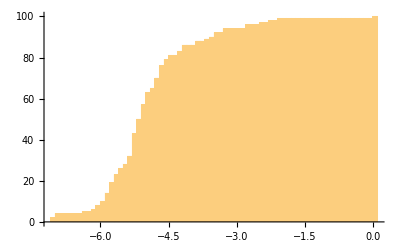

```mathematica
Histogram[Log[Abs[#]]&/@spec,{.1},"CumulativeCount"]
```

```mathematica
hlist=(specAbs=Sort[Log[Abs[#]]&/@spec];Join[{{specAbs_⟦1⟧-1,0}},Transpose[{specAbs,Table[n,{n,1,Length[specAbs]}]}],{{0.5,Length[specAbs]}}]);
```

```mathematica
StringJoin[Table["("<>ToString[N[hlist_⟦n,1⟧]]<>","<>ToString[hlist_⟦n,2⟧]<>")",{n,1,Length[hlist]}]]
```

(-8.09752,0)(-7.09752,1)(-7.09752,2)(-6.92758,3)(-6.92758,4)(-6.3568,5)(-6.1881,6)(-6.04211,7)(-6.04211,8)(-5.92679,9)(-5.92679,10)(-5.85053,11)(-5.85053,12)(-5.84493,13)(-5.84493,14)(-5.73828,15)(-5.72452,16)(-5.72452,17)(-5.72346,18)(-5.72346,19)(-5.68622,20)(-5.68622,21)(-5.62259,22)(-5.62259,23)(-5.58689,24)(-5.58336,25)(-5.58336,26)(-5.44998,27)(-5.44998,28)(-5.39946,29)(-5.39946,30)(-5.32941,31)(-5.32941,32)(-5.29732,33)(-5.29732,34)(-5.29574,35)(-5.29574,36)(-5.29092,37)(-5.29092,38)(-5.25238,39)(-5.24047,40)(-5.24047,41)(-5.20749,42)(-5.20749,43)(-5.1913,44)(-5.1913,45)(-5.16341,46)(-5.15795,47)(-5.15795,48)(-5.14073,49)(-5.14073,50)(-5.07935,51)(-5.07935,52)(-5.04958,53)(-5.04958,54)(-5.04577,55)(-5.04577,56)(-5.0159,57)(-4.93217,58)(-4.93217,59)(-4.90062,60)(-4.90062,61)(-4.90034,62)(-4.90034,63)(-4.88082,64)(-4.88082,65)(-4.7854,66)(-4.7777,67)(-4.7777,68)(-4.73407,69)(-4.73407,70)(-4.66896,71)(-4.66896,72)(-4.63511,73)(-4.63511,74)(-4.63287,75)(-4.63287,76)(-4.53891,77)(-4.53891,78)(-4.52197,79)(-4.4468,80)(-4.4468,81)(-4.23552,82)(-4.23552,83)(-4.16315,84)(-4.13569,85)(-4.13569,86)(-3.8844,87)(-3.8844,88)(-3.64383,89)(-3.53071,90)(-3.41158,91)(-3.41158,92)(-3.29651,93)(-3.29107,94)(-2.77727,95)(-2.71633,96)(-2.47326,97)(-2.26553,98)(-2.0749,99)(0.,100)(0.5,100)

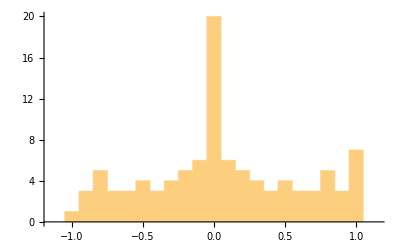

```mathematica
Histogram[Arg[#]/π&/@spec,{-1.15,1.15,.1}]
```

```mathematica
hlist=(specArg=Sort[Arg[#]/π&/@spec];Join[{{-1.15,0}},Transpose[{specArg,Table[n,{n,1,Length[specArg]}]}],{{1.5,Length[specArg]}}]);
```

```mathematica
StringJoin[Table["("<>ToString[N[hlist_⟦n,1⟧]]<>","<>ToString[hlist_⟦n,2⟧]<>")",{n,1,Length[hlist]}]]
```

(-1.15,0)(-0.965977,1)(-0.909168,2)(-0.861394,3)(-0.860472,4)(-0.833907,5)(-0.819877,6)(-0.79017,7)(-0.764562,8)(-0.760092,9)(-0.743343,10)(-0.702418,11)(-0.691458,12)(-0.624718,13)(-0.61781,14)(-0.611305,15)(-0.523442,16)(-0.486418,17)(-0.483138,18)(-0.453322,19)(-0.432859,20)(-0.384682,21)(-0.382524,22)(-0.345302,23)(-0.344141,24)(-0.331645,25)(-0.295553,26)(-0.247371,27)(-0.218828,28)(-0.199771,29)(-0.169853,30)(-0.165107,31)(-0.146592,32)(-0.146539,33)(-0.132882,34)(-0.11351,35)(-0.0883859,36)(-0.0758891,37)(-0.0336054,38)(-0.0330204,39)(-0.0116202,40)(0.,41)(0.,42)(0.,43)(0.,44)(0.,45)(0.,46)(0.,47)(0.,48)(0.,49)(0.,50)(0.,51)(0.,52)(0.,53)(0.,54)(0.0116202,55)(0.0330204,56)(0.0336054,57)(0.0758891,58)(0.0883859,59)(0.11351,60)(0.132882,61)(0.146539,62)(0.146592,63)(0.165107,64)(0.169853,65)(0.199771,66)(0.218828,67)(0.247371,68)(0.295553,69)(0.331645,70)(0.344141,71)(0.345302,72)(0.382524,73)(0.384682,74)(0.432859,75)(0.453322,76)(0.483138,77)(0.486418,78)(0.523442,79)(0.611305,80)(0.61781,81)(0.624718,82)(0.691458,83)(0.702418,84)(0.743343,85)(0.760092,86)(0.764562,87)(0.79017,88)(0.819877,89)(0.833907,90)(0.860472,91)(0.861394,92)(0.909168,93)(0.965977,94)(1.,95)(1.,96)(1.,97)(1.,98)(1.,99)(1.,100)(1.5,100)

### Data for topic patterns

```mathematica
TopicClusters=DeleteCases[NonStopClusters,{_,_,_,"B",_,_,_,_}];
```

```mathematica
Length[TopicClusters]
```

236

```mathematica
SelectedClusters=TopicClusters;
```

```mathematica
TopicClustersLatin=TopicClusters;
```

```mathematica
Timing[PlaTopic=Table[Table[prepP=TransitionMeasure[SelectedClusters_⟦m,1⟧,SelectedClusters_⟦n,1⟧,SelectedClusters_⟦m,5⟧,SelectedClusters_⟦m,6⟧],{n,1,Length[SelectedClusters]}],{m,1,Length[SelectedClusters]}];]
```

{136.922,Null}

```mathematica
Timing[PlaT=Table[v=Table[prepP=PlaTopic_⟦m,n⟧;prepP_⟦1⟧*Exp[-prepP_⟦2⟧],{n,1,100}];v/Total[v],{m,1,100}];]
```

{0.046875,Null}

```mathematica
Timing[spec=Eigenvalues[PlaT];]
```

{1.3125,Null}

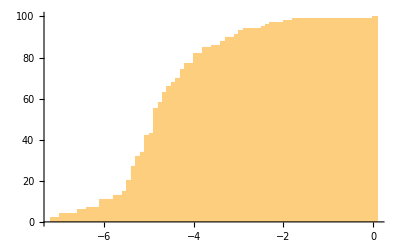

```mathematica
Histogram[Log[Abs[#]]&/@spec,{.1},"CumulativeCount"]
```

```mathematica
hlist=(specAbs=Sort[Log[Abs[#]]&/@spec];Join[{{specAbs_⟦1⟧-1,0}},Transpose[{specAbs,Table[n,{n,1,Length[specAbs]}]}],{{0.5,Length[specAbs]}}]);
```

```mathematica
StringJoin[Table["("<>ToString[N[hlist_⟦n,1⟧]]<>","<>ToString[hlist_⟦n,2⟧]<>")",{n,1,Length[hlist]}]]
```

(-8.11877,0)(-7.11877,1)(-7.11877,2)(-6.93609,3)(-6.93609,4)(-6.59006,5)(-6.59006,6)(-6.34326,7)(-6.04778,8)(-6.04778,9)(-6.03589,10)(-6.03589,11)(-5.76358,12)(-5.76358,13)(-5.54569,14)(-5.54569,15)(-5.48762,16)(-5.46761,17)(-5.46761,18)(-5.44261,19)(-5.44261,20)(-5.38818,21)(-5.38529,22)(-5.38529,23)(-5.34873,24)(-5.34873,25)(-5.30264,26)(-5.30264,27)(-5.25278,28)(-5.22604,29)(-5.22604,30)(-5.21275,31)(-5.21275,32)(-5.16235,33)(-5.16235,34)(-5.09846,35)(-5.09846,36)(-5.09742,37)(-5.09742,38)(-5.08115,39)(-5.08115,40)(-5.07659,41)(-5.07659,42)(-4.94465,43)(-4.8997,44)(-4.8997,45)(-4.89159,46)(-4.89159,47)(-4.88358,48)(-4.88358,49)(-4.88256,50)(-4.88256,51)(-4.85519,52)(-4.85519,53)(-4.8514,54)(-4.8514,55)(-4.76238,56)(-4.76238,57)(-4.71267,58)(-4.69504,59)(-4.69504,60)(-4.66152,61)(-4.63675,62)(-4.63675,63)(-4.54456,64)(-4.52184,65)(-4.52184,66)(-4.43339,67)(-4.43339,68)(-4.34458,69)(-4.34458,70)(-4.2814,71)(-4.25689,72)(-4.21957,73)(-4.21957,74)(-4.17176,75)(-4.13695,76)(-4.13695,77)(-3.96952,78)(-3.96952,79)(-3.96157,80)(-3.96157,81)(-3.95209,82)(-3.79159,83)(-3.76678,84)(-3.76678,85)(-3.5867,86)(-3.37453,87)(-3.37453,88)(-3.29658,89)(-3.21826,90)(-3.04017,91)(-2.99451,92)(-2.99451,93)(-2.89712,94)(-2.47562,95)(-2.38374,96)(-2.22461,97)(-1.92866,98)(-1.76878,99)(0.,100)(0.5,100)

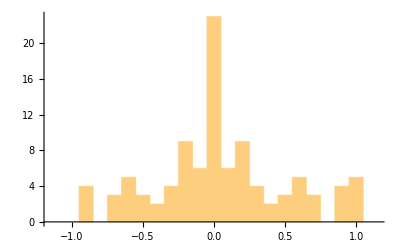

```mathematica
Histogram[Arg[#]/π&/@spec,{-1.15,1.15,.1}]
```

```mathematica
hlist=(specArg=Sort[Arg[#]/π&/@spec];Join[{{-1.15,0}},Transpose[{specArg,Table[n,{n,1,Length[specArg]}]}],{{1.5,Length[specArg]}}]);
```

```mathematica
StringJoin[Table["("<>ToString[N[hlist_⟦n,1⟧]]<>","<>ToString[hlist_⟦n,2⟧]<>")",{n,1,Length[hlist]}]]
```

(-1.15,0)(-0.932063,1)(-0.889854,2)(-0.888433,3)(-0.873703,4)(-0.72526,5)(-0.713919,6)(-0.669178,7)(-0.638054,8)(-0.628636,9)(-0.605133,10)(-0.576449,11)(-0.560913,12)(-0.530774,13)(-0.469492,14)(-0.466537,15)(-0.443583,16)(-0.403664,17)(-0.344678,18)(-0.31597,19)(-0.291166,20)(-0.25257,21)(-0.249759,22)(-0.220998,23)(-0.211693,24)(-0.192402,25)(-0.191004,26)(-0.185929,27)(-0.185644,28)(-0.171661,29)(-0.16672,30)(-0.120459,31)(-0.117189,32)(-0.111084,33)(-0.110168,34)(-0.0516396,35)(-0.0511886,36)(-0.0388544,37)(-0.0366759,38)(0.,39)(0.,40)(0.,41)(0.,42)(0.,43)(0.,44)(0.,45)(0.,46)(0.,47)(0.,48)(0.,49)(0.,50)(0.,51)(0.,52)(0.,53)(0.,54)(0.,55)(0.,56)(0.,57)(0.0366759,58)(0.0388544,59)(0.0511886,60)(0.0516396,61)(0.110168,62)(0.111084,63)(0.117189,64)(0.120459,65)(0.16672,66)(0.171661,67)(0.185644,68)(0.185929,69)(0.191004,70)(0.192402,71)(0.211693,72)(0.220998,73)(0.249759,74)(0.25257,75)(0.291166,76)(0.31597,77)(0.344678,78)(0.403664,79)(0.443583,80)(0.466537,81)(0.469492,82)(0.530774,83)(0.560913,84)(0.576449,85)(0.605133,86)(0.628636,87)(0.638054,88)(0.669178,89)(0.713919,90)(0.72526,91)(0.873703,92)(0.888433,93)(0.889854,94)(0.932063,95)(1.,96)(1.,97)(1.,98)(1.,99)(1.,100)(1.5,100)

### Word translation

#### Bulk vectors

```mathematica
EnglishRef=TopicClustersEnglish;
```

```mathematica
LatinRef=TopicClustersLatin;
```

```mathematica
PandPChapEnglish=StringSplit[ExampleData[{"Text","PrideAndPrejudice"}],"Chapter "~~DigitCharacter..~~" "];
```

```mathematica
Length[PandPChapEnglish]
```

61

```mathematica
VecEnglish=Table[{EnglishRef_⟦k,1⟧,StringCount[PandPChapEnglish,WordBoundary~~Alternatives@@(#_⟦1⟧&/@EnglishRef_⟦k,1⟧)~~WordBoundary,IgnoreCase->True]},{k,1,Length[EnglishRef]}];
```

```mathematica
PandPChapLatin=StringSplit[StringReplace[ImportString[StringReplace[StringReplace[StringReplace[StringReplace[Import["PandP_Latin.txt"],"\n":>"\n 舜"],{(s:("舜"~~Repeated[Except["\n"],{2,60}]))~~" \n":>s<>" 垚 "}],"":>""],{"舜":>""}],"HTML"],"垚":>"\n\n"],"CAPITULUM "~~("PRIMUM"|(("I"|"V"|"X"|"L")..))];
```

```mathematica
Length[PandPChapLatin]
```

61

```mathematica
VecLatin=Table[{LatinRef_⟦k,1⟧,StringCount[PandPChapLatin,WordBoundary~~Alternatives@@(#_⟦1⟧&/@LatinRef_⟦k,1⟧)~~WordBoundary,IgnoreCase->True]},{k,1,Length[LatinRef]}];
```

```mathematica
FlatScreenedPairs=Flatten[Table[{#_⟦1⟧,#_⟦2,k⟧},{k,1,Length[#_⟦2⟧]}]&/@Select[Table[{EnglishRef[[k,1]],#_⟦1⟧&/@Select[VecLatin,JaccardRuzickaSim[#_⟦2⟧,Cases[VecEnglish,{EnglishRef[[k,1]],___}]_⟦1,2⟧]≥Max[1-7/100*√61,1-√(Length[Select[Min[#]&/@Transpose[{#_⟦2⟧,Cases[VecEnglish,{EnglishRef[[k,1]],___}]_⟦1,2⟧}],#>0&]]/Total[Max[#]&/@Transpose[{#_⟦2⟧,Cases[VecEnglish,{EnglishRef[[k,1]],___}]_⟦1,2⟧}]])]&]},{k,1,Length[EnglishRef]}],Length[#_⟦2⟧]>0&],1];
```

```mathematica
SiftedTags=Union[(#_⟦1⟧&/@FlatScreenedPairs)];SiftedEnglishRef=Reverse[SortBy[Table[Cases[EnglishRef,{SiftedTags[[k]],___}]_⟦1⟧,{k,1,Length[SiftedTags]}],#_⟦3⟧&]];
```

```mathematica
SiftedTags=Union[(#_⟦2⟧&/@FlatScreenedPairs)];SiftedLatinRef=Reverse[SortBy[Table[Cases[LatinRef,{SiftedTags[[k]],___}]_⟦1⟧,{k,1,Length[SiftedTags]}],#_⟦3⟧&]];
```

```mathematica
Length[SiftedEnglishRef]
```

75

```mathematica
Length[SiftedLatinRef]
```

74

#### Spectral parameters for English

```mathematica
FromTopics=SiftedEnglishRef;
```

```mathematica
FromDelta=ReadDelta[#]&/@FromTopics;
```

```mathematica
FromN=(#_⟦3⟧-1)&/@FromTopics;
```

```mathematica
AbsoluteTiming[KinSpecSWLongTag[TopicClustersEnglish,PenTopic,#_⟦1⟧&/@FromTopics];]
```

{40.7135,Null}

```mathematica
FromKinQ=KinQ;
```

```mathematica
FromEta=SemanticComplexities;
```

#### Spectral parameters for Latin

```mathematica
ToTopicsLatin=SiftedLatinRef;
```

```mathematica
Length[ToTopicsLatin]
```

74

```mathematica
ToDeltaLatin=ReadDelta[#]&/@ToTopicsLatin;
```

```mathematica
ToNLatin=(#_⟦3⟧-1)&/@ToTopicsLatin;
```

```mathematica
AbsoluteTiming[KinSpecSWLongTag[TopicClustersLatin,PlaTopic,#_⟦1⟧&/@ToTopicsLatin];]
```

{70.1045,Null}

```mathematica
ToKinLatin=KinQ;
```

```mathematica
ToEtaLatin=SemanticComplexities;
```

#### Translation

```mathematica
AbsoluteTiming[fromLabeled=Transpose[{#_⟦1⟧&/@FromTopics,FromKinQ}];toLabeled=Transpose[{#_⟦1⟧&/@ToTopicsLatin,ToKinLatin}];Report=Table[{FlatScreenedPairs_⟦k⟧,(JaccardRuzickaSim[Cases[fromLabeled,{FlatScreenedPairs_⟦k,1⟧,_}]_⟦1,2⟧,Cases[toLabeled,{FlatScreenedPairs_⟦k,2⟧,_}]_⟦1,2⟧])},{k,1,Length[FlatScreenedPairs]}];]
```

{0.011409,Null}

```mathematica
prep=Union[Select[Table[{Report_⟦n,1,1⟧,Report_⟦n,1,2⟧,Report_⟦n,2⟧},{n,1,Length[Report]}],#_⟦3⟧≥0.7&]];g=Graph[(#_⟦1⟧->#_⟦2⟧)&/@prep,EdgeWeight->(#_⟦3⟧&/@prep)];(KuhnSln={#,FindRowRank[#,prep],FindColRank[#,prep]}&/@Select[{#,PropertyValue[{g,#},EdgeWeight]}&/@FindIndependentEdgeSet[g],#_⟦2⟧>0&])//TableForm
```

{{Brighton,24}}->{{britona,4},{britonae,7},{britonam,12},{britonensi,1}}
0.91232861932787 | 1 | 1
{{Bourgh,35},{Bourgh's,4}}->{{burghani,2},{burghana,21},{burghanae,7},{burghanam,9},{burghano,1}}
0.83142101497287 | 1 | 1
{{Derbyshire,24}}->{{derventiani,3},{derventiano,14},{derventianum,5}}
0.82888868425612 | 1 | 1
{{library,23}}->{{bibliotheca,16},{bibliothecam,9}}
0.89178011863075 | 1 | 1
{{London,55}}->{{londini,1},{londinii,52},{londinio,8},{londinium,34}}
0.78372816280639 | 1 | 1
{{Meryton,57}}->{{merytona,4},{merytonae,28},{merytonam,22},{merytoniano,1}}
0.81347469466516 | 1 | 1
{{money,26}}->{{pecunia,14},{pecuniae,4},{pecuniam,12},{pecuniariae,1},{pecuniarium,1},{pecuniarius,1},{pecuniosa,1},{pecuniosissimam,1}}
0.81751183983685 | 1 | 1
{{Mrs,343}}->{{mra,328}}
0.91595768725868 | 1 | 1
{{Netherfield,73}}->{{infrapratense,4},{infrapratensem,45},{infrapratensi,14},{infrapratensis,6}}
0.87345290322469 | 1 | 1
{{Pemberley,53}}->{{pemberleiani,1},{pemberleia,1},{pemberleiae,2},{pemberleiam,5},{pemberleiana,7},{pemberleianae,8},{pemberleianam,17},{pemberleianas,2},{pemberleianis,1},{pemberleiano,2},{pemberleianum,6}}
0.84176324197525 | 1 | 1
{{Rosings,49}}->{{rosae,1},{rosaria,8},{rosariae,5},{rosariam,33}}
0.89713910874429 | 1 | 1
{{sir,78}}->{{senior,25},{seniore,10},{seniorem,11},{seniori,3},{senioris,12},{senioritate,1}}
0.89202750479836 | 1 | 2
{{thousand,34}}->{{libra,1},{librae,1},{libras,2},{libri,3},{libris,8},{libro,4},{librarum,23},{liber,2},{libros,4},{librum,10},{librorum,3}}
0.77210458895375 | 1 | 1
{{breakfast,21},{breakfasted,1}}->{{ientant,1},{ientaculariam,4},{ientaculario,1},{ientandum,2},{ientaculo,4},{ientaculum,6},{ientatum,4},{ientavimus,1},{ientavissent,1},{ientavisset,1},{ientem,1},{ientorium,1}}
0.70602592030052 | 1 | 1
{{Catherine,110},{Catherine's,16}}->{{caterina,80},{caterinae,37},{caterinam,24},{caterinamque,1}}
0.88159310716123 | 1 | 1
{{Charlotte,68},{Charlotte's,17}}->{{carlotta,51},{carlottae,15},{carlottam,18},{carlottaque,1}}
0.84781866608925 | 1 | 1
{{Collins,156},{Collins's,24}}->{{collinas,6},{collinis,1},{collina,119},{collinae,34},{collinam,27},{collinarum,3}}
0.87062593700051 | 1 | 1
{{colonel,65},{colonel's,1}}->{{praefecte,1},{praefecti,10},{praefectis,1},{praefecto,12},{praefectum,11},{praefectus,34}}
0.77635113155214 | 1 | 1
{{Darcy,374},{Darcy's,44}}->{{darcei,23},{darceia,22},{darceiae,14},{darceiam,7},{darceiani,1},{darceii,45},{darceiique,1},{darceio,70},{darceioque,1},{darceium,75},{darceius,176},{darceianum,2}}
0.89541301918349 | 1 | 1
{{father,116},{father's,19}}->{{pater,72},{pateretur,1},{patre,29},{patrem,30},{patri,3},{patris,20},{patroni,1},{paternis,1}}
0.91463313182815 | 1 | 1
{{Fitzwilliam,32},{Fitzwilliam's,5}}->{{filgulielmi,8},{filgulielmum,4},{filgulielmus,18}}
0.81461834944205 | 1 | 1
{{Jane,263},{Jane's,28}}->{{ioanna,187},{ioannae,48},{ioannam,55},{ioannamque,1},{ioannaque,3},{ioannes,1}}
0.88499281328637 | 1 | 1
{{Kitty,69},{Kitty's,2}}->{{kitteia,53},{kitteiae,4},{kitteiam,9},{kitteiaque,4}}
0.91931912561749 | 1 | 1
{{Lizzy,95},{Lizzy's,2}}->{{lisula,85},{lisulae,4},{lisulam,6}}
0.92320751300086 | 1 | 1
{{Lydia,133},{Lydia's,38}}->{{lydia,104},{lydiae,34},{lydiaeque,1},{lydiam,20},{lydiamque,3},{lydiaque,10}}
0.88796539015088 | 1 | 1
{{mile,5},{miles,16}}->{{pandendam,1},{panditur,1},{passum,1},{passuum,20}}
0.8726209138887 | 1 | 1
{{surprise,37},{surprised,35}}->{{attonetur,1},{attonita,40},{attonitae,5},{attoniti,6},{attonitiores,1},{attonitos,1},{attonitum,1},{attonitura,1},{attonitus,12},{attonituram,1},{attonuit,1}}
0.77224691259775 | 1 | 1
{{week,29},{weeks,18}}->{{septimana,12},{septimanae,4},{septimanam,16},{septimanas,16},{septimanis,16},{septimanos,1}}
0.7874978658374 | 1 | 1
{{Wickham,162},{Wickham's,32}}->{{vicham,69},{vichami,42},{vichamum,42},{vichama,3},{vichame,1},{vichamo,49}}
0.78016927125125 | 1 | 1
{{William,40},{William's,6}}->{{gulielmi,6},{gulielmum,11},{gulielmus,18}}
0.89361876555711 | 2 | 1
{{window,16},{windows,6}}->{{fenus,1},{fenestra,8},{fenestras,1},{fenestrae,2},{fenestram,11},{fenestrarum,1}}
0.87720521089695 | 1 | 1
{{aunt,78},{aunt's,6},{aunts,1}}->{{amita,1},{amitae,3},{amitam,1},{matertera,47},{materterae,7},{materteraeque,3},{materteram,13},{materteramque,5},{materteraque,5}}
0.87814761808035 | 1 | 1
{{Bennet,294},{Bennet's,29},{Bennets,10}}->{{bennet,298},{benneta,1},{bennetae,12},{bennetam,5},{bennetanam,1},{benneti,4},{bennetis,3},{benneto,5},{bennetos,2},{bennett,6}}
0.91002901649813 | 1 | 1
{{cousin,41},{cousin's,8},{cousins,11}}->{{consobrina,16},{consobrinae,2},{consobrinam,8},{consobrinarum,2},{consobrinas,4},{consobrini,7},{consobrinis,3},{consobrino,5},{consobrinos,1},{consobrinum,8},{consobrinus,9}}
0.88047316644191 | 1 | 1
{{dear,158},{dearly,3},{dearest,17}}->{{carissima,95},{carissimae,3},{carissimam,4},{carissimarum,1},{carissime,22},{carissimi,1},{carissimo,3},{carissimum,1},{carissimus,2},{caro,3},{carum,1},{cara,17},{caram,1},{cari,2},{carior,1},{caritas,5},{caritate,3},{caritatem,8},{caritatis,2}}
0.89181381097247 | 1 | 1
{{Eliza,22},{Elizabeth,597},{Elizabeth's,38}}->{{eliza,18},{elizam,1},{elizabeth,3},{elizabetha,534},{elizabethae,82},{elizabetham,70},{elizabethaque,3}}
0.83096613372453 | 1 | 1
{{evening,72},{evening's,2},{evenings,4}}->{{vespere,26},{vesperi,7},{vesperis,2},{vespero,2},{vesperandi,1},{vesperem,32},{vesperes,4},{vespertina,3},{vespertinas,2},{vespertinis,2},{vespertinum,4},{vespertinus,1},{vesperum,2},{vesper,3}}
0.8576858401194 | 1 | 1
{{eye,15},{eyeing,1},{eyes,52}}->{{oculi,8},{oculis,18},{oculo,1},{oculos,33},{oculum,1}}
0.81998944724122 | 1 | 1
{{Forster,38},{Forster's,1},{Forsters,1}}->{{forstro,1},{forster,18},{forstera,5},{forsteri,2},{forstero,5},{forsterae,2},{forsteram,4},{forsterum,3}}
0.83159910167647 | 1 | 1
{{letter,115},{letters,16},{letter-paper,1}}->{{litteris,44},{litterulis,1},{litterulas,3},{litteras,74},{litterasque,1},{litterae,14},{litterarum,3}}
0.7707632399347 | 1 | 1
{{man,145},{man's,5},{men,33}}->{{homini,4},{homine,21},{hominem,32},{homines,32},{hominis,17},{hominum,15},{hominibus,7},{homo,56},{homiliae,1},{homiliam,1}}
0.92674955139104 | 1 | 1
{{maternal,2},{mother,110},{mother's,25}}->{{matre,12},{matrem,34},{matremque,1},{matreque,2},{matri,4},{matris,30},{matrique,1}}
0.91348273628128 | 1 | 1
{{Phillip's,1},{Phillips,26},{Phillips's,5}}->{{philipa,13},{philipae,2},{philipam,4},{philipi,2},{philipo,1},{philipos,1},{philips,8},{philipsis,1},{philipum,1},{philipus,1}}
0.92102431054531 | 1 | 1
{{uncle,59},{uncle's,9},{uncles,3}}->{{avuncule,1},{avunculis,1},{avunculo,12},{avunculos,1},{avunculum,16},{avunculumque,1},{avunculus,26},{patrui,1},{patruum,1}}
0.8816759212707 | 1 | 1
{{wife,44},{wife's,3},{wives,1}}->{{uxore,9},{uxori,5},{uxoris,12},{uxorisque,1},{uxor,19},{uxorem,12},{uxoremque,2},{uxorque,1}}
0.90902325240592 | 1 | 1
{{year,28},{years,33},{years',2}}->{{anna,3},{annae,2},{anni,7},{annis,19},{anniti,1},{anno,7},{annon,17},{annos,37},{annum,18},{annuus,1},{annueret,1},{annui,1},{annesleia,3}}
0.91613794181665 | 1 | 1
{{young,130},{younger,30},{youngest,13}}->{{nata,17},{natae,3},{natam,1},{natare,1},{natatorii,1},{nati,1},{natis,1},{nativa,2},{nativitatis,6},{nativos,1},{natus,6},{natu,74},{natum,2},{natura,52},{naturam,19},{naturum,1},{naturus,1},{naturae,8},{natalem,1}}
0.78869199219213 | 1 | 1
{{Bingley,257},{Bingley's,49},{Bingleys,4},{Bingleys',1}}->{{bingleae,1},{binglei,8},{bingleia,68},{bingleiae,12},{bingleiam,8},{bingleii,33},{bingleiis,2},{bingleio,42},{bingleios,2},{bingleium,48},{bingleiumque,2},{bingleius,97},{bingley,1}}
0.87834366017885 | 1 | 1
{{brother,62},{brotherly,2},{brother's,13},{brothers,2}}->{{fratre,18},{fratrem,18},{fratri,2},{fratria,1},{fratris,19},{fratrisque,1},{fratrum,2}}
0.94775659879148 | 1 | 1
{{daily,3},{day,130},{day's,4},{days,30}}->{{die,102},{diebus,23},{diei,9},{diem,37},{dies,34}}
0.86914612718125 | 2 | 1
{{length,32},{long,114},{longed,9},{longing,2},{longer,44}}->{{visa,33},{visae,3},{visam,5},{visant,1},{visas,2},{visere,4},{visendam,1},{visendum,1},{viseret,1},{visis,17},{visitare,2},{visitabo,1},{visitatores,1},{visitatrix,1},{visitatum,1},{visitaverat,1},{viso,20},{visos,1},{visu,28},{visum,60},{visura,1},{visus,23},{visuros,1},{visurum,1},{visitandi,2}}
0.74430298703125 | 1 | 2
{{daughter,78},{daughter's,7},{daughters,49},{daughters',1}}->{{filia,56},{filias,24},{filiasque,2},{filiabus,26},{filiae,34},{filiaeque,3},{filiam,38},{filiamque,4},{filiaque,3},{filiarum,11},{filiarumque,1}}
0.91738057398929 | 1 | 1
{{dine,16},{dined,8},{dines,1},{dining,6}}->{{coena,4},{coenare,3},{coenas,1},{coenacula,2},{coenaculo,2},{coenae,2},{coenam,22},{coenamus,1},{coenabunt,2},{coenandi,8},{coenandum,1},{coenarent,3},{coenaret,1},{coenatio,1},{coenatum,8},{coenaturi,1},{coenaturam,1},{coenaturum,1},{coenaverunt,3},{coenavit,3},{coenavisse,1},{coenes,1},{coenatione,3},{coenationem,6}}
0.75937114044633 | 1 | 1
{{enter,12},{entered,36},{entrance,12},{entrance-hall,1}}->{{ingrati,2},{ingratior,1},{ingratum,1},{ingratus,2},{ingressa,6},{ingressae,3},{ingressi,4},{ingressis,1},{ingresso,1},{ingressos,1},{ingressum,2},{ingressus,8},{ingressuros,1},{ingrederentur,1},{ingredi,2},{ingrediantur,1},{ingreditur,1},{ingredientes,2}}
0.85430954549048 | 1 | 1
{{honour,42},{honoured,9},{honours,2},{honourable,6}}->{{honore,9},{honoris,4},{honos,4},{honoreque,1},{honorant,1},{honorandum,2},{honoraretur,1},{honoratam,1},{honorati,1},{honoratus,3},{honorem,6}}
0.81933186049799 | 1 | 1
{{Lucas,65},{Lucas's,5},{Lucases,13},{Lucases',1}}->{{lucas,57},{lucasa,4},{lucasae,1},{lucasam,2},{lucases,1},{lucasi,4},{lucasiana,1},{lucasianae,1},{lucasianam,4},{lucasis,4},{lucasos,3},{lucasorum,1},{lucasanas,1}}
0.89297995906056 | 1 | 1
{{vanish,1},{vanished,2},{vain,20},{vanity,18}}->{{vana,4},{vanam,1},{vanas,1},{vane,3},{vanis,1},{vanitas,4},{vanitate,7},{vanitatem,4},{vanitates,1},{vanitati,1},{vanitatis,2},{vano,8},{vanus,1}}
0.8391368681474 | 1 | 1
{{congratulate,7},{congratulated,2},{congratulation,1},{congratulations,12},{congratulatory,1}}->{{gratulari,3},{gratularis,1},{gratulabatur,1},{gratulando,1},{gratularer,1},{gratularetur,1},{gratulata,2},{gratulatoria,1},{gratulatura,1},{gratulatus,4},{gratulor,4},{gratulabundae,1}}
0.91975148625934 | 1 | 1
{{house,106},{houses,4},{household,1},{housemaid,2},{housemaids,1}}->{{domi,19},{domibus,1},{domo,29},{domum,83},{domus,12}}
0.756483145696 | 1 | 1
{{miss,283},{missed,3},{missing,1},{missent,2},{missish,1}}->{{hera,181},{herae,51},{heraeque,1},{heram,43},{heramque,1},{heraque,1},{hero,3},{herum,1},{herus,1},{hariolaris,1}}
0.86564008933856 | 1 | 1
{{refuse,9},{refused,6},{refusing,7},{refusal,7},{refusals,1}}->{{recusanti,2},{recusare,6},{recusas,3},{recusat,3},{recusabit,1},{recusabo,2},{recusandae,1},{recusarem,1},{recusarent,1},{recusares,1},{recusato,1},{recusatum,2},{recusaverat,2},{recusaverunt,1},{recusavi,1},{recusavisti,1},{recusavit,5},{recusavisse,2},{recusem,1},{recuso,1},{recusans,5},{recusante,1},{recusantem,1}}
0.77132723971091 | 1 | 1
{{serve,2},{serving,1},{servant,15},{servant's,2},{servants,12}}->{{ministri,5},{ministris,6},{ministro,1},{minister,6},{ministrae,3},{ministram,1},{ministrare,1},{ministros,3},{ministrum,4},{ministerii,1},{ministerio,1}}
0.85266604008217 | 1 | 1
{{talk,32},{talked,38},{talking,39},{talks,1},{talker,1}}->{{colloquamur,3},{colloquaris,1},{colloquebantur,1},{colloquebatur,3},{colloquendi,5},{colloquendo,2},{colloquendum,4},{colloqueremini,1},{colloqueremur,1},{colloquerentur,3},{colloqueretur,4},{colloqui,22},{colloquia,1},{colloquibus,1},{colloquii,2},{colloquio,8},{colloquitur,1},{colloquium,17},{collocuta,2},{collocuti,8},{colloquor,1},{collocutos,1},{collocutor,1},{collocutorem,1},{collocutum,1},{collocutus,3},{colloquuntur,3},{colloquens,2},{colloquente,1},{colloquentem,2},{colloquentes,4},{colloquentibus,2}}
0.83437868075902 | 1 | 1
{{walk,51},{walked,44},{walking,26},{walks,3},{walker,3}}->{{ambulare,18},{ambulat,3},{ambulabam,1},{ambulabat,6},{ambulabo,1},{ambulando,8},{ambulandum,2},{ambularemus,1},{ambularent,3},{ambularet,2},{ambulatio,1},{ambulatrix,1},{ambulaturi,1},{ambulatum,1},{ambulatura,1},{ambulaturas,1},{ambulaverat,1},{ambulaverunt,4},{ambulavisti,1},{ambulavit,8},{ambulavisse,1},{ambules,1},{ambulo,1},{ambulans,6},{ambulant,6},{ambulante,1},{ambulantem,1}}
0.8030304792094 | 1 | 1
{{feel,39},{feeling,38},{feelingly,1},{feelings,86},{feels,4},{felt,100}}->{{sensa,1},{senserem,1},{senseret,1},{senserunt,1},{sensim,1},{sensit,21},{sensu,6},{sensum,7},{sensus,9},{sensuum,3},{sensibus,9},{sensisset,2},{sentit,1},{sentiunt,1},{sentiebam,1},{sentiebat,3},{sentiendum,1},{sentirem,3},{sentiret,8},{sentiverat,1},{sentivit,2},{sententias,45},{sententiis,22},{sententia,43},{sententiae,24},{sententiam,41},{sententiarum,8}}
0.90987721777478 | 1 | 1
{{forget,17},{forgetfulness,1},{forgets,1},{forgetting,2},{forgot,5},{forgotten,12}}->{{obliviscamur,1},{obliviscar,4},{obliviscere,1},{oblivisceris,2},{oblivisci,5},{obliviscitur,1},{obliviscenda,2},{obliviscendae,2},{obliviscerentur,1},{oblivisceretur,5},{obliviscor,2}}
0.75983940770097 | 1 | 1
{{marriage,66},{married,61},{marry,42},{marrying,23},{matrimonial,1},{matrimony,6}}->{{matrimoniam,1},{matrimonii,13},{matrimonio,19},{matrimonium,113},{matrimoniali,1}}
0.87238771707006 | 1 | 1
{{office,6},{officer,8},{officers,29},{officers',2},{officiousness,1},{officious,3}}->{{subpraefecti,10},{subpraefectis,7},{subpraefectisque,1},{subpraefecto,4},{subpraefectos,13},{subpraefectum,1},{subpraefectus,2},{subpraefectorum,1}}
0.74322630641739 | 1 | 1
{{write,39},{writes,1},{writing,12},{written,19},{writer,3},{wrote,21}}->{{scriba,1},{scribam,3},{scribas,3},{scribe,1},{scribebat,2},{scribenda,2},{scribendae,1},{scribendas,4},{scribendi,1},{scribendo,3},{scribendum,3},{scripserat,2},{scriberem,1},{scriberentur,1},{scriberes,1},{scriberet,2},{scripsi,3},{scribis,2},{scribit,3},{scribo,1},{scribunt,1},{scripsisti,1},{scripsit,15},{scripta,7},{scriptae,2},{scriptas,2},{scripti,1},{scriptis,6},{scripsisse,3},{scripsisset,1},{scriptore,1},{scriptoris,4},{scriptor,1},{scriptorem,1},{scriptoria,1},{scriptorum,1},{scriptum,6},{scripturum,1},{scribens,8},{scribentur,1},{scribere,14}}
0.86972175086369 | 1 | 1
{{speak,66},{speaking,33},{speaks,3},{speaker,1},{spoke,43},{spoken,16},{spokesman,1}}->{{loquar,3},{loquatur,3},{loqueris,10},{loquenti,1},{loquere,3},{loquebantur,1},{loquebatur,1},{loquendo,8},{loquendum,6},{loquerentur,1},{loquereris,1},{loquerer,2},{loqueretur,7},{loquetur,1},{loqui,46},{loquimini,1},{loquitur,10},{locuta,28},{locuti,2},{loquor,6},{locutae,3},{locutam,2},{locutio,1},{locutoris,1},{locutum,1},{locutus,29},{locuturam,1},{locuturus,1},{loquacitate,1},{loquax,1}}
0.83893295869784 | 1 | 1
{{please,14},{pleased,39},{pleases,2},{pleasing,22},{pleasant,21},{pleasantly,4},{pleasantness,3},{pleasanter,2},{pleasantry,2},{pleasantest,1}}->{{honesta,3},{honestas,1},{honestat,1},{honestaberis,1},{honestatatis,1},{honestate,3},{honestatem,4},{honestatis,1},{honestatura,1},{honeste,3},{honesti,4},{honestior,15},{honestis,1},{honestissima,1},{honestissime,3},{honestissimus,1},{honestius,1},{honestus,1},{honestiore,8},{honestiori,4},{honestioris,7},{honestiorem,15},{honestiores,21},{honestioribus,9},{honestiorum,2}}
0.78205401370154 | 1 | 1

```mathematica
ResiftedTags=Union[(#_⟦1⟧&/@prep)];ResiftedEnglishRef=Reverse[SortBy[Table[Cases[EnglishRef,{ResiftedTags[[k]],___}]_⟦1⟧,{k,1,Length[ResiftedTags]}],#_⟦3⟧&]];
```

```mathematica
ResiftedTags=Union[(#_⟦2⟧&/@prep)];ResiftedLatinRef=Reverse[SortBy[Table[Cases[LatinRef,{ResiftedTags[[k]],___}]_⟦1⟧,{k,1,Length[ResiftedTags]}],#_⟦3⟧&]];
```

```mathematica
SemanticSim={Position[ResiftedEnglishRef,{#_⟦1⟧,___}]_⟦1,1⟧,Position[ResiftedLatinRef,{#_⟦2⟧,___}]_⟦1,1⟧,#_⟦3⟧}&/@prep;
```

```mathematica
OptimalNodes={Position[ResiftedEnglishRef,{#_⟦1,1,1⟧,___}]_⟦1,1⟧,Position[ResiftedLatinRef,{#_⟦1,1,2⟧,___}]_⟦1,1⟧,#_⟦2,1,1⟧,#_⟦3,1,1⟧}&/@KuhnSln;
```

```mathematica
Export["PnP_EnglishLatin.txt","%tournament\n"<>StringJoin[Riffle[Flatten["\\put("<>ToString[1.5+1+4#_⟦2⟧]<>","<>ToString[90-4#_⟦1⟧]<>"){\\color[rgb]"<>ToString[TempRGB[#_⟦3⟧]]<>"{\\rule{4pt}{4pt}}}"&/@SemanticSim],"\n"]]<>"\n%crosshairs\n"<>StringJoin[Riffle["\n%"<>ResiftedEnglishRef[[#_⟦1⟧,1,1,1]]<>"_"<>ResiftedLatinRef[[#_⟦2⟧,1,1,1]]<>"
\\put("<>ToString[1.5+4#_⟦2⟧+3]<>","<>ToString[90-4#_⟦1⟧+2]<>"){\\color{green}\\linethickness{"<>ToString[1.5/#_⟦3⟧]<>"pt}\\line(-1,0){"<>ToString[4#_⟦2⟧-2]<>"}\\linethickness{"<>ToString[1.5/#_⟦4⟧]<>"pt}\\line(0,1){"<>ToString[4#_⟦1⟧-2]<>"}}"&/@OptimalNodes,"\n"]]];
```

#### English labels

```mathematica
FromClusters=ResiftedEnglishRef;
```

```mathematica
ScoredCluster={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧,Total[#_⟦3⟧],#_⟦5⟧}&/@((prep=Transpose[CensorCluster[#_⟦1⟧]];{#_⟦2⟧,prep_⟦1⟧,prep_⟦2⟧,#_⟦3⟧,#_⟦4⟧})&/@FromClusters);
```

```mathematica
EnglishCompress[w_]:=StringReplace[w,{"ai":>"𝔸","ea":>"𝕀","ou":>"𝕌","ee":>"𝔼","oo":>"𝕆"}]
```

```mathematica
EnglishDecompress[w_]:=StringReplace[w,{"𝔸":>"ai","𝕀":>"ea","𝕌":>"ou","𝔼":>"ee","𝕆":>"oo"}]
```

```mathematica
EvenOut[cl_]:=(prep=EnglishCompress[cl_⟦1⟧];L=Max[StringLength[prep]];{#_⟦1⟧<>StringJoin[Table[" ",{L-StringLength[#_⟦1⟧]}]],#_⟦2⟧}&/@Transpose[{prep,cl_⟦2⟧}])
```

```mathematica
SplitEven[ecl_]:=(L=StringLength[ecl_⟦1,1⟧];Table[{m,EnglishDecompress[StringTake[#_⟦1⟧,{m}]],#_⟦2⟧}&/@ecl,{m,1,L}]);
```

```mathematica
MergeStem[spl_]:=SortBy[(prep=ConnectedComponents[Graph[Join[Table[If[(Length[Union[#_⟦2⟧&/@spl_⟦n⟧]]==1)&&(Length[Union[#_⟦2⟧&/@spl_⟦n+1⟧]]==1),spl_⟦n⟧<->spl_⟦n+1⟧,spl_⟦n⟧<->spl_⟦n⟧],{n,1,Length[spl]-1}],{Last[spl]<->Last[spl]}]]];If[Length[#]>1,{{SortBy[Transpose[#]_⟦1⟧,First]_⟦1,1⟧,StringJoin[#1_⟦2⟧&/@SortBy[Transpose[#]_⟦1⟧,First]],Total[#1_⟦3⟧&/@#_⟦1⟧]}},Flatten[#,1]]&/@prep),First]
```

```mathematica
ColSort[col_]:={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧}&/@Reverse[SortBy[{Flatten[Union[#_⟦1⟧]],Union[#_⟦2⟧]_⟦1⟧,Total[#_⟦3⟧],Min[#_⟦4⟧]}&/@(Transpose[#]&/@(ConnectedComponents[Graph[Join[Table[If[col_⟦k,2⟧==col_⟦k+1,2⟧,{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k+1,1⟧,col_⟦k+1,2⟧,col_⟦k+1,3⟧,k+1},{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}],{k,1,Length[col]-1}],{{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}<->{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}}]]])),Last]]
```

```mathematica
CumHeight[cl_]:=(ch=0;s={};For[n=1,n<=Length[cl],n++,{s=Join[s,{{cl_⟦n,1⟧,cl_⟦n,2⟧,cl_⟦n,3⟧,ch}}];ch=ch+cl_⟦n,3⟧}];s)
```

```mathematica
Word2BarChart[cl_]:=CumHeight[#]&/@(ColSort[#]&/@MergeStem[SplitEven[EvenOut[cl]]])
```

```mathematica
Export["EnglishLabels_for_Latin_PnP.txt",StringJoin[Table[(BCData=Word2BarChart[{ScoredCluster_⟦k,2⟧,ScoredCluster_⟦k,3⟧}];H=ScoredCluster_⟦k,4⟧;"\\put("<>ToString[5-3Total[Max/@StringLength/@(Transpose[#]_⟦2⟧&/@BCData)]]<>","<>ToString[91.75-1.5-4k]<>"){"<>"\\textbf{"<>"\\setlength{\\unitlength}{3pt}"<>StringJoin[hpos=0;Table[hinc=Max[StringLength/@Transpose[BCData_⟦m⟧]_⟦2⟧];hpos=hpos+hinc;Table[If[BCData_⟦m,n,2⟧==" ","","\\BC{"<>ToString[hpos-hinc]<>"}{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>(ToString[hinc])<>"}{"<>ToString[N[Round[BCData_⟦m,n,3⟧/H,10^-3]]]<>"}{"<>ToUpperCase[BCData_⟦m,n,2⟧]<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"}}\n",{k,1,Length[ScoredCluster]}]]]
```

EnglishLabels_for_Latin_PnP.txt

#### Latin labels

```mathematica
FromClusters=ResiftedLatinRef;
```

```mathematica
ScoredCluster={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧,Total[#_⟦3⟧],#_⟦5⟧}&/@((prep=Transpose[CensorCluster[#_⟦1⟧]];{#_⟦2⟧,prep_⟦1⟧,prep_⟦2⟧,#_⟦3⟧,#_⟦4⟧})&/@FromClusters);
```

```mathematica
LatinCompress[w_]:=StringReplace[w,{"ct":>"𝕏"}]
```

```mathematica
LatinDecompress[w_]:=StringReplace[w,{"𝕏":>"ct"}]
```

```mathematica
ClusterCount={{"noctis","noctium","nox"},{10,72,83}}
```

{{noctis,noctium,nox},{10,72,83}}

```mathematica
EvenOut[cl_]:=(prep=LatinCompress[cl_⟦1⟧];L=Max[StringLength[prep]];{#_⟦1⟧<>StringJoin[Table[" ",{L-StringLength[#_⟦1⟧]}]],#_⟦2⟧}&/@Transpose[{prep,cl_⟦2⟧}])
```

```mathematica
EvenOut[ClusterCount]
```

{{no𝕏is ,10},{no𝕏ium,72},{nox   ,83}}

```mathematica
SplitEven[ecl_]:=(L=StringLength[ecl_⟦1,1⟧];Table[{m,LatinDecompress[StringTake[#_⟦1⟧,{m}]],#_⟦2⟧}&/@ecl,{m,1,L}]);
```

```mathematica
SplitEven[EvenOut[ClusterCount]]//Transpose//TableForm
```

1
n
10 | 2
o
10 | 3
ct
10 | 4
i
10 | 5
s
10 | 6
 
10
1
n
72 | 2
o
72 | 3
ct
72 | 4
i
72 | 5
u
72 | 6
m
72
1
n
83 | 2
o
83 | 3
x
83 | 4
 
83 | 5
 
83 | 6
 
83

```mathematica
Last[SplitEven[EvenOut[ClusterCount]]]
```

{{6, ,10},{6,m,72},{6, ,83}}

```mathematica
MergeStem[spl_]:=SortBy[(prep=ConnectedComponents[Graph[Join[Table[If[(Length[Union[#_⟦2⟧&/@spl_⟦n⟧]]==1)&&(Length[Union[#_⟦2⟧&/@spl_⟦n+1⟧]]==1),spl_⟦n⟧<->spl_⟦n+1⟧,spl_⟦n⟧<->spl_⟦n⟧],{n,1,Length[spl]-1}],{Last[spl]<->Last[spl]}]]];If[Length[#]>1,{{SortBy[Transpose[#]_⟦1⟧,First]_⟦1,1⟧,StringJoin[#1_⟦2⟧&/@SortBy[Transpose[#]_⟦1⟧,First]],Total[#1_⟦3⟧&/@#_⟦1⟧]}},Flatten[#,1]]&/@prep),First]
```

```mathematica
MergeStem[SplitEven[EvenOut[ClusterCount]]]//TableForm
```

1
no
165 |  | 
3
ct
10 | 3
ct
72 | 3
x
83
4
i
10 | 4
i
72 | 4
 
83
5
s
10 | 5
u
72 | 5
 
83
6
 
10 | 6
m
72 | 6
 
83

```mathematica
ColSort[col_]:={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧}&/@Reverse[SortBy[{Flatten[Union[#_⟦1⟧]],Union[#_⟦2⟧]_⟦1⟧,Total[#_⟦3⟧],Min[#_⟦4⟧]}&/@(Transpose[#]&/@(ConnectedComponents[Graph[Join[Table[If[col_⟦k,2⟧==col_⟦k+1,2⟧,{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k+1,1⟧,col_⟦k+1,2⟧,col_⟦k+1,3⟧,k+1},{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}],{k,1,Length[col]-1}],{{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}<->{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}}]]])),Last]]
```

```mathematica
ColSort[#]&/@MergeStem[SplitEven[EvenOut[ClusterCount]]]//TableForm
```

1
no
165 |  | 
3
x
83 | 3
ct
82 | 
4
 
83 | 4
i
82 | 
5
 
83 | 5
u
72 | 5
s
10
6
 
83 | 6
m
72 | 6
 
10

```mathematica
CumHeight[cl_]:=(ch=0;s={};For[n=1,n<=Length[cl],n++,{s=Join[s,{{cl_⟦n,1⟧,cl_⟦n,2⟧,cl_⟦n,3⟧,ch}}];ch=ch+cl_⟦n,3⟧}];s)
```

```mathematica
CumHeight[(ColSort[#]&/@MergeStem[SplitEven[EvenOut[ClusterCount]]])_⟦1⟧]
```

{{{1},no,165,0}}

```mathematica
Word2BarChart[cl_]:=CumHeight[#]&/@(ColSort[#]&/@MergeStem[SplitEven[EvenOut[cl]]])
```

```mathematica
Export["LatinLabels_PnP.txt",StringJoin[Table[(BCData=Word2BarChart[{ScoredCluster_⟦k,2⟧,ScoredCluster_⟦k,3⟧}];H=ScoredCluster_⟦k,4⟧;"\\put("<>ToString[5.25-.25+1+4k]<>","<>ToString[91]<>"){"<>"\\textbf{"<>"\\setlength{\\unitlength}{3pt}"<>StringJoin[hpos=0;Table[hinc=Max[StringLength/@Transpose[BCData_⟦m⟧]_⟦2⟧];hpos=hpos+hinc;Table[If[BCData_⟦m,n,2⟧==" ","","\\BCR{"<>ToString[hpos-hinc]<>"}{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>(ToString[hinc])<>"}{"<>(temp=ToUpperCase[BCData_⟦m,n,2⟧];ToString[N[Round[BCData_⟦m,n,3⟧/H*If[temp1=StringReplace[temp,{"Œ":>"OE","Æ":>"AE","Ç":>"C"}];RemoveDiacritics[temp1,Language->"English"]==temp1,1,1.4],10^-3]]])<>"}{"<>temp<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"}}\n",{k,1,Length[ScoredCluster]}]]];
```

```mathematica
Export["EnglishLatin_Report.txt",{Last[SortBy[#_⟦1,1,1⟧,Last]]_⟦1⟧,Last[SortBy[#_⟦1,1,2⟧,Last]]_⟦1⟧}&/@KuhnSln];
```